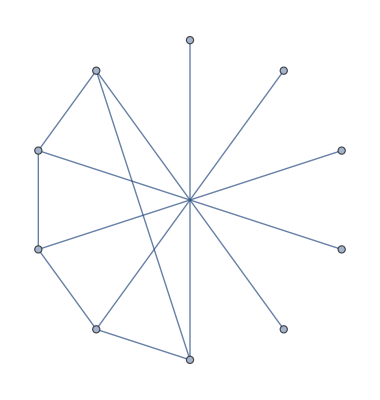

```mathematica
exp=EdgeAdd[CycleGraph[5],Table[i<->i+5,{i,1,5}]]
```

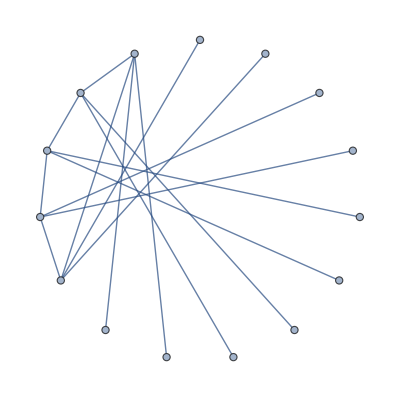

```mathematica
expDouble=EdgeAdd[CycleGraph[5],Flatten[Table[{i<->i+5,i<->i+10},{i,1,5}]]]
```

```mathematica
ToVars2[g_, pre_]:=Block[{exp,sep,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
exp= "Solve[";
sep="";
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "Element["<>var<>", Integers]";
sep=" && " 
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "(1<="<>var<>" <=4)";
sep=" && " 
];

edges=EdgeList[g];

exp= exp<>sep<> pre;(* "x1 == 1 && x2== 2 && x3==3";*)
sep=" && " ;

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 ="x" <> ToString[ edge[[1]] ];
var2 ="x" <> ToString[ edge[[2]] ];
exp= exp<>sep<> var1<>"!="<>var2;
sep=" && " 
];
exp=exp <> ", {";
sep="";
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> var;
sep=", " 
];
exp=exp <> "}]";
Return[Read[ StringToStream[ exp],Expression]]
]
```

```mathematica
CountSolutions[g_,edges1_,edges2_,edge3_, n_]:=Block[{ass, per,i,sols,result2,keys,edgeSet={edges1,edges2,edge3}, other,constr, temp, result3},
ass=Association[];
constr=NumberToConstraint[n];
sols=ToVars2[g,constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]={}
];
sols=ToVars2[EdgeAdd[g,edges1],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],1]
];
sols=ToVars2[EdgeAdd[g,edges2],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],2]
];
sols=ToVars2[EdgeAdd[g,edge3],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],3]
];
result2={};
keys=Keys[ass];
For[i=1,i≤Length[keys],i++,
AppendTo[result2,ass[keys[[i]]]]
];
temp=Sort[Tally[result2]];
result3={};
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2,3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,3}&]]];
result3=Map[If[#=={},0,First[#]]&,result3];
{ n,IntegerDigits[n,4,5]+1,result3}
]
```

```mathematica
NumberToConstraint[val_]:=Block[
{n=IntegerDigits[val,4,5],res, sep=""},
res="";
Table[res=res<>sep<>"x"<>ToString[i+5]<>"=="<>ToString[n[[i]]+1]; sep = " && ",{i,1,5}];
res]
```

```mathematica
NumberToConstraint2[val_]:=Block[
{n=IntegerDigits[val,4,10],res, sep=""},
res="";
Table[res=res<>sep<>"x"<>ToString[i+5]<>"=="<>ToString[n[[i]]+1]; sep = " && ",{i,1,10}];
res]
```

```mathematica
CountSolutions2[g_,edges1_,edges2_,edge3_, n_]:=Block[{ass, per,i,sols,result2,keys,edgeSet={edges1,edges2,edge3}, other,constr, temp, result3},
ass=Association[];
constr=NumberToConstraint2[n];
sols=ToVars2[g,constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]={}
];
sols=ToVars2[EdgeAdd[g,edges1],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],1]
];
sols=ToVars2[EdgeAdd[g,edges2],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],2]
];
sols=ToVars2[EdgeAdd[g,edge3],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],3]
];
result2={};
keys=Keys[ass];
For[i=1,i≤Length[keys],i++,
AppendTo[result2,ass[keys[[i]]]]
];
temp=Sort[Tally[result2]];
result3={};
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2,3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,3}&]]];
result3=Map[If[#=={},0,First[#]]&,result3];
If[result3[[1]]+result3[[2]]+result3[[3]]==0,Print[n->{IntegerDigits[n,4,10]+1,result3}]];
{ n,IntegerDigits[n,4,10]+1,result3}
]
```

```mathematica
NumberToConstraint[123]
```

x7==1 && x8==2 && x9==4 && x10==3 && x11==4

```mathematica
NumberToConstraint2[123]
```

x6==1 && x7==1 && x8==1 && x9==1 && x10==1 && x11==1 && x12==2 && x13==4 && x14==3 && x15==4

```mathematica
FromDigits[{1,2,3,4,2},4]
```

450

```mathematica
TableForm[
Monitor[
Table[CountSolutions[exp,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,0,1023}],k], TableDepth->2
]
```

0 | {1,1,1,1,1} | {6,6,18,0,0,0}
1 | {1,1,1,1,2} | {4,4,18,0,12,6}
2 | {1,1,1,1,3} | {4,4,18,0,12,6}
3 | {1,1,1,1,4} | {4,4,18,0,12,6}
4 | {1,1,1,2,1} | {4,4,18,6,6,6}
5 | {1,1,1,2,2} | {2,2,14,4,12,8}
6 | {1,1,1,2,3} | {3,3,17,4,12,8}
7 | {1,1,1,2,4} | {3,3,17,4,12,8}
8 | {1,1,1,3,1} | {4,4,18,6,6,6}
9 | {1,1,1,3,2} | {3,3,17,4,12,8}
10 | {1,1,1,3,3} | {2,2,14,4,12,8}
11 | {1,1,1,3,4} | {3,3,17,4,12,8}
12 | {1,1,1,4,1} | {4,4,18,6,6,6}
13 | {1,1,1,4,2} | {3,3,17,4,12,8}
14 | {1,1,1,4,3} | {3,3,17,4,12,8}
15 | {1,1,1,4,4} | {2,2,14,4,12,8}
16 | {1,1,2,1,1} | {4,4,18,0,6,12}
17 | {1,1,2,1,2} | {10,10,14,6,12,12}
18 | {1,1,2,1,3} | {8,8,17,6,12,12}
19 | {1,1,2,1,4} | {8,8,17,6,12,12}
20 | {1,1,2,2,1} | {2,2,14,4,8,12}
21 | {1,1,2,2,2} | {6,6,6,8,8,8}
22 | {1,1,2,2,3} | {5,5,14,6,10,11}
23 | {1,1,2,2,4} | {5,5,14,6,10,11}
24 | {1,1,2,3,1} | {3,3,17,4,8,12}
25 | {1,1,2,3,2} | {7,7,14,8,11,11}
26 | {1,1,2,3,3} | {5,5,14,6,11,10}
27 | {1,1,2,3,4} | {6,6,15,6,12,12}
28 | {1,1,2,4,1} | {3,3,17,4,8,12}
29 | {1,1,2,4,2} | {7,7,14,8,11,11}
30 | {1,1,2,4,3} | {6,6,15,6,12,12}
31 | {1,1,2,4,4} | {5,5,14,6,11,10}
32 | {1,1,3,1,1} | {4,4,18,0,6,12}
33 | {1,1,3,1,2} | {8,8,17,6,12,12}
34 | {1,1,3,1,3} | {10,10,14,6,12,12}
35 | {1,1,3,1,4} | {8,8,17,6,12,12}
36 | {1,1,3,2,1} | {3,3,17,4,8,12}
37 | {1,1,3,2,2} | {5,5,14,6,11,10}
38 | {1,1,3,2,3} | {7,7,14,8,11,11}
39 | {1,1,3,2,4} | {6,6,15,6,12,12}
40 | {1,1,3,3,1} | {2,2,14,4,8,12}
41 | {1,1,3,3,2} | {5,5,14,6,10,11}
42 | {1,1,3,3,3} | {6,6,6,8,8,8}
43 | {1,1,3,3,4} | {5,5,14,6,10,11}
44 | {1,1,3,4,1} | {3,3,17,4,8,12}
45 | {1,1,3,4,2} | {6,6,15,6,12,12}
46 | {1,1,3,4,3} | {7,7,14,8,11,11}
47 | {1,1,3,4,4} | {5,5,14,6,11,10}
48 | {1,1,4,1,1} | {4,4,18,0,6,12}
49 | {1,1,4,1,2} | {8,8,17,6,12,12}
50 | {1,1,4,1,3} | {8,8,17,6,12,12}
51 | {1,1,4,1,4} | {10,10,14,6,12,12}
52 | {1,1,4,2,1} | {3,3,17,4,8,12}
53 | {1,1,4,2,2} | {5,5,14,6,11,10}
54 | {1,1,4,2,3} | {6,6,15,6,12,12}
55 | {1,1,4,2,4} | {7,7,14,8,11,11}
56 | {1,1,4,3,1} | {3,3,17,4,8,12}
57 | {1,1,4,3,2} | {6,6,15,6,12,12}
58 | {1,1,4,3,3} | {5,5,14,6,11,10}
59 | {1,1,4,3,4} | {7,7,14,8,11,11}
60 | {1,1,4,4,1} | {2,2,14,4,8,12}
61 | {1,1,4,4,2} | {5,5,14,6,10,11}
62 | {1,1,4,4,3} | {5,5,14,6,10,11}
63 | {1,1,4,4,4} | {6,6,6,8,8,8}
64 | {1,2,1,1,1} | {4,10,12,6,12,0}
65 | {1,2,1,1,2} | {2,6,26,4,16,10}
66 | {1,2,1,1,3} | {3,7,23,4,16,10}
67 | {1,2,1,1,4} | {3,7,23,4,16,10}
68 | {1,2,1,2,1} | {10,6,18,8,12,10}
69 | {1,2,1,2,2} | {6,2,26,4,10,16}
70 | {1,2,1,2,3} | {7,5,23,6,13,14}
71 | {1,2,1,2,4} | {7,5,23,6,13,14}
72 | {1,2,1,3,1} | {8,7,18,8,12,10}
73 | {1,2,1,3,2} | {5,5,25,5,14,14}
74 | {1,2,1,3,3} | {5,4,19,5,13,12}
75 | {1,2,1,3,4} | {6,5,22,6,15,12}
76 | {1,2,1,4,1} | {8,7,18,8,12,10}
77 | {1,2,1,4,2} | {5,5,25,5,14,14}
78 | {1,2,1,4,3} | {6,5,22,6,15,12}
79 | {1,2,1,4,4} | {5,4,19,5,13,12}
80 | {1,2,2,1,1} | {2,6,10,4,12,8}
81 | {1,2,2,1,2} | {6,10,18,8,10,12}
82 | {1,2,2,1,3} | {5,7,16,6,13,11}
83 | {1,2,2,1,4} | {5,7,16,6,13,11}
84 | {1,2,2,2,1} | {6,2,10,4,8,12}
85 | {1,2,2,2,2} | {10,4,12,6,0,12}
86 | {1,2,2,2,3} | {7,3,13,4,8,12}
87 | {1,2,2,2,4} | {7,3,13,4,8,12}
88 | {1,2,2,3,1} | {5,5,14,5,11,11}
89 | {1,2,2,3,2} | {7,8,18,8,10,12}
90 | {1,2,2,3,3} | {4,5,15,5,12,10}
91 | {1,2,2,3,4} | {5,6,16,6,12,12}
92 | {1,2,2,4,1} | {5,5,14,5,11,11}
93 | {1,2,2,4,2} | {7,8,18,8,10,12}
94 | {1,2,2,4,3} | {5,6,16,6,12,12}
95 | {1,2,2,4,4} | {4,5,15,5,12,10}
96 | {1,2,3,1,1} | {3,7,13,4,12,8}
97 | {1,2,3,1,2} | {5,7,23,6,14,13}
98 | {1,2,3,1,3} | {7,11,17,8,13,12}
99 | {1,2,3,1,4} | {6,8,19,6,15,12}
100 | {1,2,3,2,1} | {7,5,16,6,11,13}
101 | {1,2,3,2,2} | {7,3,23,4,10,16}
102 | {1,2,3,2,3} | {11,7,17,8,12,13}
103 | {1,2,3,2,4} | {8,6,19,6,12,15}
104 | {1,2,3,3,1} | {5,4,15,5,10,12}
105 | {1,2,3,3,2} | {4,5,19,5,12,13}
106 | {1,2,3,3,3} | {7,7,9,8,8,8}
107 | {1,2,3,3,4} | {5,5,17,6,12,12}
108 | {1,2,3,4,1} | {6,5,16,6,12,12}
109 | {1,2,3,4,2} | {5,6,22,6,12,15}
110 | {1,2,3,4,3} | {8,8,17,9,12,12}
111 | {1,2,3,4,4} | {5,5,17,6,12,12}
112 | {1,2,4,1,1} | {3,7,13,4,12,8}
113 | {1,2,4,1,2} | {5,7,23,6,14,13}
114 | {1,2,4,1,3} | {6,8,19,6,15,12}
115 | {1,2,4,1,4} | {7,11,17,8,13,12}
116 | {1,2,4,2,1} | {7,5,16,6,11,13}
117 | {1,2,4,2,2} | {7,3,23,4,10,16}
118 | {1,2,4,2,3} | {8,6,19,6,12,15}
119 | {1,2,4,2,4} | {11,7,17,8,12,13}
120 | {1,2,4,3,1} | {6,5,16,6,12,12}
121 | {1,2,4,3,2} | {5,6,22,6,12,15}
122 | {1,2,4,3,3} | {5,5,17,6,12,12}
123 | {1,2,4,3,4} | {8,8,17,9,12,12}
124 | {1,2,4,4,1} | {5,4,15,5,10,12}
125 | {1,2,4,4,2} | {4,5,19,5,12,13}
126 | {1,2,4,4,3} | {5,5,17,6,12,12}
127 | {1,2,4,4,4} | {7,7,9,8,8,8}
128 | {1,3,1,1,1} | {4,10,12,6,12,0}
129 | {1,3,1,1,2} | {3,7,23,4,16,10}
130 | {1,3,1,1,3} | {2,6,26,4,16,10}
131 | {1,3,1,1,4} | {3,7,23,4,16,10}
132 | {1,3,1,2,1} | {8,7,18,8,12,10}
133 | {1,3,1,2,2} | {5,4,19,5,13,12}
134 | {1,3,1,2,3} | {5,5,25,5,14,14}
135 | {1,3,1,2,4} | {6,5,22,6,15,12}
136 | {1,3,1,3,1} | {10,6,18,8,12,10}
137 | {1,3,1,3,2} | {7,5,23,6,13,14}
138 | {1,3,1,3,3} | {6,2,26,4,10,16}
139 | {1,3,1,3,4} | {7,5,23,6,13,14}
140 | {1,3,1,4,1} | {8,7,18,8,12,10}
141 | {1,3,1,4,2} | {6,5,22,6,15,12}
142 | {1,3,1,4,3} | {5,5,25,5,14,14}
143 | {1,3,1,4,4} | {5,4,19,5,13,12}
144 | {1,3,2,1,1} | {3,7,13,4,12,8}
145 | {1,3,2,1,2} | {7,11,17,8,13,12}
146 | {1,3,2,1,3} | {5,7,23,6,14,13}
147 | {1,3,2,1,4} | {6,8,19,6,15,12}
148 | {1,3,2,2,1} | {5,4,15,5,10,12}
149 | {1,3,2,2,2} | {7,7,9,8,8,8}
150 | {1,3,2,2,3} | {4,5,19,5,12,13}
151 | {1,3,2,2,4} | {5,5,17,6,12,12}
152 | {1,3,2,3,1} | {7,5,16,6,11,13}
153 | {1,3,2,3,2} | {11,7,17,8,12,13}
154 | {1,3,2,3,3} | {7,3,23,4,10,16}
155 | {1,3,2,3,4} | {8,6,19,6,12,15}
156 | {1,3,2,4,1} | {6,5,16,6,12,12}
157 | {1,3,2,4,2} | {8,8,17,9,12,12}
158 | {1,3,2,4,3} | {5,6,22,6,12,15}
159 | {1,3,2,4,4} | {5,5,17,6,12,12}
160 | {1,3,3,1,1} | {2,6,10,4,12,8}
161 | {1,3,3,1,2} | {5,7,16,6,13,11}
162 | {1,3,3,1,3} | {6,10,18,8,10,12}
163 | {1,3,3,1,4} | {5,7,16,6,13,11}
164 | {1,3,3,2,1} | {5,5,14,5,11,11}
165 | {1,3,3,2,2} | {4,5,15,5,12,10}
166 | {1,3,3,2,3} | {7,8,18,8,10,12}
167 | {1,3,3,2,4} | {5,6,16,6,12,12}
168 | {1,3,3,3,1} | {6,2,10,4,8,12}
169 | {1,3,3,3,2} | {7,3,13,4,8,12}
170 | {1,3,3,3,3} | {10,4,12,6,0,12}
171 | {1,3,3,3,4} | {7,3,13,4,8,12}
172 | {1,3,3,4,1} | {5,5,14,5,11,11}
173 | {1,3,3,4,2} | {5,6,16,6,12,12}
174 | {1,3,3,4,3} | {7,8,18,8,10,12}
175 | {1,3,3,4,4} | {4,5,15,5,12,10}
176 | {1,3,4,1,1} | {3,7,13,4,12,8}
177 | {1,3,4,1,2} | {6,8,19,6,15,12}
178 | {1,3,4,1,3} | {5,7,23,6,14,13}
179 | {1,3,4,1,4} | {7,11,17,8,13,12}
180 | {1,3,4,2,1} | {6,5,16,6,12,12}
181 | {1,3,4,2,2} | {5,5,17,6,12,12}
182 | {1,3,4,2,3} | {5,6,22,6,12,15}
183 | {1,3,4,2,4} | {8,8,17,9,12,12}
184 | {1,3,4,3,1} | {7,5,16,6,11,13}
185 | {1,3,4,3,2} | {8,6,19,6,12,15}
186 | {1,3,4,3,3} | {7,3,23,4,10,16}
187 | {1,3,4,3,4} | {11,7,17,8,12,13}
188 | {1,3,4,4,1} | {5,4,15,5,10,12}
189 | {1,3,4,4,2} | {5,5,17,6,12,12}
190 | {1,3,4,4,3} | {4,5,19,5,12,13}
191 | {1,3,4,4,4} | {7,7,9,8,8,8}
192 | {1,4,1,1,1} | {4,10,12,6,12,0}
193 | {1,4,1,1,2} | {3,7,23,4,16,10}
194 | {1,4,1,1,3} | {3,7,23,4,16,10}
195 | {1,4,1,1,4} | {2,6,26,4,16,10}
196 | {1,4,1,2,1} | {8,7,18,8,12,10}
197 | {1,4,1,2,2} | {5,4,19,5,13,12}
198 | {1,4,1,2,3} | {6,5,22,6,15,12}
199 | {1,4,1,2,4} | {5,5,25,5,14,14}
200 | {1,4,1,3,1} | {8,7,18,8,12,10}
201 | {1,4,1,3,2} | {6,5,22,6,15,12}
202 | {1,4,1,3,3} | {5,4,19,5,13,12}
203 | {1,4,1,3,4} | {5,5,25,5,14,14}
204 | {1,4,1,4,1} | {10,6,18,8,12,10}
205 | {1,4,1,4,2} | {7,5,23,6,13,14}
206 | {1,4,1,4,3} | {7,5,23,6,13,14}
207 | {1,4,1,4,4} | {6,2,26,4,10,16}
208 | {1,4,2,1,1} | {3,7,13,4,12,8}
209 | {1,4,2,1,2} | {7,11,17,8,13,12}
210 | {1,4,2,1,3} | {6,8,19,6,15,12}
211 | {1,4,2,1,4} | {5,7,23,6,14,13}
212 | {1,4,2,2,1} | {5,4,15,5,10,12}
213 | {1,4,2,2,2} | {7,7,9,8,8,8}
214 | {1,4,2,2,3} | {5,5,17,6,12,12}
215 | {1,4,2,2,4} | {4,5,19,5,12,13}
216 | {1,4,2,3,1} | {6,5,16,6,12,12}
217 | {1,4,2,3,2} | {8,8,17,9,12,12}
218 | {1,4,2,3,3} | {5,5,17,6,12,12}
219 | {1,4,2,3,4} | {5,6,22,6,12,15}
220 | {1,4,2,4,1} | {7,5,16,6,11,13}
221 | {1,4,2,4,2} | {11,7,17,8,12,13}
222 | {1,4,2,4,3} | {8,6,19,6,12,15}
223 | {1,4,2,4,4} | {7,3,23,4,10,16}
224 | {1,4,3,1,1} | {3,7,13,4,12,8}
225 | {1,4,3,1,2} | {6,8,19,6,15,12}
226 | {1,4,3,1,3} | {7,11,17,8,13,12}
227 | {1,4,3,1,4} | {5,7,23,6,14,13}
228 | {1,4,3,2,1} | {6,5,16,6,12,12}
229 | {1,4,3,2,2} | {5,5,17,6,12,12}
230 | {1,4,3,2,3} | {8,8,17,9,12,12}
231 | {1,4,3,2,4} | {5,6,22,6,12,15}
232 | {1,4,3,3,1} | {5,4,15,5,10,12}
233 | {1,4,3,3,2} | {5,5,17,6,12,12}
234 | {1,4,3,3,3} | {7,7,9,8,8,8}
235 | {1,4,3,3,4} | {4,5,19,5,12,13}
236 | {1,4,3,4,1} | {7,5,16,6,11,13}
237 | {1,4,3,4,2} | {8,6,19,6,12,15}
238 | {1,4,3,4,3} | {11,7,17,8,12,13}
239 | {1,4,3,4,4} | {7,3,23,4,10,16}
240 | {1,4,4,1,1} | {2,6,10,4,12,8}
241 | {1,4,4,1,2} | {5,7,16,6,13,11}
242 | {1,4,4,1,3} | {5,7,16,6,13,11}
243 | {1,4,4,1,4} | {6,10,18,8,10,12}
244 | {1,4,4,2,1} | {5,5,14,5,11,11}
245 | {1,4,4,2,2} | {4,5,15,5,12,10}
246 | {1,4,4,2,3} | {5,6,16,6,12,12}
247 | {1,4,4,2,4} | {7,8,18,8,10,12}
248 | {1,4,4,3,1} | {5,5,14,5,11,11}
249 | {1,4,4,3,2} | {5,6,16,6,12,12}
250 | {1,4,4,3,3} | {4,5,15,5,12,10}
251 | {1,4,4,3,4} | {7,8,18,8,10,12}
252 | {1,4,4,4,1} | {6,2,10,4,8,12}
253 | {1,4,4,4,2} | {7,3,13,4,8,12}
254 | {1,4,4,4,3} | {7,3,13,4,8,12}
255 | {1,4,4,4,4} | {10,4,12,6,0,12}
256 | {2,1,1,1,1} | {10,4,12,6,0,12}
257 | {2,1,1,1,2} | {6,2,10,4,8,12}
258 | {2,1,1,1,3} | {7,3,13,4,8,12}
259 | {2,1,1,1,4} | {7,3,13,4,8,12}
260 | {2,1,1,2,1} | {6,10,18,8,10,12}
261 | {2,1,1,2,2} | {2,6,10,4,12,8}
262 | {2,1,1,2,3} | {5,7,16,6,13,11}
263 | {2,1,1,2,4} | {5,7,16,6,13,11}
264 | {2,1,1,3,1} | {7,8,18,8,10,12}
265 | {2,1,1,3,2} | {5,5,14,5,11,11}
266 | {2,1,1,3,3} | {4,5,15,5,12,10}
267 | {2,1,1,3,4} | {5,6,16,6,12,12}
268 | {2,1,1,4,1} | {7,8,18,8,10,12}
269 | {2,1,1,4,2} | {5,5,14,5,11,11}
270 | {2,1,1,4,3} | {5,6,16,6,12,12}
271 | {2,1,1,4,4} | {4,5,15,5,12,10}
272 | {2,1,2,1,1} | {6,2,26,4,10,16}
273 | {2,1,2,1,2} | {10,6,18,8,12,10}
274 | {2,1,2,1,3} | {7,5,23,6,13,14}
275 | {2,1,2,1,4} | {7,5,23,6,13,14}
276 | {2,1,2,2,1} | {2,6,26,4,16,10}
277 | {2,1,2,2,2} | {4,10,12,6,12,0}
278 | {2,1,2,2,3} | {3,7,23,4,16,10}
279 | {2,1,2,2,4} | {3,7,23,4,16,10}
280 | {2,1,2,3,1} | {5,5,25,5,14,14}
281 | {2,1,2,3,2} | {8,7,18,8,12,10}
282 | {2,1,2,3,3} | {5,4,19,5,13,12}
283 | {2,1,2,3,4} | {6,5,22,6,15,12}
284 | {2,1,2,4,1} | {5,5,25,5,14,14}
285 | {2,1,2,4,2} | {8,7,18,8,12,10}
286 | {2,1,2,4,3} | {6,5,22,6,15,12}
287 | {2,1,2,4,4} | {5,4,19,5,13,12}
288 | {2,1,3,1,1} | {7,3,23,4,10,16}
289 | {2,1,3,1,2} | {7,5,16,6,11,13}
290 | {2,1,3,1,3} | {11,7,17,8,12,13}
291 | {2,1,3,1,4} | {8,6,19,6,12,15}
292 | {2,1,3,2,1} | {5,7,23,6,14,13}
293 | {2,1,3,2,2} | {3,7,13,4,12,8}
294 | {2,1,3,2,3} | {7,11,17,8,13,12}
295 | {2,1,3,2,4} | {6,8,19,6,15,12}
296 | {2,1,3,3,1} | {4,5,19,5,12,13}
297 | {2,1,3,3,2} | {5,4,15,5,10,12}
298 | {2,1,3,3,3} | {7,7,9,8,8,8}
299 | {2,1,3,3,4} | {5,5,17,6,12,12}
300 | {2,1,3,4,1} | {5,6,22,6,12,15}
301 | {2,1,3,4,2} | {6,5,16,6,12,12}
302 | {2,1,3,4,3} | {8,8,17,9,12,12}
303 | {2,1,3,4,4} | {5,5,17,6,12,12}
304 | {2,1,4,1,1} | {7,3,23,4,10,16}
305 | {2,1,4,1,2} | {7,5,16,6,11,13}
306 | {2,1,4,1,3} | {8,6,19,6,12,15}
307 | {2,1,4,1,4} | {11,7,17,8,12,13}
308 | {2,1,4,2,1} | {5,7,23,6,14,13}
309 | {2,1,4,2,2} | {3,7,13,4,12,8}
310 | {2,1,4,2,3} | {6,8,19,6,15,12}
311 | {2,1,4,2,4} | {7,11,17,8,13,12}
312 | {2,1,4,3,1} | {5,6,22,6,12,15}
313 | {2,1,4,3,2} | {6,5,16,6,12,12}
314 | {2,1,4,3,3} | {5,5,17,6,12,12}
315 | {2,1,4,3,4} | {8,8,17,9,12,12}
316 | {2,1,4,4,1} | {4,5,19,5,12,13}
317 | {2,1,4,4,2} | {5,4,15,5,10,12}
318 | {2,1,4,4,3} | {5,5,17,6,12,12}
319 | {2,1,4,4,4} | {7,7,9,8,8,8}
320 | {2,2,1,1,1} | {6,6,6,8,8,8}
321 | {2,2,1,1,2} | {2,2,14,4,8,12}
322 | {2,2,1,1,3} | {5,5,14,6,10,11}
323 | {2,2,1,1,4} | {5,5,14,6,10,11}
324 | {2,2,1,2,1} | {10,10,14,6,12,12}
325 | {2,2,1,2,2} | {4,4,18,0,6,12}
326 | {2,2,1,2,3} | {8,8,17,6,12,12}
327 | {2,2,1,2,4} | {8,8,17,6,12,12}
328 | {2,2,1,3,1} | {7,7,14,8,11,11}
329 | {2,2,1,3,2} | {3,3,17,4,8,12}
330 | {2,2,1,3,3} | {5,5,14,6,11,10}
331 | {2,2,1,3,4} | {6,6,15,6,12,12}
332 | {2,2,1,4,1} | {7,7,14,8,11,11}
333 | {2,2,1,4,2} | {3,3,17,4,8,12}
334 | {2,2,1,4,3} | {6,6,15,6,12,12}
335 | {2,2,1,4,4} | {5,5,14,6,11,10}
336 | {2,2,2,1,1} | {2,2,14,4,12,8}
337 | {2,2,2,1,2} | {4,4,18,6,6,6}
338 | {2,2,2,1,3} | {3,3,17,4,12,8}
339 | {2,2,2,1,4} | {3,3,17,4,12,8}
340 | {2,2,2,2,1} | {4,4,18,0,12,6}
341 | {2,2,2,2,2} | {6,6,18,0,0,0}
342 | {2,2,2,2,3} | {4,4,18,0,12,6}
343 | {2,2,2,2,4} | {4,4,18,0,12,6}
344 | {2,2,2,3,1} | {3,3,17,4,12,8}
345 | {2,2,2,3,2} | {4,4,18,6,6,6}
346 | {2,2,2,3,3} | {2,2,14,4,12,8}
347 | {2,2,2,3,4} | {3,3,17,4,12,8}
348 | {2,2,2,4,1} | {3,3,17,4,12,8}
349 | {2,2,2,4,2} | {4,4,18,6,6,6}
350 | {2,2,2,4,3} | {3,3,17,4,12,8}
351 | {2,2,2,4,4} | {2,2,14,4,12,8}
352 | {2,2,3,1,1} | {5,5,14,6,11,10}
353 | {2,2,3,1,2} | {3,3,17,4,8,12}
354 | {2,2,3,1,3} | {7,7,14,8,11,11}
355 | {2,2,3,1,4} | {6,6,15,6,12,12}
356 | {2,2,3,2,1} | {8,8,17,6,12,12}
357 | {2,2,3,2,2} | {4,4,18,0,6,12}
358 | {2,2,3,2,3} | {10,10,14,6,12,12}
359 | {2,2,3,2,4} | {8,8,17,6,12,12}
360 | {2,2,3,3,1} | {5,5,14,6,10,11}
361 | {2,2,3,3,2} | {2,2,14,4,8,12}
362 | {2,2,3,3,3} | {6,6,6,8,8,8}
363 | {2,2,3,3,4} | {5,5,14,6,10,11}
364 | {2,2,3,4,1} | {6,6,15,6,12,12}
365 | {2,2,3,4,2} | {3,3,17,4,8,12}
366 | {2,2,3,4,3} | {7,7,14,8,11,11}
367 | {2,2,3,4,4} | {5,5,14,6,11,10}
368 | {2,2,4,1,1} | {5,5,14,6,11,10}
369 | {2,2,4,1,2} | {3,3,17,4,8,12}
370 | {2,2,4,1,3} | {6,6,15,6,12,12}
371 | {2,2,4,1,4} | {7,7,14,8,11,11}
372 | {2,2,4,2,1} | {8,8,17,6,12,12}
373 | {2,2,4,2,2} | {4,4,18,0,6,12}
374 | {2,2,4,2,3} | {8,8,17,6,12,12}
375 | {2,2,4,2,4} | {10,10,14,6,12,12}
376 | {2,2,4,3,1} | {6,6,15,6,12,12}
377 | {2,2,4,3,2} | {3,3,17,4,8,12}
378 | {2,2,4,3,3} | {5,5,14,6,11,10}
379 | {2,2,4,3,4} | {7,7,14,8,11,11}
380 | {2,2,4,4,1} | {5,5,14,6,10,11}
381 | {2,2,4,4,2} | {2,2,14,4,8,12}
382 | {2,2,4,4,3} | {5,5,14,6,10,11}
383 | {2,2,4,4,4} | {6,6,6,8,8,8}
384 | {2,3,1,1,1} | {7,7,9,8,8,8}
385 | {2,3,1,1,2} | {5,4,15,5,10,12}
386 | {2,3,1,1,3} | {4,5,19,5,12,13}
387 | {2,3,1,1,4} | {5,5,17,6,12,12}
388 | {2,3,1,2,1} | {7,11,17,8,13,12}
389 | {2,3,1,2,2} | {3,7,13,4,12,8}
390 | {2,3,1,2,3} | {5,7,23,6,14,13}
391 | {2,3,1,2,4} | {6,8,19,6,15,12}
392 | {2,3,1,3,1} | {11,7,17,8,12,13}
393 | {2,3,1,3,2} | {7,5,16,6,11,13}
394 | {2,3,1,3,3} | {7,3,23,4,10,16}
395 | {2,3,1,3,4} | {8,6,19,6,12,15}
396 | {2,3,1,4,1} | {8,8,17,9,12,12}
397 | {2,3,1,4,2} | {6,5,16,6,12,12}
398 | {2,3,1,4,3} | {5,6,22,6,12,15}
399 | {2,3,1,4,4} | {5,5,17,6,12,12}
400 | {2,3,2,1,1} | {5,4,19,5,13,12}
401 | {2,3,2,1,2} | {8,7,18,8,12,10}
402 | {2,3,2,1,3} | {5,5,25,5,14,14}
403 | {2,3,2,1,4} | {6,5,22,6,15,12}
404 | {2,3,2,2,1} | {3,7,23,4,16,10}
405 | {2,3,2,2,2} | {4,10,12,6,12,0}
406 | {2,3,2,2,3} | {2,6,26,4,16,10}
407 | {2,3,2,2,4} | {3,7,23,4,16,10}
408 | {2,3,2,3,1} | {7,5,23,6,13,14}
409 | {2,3,2,3,2} | {10,6,18,8,12,10}
410 | {2,3,2,3,3} | {6,2,26,4,10,16}
411 | {2,3,2,3,4} | {7,5,23,6,13,14}
412 | {2,3,2,4,1} | {6,5,22,6,15,12}
413 | {2,3,2,4,2} | {8,7,18,8,12,10}
414 | {2,3,2,4,3} | {5,5,25,5,14,14}
415 | {2,3,2,4,4} | {5,4,19,5,13,12}
416 | {2,3,3,1,1} | {4,5,15,5,12,10}
417 | {2,3,3,1,2} | {5,5,14,5,11,11}
418 | {2,3,3,1,3} | {7,8,18,8,10,12}
419 | {2,3,3,1,4} | {5,6,16,6,12,12}
420 | {2,3,3,2,1} | {5,7,16,6,13,11}
421 | {2,3,3,2,2} | {2,6,10,4,12,8}
422 | {2,3,3,2,3} | {6,10,18,8,10,12}
423 | {2,3,3,2,4} | {5,7,16,6,13,11}
424 | {2,3,3,3,1} | {7,3,13,4,8,12}
425 | {2,3,3,3,2} | {6,2,10,4,8,12}
426 | {2,3,3,3,3} | {10,4,12,6,0,12}
427 | {2,3,3,3,4} | {7,3,13,4,8,12}
428 | {2,3,3,4,1} | {5,6,16,6,12,12}
429 | {2,3,3,4,2} | {5,5,14,5,11,11}
430 | {2,3,3,4,3} | {7,8,18,8,10,12}
431 | {2,3,3,4,4} | {4,5,15,5,12,10}
432 | {2,3,4,1,1} | {5,5,17,6,12,12}
433 | {2,3,4,1,2} | {6,5,16,6,12,12}
434 | {2,3,4,1,3} | {5,6,22,6,12,15}
435 | {2,3,4,1,4} | {8,8,17,9,12,12}
436 | {2,3,4,2,1} | {6,8,19,6,15,12}
437 | {2,3,4,2,2} | {3,7,13,4,12,8}
438 | {2,3,4,2,3} | {5,7,23,6,14,13}
439 | {2,3,4,2,4} | {7,11,17,8,13,12}
440 | {2,3,4,3,1} | {8,6,19,6,12,15}
441 | {2,3,4,3,2} | {7,5,16,6,11,13}
442 | {2,3,4,3,3} | {7,3,23,4,10,16}
443 | {2,3,4,3,4} | {11,7,17,8,12,13}
444 | {2,3,4,4,1} | {5,5,17,6,12,12}
445 | {2,3,4,4,2} | {5,4,15,5,10,12}
446 | {2,3,4,4,3} | {4,5,19,5,12,13}
447 | {2,3,4,4,4} | {7,7,9,8,8,8}
448 | {2,4,1,1,1} | {7,7,9,8,8,8}
449 | {2,4,1,1,2} | {5,4,15,5,10,12}
450 | {2,4,1,1,3} | {5,5,17,6,12,12}
451 | {2,4,1,1,4} | {4,5,19,5,12,13}
452 | {2,4,1,2,1} | {7,11,17,8,13,12}
453 | {2,4,1,2,2} | {3,7,13,4,12,8}
454 | {2,4,1,2,3} | {6,8,19,6,15,12}
455 | {2,4,1,2,4} | {5,7,23,6,14,13}
456 | {2,4,1,3,1} | {8,8,17,9,12,12}
457 | {2,4,1,3,2} | {6,5,16,6,12,12}
458 | {2,4,1,3,3} | {5,5,17,6,12,12}
459 | {2,4,1,3,4} | {5,6,22,6,12,15}
460 | {2,4,1,4,1} | {11,7,17,8,12,13}
461 | {2,4,1,4,2} | {7,5,16,6,11,13}
462 | {2,4,1,4,3} | {8,6,19,6,12,15}
463 | {2,4,1,4,4} | {7,3,23,4,10,16}
464 | {2,4,2,1,1} | {5,4,19,5,13,12}
465 | {2,4,2,1,2} | {8,7,18,8,12,10}
466 | {2,4,2,1,3} | {6,5,22,6,15,12}
467 | {2,4,2,1,4} | {5,5,25,5,14,14}
468 | {2,4,2,2,1} | {3,7,23,4,16,10}
469 | {2,4,2,2,2} | {4,10,12,6,12,0}
470 | {2,4,2,2,3} | {3,7,23,4,16,10}
471 | {2,4,2,2,4} | {2,6,26,4,16,10}
472 | {2,4,2,3,1} | {6,5,22,6,15,12}
473 | {2,4,2,3,2} | {8,7,18,8,12,10}
474 | {2,4,2,3,3} | {5,4,19,5,13,12}
475 | {2,4,2,3,4} | {5,5,25,5,14,14}
476 | {2,4,2,4,1} | {7,5,23,6,13,14}
477 | {2,4,2,4,2} | {10,6,18,8,12,10}
478 | {2,4,2,4,3} | {7,5,23,6,13,14}
479 | {2,4,2,4,4} | {6,2,26,4,10,16}
480 | {2,4,3,1,1} | {5,5,17,6,12,12}
481 | {2,4,3,1,2} | {6,5,16,6,12,12}
482 | {2,4,3,1,3} | {8,8,17,9,12,12}
483 | {2,4,3,1,4} | {5,6,22,6,12,15}
484 | {2,4,3,2,1} | {6,8,19,6,15,12}
485 | {2,4,3,2,2} | {3,7,13,4,12,8}
486 | {2,4,3,2,3} | {7,11,17,8,13,12}
487 | {2,4,3,2,4} | {5,7,23,6,14,13}
488 | {2,4,3,3,1} | {5,5,17,6,12,12}
489 | {2,4,3,3,2} | {5,4,15,5,10,12}
490 | {2,4,3,3,3} | {7,7,9,8,8,8}
491 | {2,4,3,3,4} | {4,5,19,5,12,13}
492 | {2,4,3,4,1} | {8,6,19,6,12,15}
493 | {2,4,3,4,2} | {7,5,16,6,11,13}
494 | {2,4,3,4,3} | {11,7,17,8,12,13}
495 | {2,4,3,4,4} | {7,3,23,4,10,16}
496 | {2,4,4,1,1} | {4,5,15,5,12,10}
497 | {2,4,4,1,2} | {5,5,14,5,11,11}
498 | {2,4,4,1,3} | {5,6,16,6,12,12}
499 | {2,4,4,1,4} | {7,8,18,8,10,12}
500 | {2,4,4,2,1} | {5,7,16,6,13,11}
501 | {2,4,4,2,2} | {2,6,10,4,12,8}
502 | {2,4,4,2,3} | {5,7,16,6,13,11}
503 | {2,4,4,2,4} | {6,10,18,8,10,12}
504 | {2,4,4,3,1} | {5,6,16,6,12,12}
505 | {2,4,4,3,2} | {5,5,14,5,11,11}
506 | {2,4,4,3,3} | {4,5,15,5,12,10}
507 | {2,4,4,3,4} | {7,8,18,8,10,12}
508 | {2,4,4,4,1} | {7,3,13,4,8,12}
509 | {2,4,4,4,2} | {6,2,10,4,8,12}
510 | {2,4,4,4,3} | {7,3,13,4,8,12}
511 | {2,4,4,4,4} | {10,4,12,6,0,12}
512 | {3,1,1,1,1} | {10,4,12,6,0,12}
513 | {3,1,1,1,2} | {7,3,13,4,8,12}
514 | {3,1,1,1,3} | {6,2,10,4,8,12}
515 | {3,1,1,1,4} | {7,3,13,4,8,12}
516 | {3,1,1,2,1} | {7,8,18,8,10,12}
517 | {3,1,1,2,2} | {4,5,15,5,12,10}
518 | {3,1,1,2,3} | {5,5,14,5,11,11}
519 | {3,1,1,2,4} | {5,6,16,6,12,12}
520 | {3,1,1,3,1} | {6,10,18,8,10,12}
521 | {3,1,1,3,2} | {5,7,16,6,13,11}
522 | {3,1,1,3,3} | {2,6,10,4,12,8}
523 | {3,1,1,3,4} | {5,7,16,6,13,11}
524 | {3,1,1,4,1} | {7,8,18,8,10,12}
525 | {3,1,1,4,2} | {5,6,16,6,12,12}
526 | {3,1,1,4,3} | {5,5,14,5,11,11}
527 | {3,1,1,4,4} | {4,5,15,5,12,10}
528 | {3,1,2,1,1} | {7,3,23,4,10,16}
529 | {3,1,2,1,2} | {11,7,17,8,12,13}
530 | {3,1,2,1,3} | {7,5,16,6,11,13}
531 | {3,1,2,1,4} | {8,6,19,6,12,15}
532 | {3,1,2,2,1} | {4,5,19,5,12,13}
533 | {3,1,2,2,2} | {7,7,9,8,8,8}
534 | {3,1,2,2,3} | {5,4,15,5,10,12}
535 | {3,1,2,2,4} | {5,5,17,6,12,12}
536 | {3,1,2,3,1} | {5,7,23,6,14,13}
537 | {3,1,2,3,2} | {7,11,17,8,13,12}
538 | {3,1,2,3,3} | {3,7,13,4,12,8}
539 | {3,1,2,3,4} | {6,8,19,6,15,12}
540 | {3,1,2,4,1} | {5,6,22,6,12,15}
541 | {3,1,2,4,2} | {8,8,17,9,12,12}
542 | {3,1,2,4,3} | {6,5,16,6,12,12}
543 | {3,1,2,4,4} | {5,5,17,6,12,12}
544 | {3,1,3,1,1} | {6,2,26,4,10,16}
545 | {3,1,3,1,2} | {7,5,23,6,13,14}
546 | {3,1,3,1,3} | {10,6,18,8,12,10}
547 | {3,1,3,1,4} | {7,5,23,6,13,14}
548 | {3,1,3,2,1} | {5,5,25,5,14,14}
549 | {3,1,3,2,2} | {5,4,19,5,13,12}
550 | {3,1,3,2,3} | {8,7,18,8,12,10}
551 | {3,1,3,2,4} | {6,5,22,6,15,12}
552 | {3,1,3,3,1} | {2,6,26,4,16,10}
553 | {3,1,3,3,2} | {3,7,23,4,16,10}
554 | {3,1,3,3,3} | {4,10,12,6,12,0}
555 | {3,1,3,3,4} | {3,7,23,4,16,10}
556 | {3,1,3,4,1} | {5,5,25,5,14,14}
557 | {3,1,3,4,2} | {6,5,22,6,15,12}
558 | {3,1,3,4,3} | {8,7,18,8,12,10}
559 | {3,1,3,4,4} | {5,4,19,5,13,12}
560 | {3,1,4,1,1} | {7,3,23,4,10,16}
561 | {3,1,4,1,2} | {8,6,19,6,12,15}
562 | {3,1,4,1,3} | {7,5,16,6,11,13}
563 | {3,1,4,1,4} | {11,7,17,8,12,13}
564 | {3,1,4,2,1} | {5,6,22,6,12,15}
565 | {3,1,4,2,2} | {5,5,17,6,12,12}
566 | {3,1,4,2,3} | {6,5,16,6,12,12}
567 | {3,1,4,2,4} | {8,8,17,9,12,12}
568 | {3,1,4,3,1} | {5,7,23,6,14,13}
569 | {3,1,4,3,2} | {6,8,19,6,15,12}
570 | {3,1,4,3,3} | {3,7,13,4,12,8}
571 | {3,1,4,3,4} | {7,11,17,8,13,12}
572 | {3,1,4,4,1} | {4,5,19,5,12,13}
573 | {3,1,4,4,2} | {5,5,17,6,12,12}
574 | {3,1,4,4,3} | {5,4,15,5,10,12}
575 | {3,1,4,4,4} | {7,7,9,8,8,8}
576 | {3,2,1,1,1} | {7,7,9,8,8,8}
577 | {3,2,1,1,2} | {4,5,19,5,12,13}
578 | {3,2,1,1,3} | {5,4,15,5,10,12}
579 | {3,2,1,1,4} | {5,5,17,6,12,12}
580 | {3,2,1,2,1} | {11,7,17,8,12,13}
581 | {3,2,1,2,2} | {7,3,23,4,10,16}
582 | {3,2,1,2,3} | {7,5,16,6,11,13}
583 | {3,2,1,2,4} | {8,6,19,6,12,15}
584 | {3,2,1,3,1} | {7,11,17,8,13,12}
585 | {3,2,1,3,2} | {5,7,23,6,14,13}
586 | {3,2,1,3,3} | {3,7,13,4,12,8}
587 | {3,2,1,3,4} | {6,8,19,6,15,12}
588 | {3,2,1,4,1} | {8,8,17,9,12,12}
589 | {3,2,1,4,2} | {5,6,22,6,12,15}
590 | {3,2,1,4,3} | {6,5,16,6,12,12}
591 | {3,2,1,4,4} | {5,5,17,6,12,12}
592 | {3,2,2,1,1} | {4,5,15,5,12,10}
593 | {3,2,2,1,2} | {7,8,18,8,10,12}
594 | {3,2,2,1,3} | {5,5,14,5,11,11}
595 | {3,2,2,1,4} | {5,6,16,6,12,12}
596 | {3,2,2,2,1} | {7,3,13,4,8,12}
597 | {3,2,2,2,2} | {10,4,12,6,0,12}
598 | {3,2,2,2,3} | {6,2,10,4,8,12}
599 | {3,2,2,2,4} | {7,3,13,4,8,12}
600 | {3,2,2,3,1} | {5,7,16,6,13,11}
601 | {3,2,2,3,2} | {6,10,18,8,10,12}
602 | {3,2,2,3,3} | {2,6,10,4,12,8}
603 | {3,2,2,3,4} | {5,7,16,6,13,11}
604 | {3,2,2,4,1} | {5,6,16,6,12,12}
605 | {3,2,2,4,2} | {7,8,18,8,10,12}
606 | {3,2,2,4,3} | {5,5,14,5,11,11}
607 | {3,2,2,4,4} | {4,5,15,5,12,10}
608 | {3,2,3,1,1} | {5,4,19,5,13,12}
609 | {3,2,3,1,2} | {5,5,25,5,14,14}
610 | {3,2,3,1,3} | {8,7,18,8,12,10}
611 | {3,2,3,1,4} | {6,5,22,6,15,12}
612 | {3,2,3,2,1} | {7,5,23,6,13,14}
613 | {3,2,3,2,2} | {6,2,26,4,10,16}
614 | {3,2,3,2,3} | {10,6,18,8,12,10}
615 | {3,2,3,2,4} | {7,5,23,6,13,14}
616 | {3,2,3,3,1} | {3,7,23,4,16,10}
617 | {3,2,3,3,2} | {2,6,26,4,16,10}
618 | {3,2,3,3,3} | {4,10,12,6,12,0}
619 | {3,2,3,3,4} | {3,7,23,4,16,10}
620 | {3,2,3,4,1} | {6,5,22,6,15,12}
621 | {3,2,3,4,2} | {5,5,25,5,14,14}
622 | {3,2,3,4,3} | {8,7,18,8,12,10}
623 | {3,2,3,4,4} | {5,4,19,5,13,12}
624 | {3,2,4,1,1} | {5,5,17,6,12,12}
625 | {3,2,4,1,2} | {5,6,22,6,12,15}
626 | {3,2,4,1,3} | {6,5,16,6,12,12}
627 | {3,2,4,1,4} | {8,8,17,9,12,12}
628 | {3,2,4,2,1} | {8,6,19,6,12,15}
629 | {3,2,4,2,2} | {7,3,23,4,10,16}
630 | {3,2,4,2,3} | {7,5,16,6,11,13}
631 | {3,2,4,2,4} | {11,7,17,8,12,13}
632 | {3,2,4,3,1} | {6,8,19,6,15,12}
633 | {3,2,4,3,2} | {5,7,23,6,14,13}
634 | {3,2,4,3,3} | {3,7,13,4,12,8}
635 | {3,2,4,3,4} | {7,11,17,8,13,12}
636 | {3,2,4,4,1} | {5,5,17,6,12,12}
637 | {3,2,4,4,2} | {4,5,19,5,12,13}
638 | {3,2,4,4,3} | {5,4,15,5,10,12}
639 | {3,2,4,4,4} | {7,7,9,8,8,8}
640 | {3,3,1,1,1} | {6,6,6,8,8,8}
641 | {3,3,1,1,2} | {5,5,14,6,10,11}
642 | {3,3,1,1,3} | {2,2,14,4,8,12}
643 | {3,3,1,1,4} | {5,5,14,6,10,11}
644 | {3,3,1,2,1} | {7,7,14,8,11,11}
645 | {3,3,1,2,2} | {5,5,14,6,11,10}
646 | {3,3,1,2,3} | {3,3,17,4,8,12}
647 | {3,3,1,2,4} | {6,6,15,6,12,12}
648 | {3,3,1,3,1} | {10,10,14,6,12,12}
649 | {3,3,1,3,2} | {8,8,17,6,12,12}
650 | {3,3,1,3,3} | {4,4,18,0,6,12}
651 | {3,3,1,3,4} | {8,8,17,6,12,12}
652 | {3,3,1,4,1} | {7,7,14,8,11,11}
653 | {3,3,1,4,2} | {6,6,15,6,12,12}
654 | {3,3,1,4,3} | {3,3,17,4,8,12}
655 | {3,3,1,4,4} | {5,5,14,6,11,10}
656 | {3,3,2,1,1} | {5,5,14,6,11,10}
657 | {3,3,2,1,2} | {7,7,14,8,11,11}
658 | {3,3,2,1,3} | {3,3,17,4,8,12}
659 | {3,3,2,1,4} | {6,6,15,6,12,12}
660 | {3,3,2,2,1} | {5,5,14,6,10,11}
661 | {3,3,2,2,2} | {6,6,6,8,8,8}
662 | {3,3,2,2,3} | {2,2,14,4,8,12}
663 | {3,3,2,2,4} | {5,5,14,6,10,11}
664 | {3,3,2,3,1} | {8,8,17,6,12,12}
665 | {3,3,2,3,2} | {10,10,14,6,12,12}
666 | {3,3,2,3,3} | {4,4,18,0,6,12}
667 | {3,3,2,3,4} | {8,8,17,6,12,12}
668 | {3,3,2,4,1} | {6,6,15,6,12,12}
669 | {3,3,2,4,2} | {7,7,14,8,11,11}
670 | {3,3,2,4,3} | {3,3,17,4,8,12}
671 | {3,3,2,4,4} | {5,5,14,6,11,10}
672 | {3,3,3,1,1} | {2,2,14,4,12,8}
673 | {3,3,3,1,2} | {3,3,17,4,12,8}
674 | {3,3,3,1,3} | {4,4,18,6,6,6}
675 | {3,3,3,1,4} | {3,3,17,4,12,8}
676 | {3,3,3,2,1} | {3,3,17,4,12,8}
677 | {3,3,3,2,2} | {2,2,14,4,12,8}
678 | {3,3,3,2,3} | {4,4,18,6,6,6}
679 | {3,3,3,2,4} | {3,3,17,4,12,8}
680 | {3,3,3,3,1} | {4,4,18,0,12,6}
681 | {3,3,3,3,2} | {4,4,18,0,12,6}
682 | {3,3,3,3,3} | {6,6,18,0,0,0}
683 | {3,3,3,3,4} | {4,4,18,0,12,6}
684 | {3,3,3,4,1} | {3,3,17,4,12,8}
685 | {3,3,3,4,2} | {3,3,17,4,12,8}
686 | {3,3,3,4,3} | {4,4,18,6,6,6}
687 | {3,3,3,4,4} | {2,2,14,4,12,8}
688 | {3,3,4,1,1} | {5,5,14,6,11,10}
689 | {3,3,4,1,2} | {6,6,15,6,12,12}
690 | {3,3,4,1,3} | {3,3,17,4,8,12}
691 | {3,3,4,1,4} | {7,7,14,8,11,11}
692 | {3,3,4,2,1} | {6,6,15,6,12,12}
693 | {3,3,4,2,2} | {5,5,14,6,11,10}
694 | {3,3,4,2,3} | {3,3,17,4,8,12}
695 | {3,3,4,2,4} | {7,7,14,8,11,11}
696 | {3,3,4,3,1} | {8,8,17,6,12,12}
697 | {3,3,4,3,2} | {8,8,17,6,12,12}
698 | {3,3,4,3,3} | {4,4,18,0,6,12}
699 | {3,3,4,3,4} | {10,10,14,6,12,12}
700 | {3,3,4,4,1} | {5,5,14,6,10,11}
701 | {3,3,4,4,2} | {5,5,14,6,10,11}
702 | {3,3,4,4,3} | {2,2,14,4,8,12}
703 | {3,3,4,4,4} | {6,6,6,8,8,8}
704 | {3,4,1,1,1} | {7,7,9,8,8,8}
705 | {3,4,1,1,2} | {5,5,17,6,12,12}
706 | {3,4,1,1,3} | {5,4,15,5,10,12}
707 | {3,4,1,1,4} | {4,5,19,5,12,13}
708 | {3,4,1,2,1} | {8,8,17,9,12,12}
709 | {3,4,1,2,2} | {5,5,17,6,12,12}
710 | {3,4,1,2,3} | {6,5,16,6,12,12}
711 | {3,4,1,2,4} | {5,6,22,6,12,15}
712 | {3,4,1,3,1} | {7,11,17,8,13,12}
713 | {3,4,1,3,2} | {6,8,19,6,15,12}
714 | {3,4,1,3,3} | {3,7,13,4,12,8}
715 | {3,4,1,3,4} | {5,7,23,6,14,13}
716 | {3,4,1,4,1} | {11,7,17,8,12,13}
717 | {3,4,1,4,2} | {8,6,19,6,12,15}
718 | {3,4,1,4,3} | {7,5,16,6,11,13}
719 | {3,4,1,4,4} | {7,3,23,4,10,16}
720 | {3,4,2,1,1} | {5,5,17,6,12,12}
721 | {3,4,2,1,2} | {8,8,17,9,12,12}
722 | {3,4,2,1,3} | {6,5,16,6,12,12}
723 | {3,4,2,1,4} | {5,6,22,6,12,15}
724 | {3,4,2,2,1} | {5,5,17,6,12,12}
725 | {3,4,2,2,2} | {7,7,9,8,8,8}
726 | {3,4,2,2,3} | {5,4,15,5,10,12}
727 | {3,4,2,2,4} | {4,5,19,5,12,13}
728 | {3,4,2,3,1} | {6,8,19,6,15,12}
729 | {3,4,2,3,2} | {7,11,17,8,13,12}
730 | {3,4,2,3,3} | {3,7,13,4,12,8}
731 | {3,4,2,3,4} | {5,7,23,6,14,13}
732 | {3,4,2,4,1} | {8,6,19,6,12,15}
733 | {3,4,2,4,2} | {11,7,17,8,12,13}
734 | {3,4,2,4,3} | {7,5,16,6,11,13}
735 | {3,4,2,4,4} | {7,3,23,4,10,16}
736 | {3,4,3,1,1} | {5,4,19,5,13,12}
737 | {3,4,3,1,2} | {6,5,22,6,15,12}
738 | {3,4,3,1,3} | {8,7,18,8,12,10}
739 | {3,4,3,1,4} | {5,5,25,5,14,14}
740 | {3,4,3,2,1} | {6,5,22,6,15,12}
741 | {3,4,3,2,2} | {5,4,19,5,13,12}
742 | {3,4,3,2,3} | {8,7,18,8,12,10}
743 | {3,4,3,2,4} | {5,5,25,5,14,14}
744 | {3,4,3,3,1} | {3,7,23,4,16,10}
745 | {3,4,3,3,2} | {3,7,23,4,16,10}
746 | {3,4,3,3,3} | {4,10,12,6,12,0}
747 | {3,4,3,3,4} | {2,6,26,4,16,10}
748 | {3,4,3,4,1} | {7,5,23,6,13,14}
749 | {3,4,3,4,2} | {7,5,23,6,13,14}
750 | {3,4,3,4,3} | {10,6,18,8,12,10}
751 | {3,4,3,4,4} | {6,2,26,4,10,16}
752 | {3,4,4,1,1} | {4,5,15,5,12,10}
753 | {3,4,4,1,2} | {5,6,16,6,12,12}
754 | {3,4,4,1,3} | {5,5,14,5,11,11}
755 | {3,4,4,1,4} | {7,8,18,8,10,12}
756 | {3,4,4,2,1} | {5,6,16,6,12,12}
757 | {3,4,4,2,2} | {4,5,15,5,12,10}
758 | {3,4,4,2,3} | {5,5,14,5,11,11}
759 | {3,4,4,2,4} | {7,8,18,8,10,12}
760 | {3,4,4,3,1} | {5,7,16,6,13,11}
761 | {3,4,4,3,2} | {5,7,16,6,13,11}
762 | {3,4,4,3,3} | {2,6,10,4,12,8}
763 | {3,4,4,3,4} | {6,10,18,8,10,12}
764 | {3,4,4,4,1} | {7,3,13,4,8,12}
765 | {3,4,4,4,2} | {7,3,13,4,8,12}
766 | {3,4,4,4,3} | {6,2,10,4,8,12}
767 | {3,4,4,4,4} | {10,4,12,6,0,12}
768 | {4,1,1,1,1} | {10,4,12,6,0,12}
769 | {4,1,1,1,2} | {7,3,13,4,8,12}
770 | {4,1,1,1,3} | {7,3,13,4,8,12}
771 | {4,1,1,1,4} | {6,2,10,4,8,12}
772 | {4,1,1,2,1} | {7,8,18,8,10,12}
773 | {4,1,1,2,2} | {4,5,15,5,12,10}
774 | {4,1,1,2,3} | {5,6,16,6,12,12}
775 | {4,1,1,2,4} | {5,5,14,5,11,11}
776 | {4,1,1,3,1} | {7,8,18,8,10,12}
777 | {4,1,1,3,2} | {5,6,16,6,12,12}
778 | {4,1,1,3,3} | {4,5,15,5,12,10}
779 | {4,1,1,3,4} | {5,5,14,5,11,11}
780 | {4,1,1,4,1} | {6,10,18,8,10,12}
781 | {4,1,1,4,2} | {5,7,16,6,13,11}
782 | {4,1,1,4,3} | {5,7,16,6,13,11}
783 | {4,1,1,4,4} | {2,6,10,4,12,8}
784 | {4,1,2,1,1} | {7,3,23,4,10,16}
785 | {4,1,2,1,2} | {11,7,17,8,12,13}
786 | {4,1,2,1,3} | {8,6,19,6,12,15}
787 | {4,1,2,1,4} | {7,5,16,6,11,13}
788 | {4,1,2,2,1} | {4,5,19,5,12,13}
789 | {4,1,2,2,2} | {7,7,9,8,8,8}
790 | {4,1,2,2,3} | {5,5,17,6,12,12}
791 | {4,1,2,2,4} | {5,4,15,5,10,12}
792 | {4,1,2,3,1} | {5,6,22,6,12,15}
793 | {4,1,2,3,2} | {8,8,17,9,12,12}
794 | {4,1,2,3,3} | {5,5,17,6,12,12}
795 | {4,1,2,3,4} | {6,5,16,6,12,12}
796 | {4,1,2,4,1} | {5,7,23,6,14,13}
797 | {4,1,2,4,2} | {7,11,17,8,13,12}
798 | {4,1,2,4,3} | {6,8,19,6,15,12}
799 | {4,1,2,4,4} | {3,7,13,4,12,8}
800 | {4,1,3,1,1} | {7,3,23,4,10,16}
801 | {4,1,3,1,2} | {8,6,19,6,12,15}
802 | {4,1,3,1,3} | {11,7,17,8,12,13}
803 | {4,1,3,1,4} | {7,5,16,6,11,13}
804 | {4,1,3,2,1} | {5,6,22,6,12,15}
805 | {4,1,3,2,2} | {5,5,17,6,12,12}
806 | {4,1,3,2,3} | {8,8,17,9,12,12}
807 | {4,1,3,2,4} | {6,5,16,6,12,12}
808 | {4,1,3,3,1} | {4,5,19,5,12,13}
809 | {4,1,3,3,2} | {5,5,17,6,12,12}
810 | {4,1,3,3,3} | {7,7,9,8,8,8}
811 | {4,1,3,3,4} | {5,4,15,5,10,12}
812 | {4,1,3,4,1} | {5,7,23,6,14,13}
813 | {4,1,3,4,2} | {6,8,19,6,15,12}
814 | {4,1,3,4,3} | {7,11,17,8,13,12}
815 | {4,1,3,4,4} | {3,7,13,4,12,8}
816 | {4,1,4,1,1} | {6,2,26,4,10,16}
817 | {4,1,4,1,2} | {7,5,23,6,13,14}
818 | {4,1,4,1,3} | {7,5,23,6,13,14}
819 | {4,1,4,1,4} | {10,6,18,8,12,10}
820 | {4,1,4,2,1} | {5,5,25,5,14,14}
821 | {4,1,4,2,2} | {5,4,19,5,13,12}
822 | {4,1,4,2,3} | {6,5,22,6,15,12}
823 | {4,1,4,2,4} | {8,7,18,8,12,10}
824 | {4,1,4,3,1} | {5,5,25,5,14,14}
825 | {4,1,4,3,2} | {6,5,22,6,15,12}
826 | {4,1,4,3,3} | {5,4,19,5,13,12}
827 | {4,1,4,3,4} | {8,7,18,8,12,10}
828 | {4,1,4,4,1} | {2,6,26,4,16,10}
829 | {4,1,4,4,2} | {3,7,23,4,16,10}
830 | {4,1,4,4,3} | {3,7,23,4,16,10}
831 | {4,1,4,4,4} | {4,10,12,6,12,0}
832 | {4,2,1,1,1} | {7,7,9,8,8,8}
833 | {4,2,1,1,2} | {4,5,19,5,12,13}
834 | {4,2,1,1,3} | {5,5,17,6,12,12}
835 | {4,2,1,1,4} | {5,4,15,5,10,12}
836 | {4,2,1,2,1} | {11,7,17,8,12,13}
837 | {4,2,1,2,2} | {7,3,23,4,10,16}
838 | {4,2,1,2,3} | {8,6,19,6,12,15}
839 | {4,2,1,2,4} | {7,5,16,6,11,13}
840 | {4,2,1,3,1} | {8,8,17,9,12,12}
841 | {4,2,1,3,2} | {5,6,22,6,12,15}
842 | {4,2,1,3,3} | {5,5,17,6,12,12}
843 | {4,2,1,3,4} | {6,5,16,6,12,12}
844 | {4,2,1,4,1} | {7,11,17,8,13,12}
845 | {4,2,1,4,2} | {5,7,23,6,14,13}
846 | {4,2,1,4,3} | {6,8,19,6,15,12}
847 | {4,2,1,4,4} | {3,7,13,4,12,8}
848 | {4,2,2,1,1} | {4,5,15,5,12,10}
849 | {4,2,2,1,2} | {7,8,18,8,10,12}
850 | {4,2,2,1,3} | {5,6,16,6,12,12}
851 | {4,2,2,1,4} | {5,5,14,5,11,11}
852 | {4,2,2,2,1} | {7,3,13,4,8,12}
853 | {4,2,2,2,2} | {10,4,12,6,0,12}
854 | {4,2,2,2,3} | {7,3,13,4,8,12}
855 | {4,2,2,2,4} | {6,2,10,4,8,12}
856 | {4,2,2,3,1} | {5,6,16,6,12,12}
857 | {4,2,2,3,2} | {7,8,18,8,10,12}
858 | {4,2,2,3,3} | {4,5,15,5,12,10}
859 | {4,2,2,3,4} | {5,5,14,5,11,11}
860 | {4,2,2,4,1} | {5,7,16,6,13,11}
861 | {4,2,2,4,2} | {6,10,18,8,10,12}
862 | {4,2,2,4,3} | {5,7,16,6,13,11}
863 | {4,2,2,4,4} | {2,6,10,4,12,8}
864 | {4,2,3,1,1} | {5,5,17,6,12,12}
865 | {4,2,3,1,2} | {5,6,22,6,12,15}
866 | {4,2,3,1,3} | {8,8,17,9,12,12}
867 | {4,2,3,1,4} | {6,5,16,6,12,12}
868 | {4,2,3,2,1} | {8,6,19,6,12,15}
869 | {4,2,3,2,2} | {7,3,23,4,10,16}
870 | {4,2,3,2,3} | {11,7,17,8,12,13}
871 | {4,2,3,2,4} | {7,5,16,6,11,13}
872 | {4,2,3,3,1} | {5,5,17,6,12,12}
873 | {4,2,3,3,2} | {4,5,19,5,12,13}
874 | {4,2,3,3,3} | {7,7,9,8,8,8}
875 | {4,2,3,3,4} | {5,4,15,5,10,12}
876 | {4,2,3,4,1} | {6,8,19,6,15,12}
877 | {4,2,3,4,2} | {5,7,23,6,14,13}
878 | {4,2,3,4,3} | {7,11,17,8,13,12}
879 | {4,2,3,4,4} | {3,7,13,4,12,8}
880 | {4,2,4,1,1} | {5,4,19,5,13,12}
881 | {4,2,4,1,2} | {5,5,25,5,14,14}
882 | {4,2,4,1,3} | {6,5,22,6,15,12}
883 | {4,2,4,1,4} | {8,7,18,8,12,10}
884 | {4,2,4,2,1} | {7,5,23,6,13,14}
885 | {4,2,4,2,2} | {6,2,26,4,10,16}
886 | {4,2,4,2,3} | {7,5,23,6,13,14}
887 | {4,2,4,2,4} | {10,6,18,8,12,10}
888 | {4,2,4,3,1} | {6,5,22,6,15,12}
889 | {4,2,4,3,2} | {5,5,25,5,14,14}
890 | {4,2,4,3,3} | {5,4,19,5,13,12}
891 | {4,2,4,3,4} | {8,7,18,8,12,10}
892 | {4,2,4,4,1} | {3,7,23,4,16,10}
893 | {4,2,4,4,2} | {2,6,26,4,16,10}
894 | {4,2,4,4,3} | {3,7,23,4,16,10}
895 | {4,2,4,4,4} | {4,10,12,6,12,0}
896 | {4,3,1,1,1} | {7,7,9,8,8,8}
897 | {4,3,1,1,2} | {5,5,17,6,12,12}
898 | {4,3,1,1,3} | {4,5,19,5,12,13}
899 | {4,3,1,1,4} | {5,4,15,5,10,12}
900 | {4,3,1,2,1} | {8,8,17,9,12,12}
901 | {4,3,1,2,2} | {5,5,17,6,12,12}
902 | {4,3,1,2,3} | {5,6,22,6,12,15}
903 | {4,3,1,2,4} | {6,5,16,6,12,12}
904 | {4,3,1,3,1} | {11,7,17,8,12,13}
905 | {4,3,1,3,2} | {8,6,19,6,12,15}
906 | {4,3,1,3,3} | {7,3,23,4,10,16}
907 | {4,3,1,3,4} | {7,5,16,6,11,13}
908 | {4,3,1,4,1} | {7,11,17,8,13,12}
909 | {4,3,1,4,2} | {6,8,19,6,15,12}
910 | {4,3,1,4,3} | {5,7,23,6,14,13}
911 | {4,3,1,4,4} | {3,7,13,4,12,8}
912 | {4,3,2,1,1} | {5,5,17,6,12,12}
913 | {4,3,2,1,2} | {8,8,17,9,12,12}
914 | {4,3,2,1,3} | {5,6,22,6,12,15}
915 | {4,3,2,1,4} | {6,5,16,6,12,12}
916 | {4,3,2,2,1} | {5,5,17,6,12,12}
917 | {4,3,2,2,2} | {7,7,9,8,8,8}
918 | {4,3,2,2,3} | {4,5,19,5,12,13}
919 | {4,3,2,2,4} | {5,4,15,5,10,12}
920 | {4,3,2,3,1} | {8,6,19,6,12,15}
921 | {4,3,2,3,2} | {11,7,17,8,12,13}
922 | {4,3,2,3,3} | {7,3,23,4,10,16}
923 | {4,3,2,3,4} | {7,5,16,6,11,13}
924 | {4,3,2,4,1} | {6,8,19,6,15,12}
925 | {4,3,2,4,2} | {7,11,17,8,13,12}
926 | {4,3,2,4,3} | {5,7,23,6,14,13}
927 | {4,3,2,4,4} | {3,7,13,4,12,8}
928 | {4,3,3,1,1} | {4,5,15,5,12,10}
929 | {4,3,3,1,2} | {5,6,16,6,12,12}
930 | {4,3,3,1,3} | {7,8,18,8,10,12}
931 | {4,3,3,1,4} | {5,5,14,5,11,11}
932 | {4,3,3,2,1} | {5,6,16,6,12,12}
933 | {4,3,3,2,2} | {4,5,15,5,12,10}
934 | {4,3,3,2,3} | {7,8,18,8,10,12}
935 | {4,3,3,2,4} | {5,5,14,5,11,11}
936 | {4,3,3,3,1} | {7,3,13,4,8,12}
937 | {4,3,3,3,2} | {7,3,13,4,8,12}
938 | {4,3,3,3,3} | {10,4,12,6,0,12}
939 | {4,3,3,3,4} | {6,2,10,4,8,12}
940 | {4,3,3,4,1} | {5,7,16,6,13,11}
941 | {4,3,3,4,2} | {5,7,16,6,13,11}
942 | {4,3,3,4,3} | {6,10,18,8,10,12}
943 | {4,3,3,4,4} | {2,6,10,4,12,8}
944 | {4,3,4,1,1} | {5,4,19,5,13,12}
945 | {4,3,4,1,2} | {6,5,22,6,15,12}
946 | {4,3,4,1,3} | {5,5,25,5,14,14}
947 | {4,3,4,1,4} | {8,7,18,8,12,10}
948 | {4,3,4,2,1} | {6,5,22,6,15,12}
949 | {4,3,4,2,2} | {5,4,19,5,13,12}
950 | {4,3,4,2,3} | {5,5,25,5,14,14}
951 | {4,3,4,2,4} | {8,7,18,8,12,10}
952 | {4,3,4,3,1} | {7,5,23,6,13,14}
953 | {4,3,4,3,2} | {7,5,23,6,13,14}
954 | {4,3,4,3,3} | {6,2,26,4,10,16}
955 | {4,3,4,3,4} | {10,6,18,8,12,10}
956 | {4,3,4,4,1} | {3,7,23,4,16,10}
957 | {4,3,4,4,2} | {3,7,23,4,16,10}
958 | {4,3,4,4,3} | {2,6,26,4,16,10}
959 | {4,3,4,4,4} | {4,10,12,6,12,0}
960 | {4,4,1,1,1} | {6,6,6,8,8,8}
961 | {4,4,1,1,2} | {5,5,14,6,10,11}
962 | {4,4,1,1,3} | {5,5,14,6,10,11}
963 | {4,4,1,1,4} | {2,2,14,4,8,12}
964 | {4,4,1,2,1} | {7,7,14,8,11,11}
965 | {4,4,1,2,2} | {5,5,14,6,11,10}
966 | {4,4,1,2,3} | {6,6,15,6,12,12}
967 | {4,4,1,2,4} | {3,3,17,4,8,12}
968 | {4,4,1,3,1} | {7,7,14,8,11,11}
969 | {4,4,1,3,2} | {6,6,15,6,12,12}
970 | {4,4,1,3,3} | {5,5,14,6,11,10}
971 | {4,4,1,3,4} | {3,3,17,4,8,12}
972 | {4,4,1,4,1} | {10,10,14,6,12,12}
973 | {4,4,1,4,2} | {8,8,17,6,12,12}
974 | {4,4,1,4,3} | {8,8,17,6,12,12}
975 | {4,4,1,4,4} | {4,4,18,0,6,12}
976 | {4,4,2,1,1} | {5,5,14,6,11,10}
977 | {4,4,2,1,2} | {7,7,14,8,11,11}
978 | {4,4,2,1,3} | {6,6,15,6,12,12}
979 | {4,4,2,1,4} | {3,3,17,4,8,12}
980 | {4,4,2,2,1} | {5,5,14,6,10,11}
981 | {4,4,2,2,2} | {6,6,6,8,8,8}
982 | {4,4,2,2,3} | {5,5,14,6,10,11}
983 | {4,4,2,2,4} | {2,2,14,4,8,12}
984 | {4,4,2,3,1} | {6,6,15,6,12,12}
985 | {4,4,2,3,2} | {7,7,14,8,11,11}
986 | {4,4,2,3,3} | {5,5,14,6,11,10}
987 | {4,4,2,3,4} | {3,3,17,4,8,12}
988 | {4,4,2,4,1} | {8,8,17,6,12,12}
989 | {4,4,2,4,2} | {10,10,14,6,12,12}
990 | {4,4,2,4,3} | {8,8,17,6,12,12}
991 | {4,4,2,4,4} | {4,4,18,0,6,12}
992 | {4,4,3,1,1} | {5,5,14,6,11,10}
993 | {4,4,3,1,2} | {6,6,15,6,12,12}
994 | {4,4,3,1,3} | {7,7,14,8,11,11}
995 | {4,4,3,1,4} | {3,3,17,4,8,12}
996 | {4,4,3,2,1} | {6,6,15,6,12,12}
997 | {4,4,3,2,2} | {5,5,14,6,11,10}
998 | {4,4,3,2,3} | {7,7,14,8,11,11}
999 | {4,4,3,2,4} | {3,3,17,4,8,12}
1000 | {4,4,3,3,1} | {5,5,14,6,10,11}
1001 | {4,4,3,3,2} | {5,5,14,6,10,11}
1002 | {4,4,3,3,3} | {6,6,6,8,8,8}
1003 | {4,4,3,3,4} | {2,2,14,4,8,12}
1004 | {4,4,3,4,1} | {8,8,17,6,12,12}
1005 | {4,4,3,4,2} | {8,8,17,6,12,12}
1006 | {4,4,3,4,3} | {10,10,14,6,12,12}
1007 | {4,4,3,4,4} | {4,4,18,0,6,12}
1008 | {4,4,4,1,1} | {2,2,14,4,12,8}
1009 | {4,4,4,1,2} | {3,3,17,4,12,8}
1010 | {4,4,4,1,3} | {3,3,17,4,12,8}
1011 | {4,4,4,1,4} | {4,4,18,6,6,6}
1012 | {4,4,4,2,1} | {3,3,17,4,12,8}
1013 | {4,4,4,2,2} | {2,2,14,4,12,8}
1014 | {4,4,4,2,3} | {3,3,17,4,12,8}
1015 | {4,4,4,2,4} | {4,4,18,6,6,6}
1016 | {4,4,4,3,1} | {3,3,17,4,12,8}
1017 | {4,4,4,3,2} | {3,3,17,4,12,8}
1018 | {4,4,4,3,3} | {2,2,14,4,12,8}
1019 | {4,4,4,3,4} | {4,4,18,6,6,6}
1020 | {4,4,4,4,1} | {4,4,18,0,12,6}
1021 | {4,4,4,4,2} | {4,4,18,0,12,6}
1022 | {4,4,4,4,3} | {4,4,18,0,12,6}
1023 | {4,4,4,4,4} | {6,6,18,0,0,0}

```mathematica
NumberToConstraint[125]
```

x6==1 && x7==2 && x8==4 && x9==4 && x10==2

```mathematica
{125,{0,1,3,3,1},{{{1},4},{{2},5},{{3},19},{{1,2},5},{{1,3},13},{{2,3},12}}}
```

```mathematica
CountSolutions[exp,{1<->3,1<->4},{2<->4,2<->5},{3<->5},1023]
```

{1023,{4,4,4,4,4},{6,6,18,0,0,0}}

```mathematica
TableForm[
Monitor[
Table[CountSolutions2[expDouble,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,0,4096}],k], TableDepth->2
]
```

1
 |  |  |  |

$OutputSizeLimit::noout: This output cannot be updated because Out[500] has no value.

```mathematica
TableForm[
Monitor[
Table[CountSolutions2[expDouble,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,0,10}],k], TableDepth->2
]
```

0 | {1,1,1,1,1,1,1,1,1,1} | {6,6,18,0,0,0}
1 | {1,1,1,1,1,1,1,1,1,2} | {4,4,12,0,0,0}
2 | {1,1,1,1,1,1,1,1,1,3} | {4,4,12,0,0,0}
3 | {1,1,1,1,1,1,1,1,1,4} | {4,4,12,0,0,0}
4 | {1,1,1,1,1,1,1,1,2,1} | {4,4,12,0,0,0}
5 | {1,1,1,1,1,1,1,1,2,2} | {2,2,6,0,0,0}
6 | {1,1,1,1,1,1,1,1,2,3} | {3,3,9,0,0,0}
7 | {1,1,1,1,1,1,1,1,2,4} | {3,3,9,0,0,0}
8 | {1,1,1,1,1,1,1,1,3,1} | {4,4,12,0,0,0}
9 | {1,1,1,1,1,1,1,1,3,2} | {3,3,9,0,0,0}
10 | {1,1,1,1,1,1,1,1,3,3} | {2,2,6,0,0,0}

```mathematica
TableForm[
Monitor[
Table[CountSolutions2[expDouble,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,0,1000,3}],k], TableDepth->2
]
```

$Aborted

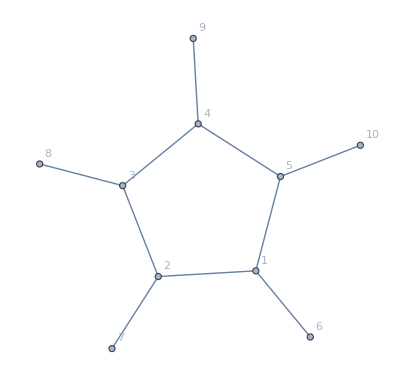

```mathematica
Graph[exp, GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
```

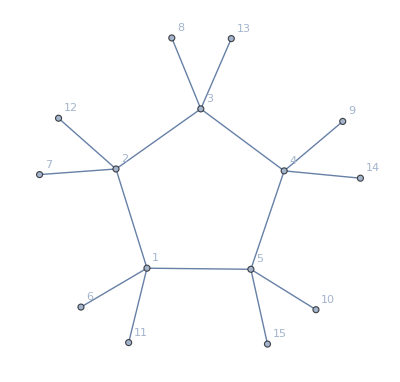

```mathematica
Graph[expDouble, GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
```

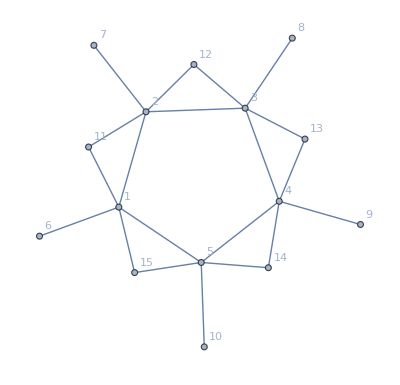

```mathematica
expMixed=Graph[EdgeAdd[CycleGraph[5],Flatten[
Table[{
i<->i+5,
Mod[i,5]+1<->i+10,
i<->i+10
},{i,1,5}]]],GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
```

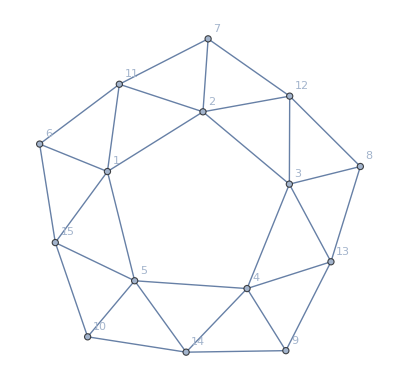

```mathematica
expMixedBis=Graph[EdgeAdd[CycleGraph[5],Flatten[
Table[{
i<->i+5,
Mod[i,5]+1<->i+10,
i+10<->i+5,
i+10<->Mod[i,5]+6,
i<->i+10
},{i,1,5}]]],GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
```

```mathematica
TableForm[
Monitor[
Table[CountSolutions2[expMixed,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,{10863,14697,35145,43452,45369,58788,70290,82431,105435,140580,173808,181476}}],k], TableDepth->2
]
```

10863 | {1,1,1,3,3,3,2,3,4,4} | {0,0,0,0,0,0}
14697 | {1,1,1,4,3,2,2,3,3,2} | {0,0,0,0,1,0}
35145 | {1,1,3,1,3,2,2,1,3,2} | {0,0,0,0,1,0}
43452 | {1,1,3,3,3,2,3,4,4,1} | {0,0,0,1,0,0}
45369 | {1,1,3,4,1,2,1,4,3,2} | {0,0,0,0,0,1}
58788 | {1,1,4,3,2,2,3,3,2,1} | {0,0,0,0,0,1}
70290 | {1,2,1,2,1,3,3,2,1,3} | {0,0,0,1,1,0}
82431 | {1,2,2,1,1,2,4,4,4,4} | {0,0,0,0,0,0}
105435 | {1,2,3,2,3,4,4,2,3,4} | {0,0,0,1,0,0}
140580 | {1,3,1,3,2,2,1,3,2,1} | {0,0,0,0,0,1}
173808 | {1,3,3,3,2,3,4,4,1,1} | {0,0,0,0,0,1}
181476 | {1,3,4,1,2,1,4,3,2,1} | {0,0,0,0,1,0}

```mathematica
TableForm[
Monitor[
Table[CountSolutions2[expMixed,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,1,100}],k], TableDepth->2
]
```

```mathematica
{{1, {1,1,1,1,1,1,1,1,1,2}, {2,2,6,0,0,0}}, {2, {1,1,1,1,1,1,1,1,1,3}, {2,2,6,0,0,0}}, {3, {1,1,1,1,1,1,1,1,1,4}, {2,2,6,0,0,0}}, {4, {1,1,1,1,1,1,1,1,2,1}, {2,2,6,0,0,0}}, {5, {1,1,1,1,1,1,1,1,2,2}, {0,2,2,0,0,0}}, {6, {1,1,1,1,1,1,1,1,2,3}, {1,0,2,0,0,0}}, {7, {1,1,1,1,1,1,1,1,2,4}, {1,0,2,0,0,0}}, {8, {1,1,1,1,1,1,1,1,3,1}, {2,2,6,0,0,0}}, {9, {1,1,1,1,1,1,1,1,3,2}, {1,0,2,0,0,0}}, {10, {1,1,1,1,1,1,1,1,3,3}, {0,2,2,0,0,0}}, {11, {1,1,1,1,1,1,1,1,3,4}, {1,0,2,0,0,0}}, {12, {1,1,1,1,1,1,1,1,4,1}, {2,2,6,0,0,0}}, {13, {1,1,1,1,1,1,1,1,4,2}, {1,0,2,0,0,0}}, {14, {1,1,1,1,1,1,1,1,4,3}, {1,0,2,0,0,0}}, {15, {1,1,1,1,1,1,1,1,4,4}, {0,2,2,0,0,0}}, {16, {1,1,1,1,1,1,1,2,1,1}, {2,2,6,0,0,0}}, {17, {1,1,1,1,1,1,1,2,1,2}, {0,2,0,0,0,0}}, {18, {1,1,1,1,1,1,1,2,1,3}, {1,0,3,0,0,0}}, {19, {1,1,1,1,1,1,1,2,1,4}, {1,0,3,0,0,0}}, {20, {1,1,1,1,1,1,1,2,2,1}, {2,2,0,0,0,0}}, {21, {1,1,1,1,1,1,1,2,2,2}, {0,2,0,0,0,0}}, {22, {1,1,1,1,1,1,1,2,2,3}, {1,0,0,0,0,0}}, {23, {1,1,1,1,1,1,1,2,2,4}, {1,0,0,0,0,0}}, {24, {1,1,1,1,1,1,1,2,3,1}, {0,0,3,0,0,0}}, {25, {1,1,1,1,1,1,1,2,3,2}, {0,0,0,0,0,0}}, {26, {1,1,1,1,1,1,1,2,3,3}, {0,0,1,0,0,0}}, {27, {1,1,1,1,1,1,1,2,3,4}, {0,0,2,0,0,0}}, {28, {1,1,1,1,1,1,1,2,4,1}, {0,0,3,0,0,0}}, {29, {1,1,1,1,1,1,1,2,4,2}, {0,0,0,0,0,0}}, {30, {1,1,1,1,1,1,1,2,4,3}, {0,0,2,0,0,0}}, {31, {1,1,1,1,1,1,1,2,4,4}, {0,0,1,0,0,0}}, {32, {1,1,1,1,1,1,1,3,1,1}, {2,2,6,0,0,0}}, {33, {1,1,1,1,1,1,1,3,1,2}, {1,0,3,0,0,0}}, {34, {1,1,1,1,1,1,1,3,1,3}, {0,2,0,0,0,0}}, {35, {1,1,1,1,1,1,1,3,1,4}, {1,0,3,0,0,0}}, {36, {1,1,1,1,1,1,1,3,2,1}, {0,0,3,0,0,0}}, {37, {1,1,1,1,1,1,1,3,2,2}, {0,0,1,0,0,0}}, {38, {1,1,1,1,1,1,1,3,2,3}, {0,0,0,0,0,0}}, {39, {1,1,1,1,1,1,1,3,2,4}, {0,0,2,0,0,0}}, {40, {1,1,1,1,1,1,1,3,3,1}, {2,2,0,0,0,0}}, {41, {1,1,1,1,1,1,1,3,3,2}, {1,0,0,0,0,0}}, {42, {1,1,1,1,1,1,1,3,3,3}, {0,2,0,0,0,0}}, {43, {1,1,1,1,1,1,1,3,3,4}, {1,0,0,0,0,0}}, {44, {1,1,1,1,1,1,1,3,4,1}, {0,0,3,0,0,0}}, {45, {1,1,1,1,1,1,1,3,4,2}, {0,0,2,0,0,0}}, {46, {1,1,1,1,1,1,1,3,4,3}, {0,0,0,0,0,0}}, {47, {1,1,1,1,1,1,1,3,4,4}, {0,0,1,0,0,0}}, {48, {1,1,1,1,1,1,1,4,1,1}, {2,2,6,0,0,0}}, {49, {1,1,1,1,1,1,1,4,1,2}, {1,0,3,0,0,0}}, {50, {1,1,1,1,1,1,1,4,1,3}, {1,0,3,0,0,0}}, {51, {1,1,1,1,1,1,1,4,1,4}, {0,2,0,0,0,0}}, {52, {1,1,1,1,1,1,1,4,2,1}, {0,0,3,0,0,0}}, {53, {1,1,1,1,1,1,1,4,2,2}, {0,0,1,0,0,0}}, {54, {1,1,1,1,1,1,1,4,2,3}, {0,0,2,0,0,0}}, {55, {1,1,1,1,1,1,1,4,2,4}, {0,0,0,0,0,0}}, {56, {1,1,1,1,1,1,1,4,3,1}, {0,0,3,0,0,0}}, {57, {1,1,1,1,1,1,1,4,3,2}, {0,0,2,0,0,0}}, {58, {1,1,1,1,1,1,1,4,3,3}, {0,0,1,0,0,0}}, {59, {1,1,1,1,1,1,1,4,3,4}, {0,0,0,0,0,0}}, {60, {1,1,1,1,1,1,1,4,4,1}, {2,2,0,0,0,0}}, {61, {1,1,1,1,1,1,1,4,4,2}, {1,0,0,0,0,0}}, {62, {1,1,1,1,1,1,1,4,4,3}, {1,0,0,0,0,0}}, {63, {1,1,1,1,1,1,1,4,4,4}, {0,2,0,0,0,0}}, {64, {1,1,1,1,1,1,2,1,1,1}, {2,2,6,0,0,0}}, {65, {1,1,1,1,1,1,2,1,1,2}, {0,0,2,0,0,0}}, {66, {1,1,1,1,1,1,2,1,1,3}, {1,1,2,0,0,0}}, {67, {1,1,1,1,1,1,2,1,1,4}, {1,1,2,0,0,0}}, {68, {1,1,1,1,1,1,2,1,2,1}, {2,0,0,0,0,0}}, {69, {1,1,1,1,1,1,2,1,2,2}, {0,0,0,0,0,0}}, {70, {1,1,1,1,1,1,2,1,2,3}, {1,0,0,0,0,0}}, {71, {1,1,1,1,1,1,2,1,2,4}, {1,0,0,0,0,0}}, {72, {1,1,1,1,1,1,2,1,3,1}, {0,1,3,0,0,0}}, {73, {1,1,1,1,1,1,2,1,3,2}, {0,0,1,0,0,0}}, {74, {1,1,1,1,1,1,2,1,3,3}, {0,1,1,0,0,0}}, {75, {1,1,1,1,1,1,2,1,3,4}, {0,0,1,0,0,0}}, {76, {1,1,1,1,1,1,2,1,4,1}, {0,1,3,0,0,0}}, {77, {1,1,1,1,1,1,2,1,4,2}, {0,0,1,0,0,0}}, {78, {1,1,1,1,1,1,2,1,4,3}, {0,0,1,0,0,0}}, {79, {1,1,1,1,1,1,2,1,4,4}, {0,1,1,0,0,0}}, {80, {1,1,1,1,1,1,2,2,1,1}, {2,0,2,0,0,0}}, {81, {1,1,1,1,1,1,2,2,1,2}, {0,0,0,0,0,0}}, {82, {1,1,1,1,1,1,2,2,1,3}, {1,0,1,0,0,0}}, {83, {1,1,1,1,1,1,2,2,1,4}, {1,0,1,0,0,0}}, {84, {1,1,1,1,1,1,2,2,2,1}, {2,0,0,0,0,0}}, {85, {1,1,1,1,1,1,2,2,2,2}, {0,0,0,0,0,0}}, {86, {1,1,1,1,1,1,2,2,2,3}, {1,0,0,0,0,0}}, {87, {1,1,1,1,1,1,2,2,2,4}, {1,0,0,0,0,0}}, {88, {1,1,1,1,1,1,2,2,3,1}, {0,0,1,0,0,0}}, {89, {1,1,1,1,1,1,2,2,3,2}, {0,0,0,0,0,0}}, {90, {1,1,1,1,1,1,2,2,3,3}, {0,0,0,0,0,0}}, {91, {1,1,1,1,1,1,2,2,3,4}, {0,0,1,0,0,0}}, {92, {1,1,1,1,1,1,2,2,4,1}, {0,0,1,0,0,0}}, {93, {1,1,1,1,1,1,2,2,4,2}, {0,0,0,0,0,0}}, {94, {1,1,1,1,1,1,2,2,4,3}, {0,0,1,0,0,0}}, {95, {1,1,1,1,1,1,2,2,4,4}, {0,0,0,0,0,0}}, {96, {1,1,1,1,1,1,2,3,1,1}, {0,1,2,0,0,0}}, {97, {1,1,1,1,1,1,2,3,1,2}, {0,0,1,0,0,0}}, {98, {1,1,1,1,1,1,2,3,1,3}, {0,1,0,0,0,0}}, {99, {1,1,1,1,1,1,2,3,1,4}, {0,0,1,0,0,0}}, {100, {1,1,1,1,1,1,2,3,2,1}, {0,0,0,0,0,0}}}
```

{{1,{1,1,1,1,1,1,1,1,1,2},{2,2,6,0,0,0}},{2,{1,1,1,1,1,1,1,1,1,3},{2,2,6,0,0,0}},{3,{1,1,1,1,1,1,1,1,1,4},{2,2,6,0,0,0}},{4,{1,1,1,1,1,1,1,1,2,1},{2,2,6,0,0,0}},{5,{1,1,1,1,1,1,1,1,2,2},{0,2,2,0,0,0}},{6,{1,1,1,1,1,1,1,1,2,3},{1,0,2,0,0,0}},{7,{1,1,1,1,1,1,1,1,2,4},{1,0,2,0,0,0}},{8,{1,1,1,1,1,1,1,1,3,1},{2,2,6,0,0,0}},{9,{1,1,1,1,1,1,1,1,3,2},{1,0,2,0,0,0}},{10,{1,1,1,1,1,1,1,1,3,3},{0,2,2,0,0,0}},{11,{1,1,1,1,1,1,1,1,3,4},{1,0,2,0,0,0}},{12,{1,1,1,1,1,1,1,1,4,1},{2,2,6,0,0,0}},{13,{1,1,1,1,1,1,1,1,4,2},{1,0,2,0,0,0}},{14,{1,1,1,1,1,1,1,1,4,3},{1,0,2,0,0,0}},{15,{1,1,1,1,1,1,1,1,4,4},{0,2,2,0,0,0}},{16,{1,1,1,1,1,1,1,2,1,1},{2,2,6,0,0,0}},{17,{1,1,1,1,1,1,1,2,1,2},{0,2,0,0,0,0}},{18,{1,1,1,1,1,1,1,2,1,3},{1,0,3,0,0,0}},{19,{1,1,1,1,1,1,1,2,1,4},{1,0,3,0,0,0}},{20,{1,1,1,1,1,1,1,2,2,1},{2,2,0,0,0,0}},{21,{1,1,1,1,1,1,1,2,2,2},{0,2,0,0,0,0}},{22,{1,1,1,1,1,1,1,2,2,3},{1,0,0,0,0,0}},{23,{1,1,1,1,1,1,1,2,2,4},{1,0,0,0,0,0}},{24,{1,1,1,1,1,1,1,2,3,1},{0,0,3,0,0,0}},{25,{1,1,1,1,1,1,1,2,3,2},{0,0,0,0,0,0}},{26,{1,1,1,1,1,1,1,2,3,3},{0,0,1,0,0,0}},{27,{1,1,1,1,1,1,1,2,3,4},{0,0,2,0,0,0}},{28,{1,1,1,1,1,1,1,2,4,1},{0,0,3,0,0,0}},{29,{1,1,1,1,1,1,1,2,4,2},{0,0,0,0,0,0}},{30,{1,1,1,1,1,1,1,2,4,3},{0,0,2,0,0,0}},{31,{1,1,1,1,1,1,1,2,4,4},{0,0,1,0,0,0}},{32,{1,1,1,1,1,1,1,3,1,1},{2,2,6,0,0,0}},{33,{1,1,1,1,1,1,1,3,1,2},{1,0,3,0,0,0}},{34,{1,1,1,1,1,1,1,3,1,3},{0,2,0,0,0,0}},{35,{1,1,1,1,1,1,1,3,1,4},{1,0,3,0,0,0}},{36,{1,1,1,1,1,1,1,3,2,1},{0,0,3,0,0,0}},{37,{1,1,1,1,1,1,1,3,2,2},{0,0,1,0,0,0}},{38,{1,1,1,1,1,1,1,3,2,3},{0,0,0,0,0,0}},{39,{1,1,1,1,1,1,1,3,2,4},{0,0,2,0,0,0}},{40,{1,1,1,1,1,1,1,3,3,1},{2,2,0,0,0,0}},{41,{1,1,1,1,1,1,1,3,3,2},{1,0,0,0,0,0}},{42,{1,1,1,1,1,1,1,3,3,3},{0,2,0,0,0,0}},{43,{1,1,1,1,1,1,1,3,3,4},{1,0,0,0,0,0}},{44,{1,1,1,1,1,1,1,3,4,1},{0,0,3,0,0,0}},{45,{1,1,1,1,1,1,1,3,4,2},{0,0,2,0,0,0}},{46,{1,1,1,1,1,1,1,3,4,3},{0,0,0,0,0,0}},{47,{1,1,1,1,1,1,1,3,4,4},{0,0,1,0,0,0}},{48,{1,1,1,1,1,1,1,4,1,1},{2,2,6,0,0,0}},{49,{1,1,1,1,1,1,1,4,1,2},{1,0,3,0,0,0}},{50,{1,1,1,1,1,1,1,4,1,3},{1,0,3,0,0,0}},{51,{1,1,1,1,1,1,1,4,1,4},{0,2,0,0,0,0}},{52,{1,1,1,1,1,1,1,4,2,1},{0,0,3,0,0,0}},{53,{1,1,1,1,1,1,1,4,2,2},{0,0,1,0,0,0}},{54,{1,1,1,1,1,1,1,4,2,3},{0,0,2,0,0,0}},{55,{1,1,1,1,1,1,1,4,2,4},{0,0,0,0,0,0}},{56,{1,1,1,1,1,1,1,4,3,1},{0,0,3,0,0,0}},{57,{1,1,1,1,1,1,1,4,3,2},{0,0,2,0,0,0}},{58,{1,1,1,1,1,1,1,4,3,3},{0,0,1,0,0,0}},{59,{1,1,1,1,1,1,1,4,3,4},{0,0,0,0,0,0}},{60,{1,1,1,1,1,1,1,4,4,1},{2,2,0,0,0,0}},{61,{1,1,1,1,1,1,1,4,4,2},{1,0,0,0,0,0}},{62,{1,1,1,1,1,1,1,4,4,3},{1,0,0,0,0,0}},{63,{1,1,1,1,1,1,1,4,4,4},{0,2,0,0,0,0}},{64,{1,1,1,1,1,1,2,1,1,1},{2,2,6,0,0,0}},{65,{1,1,1,1,1,1,2,1,1,2},{0,0,2,0,0,0}},{66,{1,1,1,1,1,1,2,1,1,3},{1,1,2,0,0,0}},{67,{1,1,1,1,1,1,2,1,1,4},{1,1,2,0,0,0}},{68,{1,1,1,1,1,1,2,1,2,1},{2,0,0,0,0,0}},{69,{1,1,1,1,1,1,2,1,2,2},{0,0,0,0,0,0}},{70,{1,1,1,1,1,1,2,1,2,3},{1,0,0,0,0,0}},{71,{1,1,1,1,1,1,2,1,2,4},{1,0,0,0,0,0}},{72,{1,1,1,1,1,1,2,1,3,1},{0,1,3,0,0,0}},{73,{1,1,1,1,1,1,2,1,3,2},{0,0,1,0,0,0}},{74,{1,1,1,1,1,1,2,1,3,3},{0,1,1,0,0,0}},{75,{1,1,1,1,1,1,2,1,3,4},{0,0,1,0,0,0}},{76,{1,1,1,1,1,1,2,1,4,1},{0,1,3,0,0,0}},{77,{1,1,1,1,1,1,2,1,4,2},{0,0,1,0,0,0}},{78,{1,1,1,1,1,1,2,1,4,3},{0,0,1,0,0,0}},{79,{1,1,1,1,1,1,2,1,4,4},{0,1,1,0,0,0}},{80,{1,1,1,1,1,1,2,2,1,1},{2,0,2,0,0,0}},{81,{1,1,1,1,1,1,2,2,1,2},{0,0,0,0,0,0}},{82,{1,1,1,1,1,1,2,2,1,3},{1,0,1,0,0,0}},{83,{1,1,1,1,1,1,2,2,1,4},{1,0,1,0,0,0}},{84,{1,1,1,1,1,1,2,2,2,1},{2,0,0,0,0,0}},{85,{1,1,1,1,1,1,2,2,2,2},{0,0,0,0,0,0}},{86,{1,1,1,1,1,1,2,2,2,3},{1,0,0,0,0,0}},{87,{1,1,1,1,1,1,2,2,2,4},{1,0,0,0,0,0}},{88,{1,1,1,1,1,1,2,2,3,1},{0,0,1,0,0,0}},{89,{1,1,1,1,1,1,2,2,3,2},{0,0,0,0,0,0}},{90,{1,1,1,1,1,1,2,2,3,3},{0,0,0,0,0,0}},{91,{1,1,1,1,1,1,2,2,3,4},{0,0,1,0,0,0}},{92,{1,1,1,1,1,1,2,2,4,1},{0,0,1,0,0,0}},{93,{1,1,1,1,1,1,2,2,4,2},{0,0,0,0,0,0}},{94,{1,1,1,1,1,1,2,2,4,3},{0,0,1,0,0,0}},{95,{1,1,1,1,1,1,2,2,4,4},{0,0,0,0,0,0}},{96,{1,1,1,1,1,1,2,3,1,1},{0,1,2,0,0,0}},{97,{1,1,1,1,1,1,2,3,1,2},{0,0,1,0,0,0}},{98,{1,1,1,1,1,1,2,3,1,3},{0,1,0,0,0,0}},{99,{1,1,1,1,1,1,2,3,1,4},{0,0,1,0,0,0}},{100,{1,1,1,1,1,1,2,3,2,1},{0,0,0,0,0,0}}}

```mathematica
TableForm[
Monitor[
Table[CountSolutions[expMixedBis,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,1,1024}],k], TableDepth->2
]
```

1 | {1,1,1,1,2} | {0,2,12,0,22,10}
2 | {1,1,1,1,3} | {0,2,12,0,22,10}
3 | {1,1,1,1,4} | {0,2,12,0,22,10}
4 | {1,1,1,2,1} | {2,2,10,12,10,10}
5 | {1,1,1,2,2} | {0,0,12,2,10,4}
6 | {1,1,1,2,3} | {1,2,3,2,4,2}
7 | {1,1,1,2,4} | {1,2,3,2,4,2}
8 | {1,1,1,3,1} | {2,2,10,12,10,10}
9 | {1,1,1,3,2} | {1,2,3,2,4,2}
10 | {1,1,1,3,3} | {0,0,12,2,10,4}
11 | {1,1,1,3,4} | {1,2,3,2,4,2}
12 | {1,1,1,4,1} | {2,2,10,12,10,10}
13 | {1,1,1,4,2} | {1,2,3,2,4,2}
14 | {1,1,1,4,3} | {1,2,3,2,4,2}
15 | {1,1,1,4,4} | {0,0,12,2,10,4}
16 | {1,1,2,1,1} | {2,0,12,0,10,22}
17 | {1,1,2,1,2} | {22,22,8,16,4,4}
18 | {1,1,2,1,3} | {19,19,6,17,3,3}
19 | {1,1,2,1,4} | {19,19,6,17,3,3}
20 | {1,1,2,2,1} | {0,0,12,2,4,10}
21 | {1,1,2,2,2} | {6,6,0,8,4,4}
22 | {1,1,2,2,3} | {2,7,9,3,7,4}
23 | {1,1,2,2,4} | {2,7,9,3,7,4}
24 | {1,1,2,3,1} | {2,1,3,2,2,4}
25 | {1,1,2,3,2} | {4,4,6,2,3,3}
26 | {1,1,2,3,3} | {7,2,9,3,4,7}
27 | {1,1,2,3,4} | {2,2,2,1,3,3}
28 | {1,1,2,4,1} | {2,1,3,2,2,4}
29 | {1,1,2,4,2} | {4,4,6,2,3,3}
30 | {1,1,2,4,3} | {2,2,2,1,3,3}
31 | {1,1,2,4,4} | {7,2,9,3,4,7}
32 | {1,1,3,1,1} | {2,0,12,0,10,22}
33 | {1,1,3,1,2} | {19,19,6,17,3,3}
34 | {1,1,3,1,3} | {22,22,8,16,4,4}
35 | {1,1,3,1,4} | {19,19,6,17,3,3}
36 | {1,1,3,2,1} | {2,1,3,2,2,4}
37 | {1,1,3,2,2} | {7,2,9,3,4,7}
38 | {1,1,3,2,3} | {4,4,6,2,3,3}
39 | {1,1,3,2,4} | {2,2,2,1,3,3}
40 | {1,1,3,3,1} | {0,0,12,2,4,10}
41 | {1,1,3,3,2} | {2,7,9,3,7,4}
42 | {1,1,3,3,3} | {6,6,0,8,4,4}
43 | {1,1,3,3,4} | {2,7,9,3,7,4}
44 | {1,1,3,4,1} | {2,1,3,2,2,4}
45 | {1,1,3,4,2} | {2,2,2,1,3,3}
46 | {1,1,3,4,3} | {4,4,6,2,3,3}
47 | {1,1,3,4,4} | {7,2,9,3,4,7}
48 | {1,1,4,1,1} | {2,0,12,0,10,22}
49 | {1,1,4,1,2} | {19,19,6,17,3,3}
50 | {1,1,4,1,3} | {19,19,6,17,3,3}
51 | {1,1,4,1,4} | {22,22,8,16,4,4}
52 | {1,1,4,2,1} | {2,1,3,2,2,4}
53 | {1,1,4,2,2} | {7,2,9,3,4,7}
54 | {1,1,4,2,3} | {2,2,2,1,3,3}
55 | {1,1,4,2,4} | {4,4,6,2,3,3}
56 | {1,1,4,3,1} | {2,1,3,2,2,4}
57 | {1,1,4,3,2} | {2,2,2,1,3,3}
58 | {1,1,4,3,3} | {7,2,9,3,4,7}
59 | {1,1,4,3,4} | {4,4,6,2,3,3}
60 | {1,1,4,4,1} | {0,0,12,2,4,10}
61 | {1,1,4,4,2} | {2,7,9,3,7,4}
62 | {1,1,4,4,3} | {2,7,9,3,7,4}
63 | {1,1,4,4,4} | {6,6,0,8,4,4}
64 | {1,2,1,1,1} | {0,10,4,10,22,0}
65 | {1,2,1,1,2} | {0,4,48,0,8,16}
66 | {1,2,1,1,3} | {0,3,41,0,6,17}
67 | {1,2,1,1,4} | {0,3,41,0,6,17}
68 | {1,2,1,2,1} | {22,4,26,4,4,16}
69 | {1,2,1,2,2} | {4,0,48,0,16,8}
70 | {1,2,1,2,3} | {4,4,10,2,3,3}
71 | {1,2,1,2,4} | {4,4,10,2,3,3}
72 | {1,2,1,3,1} | {19,3,22,3,3,17}
73 | {1,2,1,3,2} | {4,4,10,2,3,3}
74 | {1,2,1,3,3} | {3,0,11,0,2,6}
75 | {1,2,1,3,4} | {2,2,4,1,1,4}
76 | {1,2,1,4,1} | {19,3,22,3,3,17}
77 | {1,2,1,4,2} | {4,4,10,2,3,3}
78 | {1,2,1,4,3} | {2,2,4,1,1,4}
79 | {1,2,1,4,4} | {3,0,11,0,2,6}
80 | {1,2,2,1,1} | {0,6,6,2,10,4}
81 | {1,2,2,1,2} | {4,22,26,4,16,4}
82 | {1,2,2,1,3} | {3,4,7,3,2,3}
83 | {1,2,2,1,4} | {3,4,7,3,2,3}
84 | {1,2,2,2,1} | {6,0,6,2,4,10}
85 | {1,2,2,2,2} | {10,0,4,10,0,22}
86 | {1,2,2,2,3} | {1,1,4,1,3,4}
87 | {1,2,2,2,4} | {1,1,4,1,3,4}
88 | {1,2,2,3,1} | {7,7,4,6,4,4}
89 | {1,2,2,3,2} | {3,19,22,3,17,3}
90 | {1,2,2,3,3} | {0,2,16,1,6,7}
91 | {1,2,2,3,4} | {1,2,3,2,2,3}
92 | {1,2,2,4,1} | {7,7,4,6,4,4}
93 | {1,2,2,4,2} | {3,19,22,3,17,3}
94 | {1,2,2,4,3} | {1,2,3,2,2,3}
95 | {1,2,2,4,4} | {0,2,16,1,6,7}
96 | {1,2,3,1,1} | {1,1,4,1,4,3}
97 | {1,2,3,1,2} | {4,4,10,2,3,3}
98 | {1,2,3,1,3} | {4,2,12,1,3,4}
99 | {1,2,3,1,4} | {2,1,5,2,1,3}
100 | {1,2,3,2,1} | {4,3,7,3,3,2}
101 | {1,2,3,2,2} | {3,0,41,0,17,6}
102 | {1,2,3,2,3} | {2,4,12,1,4,3}
103 | {1,2,3,2,4} | {1,2,5,2,3,1}
104 | {1,2,3,3,1} | {2,0,16,1,7,6}
105 | {1,2,3,3,2} | {0,3,11,0,6,2}
106 | {1,2,3,3,3} | {1,1,4,2,3,3}
107 | {1,2,3,3,4} | {0,1,5,1,4,2}
108 | {1,2,3,4,1} | {2,1,3,2,3,2}
109 | {1,2,3,4,2} | {2,2,4,1,4,1}
110 | {1,2,3,4,3} | {1,1,6,0,3,3}
111 | {1,2,3,4,4} | {1,0,5,1,2,4}
112 | {1,2,4,1,1} | {1,1,4,1,4,3}
113 | {1,2,4,1,2} | {4,4,10,2,3,3}
114 | {1,2,4,1,3} | {2,1,5,2,1,3}
115 | {1,2,4,1,4} | {4,2,12,1,3,4}
116 | {1,2,4,2,1} | {4,3,7,3,3,2}
117 | {1,2,4,2,2} | {3,0,41,0,17,6}
118 | {1,2,4,2,3} | {1,2,5,2,3,1}
119 | {1,2,4,2,4} | {2,4,12,1,4,3}
120 | {1,2,4,3,1} | {2,1,3,2,3,2}
121 | {1,2,4,3,2} | {2,2,4,1,4,1}
122 | {1,2,4,3,3} | {1,0,5,1,2,4}
123 | {1,2,4,3,4} | {1,1,6,0,3,3}
124 | {1,2,4,4,1} | {2,0,16,1,7,6}
125 | {1,2,4,4,2} | {0,3,11,0,6,2}
126 | {1,2,4,4,3} | {0,1,5,1,4,2}
127 | {1,2,4,4,4} | {1,1,4,2,3,3}
128 | {1,3,1,1,1} | {0,10,4,10,22,0}
129 | {1,3,1,1,2} | {0,3,41,0,6,17}
130 | {1,3,1,1,3} | {0,4,48,0,8,16}
131 | {1,3,1,1,4} | {0,3,41,0,6,17}
132 | {1,3,1,2,1} | {19,3,22,3,3,17}
133 | {1,3,1,2,2} | {3,0,11,0,2,6}
134 | {1,3,1,2,3} | {4,4,10,2,3,3}
135 | {1,3,1,2,4} | {2,2,4,1,1,4}
136 | {1,3,1,3,1} | {22,4,26,4,4,16}
137 | {1,3,1,3,2} | {4,4,10,2,3,3}
138 | {1,3,1,3,3} | {4,0,48,0,16,8}
139 | {1,3,1,3,4} | {4,4,10,2,3,3}
140 | {1,3,1,4,1} | {19,3,22,3,3,17}
141 | {1,3,1,4,2} | {2,2,4,1,1,4}
142 | {1,3,1,4,3} | {4,4,10,2,3,3}
143 | {1,3,1,4,4} | {3,0,11,0,2,6}
144 | {1,3,2,1,1} | {1,1,4,1,4,3}
145 | {1,3,2,1,2} | {4,2,12,1,3,4}
146 | {1,3,2,1,3} | {4,4,10,2,3,3}
147 | {1,3,2,1,4} | {2,1,5,2,1,3}
148 | {1,3,2,2,1} | {2,0,16,1,7,6}
149 | {1,3,2,2,2} | {1,1,4,2,3,3}
150 | {1,3,2,2,3} | {0,3,11,0,6,2}
151 | {1,3,2,2,4} | {0,1,5,1,4,2}
152 | {1,3,2,3,1} | {4,3,7,3,3,2}
153 | {1,3,2,3,2} | {2,4,12,1,4,3}
154 | {1,3,2,3,3} | {3,0,41,0,17,6}
155 | {1,3,2,3,4} | {1,2,5,2,3,1}
156 | {1,3,2,4,1} | {2,1,3,2,3,2}
157 | {1,3,2,4,2} | {1,1,6,0,3,3}
158 | {1,3,2,4,3} | {2,2,4,1,4,1}
159 | {1,3,2,4,4} | {1,0,5,1,2,4}
160 | {1,3,3,1,1} | {0,6,6,2,10,4}
161 | {1,3,3,1,2} | {3,4,7,3,2,3}
162 | {1,3,3,1,3} | {4,22,26,4,16,4}
163 | {1,3,3,1,4} | {3,4,7,3,2,3}
164 | {1,3,3,2,1} | {7,7,4,6,4,4}
165 | {1,3,3,2,2} | {0,2,16,1,6,7}
166 | {1,3,3,2,3} | {3,19,22,3,17,3}
167 | {1,3,3,2,4} | {1,2,3,2,2,3}
168 | {1,3,3,3,1} | {6,0,6,2,4,10}
169 | {1,3,3,3,2} | {1,1,4,1,3,4}
170 | {1,3,3,3,3} | {10,0,4,10,0,22}
171 | {1,3,3,3,4} | {1,1,4,1,3,4}
172 | {1,3,3,4,1} | {7,7,4,6,4,4}
173 | {1,3,3,4,2} | {1,2,3,2,2,3}
174 | {1,3,3,4,3} | {3,19,22,3,17,3}
175 | {1,3,3,4,4} | {0,2,16,1,6,7}
176 | {1,3,4,1,1} | {1,1,4,1,4,3}
177 | {1,3,4,1,2} | {2,1,5,2,1,3}
178 | {1,3,4,1,3} | {4,4,10,2,3,3}
179 | {1,3,4,1,4} | {4,2,12,1,3,4}
180 | {1,3,4,2,1} | {2,1,3,2,3,2}
181 | {1,3,4,2,2} | {1,0,5,1,2,4}
182 | {1,3,4,2,3} | {2,2,4,1,4,1}
183 | {1,3,4,2,4} | {1,1,6,0,3,3}
184 | {1,3,4,3,1} | {4,3,7,3,3,2}
185 | {1,3,4,3,2} | {1,2,5,2,3,1}
186 | {1,3,4,3,3} | {3,0,41,0,17,6}
187 | {1,3,4,3,4} | {2,4,12,1,4,3}
188 | {1,3,4,4,1} | {2,0,16,1,7,6}
189 | {1,3,4,4,2} | {0,1,5,1,4,2}
190 | {1,3,4,4,3} | {0,3,11,0,6,2}
191 | {1,3,4,4,4} | {1,1,4,2,3,3}
192 | {1,4,1,1,1} | {0,10,4,10,22,0}
193 | {1,4,1,1,2} | {0,3,41,0,6,17}
194 | {1,4,1,1,3} | {0,3,41,0,6,17}
195 | {1,4,1,1,4} | {0,4,48,0,8,16}
196 | {1,4,1,2,1} | {19,3,22,3,3,17}
197 | {1,4,1,2,2} | {3,0,11,0,2,6}
198 | {1,4,1,2,3} | {2,2,4,1,1,4}
199 | {1,4,1,2,4} | {4,4,10,2,3,3}
200 | {1,4,1,3,1} | {19,3,22,3,3,17}
201 | {1,4,1,3,2} | {2,2,4,1,1,4}
202 | {1,4,1,3,3} | {3,0,11,0,2,6}
203 | {1,4,1,3,4} | {4,4,10,2,3,3}
204 | {1,4,1,4,1} | {22,4,26,4,4,16}
205 | {1,4,1,4,2} | {4,4,10,2,3,3}
206 | {1,4,1,4,3} | {4,4,10,2,3,3}
207 | {1,4,1,4,4} | {4,0,48,0,16,8}
208 | {1,4,2,1,1} | {1,1,4,1,4,3}
209 | {1,4,2,1,2} | {4,2,12,1,3,4}
210 | {1,4,2,1,3} | {2,1,5,2,1,3}
211 | {1,4,2,1,4} | {4,4,10,2,3,3}
212 | {1,4,2,2,1} | {2,0,16,1,7,6}
213 | {1,4,2,2,2} | {1,1,4,2,3,3}
214 | {1,4,2,2,3} | {0,1,5,1,4,2}
215 | {1,4,2,2,4} | {0,3,11,0,6,2}
216 | {1,4,2,3,1} | {2,1,3,2,3,2}
217 | {1,4,2,3,2} | {1,1,6,0,3,3}
218 | {1,4,2,3,3} | {1,0,5,1,2,4}
219 | {1,4,2,3,4} | {2,2,4,1,4,1}
220 | {1,4,2,4,1} | {4,3,7,3,3,2}
221 | {1,4,2,4,2} | {2,4,12,1,4,3}
222 | {1,4,2,4,3} | {1,2,5,2,3,1}
223 | {1,4,2,4,4} | {3,0,41,0,17,6}
224 | {1,4,3,1,1} | {1,1,4,1,4,3}
225 | {1,4,3,1,2} | {2,1,5,2,1,3}
226 | {1,4,3,1,3} | {4,2,12,1,3,4}
227 | {1,4,3,1,4} | {4,4,10,2,3,3}
228 | {1,4,3,2,1} | {2,1,3,2,3,2}
229 | {1,4,3,2,2} | {1,0,5,1,2,4}
230 | {1,4,3,2,3} | {1,1,6,0,3,3}
231 | {1,4,3,2,4} | {2,2,4,1,4,1}
232 | {1,4,3,3,1} | {2,0,16,1,7,6}
233 | {1,4,3,3,2} | {0,1,5,1,4,2}
234 | {1,4,3,3,3} | {1,1,4,2,3,3}
235 | {1,4,3,3,4} | {0,3,11,0,6,2}
236 | {1,4,3,4,1} | {4,3,7,3,3,2}
237 | {1,4,3,4,2} | {1,2,5,2,3,1}
238 | {1,4,3,4,3} | {2,4,12,1,4,3}
239 | {1,4,3,4,4} | {3,0,41,0,17,6}
240 | {1,4,4,1,1} | {0,6,6,2,10,4}
241 | {1,4,4,1,2} | {3,4,7,3,2,3}
242 | {1,4,4,1,3} | {3,4,7,3,2,3}
243 | {1,4,4,1,4} | {4,22,26,4,16,4}
244 | {1,4,4,2,1} | {7,7,4,6,4,4}
245 | {1,4,4,2,2} | {0,2,16,1,6,7}
246 | {1,4,4,2,3} | {1,2,3,2,2,3}
247 | {1,4,4,2,4} | {3,19,22,3,17,3}
248 | {1,4,4,3,1} | {7,7,4,6,4,4}
249 | {1,4,4,3,2} | {1,2,3,2,2,3}
250 | {1,4,4,3,3} | {0,2,16,1,6,7}
251 | {1,4,4,3,4} | {3,19,22,3,17,3}
252 | {1,4,4,4,1} | {6,0,6,2,4,10}
253 | {1,4,4,4,2} | {1,1,4,1,3,4}
254 | {1,4,4,4,3} | {1,1,4,1,3,4}
255 | {1,4,4,4,4} | {10,0,4,10,0,22}
256 | {2,1,1,1,1} | {10,0,4,10,0,22}
257 | {2,1,1,1,2} | {6,0,6,2,4,10}
258 | {2,1,1,1,3} | {1,1,4,1,3,4}
259 | {2,1,1,1,4} | {1,1,4,1,3,4}
260 | {2,1,1,2,1} | {4,22,26,4,16,4}
261 | {2,1,1,2,2} | {0,6,6,2,10,4}
262 | {2,1,1,2,3} | {3,4,7,3,2,3}
263 | {2,1,1,2,4} | {3,4,7,3,2,3}
264 | {2,1,1,3,1} | {3,19,22,3,17,3}
265 | {2,1,1,3,2} | {7,7,4,6,4,4}
266 | {2,1,1,3,3} | {0,2,16,1,6,7}
267 | {2,1,1,3,4} | {1,2,3,2,2,3}
268 | {2,1,1,4,1} | {3,19,22,3,17,3}
269 | {2,1,1,4,2} | {7,7,4,6,4,4}
270 | {2,1,1,4,3} | {1,2,3,2,2,3}
271 | {2,1,1,4,4} | {0,2,16,1,6,7}
272 | {2,1,2,1,1} | {4,0,48,0,16,8}
273 | {2,1,2,1,2} | {22,4,26,4,4,16}
274 | {2,1,2,1,3} | {4,4,10,2,3,3}
275 | {2,1,2,1,4} | {4,4,10,2,3,3}
276 | {2,1,2,2,1} | {0,4,48,0,8,16}
277 | {2,1,2,2,2} | {0,10,4,10,22,0}
278 | {2,1,2,2,3} | {0,3,41,0,6,17}
279 | {2,1,2,2,4} | {0,3,41,0,6,17}
280 | {2,1,2,3,1} | {4,4,10,2,3,3}
281 | {2,1,2,3,2} | {19,3,22,3,3,17}
282 | {2,1,2,3,3} | {3,0,11,0,2,6}
283 | {2,1,2,3,4} | {2,2,4,1,1,4}
284 | {2,1,2,4,1} | {4,4,10,2,3,3}
285 | {2,1,2,4,2} | {19,3,22,3,3,17}
286 | {2,1,2,4,3} | {2,2,4,1,1,4}
287 | {2,1,2,4,4} | {3,0,11,0,2,6}
288 | {2,1,3,1,1} | {3,0,41,0,17,6}
289 | {2,1,3,1,2} | {4,3,7,3,3,2}
290 | {2,1,3,1,3} | {2,4,12,1,4,3}
291 | {2,1,3,1,4} | {1,2,5,2,3,1}
292 | {2,1,3,2,1} | {4,4,10,2,3,3}
293 | {2,1,3,2,2} | {1,1,4,1,4,3}
294 | {2,1,3,2,3} | {4,2,12,1,3,4}
295 | {2,1,3,2,4} | {2,1,5,2,1,3}
296 | {2,1,3,3,1} | {0,3,11,0,6,2}
297 | {2,1,3,3,2} | {2,0,16,1,7,6}
298 | {2,1,3,3,3} | {1,1,4,2,3,3}
299 | {2,1,3,3,4} | {0,1,5,1,4,2}
300 | {2,1,3,4,1} | {2,2,4,1,4,1}
301 | {2,1,3,4,2} | {2,1,3,2,3,2}
302 | {2,1,3,4,3} | {1,1,6,0,3,3}
303 | {2,1,3,4,4} | {1,0,5,1,2,4}
304 | {2,1,4,1,1} | {3,0,41,0,17,6}
305 | {2,1,4,1,2} | {4,3,7,3,3,2}
306 | {2,1,4,1,3} | {1,2,5,2,3,1}
307 | {2,1,4,1,4} | {2,4,12,1,4,3}
308 | {2,1,4,2,1} | {4,4,10,2,3,3}
309 | {2,1,4,2,2} | {1,1,4,1,4,3}
310 | {2,1,4,2,3} | {2,1,5,2,1,3}
311 | {2,1,4,2,4} | {4,2,12,1,3,4}
312 | {2,1,4,3,1} | {2,2,4,1,4,1}
313 | {2,1,4,3,2} | {2,1,3,2,3,2}
314 | {2,1,4,3,3} | {1,0,5,1,2,4}
315 | {2,1,4,3,4} | {1,1,6,0,3,3}
316 | {2,1,4,4,1} | {0,3,11,0,6,2}
317 | {2,1,4,4,2} | {2,0,16,1,7,6}
318 | {2,1,4,4,3} | {0,1,5,1,4,2}
319 | {2,1,4,4,4} | {1,1,4,2,3,3}
320 | {2,2,1,1,1} | {6,6,0,8,4,4}
321 | {2,2,1,1,2} | {0,0,12,2,4,10}
322 | {2,2,1,1,3} | {2,7,9,3,7,4}
323 | {2,2,1,1,4} | {2,7,9,3,7,4}
324 | {2,2,1,2,1} | {22,22,8,16,4,4}
325 | {2,2,1,2,2} | {2,0,12,0,10,22}
326 | {2,2,1,2,3} | {19,19,6,17,3,3}
327 | {2,2,1,2,4} | {19,19,6,17,3,3}
328 | {2,2,1,3,1} | {4,4,6,2,3,3}
329 | {2,2,1,3,2} | {2,1,3,2,2,4}
330 | {2,2,1,3,3} | {7,2,9,3,4,7}
331 | {2,2,1,3,4} | {2,2,2,1,3,3}
332 | {2,2,1,4,1} | {4,4,6,2,3,3}
333 | {2,2,1,4,2} | {2,1,3,2,2,4}
334 | {2,2,1,4,3} | {2,2,2,1,3,3}
335 | {2,2,1,4,4} | {7,2,9,3,4,7}
336 | {2,2,2,1,1} | {0,0,12,2,10,4}
337 | {2,2,2,1,2} | {2,2,10,12,10,10}
338 | {2,2,2,1,3} | {1,2,3,2,4,2}
339 | {2,2,2,1,4} | {1,2,3,2,4,2}
340 | {2,2,2,2,1} | {0,2,12,0,22,10}
341 | {2,2,2,2,2} | {6,6,18,0,0,0}
342 | {2,2,2,2,3} | {0,2,12,0,22,10}
343 | {2,2,2,2,4} | {0,2,12,0,22,10}
344 | {2,2,2,3,1} | {1,2,3,2,4,2}
345 | {2,2,2,3,2} | {2,2,10,12,10,10}
346 | {2,2,2,3,3} | {0,0,12,2,10,4}
347 | {2,2,2,3,4} | {1,2,3,2,4,2}
348 | {2,2,2,4,1} | {1,2,3,2,4,2}
349 | {2,2,2,4,2} | {2,2,10,12,10,10}
350 | {2,2,2,4,3} | {1,2,3,2,4,2}
351 | {2,2,2,4,4} | {0,0,12,2,10,4}
352 | {2,2,3,1,1} | {7,2,9,3,4,7}
353 | {2,2,3,1,2} | {2,1,3,2,2,4}
354 | {2,2,3,1,3} | {4,4,6,2,3,3}
355 | {2,2,3,1,4} | {2,2,2,1,3,3}
356 | {2,2,3,2,1} | {19,19,6,17,3,3}
357 | {2,2,3,2,2} | {2,0,12,0,10,22}
358 | {2,2,3,2,3} | {22,22,8,16,4,4}
359 | {2,2,3,2,4} | {19,19,6,17,3,3}
360 | {2,2,3,3,1} | {2,7,9,3,7,4}
361 | {2,2,3,3,2} | {0,0,12,2,4,10}
362 | {2,2,3,3,3} | {6,6,0,8,4,4}
363 | {2,2,3,3,4} | {2,7,9,3,7,4}
364 | {2,2,3,4,1} | {2,2,2,1,3,3}
365 | {2,2,3,4,2} | {2,1,3,2,2,4}
366 | {2,2,3,4,3} | {4,4,6,2,3,3}
367 | {2,2,3,4,4} | {7,2,9,3,4,7}
368 | {2,2,4,1,1} | {7,2,9,3,4,7}
369 | {2,2,4,1,2} | {2,1,3,2,2,4}
370 | {2,2,4,1,3} | {2,2,2,1,3,3}
371 | {2,2,4,1,4} | {4,4,6,2,3,3}
372 | {2,2,4,2,1} | {19,19,6,17,3,3}
373 | {2,2,4,2,2} | {2,0,12,0,10,22}
374 | {2,2,4,2,3} | {19,19,6,17,3,3}
375 | {2,2,4,2,4} | {22,22,8,16,4,4}
376 | {2,2,4,3,1} | {2,2,2,1,3,3}
377 | {2,2,4,3,2} | {2,1,3,2,2,4}
378 | {2,2,4,3,3} | {7,2,9,3,4,7}
379 | {2,2,4,3,4} | {4,4,6,2,3,3}
380 | {2,2,4,4,1} | {2,7,9,3,7,4}
381 | {2,2,4,4,2} | {0,0,12,2,4,10}
382 | {2,2,4,4,3} | {2,7,9,3,7,4}
383 | {2,2,4,4,4} | {6,6,0,8,4,4}
384 | {2,3,1,1,1} | {1,1,4,2,3,3}
385 | {2,3,1,1,2} | {2,0,16,1,7,6}
386 | {2,3,1,1,3} | {0,3,11,0,6,2}
387 | {2,3,1,1,4} | {0,1,5,1,4,2}
388 | {2,3,1,2,1} | {4,2,12,1,3,4}
389 | {2,3,1,2,2} | {1,1,4,1,4,3}
390 | {2,3,1,2,3} | {4,4,10,2,3,3}
391 | {2,3,1,2,4} | {2,1,5,2,1,3}
392 | {2,3,1,3,1} | {2,4,12,1,4,3}
393 | {2,3,1,3,2} | {4,3,7,3,3,2}
394 | {2,3,1,3,3} | {3,0,41,0,17,6}
395 | {2,3,1,3,4} | {1,2,5,2,3,1}
396 | {2,3,1,4,1} | {1,1,6,0,3,3}
397 | {2,3,1,4,2} | {2,1,3,2,3,2}
398 | {2,3,1,4,3} | {2,2,4,1,4,1}
399 | {2,3,1,4,4} | {1,0,5,1,2,4}
400 | {2,3,2,1,1} | {3,0,11,0,2,6}
401 | {2,3,2,1,2} | {19,3,22,3,3,17}
402 | {2,3,2,1,3} | {4,4,10,2,3,3}
403 | {2,3,2,1,4} | {2,2,4,1,1,4}
404 | {2,3,2,2,1} | {0,3,41,0,6,17}
405 | {2,3,2,2,2} | {0,10,4,10,22,0}
406 | {2,3,2,2,3} | {0,4,48,0,8,16}
407 | {2,3,2,2,4} | {0,3,41,0,6,17}
408 | {2,3,2,3,1} | {4,4,10,2,3,3}
409 | {2,3,2,3,2} | {22,4,26,4,4,16}
410 | {2,3,2,3,3} | {4,0,48,0,16,8}
411 | {2,3,2,3,4} | {4,4,10,2,3,3}
412 | {2,3,2,4,1} | {2,2,4,1,1,4}
413 | {2,3,2,4,2} | {19,3,22,3,3,17}
414 | {2,3,2,4,3} | {4,4,10,2,3,3}
415 | {2,3,2,4,4} | {3,0,11,0,2,6}
416 | {2,3,3,1,1} | {0,2,16,1,6,7}
417 | {2,3,3,1,2} | {7,7,4,6,4,4}
418 | {2,3,3,1,3} | {3,19,22,3,17,3}
419 | {2,3,3,1,4} | {1,2,3,2,2,3}
420 | {2,3,3,2,1} | {3,4,7,3,2,3}
421 | {2,3,3,2,2} | {0,6,6,2,10,4}
422 | {2,3,3,2,3} | {4,22,26,4,16,4}
423 | {2,3,3,2,4} | {3,4,7,3,2,3}
424 | {2,3,3,3,1} | {1,1,4,1,3,4}
425 | {2,3,3,3,2} | {6,0,6,2,4,10}
426 | {2,3,3,3,3} | {10,0,4,10,0,22}
427 | {2,3,3,3,4} | {1,1,4,1,3,4}
428 | {2,3,3,4,1} | {1,2,3,2,2,3}
429 | {2,3,3,4,2} | {7,7,4,6,4,4}
430 | {2,3,3,4,3} | {3,19,22,3,17,3}
431 | {2,3,3,4,4} | {0,2,16,1,6,7}
432 | {2,3,4,1,1} | {1,0,5,1,2,4}
433 | {2,3,4,1,2} | {2,1,3,2,3,2}
434 | {2,3,4,1,3} | {2,2,4,1,4,1}
435 | {2,3,4,1,4} | {1,1,6,0,3,3}
436 | {2,3,4,2,1} | {2,1,5,2,1,3}
437 | {2,3,4,2,2} | {1,1,4,1,4,3}
438 | {2,3,4,2,3} | {4,4,10,2,3,3}
439 | {2,3,4,2,4} | {4,2,12,1,3,4}
440 | {2,3,4,3,1} | {1,2,5,2,3,1}
441 | {2,3,4,3,2} | {4,3,7,3,3,2}
442 | {2,3,4,3,3} | {3,0,41,0,17,6}
443 | {2,3,4,3,4} | {2,4,12,1,4,3}
444 | {2,3,4,4,1} | {0,1,5,1,4,2}
445 | {2,3,4,4,2} | {2,0,16,1,7,6}
446 | {2,3,4,4,3} | {0,3,11,0,6,2}
447 | {2,3,4,4,4} | {1,1,4,2,3,3}
448 | {2,4,1,1,1} | {1,1,4,2,3,3}
449 | {2,4,1,1,2} | {2,0,16,1,7,6}
450 | {2,4,1,1,3} | {0,1,5,1,4,2}
451 | {2,4,1,1,4} | {0,3,11,0,6,2}
452 | {2,4,1,2,1} | {4,2,12,1,3,4}
453 | {2,4,1,2,2} | {1,1,4,1,4,3}
454 | {2,4,1,2,3} | {2,1,5,2,1,3}
455 | {2,4,1,2,4} | {4,4,10,2,3,3}
456 | {2,4,1,3,1} | {1,1,6,0,3,3}
457 | {2,4,1,3,2} | {2,1,3,2,3,2}
458 | {2,4,1,3,3} | {1,0,5,1,2,4}
459 | {2,4,1,3,4} | {2,2,4,1,4,1}
460 | {2,4,1,4,1} | {2,4,12,1,4,3}
461 | {2,4,1,4,2} | {4,3,7,3,3,2}
462 | {2,4,1,4,3} | {1,2,5,2,3,1}
463 | {2,4,1,4,4} | {3,0,41,0,17,6}
464 | {2,4,2,1,1} | {3,0,11,0,2,6}
465 | {2,4,2,1,2} | {19,3,22,3,3,17}
466 | {2,4,2,1,3} | {2,2,4,1,1,4}
467 | {2,4,2,1,4} | {4,4,10,2,3,3}
468 | {2,4,2,2,1} | {0,3,41,0,6,17}
469 | {2,4,2,2,2} | {0,10,4,10,22,0}
470 | {2,4,2,2,3} | {0,3,41,0,6,17}
471 | {2,4,2,2,4} | {0,4,48,0,8,16}
472 | {2,4,2,3,1} | {2,2,4,1,1,4}
473 | {2,4,2,3,2} | {19,3,22,3,3,17}
474 | {2,4,2,3,3} | {3,0,11,0,2,6}
475 | {2,4,2,3,4} | {4,4,10,2,3,3}
476 | {2,4,2,4,1} | {4,4,10,2,3,3}
477 | {2,4,2,4,2} | {22,4,26,4,4,16}
478 | {2,4,2,4,3} | {4,4,10,2,3,3}
479 | {2,4,2,4,4} | {4,0,48,0,16,8}
480 | {2,4,3,1,1} | {1,0,5,1,2,4}
481 | {2,4,3,1,2} | {2,1,3,2,3,2}
482 | {2,4,3,1,3} | {1,1,6,0,3,3}
483 | {2,4,3,1,4} | {2,2,4,1,4,1}
484 | {2,4,3,2,1} | {2,1,5,2,1,3}
485 | {2,4,3,2,2} | {1,1,4,1,4,3}
486 | {2,4,3,2,3} | {4,2,12,1,3,4}
487 | {2,4,3,2,4} | {4,4,10,2,3,3}
488 | {2,4,3,3,1} | {0,1,5,1,4,2}
489 | {2,4,3,3,2} | {2,0,16,1,7,6}
490 | {2,4,3,3,3} | {1,1,4,2,3,3}
491 | {2,4,3,3,4} | {0,3,11,0,6,2}
492 | {2,4,3,4,1} | {1,2,5,2,3,1}
493 | {2,4,3,4,2} | {4,3,7,3,3,2}
494 | {2,4,3,4,3} | {2,4,12,1,4,3}
495 | {2,4,3,4,4} | {3,0,41,0,17,6}
496 | {2,4,4,1,1} | {0,2,16,1,6,7}
497 | {2,4,4,1,2} | {7,7,4,6,4,4}
498 | {2,4,4,1,3} | {1,2,3,2,2,3}
499 | {2,4,4,1,4} | {3,19,22,3,17,3}
500 | {2,4,4,2,1} | {3,4,7,3,2,3}
501 | {2,4,4,2,2} | {0,6,6,2,10,4}
502 | {2,4,4,2,3} | {3,4,7,3,2,3}
503 | {2,4,4,2,4} | {4,22,26,4,16,4}
504 | {2,4,4,3,1} | {1,2,3,2,2,3}
505 | {2,4,4,3,2} | {7,7,4,6,4,4}
506 | {2,4,4,3,3} | {0,2,16,1,6,7}
507 | {2,4,4,3,4} | {3,19,22,3,17,3}
508 | {2,4,4,4,1} | {1,1,4,1,3,4}
509 | {2,4,4,4,2} | {6,0,6,2,4,10}
510 | {2,4,4,4,3} | {1,1,4,1,3,4}
511 | {2,4,4,4,4} | {10,0,4,10,0,22}
512 | {3,1,1,1,1} | {10,0,4,10,0,22}
513 | {3,1,1,1,2} | {1,1,4,1,3,4}
514 | {3,1,1,1,3} | {6,0,6,2,4,10}
515 | {3,1,1,1,4} | {1,1,4,1,3,4}
516 | {3,1,1,2,1} | {3,19,22,3,17,3}
517 | {3,1,1,2,2} | {0,2,16,1,6,7}
518 | {3,1,1,2,3} | {7,7,4,6,4,4}
519 | {3,1,1,2,4} | {1,2,3,2,2,3}
520 | {3,1,1,3,1} | {4,22,26,4,16,4}
521 | {3,1,1,3,2} | {3,4,7,3,2,3}
522 | {3,1,1,3,3} | {0,6,6,2,10,4}
523 | {3,1,1,3,4} | {3,4,7,3,2,3}
524 | {3,1,1,4,1} | {3,19,22,3,17,3}
525 | {3,1,1,4,2} | {1,2,3,2,2,3}
526 | {3,1,1,4,3} | {7,7,4,6,4,4}
527 | {3,1,1,4,4} | {0,2,16,1,6,7}
528 | {3,1,2,1,1} | {3,0,41,0,17,6}
529 | {3,1,2,1,2} | {2,4,12,1,4,3}
530 | {3,1,2,1,3} | {4,3,7,3,3,2}
531 | {3,1,2,1,4} | {1,2,5,2,3,1}
532 | {3,1,2,2,1} | {0,3,11,0,6,2}
533 | {3,1,2,2,2} | {1,1,4,2,3,3}
534 | {3,1,2,2,3} | {2,0,16,1,7,6}
535 | {3,1,2,2,4} | {0,1,5,1,4,2}
536 | {3,1,2,3,1} | {4,4,10,2,3,3}
537 | {3,1,2,3,2} | {4,2,12,1,3,4}
538 | {3,1,2,3,3} | {1,1,4,1,4,3}
539 | {3,1,2,3,4} | {2,1,5,2,1,3}
540 | {3,1,2,4,1} | {2,2,4,1,4,1}
541 | {3,1,2,4,2} | {1,1,6,0,3,3}
542 | {3,1,2,4,3} | {2,1,3,2,3,2}
543 | {3,1,2,4,4} | {1,0,5,1,2,4}
544 | {3,1,3,1,1} | {4,0,48,0,16,8}
545 | {3,1,3,1,2} | {4,4,10,2,3,3}
546 | {3,1,3,1,3} | {22,4,26,4,4,16}
547 | {3,1,3,1,4} | {4,4,10,2,3,3}
548 | {3,1,3,2,1} | {4,4,10,2,3,3}
549 | {3,1,3,2,2} | {3,0,11,0,2,6}
550 | {3,1,3,2,3} | {19,3,22,3,3,17}
551 | {3,1,3,2,4} | {2,2,4,1,1,4}
552 | {3,1,3,3,1} | {0,4,48,0,8,16}
553 | {3,1,3,3,2} | {0,3,41,0,6,17}
554 | {3,1,3,3,3} | {0,10,4,10,22,0}
555 | {3,1,3,3,4} | {0,3,41,0,6,17}
556 | {3,1,3,4,1} | {4,4,10,2,3,3}
557 | {3,1,3,4,2} | {2,2,4,1,1,4}
558 | {3,1,3,4,3} | {19,3,22,3,3,17}
559 | {3,1,3,4,4} | {3,0,11,0,2,6}
560 | {3,1,4,1,1} | {3,0,41,0,17,6}
561 | {3,1,4,1,2} | {1,2,5,2,3,1}
562 | {3,1,4,1,3} | {4,3,7,3,3,2}
563 | {3,1,4,1,4} | {2,4,12,1,4,3}
564 | {3,1,4,2,1} | {2,2,4,1,4,1}
565 | {3,1,4,2,2} | {1,0,5,1,2,4}
566 | {3,1,4,2,3} | {2,1,3,2,3,2}
567 | {3,1,4,2,4} | {1,1,6,0,3,3}
568 | {3,1,4,3,1} | {4,4,10,2,3,3}
569 | {3,1,4,3,2} | {2,1,5,2,1,3}
570 | {3,1,4,3,3} | {1,1,4,1,4,3}
571 | {3,1,4,3,4} | {4,2,12,1,3,4}
572 | {3,1,4,4,1} | {0,3,11,0,6,2}
573 | {3,1,4,4,2} | {0,1,5,1,4,2}
574 | {3,1,4,4,3} | {2,0,16,1,7,6}
575 | {3,1,4,4,4} | {1,1,4,2,3,3}
576 | {3,2,1,1,1} | {1,1,4,2,3,3}
577 | {3,2,1,1,2} | {0,3,11,0,6,2}
578 | {3,2,1,1,3} | {2,0,16,1,7,6}
579 | {3,2,1,1,4} | {0,1,5,1,4,2}
580 | {3,2,1,2,1} | {2,4,12,1,4,3}
581 | {3,2,1,2,2} | {3,0,41,0,17,6}
582 | {3,2,1,2,3} | {4,3,7,3,3,2}
583 | {3,2,1,2,4} | {1,2,5,2,3,1}
584 | {3,2,1,3,1} | {4,2,12,1,3,4}
585 | {3,2,1,3,2} | {4,4,10,2,3,3}
586 | {3,2,1,3,3} | {1,1,4,1,4,3}
587 | {3,2,1,3,4} | {2,1,5,2,1,3}
588 | {3,2,1,4,1} | {1,1,6,0,3,3}
589 | {3,2,1,4,2} | {2,2,4,1,4,1}
590 | {3,2,1,4,3} | {2,1,3,2,3,2}
591 | {3,2,1,4,4} | {1,0,5,1,2,4}
592 | {3,2,2,1,1} | {0,2,16,1,6,7}
593 | {3,2,2,1,2} | {3,19,22,3,17,3}
594 | {3,2,2,1,3} | {7,7,4,6,4,4}
595 | {3,2,2,1,4} | {1,2,3,2,2,3}
596 | {3,2,2,2,1} | {1,1,4,1,3,4}
597 | {3,2,2,2,2} | {10,0,4,10,0,22}
598 | {3,2,2,2,3} | {6,0,6,2,4,10}
599 | {3,2,2,2,4} | {1,1,4,1,3,4}
600 | {3,2,2,3,1} | {3,4,7,3,2,3}
601 | {3,2,2,3,2} | {4,22,26,4,16,4}
602 | {3,2,2,3,3} | {0,6,6,2,10,4}
603 | {3,2,2,3,4} | {3,4,7,3,2,3}
604 | {3,2,2,4,1} | {1,2,3,2,2,3}
605 | {3,2,2,4,2} | {3,19,22,3,17,3}
606 | {3,2,2,4,3} | {7,7,4,6,4,4}
607 | {3,2,2,4,4} | {0,2,16,1,6,7}
608 | {3,2,3,1,1} | {3,0,11,0,2,6}
609 | {3,2,3,1,2} | {4,4,10,2,3,3}
610 | {3,2,3,1,3} | {19,3,22,3,3,17}
611 | {3,2,3,1,4} | {2,2,4,1,1,4}
612 | {3,2,3,2,1} | {4,4,10,2,3,3}
613 | {3,2,3,2,2} | {4,0,48,0,16,8}
614 | {3,2,3,2,3} | {22,4,26,4,4,16}
615 | {3,2,3,2,4} | {4,4,10,2,3,3}
616 | {3,2,3,3,1} | {0,3,41,0,6,17}
617 | {3,2,3,3,2} | {0,4,48,0,8,16}
618 | {3,2,3,3,3} | {0,10,4,10,22,0}
619 | {3,2,3,3,4} | {0,3,41,0,6,17}
620 | {3,2,3,4,1} | {2,2,4,1,1,4}
621 | {3,2,3,4,2} | {4,4,10,2,3,3}
622 | {3,2,3,4,3} | {19,3,22,3,3,17}
623 | {3,2,3,4,4} | {3,0,11,0,2,6}
624 | {3,2,4,1,1} | {1,0,5,1,2,4}
625 | {3,2,4,1,2} | {2,2,4,1,4,1}
626 | {3,2,4,1,3} | {2,1,3,2,3,2}
627 | {3,2,4,1,4} | {1,1,6,0,3,3}
628 | {3,2,4,2,1} | {1,2,5,2,3,1}
629 | {3,2,4,2,2} | {3,0,41,0,17,6}
630 | {3,2,4,2,3} | {4,3,7,3,3,2}
631 | {3,2,4,2,4} | {2,4,12,1,4,3}
632 | {3,2,4,3,1} | {2,1,5,2,1,3}
633 | {3,2,4,3,2} | {4,4,10,2,3,3}
634 | {3,2,4,3,3} | {1,1,4,1,4,3}
635 | {3,2,4,3,4} | {4,2,12,1,3,4}
636 | {3,2,4,4,1} | {0,1,5,1,4,2}
637 | {3,2,4,4,2} | {0,3,11,0,6,2}
638 | {3,2,4,4,3} | {2,0,16,1,7,6}
639 | {3,2,4,4,4} | {1,1,4,2,3,3}
640 | {3,3,1,1,1} | {6,6,0,8,4,4}
641 | {3,3,1,1,2} | {2,7,9,3,7,4}
642 | {3,3,1,1,3} | {0,0,12,2,4,10}
643 | {3,3,1,1,4} | {2,7,9,3,7,4}
644 | {3,3,1,2,1} | {4,4,6,2,3,3}
645 | {3,3,1,2,2} | {7,2,9,3,4,7}
646 | {3,3,1,2,3} | {2,1,3,2,2,4}
647 | {3,3,1,2,4} | {2,2,2,1,3,3}
648 | {3,3,1,3,1} | {22,22,8,16,4,4}
649 | {3,3,1,3,2} | {19,19,6,17,3,3}
650 | {3,3,1,3,3} | {2,0,12,0,10,22}
651 | {3,3,1,3,4} | {19,19,6,17,3,3}
652 | {3,3,1,4,1} | {4,4,6,2,3,3}
653 | {3,3,1,4,2} | {2,2,2,1,3,3}
654 | {3,3,1,4,3} | {2,1,3,2,2,4}
655 | {3,3,1,4,4} | {7,2,9,3,4,7}
656 | {3,3,2,1,1} | {7,2,9,3,4,7}
657 | {3,3,2,1,2} | {4,4,6,2,3,3}
658 | {3,3,2,1,3} | {2,1,3,2,2,4}
659 | {3,3,2,1,4} | {2,2,2,1,3,3}
660 | {3,3,2,2,1} | {2,7,9,3,7,4}
661 | {3,3,2,2,2} | {6,6,0,8,4,4}
662 | {3,3,2,2,3} | {0,0,12,2,4,10}
663 | {3,3,2,2,4} | {2,7,9,3,7,4}
664 | {3,3,2,3,1} | {19,19,6,17,3,3}
665 | {3,3,2,3,2} | {22,22,8,16,4,4}
666 | {3,3,2,3,3} | {2,0,12,0,10,22}
667 | {3,3,2,3,4} | {19,19,6,17,3,3}
668 | {3,3,2,4,1} | {2,2,2,1,3,3}
669 | {3,3,2,4,2} | {4,4,6,2,3,3}
670 | {3,3,2,4,3} | {2,1,3,2,2,4}
671 | {3,3,2,4,4} | {7,2,9,3,4,7}
672 | {3,3,3,1,1} | {0,0,12,2,10,4}
673 | {3,3,3,1,2} | {1,2,3,2,4,2}
674 | {3,3,3,1,3} | {2,2,10,12,10,10}
675 | {3,3,3,1,4} | {1,2,3,2,4,2}
676 | {3,3,3,2,1} | {1,2,3,2,4,2}
677 | {3,3,3,2,2} | {0,0,12,2,10,4}
678 | {3,3,3,2,3} | {2,2,10,12,10,10}
679 | {3,3,3,2,4} | {1,2,3,2,4,2}
680 | {3,3,3,3,1} | {0,2,12,0,22,10}
681 | {3,3,3,3,2} | {0,2,12,0,22,10}
682 | {3,3,3,3,3} | {6,6,18,0,0,0}
683 | {3,3,3,3,4} | {0,2,12,0,22,10}
684 | {3,3,3,4,1} | {1,2,3,2,4,2}
685 | {3,3,3,4,2} | {1,2,3,2,4,2}
686 | {3,3,3,4,3} | {2,2,10,12,10,10}
687 | {3,3,3,4,4} | {0,0,12,2,10,4}
688 | {3,3,4,1,1} | {7,2,9,3,4,7}
689 | {3,3,4,1,2} | {2,2,2,1,3,3}
690 | {3,3,4,1,3} | {2,1,3,2,2,4}
691 | {3,3,4,1,4} | {4,4,6,2,3,3}
692 | {3,3,4,2,1} | {2,2,2,1,3,3}
693 | {3,3,4,2,2} | {7,2,9,3,4,7}
694 | {3,3,4,2,3} | {2,1,3,2,2,4}
695 | {3,3,4,2,4} | {4,4,6,2,3,3}
696 | {3,3,4,3,1} | {19,19,6,17,3,3}
697 | {3,3,4,3,2} | {19,19,6,17,3,3}
698 | {3,3,4,3,3} | {2,0,12,0,10,22}
699 | {3,3,4,3,4} | {22,22,8,16,4,4}
700 | {3,3,4,4,1} | {2,7,9,3,7,4}
701 | {3,3,4,4,2} | {2,7,9,3,7,4}
702 | {3,3,4,4,3} | {0,0,12,2,4,10}
703 | {3,3,4,4,4} | {6,6,0,8,4,4}
704 | {3,4,1,1,1} | {1,1,4,2,3,3}
705 | {3,4,1,1,2} | {0,1,5,1,4,2}
706 | {3,4,1,1,3} | {2,0,16,1,7,6}
707 | {3,4,1,1,4} | {0,3,11,0,6,2}
708 | {3,4,1,2,1} | {1,1,6,0,3,3}
709 | {3,4,1,2,2} | {1,0,5,1,2,4}
710 | {3,4,1,2,3} | {2,1,3,2,3,2}
711 | {3,4,1,2,4} | {2,2,4,1,4,1}
712 | {3,4,1,3,1} | {4,2,12,1,3,4}
713 | {3,4,1,3,2} | {2,1,5,2,1,3}
714 | {3,4,1,3,3} | {1,1,4,1,4,3}
715 | {3,4,1,3,4} | {4,4,10,2,3,3}
716 | {3,4,1,4,1} | {2,4,12,1,4,3}
717 | {3,4,1,4,2} | {1,2,5,2,3,1}
718 | {3,4,1,4,3} | {4,3,7,3,3,2}
719 | {3,4,1,4,4} | {3,0,41,0,17,6}
720 | {3,4,2,1,1} | {1,0,5,1,2,4}
721 | {3,4,2,1,2} | {1,1,6,0,3,3}
722 | {3,4,2,1,3} | {2,1,3,2,3,2}
723 | {3,4,2,1,4} | {2,2,4,1,4,1}
724 | {3,4,2,2,1} | {0,1,5,1,4,2}
725 | {3,4,2,2,2} | {1,1,4,2,3,3}
726 | {3,4,2,2,3} | {2,0,16,1,7,6}
727 | {3,4,2,2,4} | {0,3,11,0,6,2}
728 | {3,4,2,3,1} | {2,1,5,2,1,3}
729 | {3,4,2,3,2} | {4,2,12,1,3,4}
730 | {3,4,2,3,3} | {1,1,4,1,4,3}
731 | {3,4,2,3,4} | {4,4,10,2,3,3}
732 | {3,4,2,4,1} | {1,2,5,2,3,1}
733 | {3,4,2,4,2} | {2,4,12,1,4,3}
734 | {3,4,2,4,3} | {4,3,7,3,3,2}
735 | {3,4,2,4,4} | {3,0,41,0,17,6}
736 | {3,4,3,1,1} | {3,0,11,0,2,6}
737 | {3,4,3,1,2} | {2,2,4,1,1,4}
738 | {3,4,3,1,3} | {19,3,22,3,3,17}
739 | {3,4,3,1,4} | {4,4,10,2,3,3}
740 | {3,4,3,2,1} | {2,2,4,1,1,4}
741 | {3,4,3,2,2} | {3,0,11,0,2,6}
742 | {3,4,3,2,3} | {19,3,22,3,3,17}
743 | {3,4,3,2,4} | {4,4,10,2,3,3}
744 | {3,4,3,3,1} | {0,3,41,0,6,17}
745 | {3,4,3,3,2} | {0,3,41,0,6,17}
746 | {3,4,3,3,3} | {0,10,4,10,22,0}
747 | {3,4,3,3,4} | {0,4,48,0,8,16}
748 | {3,4,3,4,1} | {4,4,10,2,3,3}
749 | {3,4,3,4,2} | {4,4,10,2,3,3}
750 | {3,4,3,4,3} | {22,4,26,4,4,16}
751 | {3,4,3,4,4} | {4,0,48,0,16,8}
752 | {3,4,4,1,1} | {0,2,16,1,6,7}
753 | {3,4,4,1,2} | {1,2,3,2,2,3}
754 | {3,4,4,1,3} | {7,7,4,6,4,4}
755 | {3,4,4,1,4} | {3,19,22,3,17,3}
756 | {3,4,4,2,1} | {1,2,3,2,2,3}
757 | {3,4,4,2,2} | {0,2,16,1,6,7}
758 | {3,4,4,2,3} | {7,7,4,6,4,4}
759 | {3,4,4,2,4} | {3,19,22,3,17,3}
760 | {3,4,4,3,1} | {3,4,7,3,2,3}
761 | {3,4,4,3,2} | {3,4,7,3,2,3}
762 | {3,4,4,3,3} | {0,6,6,2,10,4}
763 | {3,4,4,3,4} | {4,22,26,4,16,4}
764 | {3,4,4,4,1} | {1,1,4,1,3,4}
765 | {3,4,4,4,2} | {1,1,4,1,3,4}
766 | {3,4,4,4,3} | {6,0,6,2,4,10}
767 | {3,4,4,4,4} | {10,0,4,10,0,22}
768 | {4,1,1,1,1} | {10,0,4,10,0,22}
769 | {4,1,1,1,2} | {1,1,4,1,3,4}
770 | {4,1,1,1,3} | {1,1,4,1,3,4}
771 | {4,1,1,1,4} | {6,0,6,2,4,10}
772 | {4,1,1,2,1} | {3,19,22,3,17,3}
773 | {4,1,1,2,2} | {0,2,16,1,6,7}
774 | {4,1,1,2,3} | {1,2,3,2,2,3}
775 | {4,1,1,2,4} | {7,7,4,6,4,4}
776 | {4,1,1,3,1} | {3,19,22,3,17,3}
777 | {4,1,1,3,2} | {1,2,3,2,2,3}
778 | {4,1,1,3,3} | {0,2,16,1,6,7}
779 | {4,1,1,3,4} | {7,7,4,6,4,4}
780 | {4,1,1,4,1} | {4,22,26,4,16,4}
781 | {4,1,1,4,2} | {3,4,7,3,2,3}
782 | {4,1,1,4,3} | {3,4,7,3,2,3}
783 | {4,1,1,4,4} | {0,6,6,2,10,4}
784 | {4,1,2,1,1} | {3,0,41,0,17,6}
785 | {4,1,2,1,2} | {2,4,12,1,4,3}
786 | {4,1,2,1,3} | {1,2,5,2,3,1}
787 | {4,1,2,1,4} | {4,3,7,3,3,2}
788 | {4,1,2,2,1} | {0,3,11,0,6,2}
789 | {4,1,2,2,2} | {1,1,4,2,3,3}
790 | {4,1,2,2,3} | {0,1,5,1,4,2}
791 | {4,1,2,2,4} | {2,0,16,1,7,6}
792 | {4,1,2,3,1} | {2,2,4,1,4,1}
793 | {4,1,2,3,2} | {1,1,6,0,3,3}
794 | {4,1,2,3,3} | {1,0,5,1,2,4}
795 | {4,1,2,3,4} | {2,1,3,2,3,2}
796 | {4,1,2,4,1} | {4,4,10,2,3,3}
797 | {4,1,2,4,2} | {4,2,12,1,3,4}
798 | {4,1,2,4,3} | {2,1,5,2,1,3}
799 | {4,1,2,4,4} | {1,1,4,1,4,3}
800 | {4,1,3,1,1} | {3,0,41,0,17,6}
801 | {4,1,3,1,2} | {1,2,5,2,3,1}
802 | {4,1,3,1,3} | {2,4,12,1,4,3}
803 | {4,1,3,1,4} | {4,3,7,3,3,2}
804 | {4,1,3,2,1} | {2,2,4,1,4,1}
805 | {4,1,3,2,2} | {1,0,5,1,2,4}
806 | {4,1,3,2,3} | {1,1,6,0,3,3}
807 | {4,1,3,2,4} | {2,1,3,2,3,2}
808 | {4,1,3,3,1} | {0,3,11,0,6,2}
809 | {4,1,3,3,2} | {0,1,5,1,4,2}
810 | {4,1,3,3,3} | {1,1,4,2,3,3}
811 | {4,1,3,3,4} | {2,0,16,1,7,6}
812 | {4,1,3,4,1} | {4,4,10,2,3,3}
813 | {4,1,3,4,2} | {2,1,5,2,1,3}
814 | {4,1,3,4,3} | {4,2,12,1,3,4}
815 | {4,1,3,4,4} | {1,1,4,1,4,3}
816 | {4,1,4,1,1} | {4,0,48,0,16,8}
817 | {4,1,4,1,2} | {4,4,10,2,3,3}
818 | {4,1,4,1,3} | {4,4,10,2,3,3}
819 | {4,1,4,1,4} | {22,4,26,4,4,16}
820 | {4,1,4,2,1} | {4,4,10,2,3,3}
821 | {4,1,4,2,2} | {3,0,11,0,2,6}
822 | {4,1,4,2,3} | {2,2,4,1,1,4}
823 | {4,1,4,2,4} | {19,3,22,3,3,17}
824 | {4,1,4,3,1} | {4,4,10,2,3,3}
825 | {4,1,4,3,2} | {2,2,4,1,1,4}
826 | {4,1,4,3,3} | {3,0,11,0,2,6}
827 | {4,1,4,3,4} | {19,3,22,3,3,17}
828 | {4,1,4,4,1} | {0,4,48,0,8,16}
829 | {4,1,4,4,2} | {0,3,41,0,6,17}
830 | {4,1,4,4,3} | {0,3,41,0,6,17}
831 | {4,1,4,4,4} | {0,10,4,10,22,0}
832 | {4,2,1,1,1} | {1,1,4,2,3,3}
833 | {4,2,1,1,2} | {0,3,11,0,6,2}
834 | {4,2,1,1,3} | {0,1,5,1,4,2}
835 | {4,2,1,1,4} | {2,0,16,1,7,6}
836 | {4,2,1,2,1} | {2,4,12,1,4,3}
837 | {4,2,1,2,2} | {3,0,41,0,17,6}
838 | {4,2,1,2,3} | {1,2,5,2,3,1}
839 | {4,2,1,2,4} | {4,3,7,3,3,2}
840 | {4,2,1,3,1} | {1,1,6,0,3,3}
841 | {4,2,1,3,2} | {2,2,4,1,4,1}
842 | {4,2,1,3,3} | {1,0,5,1,2,4}
843 | {4,2,1,3,4} | {2,1,3,2,3,2}
844 | {4,2,1,4,1} | {4,2,12,1,3,4}
845 | {4,2,1,4,2} | {4,4,10,2,3,3}
846 | {4,2,1,4,3} | {2,1,5,2,1,3}
847 | {4,2,1,4,4} | {1,1,4,1,4,3}
848 | {4,2,2,1,1} | {0,2,16,1,6,7}
849 | {4,2,2,1,2} | {3,19,22,3,17,3}
850 | {4,2,2,1,3} | {1,2,3,2,2,3}
851 | {4,2,2,1,4} | {7,7,4,6,4,4}
852 | {4,2,2,2,1} | {1,1,4,1,3,4}
853 | {4,2,2,2,2} | {10,0,4,10,0,22}
854 | {4,2,2,2,3} | {1,1,4,1,3,4}
855 | {4,2,2,2,4} | {6,0,6,2,4,10}
856 | {4,2,2,3,1} | {1,2,3,2,2,3}
857 | {4,2,2,3,2} | {3,19,22,3,17,3}
858 | {4,2,2,3,3} | {0,2,16,1,6,7}
859 | {4,2,2,3,4} | {7,7,4,6,4,4}
860 | {4,2,2,4,1} | {3,4,7,3,2,3}
861 | {4,2,2,4,2} | {4,22,26,4,16,4}
862 | {4,2,2,4,3} | {3,4,7,3,2,3}
863 | {4,2,2,4,4} | {0,6,6,2,10,4}
864 | {4,2,3,1,1} | {1,0,5,1,2,4}
865 | {4,2,3,1,2} | {2,2,4,1,4,1}
866 | {4,2,3,1,3} | {1,1,6,0,3,3}
867 | {4,2,3,1,4} | {2,1,3,2,3,2}
868 | {4,2,3,2,1} | {1,2,5,2,3,1}
869 | {4,2,3,2,2} | {3,0,41,0,17,6}
870 | {4,2,3,2,3} | {2,4,12,1,4,3}
871 | {4,2,3,2,4} | {4,3,7,3,3,2}
872 | {4,2,3,3,1} | {0,1,5,1,4,2}
873 | {4,2,3,3,2} | {0,3,11,0,6,2}
874 | {4,2,3,3,3} | {1,1,4,2,3,3}
875 | {4,2,3,3,4} | {2,0,16,1,7,6}
876 | {4,2,3,4,1} | {2,1,5,2,1,3}
877 | {4,2,3,4,2} | {4,4,10,2,3,3}
878 | {4,2,3,4,3} | {4,2,12,1,3,4}
879 | {4,2,3,4,4} | {1,1,4,1,4,3}
880 | {4,2,4,1,1} | {3,0,11,0,2,6}
881 | {4,2,4,1,2} | {4,4,10,2,3,3}
882 | {4,2,4,1,3} | {2,2,4,1,1,4}
883 | {4,2,4,1,4} | {19,3,22,3,3,17}
884 | {4,2,4,2,1} | {4,4,10,2,3,3}
885 | {4,2,4,2,2} | {4,0,48,0,16,8}
886 | {4,2,4,2,3} | {4,4,10,2,3,3}
887 | {4,2,4,2,4} | {22,4,26,4,4,16}
888 | {4,2,4,3,1} | {2,2,4,1,1,4}
889 | {4,2,4,3,2} | {4,4,10,2,3,3}
890 | {4,2,4,3,3} | {3,0,11,0,2,6}
891 | {4,2,4,3,4} | {19,3,22,3,3,17}
892 | {4,2,4,4,1} | {0,3,41,0,6,17}
893 | {4,2,4,4,2} | {0,4,48,0,8,16}
894 | {4,2,4,4,3} | {0,3,41,0,6,17}
895 | {4,2,4,4,4} | {0,10,4,10,22,0}
896 | {4,3,1,1,1} | {1,1,4,2,3,3}
897 | {4,3,1,1,2} | {0,1,5,1,4,2}
898 | {4,3,1,1,3} | {0,3,11,0,6,2}
899 | {4,3,1,1,4} | {2,0,16,1,7,6}
900 | {4,3,1,2,1} | {1,1,6,0,3,3}
901 | {4,3,1,2,2} | {1,0,5,1,2,4}
902 | {4,3,1,2,3} | {2,2,4,1,4,1}
903 | {4,3,1,2,4} | {2,1,3,2,3,2}
904 | {4,3,1,3,1} | {2,4,12,1,4,3}
905 | {4,3,1,3,2} | {1,2,5,2,3,1}
906 | {4,3,1,3,3} | {3,0,41,0,17,6}
907 | {4,3,1,3,4} | {4,3,7,3,3,2}
908 | {4,3,1,4,1} | {4,2,12,1,3,4}
909 | {4,3,1,4,2} | {2,1,5,2,1,3}
910 | {4,3,1,4,3} | {4,4,10,2,3,3}
911 | {4,3,1,4,4} | {1,1,4,1,4,3}
912 | {4,3,2,1,1} | {1,0,5,1,2,4}
913 | {4,3,2,1,2} | {1,1,6,0,3,3}
914 | {4,3,2,1,3} | {2,2,4,1,4,1}
915 | {4,3,2,1,4} | {2,1,3,2,3,2}
916 | {4,3,2,2,1} | {0,1,5,1,4,2}
917 | {4,3,2,2,2} | {1,1,4,2,3,3}
918 | {4,3,2,2,3} | {0,3,11,0,6,2}
919 | {4,3,2,2,4} | {2,0,16,1,7,6}
920 | {4,3,2,3,1} | {1,2,5,2,3,1}
921 | {4,3,2,3,2} | {2,4,12,1,4,3}
922 | {4,3,2,3,3} | {3,0,41,0,17,6}
923 | {4,3,2,3,4} | {4,3,7,3,3,2}
924 | {4,3,2,4,1} | {2,1,5,2,1,3}
925 | {4,3,2,4,2} | {4,2,12,1,3,4}
926 | {4,3,2,4,3} | {4,4,10,2,3,3}
927 | {4,3,2,4,4} | {1,1,4,1,4,3}
928 | {4,3,3,1,1} | {0,2,16,1,6,7}
929 | {4,3,3,1,2} | {1,2,3,2,2,3}
930 | {4,3,3,1,3} | {3,19,22,3,17,3}
931 | {4,3,3,1,4} | {7,7,4,6,4,4}
932 | {4,3,3,2,1} | {1,2,3,2,2,3}
933 | {4,3,3,2,2} | {0,2,16,1,6,7}
934 | {4,3,3,2,3} | {3,19,22,3,17,3}
935 | {4,3,3,2,4} | {7,7,4,6,4,4}
936 | {4,3,3,3,1} | {1,1,4,1,3,4}
937 | {4,3,3,3,2} | {1,1,4,1,3,4}
938 | {4,3,3,3,3} | {10,0,4,10,0,22}
939 | {4,3,3,3,4} | {6,0,6,2,4,10}
940 | {4,3,3,4,1} | {3,4,7,3,2,3}
941 | {4,3,3,4,2} | {3,4,7,3,2,3}
942 | {4,3,3,4,3} | {4,22,26,4,16,4}
943 | {4,3,3,4,4} | {0,6,6,2,10,4}
944 | {4,3,4,1,1} | {3,0,11,0,2,6}
945 | {4,3,4,1,2} | {2,2,4,1,1,4}
946 | {4,3,4,1,3} | {4,4,10,2,3,3}
947 | {4,3,4,1,4} | {19,3,22,3,3,17}
948 | {4,3,4,2,1} | {2,2,4,1,1,4}
949 | {4,3,4,2,2} | {3,0,11,0,2,6}
950 | {4,3,4,2,3} | {4,4,10,2,3,3}
951 | {4,3,4,2,4} | {19,3,22,3,3,17}
952 | {4,3,4,3,1} | {4,4,10,2,3,3}
953 | {4,3,4,3,2} | {4,4,10,2,3,3}
954 | {4,3,4,3,3} | {4,0,48,0,16,8}
955 | {4,3,4,3,4} | {22,4,26,4,4,16}
956 | {4,3,4,4,1} | {0,3,41,0,6,17}
957 | {4,3,4,4,2} | {0,3,41,0,6,17}
958 | {4,3,4,4,3} | {0,4,48,0,8,16}
959 | {4,3,4,4,4} | {0,10,4,10,22,0}
960 | {4,4,1,1,1} | {6,6,0,8,4,4}
961 | {4,4,1,1,2} | {2,7,9,3,7,4}
962 | {4,4,1,1,3} | {2,7,9,3,7,4}
963 | {4,4,1,1,4} | {0,0,12,2,4,10}
964 | {4,4,1,2,1} | {4,4,6,2,3,3}
965 | {4,4,1,2,2} | {7,2,9,3,4,7}
966 | {4,4,1,2,3} | {2,2,2,1,3,3}
967 | {4,4,1,2,4} | {2,1,3,2,2,4}
968 | {4,4,1,3,1} | {4,4,6,2,3,3}
969 | {4,4,1,3,2} | {2,2,2,1,3,3}
970 | {4,4,1,3,3} | {7,2,9,3,4,7}
971 | {4,4,1,3,4} | {2,1,3,2,2,4}
972 | {4,4,1,4,1} | {22,22,8,16,4,4}
973 | {4,4,1,4,2} | {19,19,6,17,3,3}
974 | {4,4,1,4,3} | {19,19,6,17,3,3}
975 | {4,4,1,4,4} | {2,0,12,0,10,22}
976 | {4,4,2,1,1} | {7,2,9,3,4,7}
977 | {4,4,2,1,2} | {4,4,6,2,3,3}
978 | {4,4,2,1,3} | {2,2,2,1,3,3}
979 | {4,4,2,1,4} | {2,1,3,2,2,4}
980 | {4,4,2,2,1} | {2,7,9,3,7,4}
981 | {4,4,2,2,2} | {6,6,0,8,4,4}
982 | {4,4,2,2,3} | {2,7,9,3,7,4}
983 | {4,4,2,2,4} | {0,0,12,2,4,10}
984 | {4,4,2,3,1} | {2,2,2,1,3,3}
985 | {4,4,2,3,2} | {4,4,6,2,3,3}
986 | {4,4,2,3,3} | {7,2,9,3,4,7}
987 | {4,4,2,3,4} | {2,1,3,2,2,4}
988 | {4,4,2,4,1} | {19,19,6,17,3,3}
989 | {4,4,2,4,2} | {22,22,8,16,4,4}
990 | {4,4,2,4,3} | {19,19,6,17,3,3}
991 | {4,4,2,4,4} | {2,0,12,0,10,22}
992 | {4,4,3,1,1} | {7,2,9,3,4,7}
993 | {4,4,3,1,2} | {2,2,2,1,3,3}
994 | {4,4,3,1,3} | {4,4,6,2,3,3}
995 | {4,4,3,1,4} | {2,1,3,2,2,4}
996 | {4,4,3,2,1} | {2,2,2,1,3,3}
997 | {4,4,3,2,2} | {7,2,9,3,4,7}
998 | {4,4,3,2,3} | {4,4,6,2,3,3}
999 | {4,4,3,2,4} | {2,1,3,2,2,4}
1000 | {4,4,3,3,1} | {2,7,9,3,7,4}
1001 | {4,4,3,3,2} | {2,7,9,3,7,4}
1002 | {4,4,3,3,3} | {6,6,0,8,4,4}
1003 | {4,4,3,3,4} | {0,0,12,2,4,10}
1004 | {4,4,3,4,1} | {19,19,6,17,3,3}
1005 | {4,4,3,4,2} | {19,19,6,17,3,3}
1006 | {4,4,3,4,3} | {22,22,8,16,4,4}
1007 | {4,4,3,4,4} | {2,0,12,0,10,22}
1008 | {4,4,4,1,1} | {0,0,12,2,10,4}
1009 | {4,4,4,1,2} | {1,2,3,2,4,2}
1010 | {4,4,4,1,3} | {1,2,3,2,4,2}
1011 | {4,4,4,1,4} | {2,2,10,12,10,10}
1012 | {4,4,4,2,1} | {1,2,3,2,4,2}
1013 | {4,4,4,2,2} | {0,0,12,2,10,4}
1014 | {4,4,4,2,3} | {1,2,3,2,4,2}
1015 | {4,4,4,2,4} | {2,2,10,12,10,10}
1016 | {4,4,4,3,1} | {1,2,3,2,4,2}
1017 | {4,4,4,3,2} | {1,2,3,2,4,2}
1018 | {4,4,4,3,3} | {0,0,12,2,10,4}
1019 | {4,4,4,3,4} | {2,2,10,12,10,10}
1020 | {4,4,4,4,1} | {0,2,12,0,22,10}
1021 | {4,4,4,4,2} | {0,2,12,0,22,10}
1022 | {4,4,4,4,3} | {0,2,12,0,22,10}
1023 | {4,4,4,4,4} | {6,6,18,0,0,0}
1024 | {1,1,1,1,1} | {6,6,18,0,0,0}

```mathematica
4,4,2,2,4
```

```mathematica
ToColors2[<|1->4,2->4,3->4,4->3,5->3|>]
```

{1→RGBColor[1, 1, 0],2→RGBColor[1, 1, 0],3→RGBColor[1, 1, 0],4→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1]}

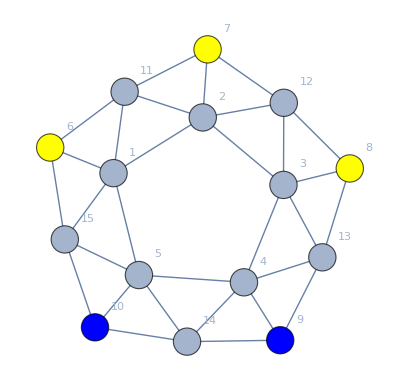

```mathematica
Graph[expMixedBis,VertexStyle->AssignColors[{4,4,4,3,3}],VertexSize->Large,VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding"]
```

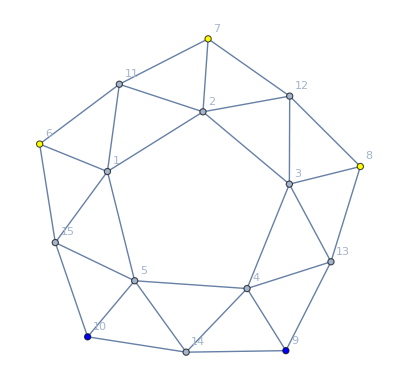

```mathematica
Graph[expMixedBis,VertexStyle->ToColors2[<|6->4,7->4,8->4,9->3,10->3|>]]
```

```mathematica
FromDigits[{4,4,2,2,4,1,1,1,1}-1,4]
```

251648

```mathematica
IntegerDigits[251648,4]
```

{3,3,1,1,3,0,0,0,0}

```mathematica
TableForm[
Monitor[
Table[CountSolutionsExtra[expMixedBis,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,1,1024}],k], TableDepth->2
]
```

```mathematica
DistributeDefinitions[expDouble,CountSolutions2,ToVars2,NumberToConstraint2]
```

{expDouble,CountSolutions2,NumberToConstraint2,ToVars2,exp}

```mathematica
TableForm[
Monitor[
Table[CountSolutions2[expDouble,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,0,4^10-1}],N[k/(4^10-1)*100,4]], TableDepth->2
]
```

$Aborted

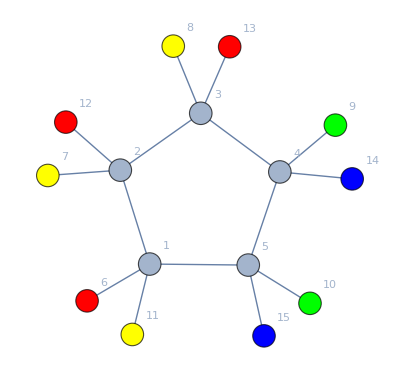

```mathematica
Graph[expDouble,VertexStyle->AssignColors[{1,4,4,2,2,4,1,1,3,3}],VertexSize->Large,VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
AssignColors[l_]:=Block[{result,i},
result=Association[];
For[i=1,i≤Length[l],i++,
result[i+5]=l[[i]]
];
ToColors2[result]
]
```

```mathematica
ToColors2[AssignColors[{1,4,4,2,2,4,1,1,3,3}]]
```

{6→RGBColor[1, 0, 0],7→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],9→RGBColor[0, 1, 0],10→RGBColor[0, 1, 0],11→RGBColor[1, 1, 0],12→RGBColor[1, 0, 0],13→RGBColor[1, 0, 0],14→RGBColor[0, 0, 1],15→RGBColor[0, 0, 1]}

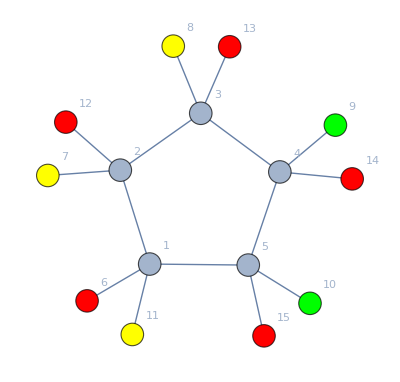

```mathematica
Graph[expDouble,VertexStyle->AssignColors[{1,4,4,2,2,4,1,1,1,1}],VertexSize->Large,VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Graph[expDouble,VertexStyle->AssignColors[{1,4,4,2,2,4,1,1,1,1}],VertexSize->Large,VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
TableForm[
Parallelize[ Table[CountSolutions2[expDouble,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,0,4^2-1}]], TableDepth->2
]//AbsoluteTiming
```

{22.6767,0 | {1,1,1,1,1,1,1,1,1,1} | {6,6,18,0,0,0}
1 | {1,1,1,1,1,1,1,1,1,2} | {4,4,12,0,0,0}
2 | {1,1,1,1,1,1,1,1,1,3} | {4,4,12,0,0,0}
3 | {1,1,1,1,1,1,1,1,1,4} | {4,4,12,0,0,0}
4 | {1,1,1,1,1,1,1,1,2,1} | {4,4,12,0,0,0}
5 | {1,1,1,1,1,1,1,1,2,2} | {2,2,6,0,0,0}
6 | {1,1,1,1,1,1,1,1,2,3} | {3,3,9,0,0,0}
7 | {1,1,1,1,1,1,1,1,2,4} | {3,3,9,0,0,0}
8 | {1,1,1,1,1,1,1,1,3,1} | {4,4,12,0,0,0}
9 | {1,1,1,1,1,1,1,1,3,2} | {3,3,9,0,0,0}
10 | {1,1,1,1,1,1,1,1,3,3} | {2,2,6,0,0,0}
11 | {1,1,1,1,1,1,1,1,3,4} | {3,3,9,0,0,0}
12 | {1,1,1,1,1,1,1,1,4,1} | {4,4,12,0,0,0}
13 | {1,1,1,1,1,1,1,1,4,2} | {3,3,9,0,0,0}
14 | {1,1,1,1,1,1,1,1,4,3} | {3,3,9,0,0,0}
15 | {1,1,1,1,1,1,1,1,4,4} | {2,2,6,0,0,0}}

```mathematica
TableForm[
Parallelize[ Table[CountSolutions2[expDouble,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,0,4^6-1}]], TableDepth->2
]//AbsoluteTiming
```

341 -> {{1, 1, 1, 1, 1, 2, 2, 2, 2, 2}, {0, 0, 0, 0, 0, 0}}

682 -> {{1, 1, 1, 1, 1, 3, 3, 3, 3, 3}, {0, 0, 0, 0, 0, 0}}

1023 -> {{1, 1, 1, 1, 1, 4, 4, 4, 4, 4}, {0, 0, 0, 0, 0, 0}}

1407 -> {{1, 1, 1, 1, 2, 2, 2, 4, 4, 4}, {0, 0, 0, 0, 2, 1}}

1447 -> {{1, 1, 1, 1, 2, 2, 3, 3, 2, 4}, {0, 0, 0, 0, 3, 1}}

1364 -> {{1, 1, 1, 1, 2, 2, 2, 2, 2, 1}, {0, 0, 0, 0, 0, 0}}

1386 -> {{1, 1, 1, 1, 2, 2, 2, 3, 3, 3}, {0, 0, 0, 0, 2, 1}}

1686 -> {{1, 1, 1, 1, 2, 3, 3, 2, 2, 3}, {0, 0, 0, 0, 2, 1}}

1786 -> {{1, 1, 1, 1, 2, 3, 4, 4, 3, 3}, {0, 0, 0, 0, 3, 1}}

1526 -> {{1, 1, 1, 1, 2, 2, 4, 4, 2, 3}, {0, 0, 0, 0, 3, 1}}

1967 -> {{1, 1, 1, 1, 2, 4, 3, 3, 4, 4}, {0, 0, 0, 0, 3, 1}}

2007 -> {{1, 1, 1, 1, 2, 4, 4, 2, 2, 4}, {0, 0, 0, 0, 2, 1}}

2549 -> {{1, 1, 1, 1, 3, 2, 4, 4, 2, 2}, {0, 0, 0, 0, 3, 1}}

2409 -> {{1, 1, 1, 1, 3, 2, 2, 3, 3, 2}, {0, 0, 0, 0, 2, 1}}

2709 -> {{1, 1, 1, 1, 3, 3, 3, 2, 2, 2}, {0, 0, 0, 0, 2, 1}}

2809 -> {{1, 1, 1, 1, 3, 3, 4, 4, 3, 2}, {0, 0, 0, 0, 3, 1}}

2728 -> {{1, 1, 1, 1, 3, 3, 3, 3, 3, 1}, {0, 0, 0, 0, 0, 0}}

2911 -> {{1, 1, 1, 1, 3, 4, 2, 2, 4, 4}, {0, 0, 0, 0, 3, 1}}

2651 -> {{1, 1, 1, 1, 3, 3, 2, 2, 3, 4}, {0, 0, 0, 0, 3, 1}}

2751 -> {{1, 1, 1, 1, 3, 3, 3, 4, 4, 4}, {0, 0, 0, 0, 2, 1}}

3051 -> {{1, 1, 1, 1, 3, 4, 4, 3, 3, 4}, {0, 0, 0, 0, 2, 1}}

3453 -> {{1, 1, 1, 1, 4, 2, 2, 4, 4, 2}, {0, 0, 0, 0, 2, 1}}

3493 -> {{1, 1, 1, 1, 4, 2, 3, 3, 2, 2}, {0, 0, 0, 0, 3, 1}}

3674 -> {{1, 1, 1, 1, 4, 3, 2, 2, 3, 3}, {0, 0, 0, 0, 3, 1}}

4013 -> {{1, 1, 1, 1, 4, 4, 3, 3, 4, 2}, {0, 0, 0, 0, 3, 1}}

3934 -> {{1, 1, 1, 1, 4, 4, 2, 2, 4, 3}, {0, 0, 0, 0, 3, 1}}

3774 -> {{1, 1, 1, 1, 4, 3, 3, 4, 4, 3}, {0, 0, 0, 0, 2, 1}}

4053 -> {{1, 1, 1, 1, 4, 4, 4, 2, 2, 2}, {0, 0, 0, 0, 2, 1}}

4074 -> {{1, 1, 1, 1, 4, 4, 4, 3, 3, 3}, {0, 0, 0, 0, 2, 1}}

4092 -> {{1, 1, 1, 1, 4, 4, 4, 4, 4, 1}, {0, 0, 0, 0, 0, 0}}

{7487.51,0 | {1,1,1,1,1,1,1,1,1,1} | {6,6,18,0,0,0}
1 | {1,1,1,1,1,1,1,1,1,2} | {4,4,12,0,0,0}
2 | {1,1,1,1,1,1,1,1,1,3} | {4,4,12,0,0,0}
3 | {1,1,1,1,1,1,1,1,1,4} | {4,4,12,0,0,0}
4 | {1,1,1,1,1,1,1,1,2,1} | {4,4,12,0,0,0}
5 | {1,1,1,1,1,1,1,1,2,2} | {2,2,6,0,0,0}
6 | {1,1,1,1,1,1,1,1,2,3} | {3,3,9,0,0,0}
7 | {1,1,1,1,1,1,1,1,2,4} | {3,3,9,0,0,0}
8 | {1,1,1,1,1,1,1,1,3,1} | {4,4,12,0,0,0}
9 | {1,1,1,1,1,1,1,1,3,2} | {3,3,9,0,0,0}
10 | {1,1,1,1,1,1,1,1,3,3} | {2,2,6,0,0,0}
11 | {1,1,1,1,1,1,1,1,3,4} | {3,3,9,0,0,0}
12 | {1,1,1,1,1,1,1,1,4,1} | {4,4,12,0,0,0}
13 | {1,1,1,1,1,1,1,1,4,2} | {3,3,9,0,0,0}
14 | {1,1,1,1,1,1,1,1,4,3} | {3,3,9,0,0,0}
15 | {1,1,1,1,1,1,1,1,4,4} | {2,2,6,0,0,0}
16 | {1,1,1,1,1,1,1,2,1,1} | {4,4,12,0,0,0}
17 | {1,1,1,1,1,1,1,2,1,2} | {4,4,6,0,0,0}
18 | {1,1,1,1,1,1,1,2,1,3} | {2,2,9,0,0,0}
19 | {1,1,1,1,1,1,1,2,1,4} | {2,2,9,0,0,0}
20 | {1,1,1,1,1,1,1,2,2,1} | {2,2,6,0,0,0}
21 | {1,1,1,1,1,1,1,2,2,2} | {2,2,0,0,0,0}
22 | {1,1,1,1,1,1,1,2,2,3} | {1,1,6,0,0,0}
23 | {1,1,1,1,1,1,1,2,2,4} | {1,1,6,0,0,0}
24 | {1,1,1,1,1,1,1,2,3,1} | {3,3,9,0,0,0}
25 | {1,1,1,1,1,1,1,2,3,2} | {3,3,6,0,0,0}
26 | {1,1,1,1,1,1,1,2,3,3} | {1,1,6,0,0,0}
27 | {1,1,1,1,1,1,1,2,3,4} | {2,2,6,0,0,0}
28 | {1,1,1,1,1,1,1,2,4,1} | {3,3,9,0,0,0}
29 | {1,1,1,1,1,1,1,2,4,2} | {3,3,6,0,0,0}
30 | {1,1,1,1,1,1,1,2,4,3} | {2,2,6,0,0,0}
31 | {1,1,1,1,1,1,1,2,4,4} | {1,1,6,0,0,0}
32 | {1,1,1,1,1,1,1,3,1,1} | {4,4,12,0,0,0}
33 | {1,1,1,1,1,1,1,3,1,2} | {2,2,9,0,0,0}
34 | {1,1,1,1,1,1,1,3,1,3} | {4,4,6,0,0,0}
35 | {1,1,1,1,1,1,1,3,1,4} | {2,2,9,0,0,0}
36 | {1,1,1,1,1,1,1,3,2,1} | {3,3,9,0,0,0}
37 | {1,1,1,1,1,1,1,3,2,2} | {1,1,6,0,0,0}
38 | {1,1,1,1,1,1,1,3,2,3} | {3,3,6,0,0,0}
39 | {1,1,1,1,1,1,1,3,2,4} | {2,2,6,0,0,0}
40 | {1,1,1,1,1,1,1,3,3,1} | {2,2,6,0,0,0}
41 | {1,1,1,1,1,1,1,3,3,2} | {1,1,6,0,0,0}
42 | {1,1,1,1,1,1,1,3,3,3} | {2,2,0,0,0,0}
43 | {1,1,1,1,1,1,1,3,3,4} | {1,1,6,0,0,0}
44 | {1,1,1,1,1,1,1,3,4,1} | {3,3,9,0,0,0}
45 | {1,1,1,1,1,1,1,3,4,2} | {2,2,6,0,0,0}
46 | {1,1,1,1,1,1,1,3,4,3} | {3,3,6,0,0,0}
47 | {1,1,1,1,1,1,1,3,4,4} | {1,1,6,0,0,0}
48 | {1,1,1,1,1,1,1,4,1,1} | {4,4,12,0,0,0}
49 | {1,1,1,1,1,1,1,4,1,2} | {2,2,9,0,0,0}
50 | {1,1,1,1,1,1,1,4,1,3} | {2,2,9,0,0,0}
51 | {1,1,1,1,1,1,1,4,1,4} | {4,4,6,0,0,0}
52 | {1,1,1,1,1,1,1,4,2,1} | {3,3,9,0,0,0}
53 | {1,1,1,1,1,1,1,4,2,2} | {1,1,6,0,0,0}
54 | {1,1,1,1,1,1,1,4,2,3} | {2,2,6,0,0,0}
55 | {1,1,1,1,1,1,1,4,2,4} | {3,3,6,0,0,0}
56 | {1,1,1,1,1,1,1,4,3,1} | {3,3,9,0,0,0}
57 | {1,1,1,1,1,1,1,4,3,2} | {2,2,6,0,0,0}
58 | {1,1,1,1,1,1,1,4,3,3} | {1,1,6,0,0,0}
59 | {1,1,1,1,1,1,1,4,3,4} | {3,3,6,0,0,0}
60 | {1,1,1,1,1,1,1,4,4,1} | {2,2,6,0,0,0}
61 | {1,1,1,1,1,1,1,4,4,2} | {1,1,6,0,0,0}
62 | {1,1,1,1,1,1,1,4,4,3} | {1,1,6,0,0,0}
63 | {1,1,1,1,1,1,1,4,4,4} | {2,2,0,0,0,0}
64 | {1,1,1,1,1,1,2,1,1,1} | {4,4,12,0,0,0}
65 | {1,1,1,1,1,1,2,1,1,2} | {2,2,10,0,0,0}
66 | {1,1,1,1,1,1,2,1,1,3} | {3,3,7,0,0,0}
67 | {1,1,1,1,1,1,2,1,1,4} | {3,3,7,0,0,0}
68 | {1,1,1,1,1,1,2,1,2,1} | {4,2,8,0,0,0}
69 | {1,1,1,1,1,1,2,1,2,2} | {2,0,6,0,0,0}
70 | {1,1,1,1,1,1,2,1,2,3} | {3,2,5,0,0,0}
71 | {1,1,1,1,1,1,2,1,2,4} | {3,2,5,0,0,0}
72 | {1,1,1,1,1,1,2,1,3,1} | {2,3,8,0,0,0}
73 | {1,1,1,1,1,1,2,1,3,2} | {1,2,7,0,0,0}
74 | {1,1,1,1,1,1,2,1,3,3} | {1,2,3,0,0,0}
75 | {1,1,1,1,1,1,2,1,3,4} | {2,2,6,0,0,0}
76 | {1,1,1,1,1,1,2,1,4,1} | {2,3,8,0,0,0}
77 | {1,1,1,1,1,1,2,1,4,2} | {1,2,7,0,0,0}
78 | {1,1,1,1,1,1,2,1,4,3} | {2,2,6,0,0,0}
79 | {1,1,1,1,1,1,2,1,4,4} | {1,2,3,0,0,0}
80 | {1,1,1,1,1,1,2,2,1,1} | {2,2,6,0,0,0}
81 | {1,1,1,1,1,1,2,2,1,2} | {2,2,4,0,0,0}
82 | {1,1,1,1,1,1,2,2,1,3} | {1,1,4,0,0,0}
83 | {1,1,1,1,1,1,2,2,1,4} | {1,1,4,0,0,0}
84 | {1,1,1,1,1,1,2,2,2,1} | {2,0,2,0,0,0}
85 | {1,1,1,1,1,1,2,2,2,2} | {2,0,0,0,0,0}
86 | {1,1,1,1,1,1,2,2,2,3} | {1,0,2,0,0,0}
87 | {1,1,1,1,1,1,2,2,2,4} | {1,0,2,0,0,0}
88 | {1,1,1,1,1,1,2,2,3,1} | {1,2,5,0,0,0}
89 | {1,1,1,1,1,1,2,2,3,2} | {1,2,4,0,0,0}
90 | {1,1,1,1,1,1,2,2,3,3} | {0,1,3,0,0,0}
91 | {1,1,1,1,1,1,2,2,3,4} | {1,1,3,0,0,0}
92 | {1,1,1,1,1,1,2,2,4,1} | {1,2,5,0,0,0}
93 | {1,1,1,1,1,1,2,2,4,2} | {1,2,4,0,0,0}
94 | {1,1,1,1,1,1,2,2,4,3} | {1,1,3,0,0,0}
95 | {1,1,1,1,1,1,2,2,4,4} | {0,1,3,0,0,0}
96 | {1,1,1,1,1,1,2,3,1,1} | {3,3,9,0,0,0}
97 | {1,1,1,1,1,1,2,3,1,2} | {1,1,8,0,0,0}
98 | {1,1,1,1,1,1,2,3,1,3} | {3,3,4,0,0,0}
99 | {1,1,1,1,1,1,2,3,1,4} | {2,2,6,0,0,0}
100 | {1,1,1,1,1,1,2,3,2,1} | {3,2,7,0,0,0}
101 | {1,1,1,1,1,1,2,3,2,2} | {1,0,6,0,0,0}
102 | {1,1,1,1,1,1,2,3,2,3} | {3,2,4,0,0,0}
103 | {1,1,1,1,1,1,2,3,2,4} | {2,2,4,0,0,0}
104 | {1,1,1,1,1,1,2,3,3,1} | {1,2,5,0,0,0}
105 | {1,1,1,1,1,1,2,3,3,2} | {0,1,5,0,0,0}
106 | {1,1,1,1,1,1,2,3,3,3} | {1,2,0,0,0,0}
107 | {1,1,1,1,1,1,2,3,3,4} | {1,1,5,0,0,0}
108 | {1,1,1,1,1,1,2,3,4,1} | {2,2,6,0,0,0}
109 | {1,1,1,1,1,1,2,3,4,2} | {1,1,5,0,0,0}
110 | {1,1,1,1,1,1,2,3,4,3} | {2,2,4,0,0,0}
111 | {1,1,1,1,1,1,2,3,4,4} | {1,1,3,0,0,0}
112 | {1,1,1,1,1,1,2,4,1,1} | {3,3,9,0,0,0}
113 | {1,1,1,1,1,1,2,4,1,2} | {1,1,8,0,0,0}
114 | {1,1,1,1,1,1,2,4,1,3} | {2,2,6,0,0,0}
115 | {1,1,1,1,1,1,2,4,1,4} | {3,3,4,0,0,0}
116 | {1,1,1,1,1,1,2,4,2,1} | {3,2,7,0,0,0}
117 | {1,1,1,1,1,1,2,4,2,2} | {1,0,6,0,0,0}
118 | {1,1,1,1,1,1,2,4,2,3} | {2,2,4,0,0,0}
119 | {1,1,1,1,1,1,2,4,2,4} | {3,2,4,0,0,0}
120 | {1,1,1,1,1,1,2,4,3,1} | {2,2,6,0,0,0}
121 | {1,1,1,1,1,1,2,4,3,2} | {1,1,5,0,0,0}
122 | {1,1,1,1,1,1,2,4,3,3} | {1,1,3,0,0,0}
123 | {1,1,1,1,1,1,2,4,3,4} | {2,2,4,0,0,0}
124 | {1,1,1,1,1,1,2,4,4,1} | {1,2,5,0,0,0}
125 | {1,1,1,1,1,1,2,4,4,2} | {0,1,5,0,0,0}
126 | {1,1,1,1,1,1,2,4,4,3} | {1,1,5,0,0,0}
127 | {1,1,1,1,1,1,2,4,4,4} | {1,2,0,0,0,0}
128 | {1,1,1,1,1,1,3,1,1,1} | {4,4,12,0,0,0}
129 | {1,1,1,1,1,1,3,1,1,2} | {3,3,7,0,0,0}
130 | {1,1,1,1,1,1,3,1,1,3} | {2,2,10,0,0,0}
131 | {1,1,1,1,1,1,3,1,1,4} | {3,3,7,0,0,0}
132 | {1,1,1,1,1,1,3,1,2,1} | {2,3,8,0,0,0}
133 | {1,1,1,1,1,1,3,1,2,2} | {1,2,3,0,0,0}
134 | {1,1,1,1,1,1,3,1,2,3} | {1,2,7,0,0,0}
135 | {1,1,1,1,1,1,3,1,2,4} | {2,2,6,0,0,0}
136 | {1,1,1,1,1,1,3,1,3,1} | {4,2,8,0,0,0}
137 | {1,1,1,1,1,1,3,1,3,2} | {3,2,5,0,0,0}
138 | {1,1,1,1,1,1,3,1,3,3} | {2,0,6,0,0,0}
139 | {1,1,1,1,1,1,3,1,3,4} | {3,2,5,0,0,0}
140 | {1,1,1,1,1,1,3,1,4,1} | {2,3,8,0,0,0}
141 | {1,1,1,1,1,1,3,1,4,2} | {2,2,6,0,0,0}
142 | {1,1,1,1,1,1,3,1,4,3} | {1,2,7,0,0,0}
143 | {1,1,1,1,1,1,3,1,4,4} | {1,2,3,0,0,0}
144 | {1,1,1,1,1,1,3,2,1,1} | {3,3,9,0,0,0}
145 | {1,1,1,1,1,1,3,2,1,2} | {3,3,4,0,0,0}
146 | {1,1,1,1,1,1,3,2,1,3} | {1,1,8,0,0,0}
147 | {1,1,1,1,1,1,3,2,1,4} | {2,2,6,0,0,0}
148 | {1,1,1,1,1,1,3,2,2,1} | {1,2,5,0,0,0}
149 | {1,1,1,1,1,1,3,2,2,2} | {1,2,0,0,0,0}
150 | {1,1,1,1,1,1,3,2,2,3} | {0,1,5,0,0,0}
151 | {1,1,1,1,1,1,3,2,2,4} | {1,1,5,0,0,0}
152 | {1,1,1,1,1,1,3,2,3,1} | {3,2,7,0,0,0}
153 | {1,1,1,1,1,1,3,2,3,2} | {3,2,4,0,0,0}
154 | {1,1,1,1,1,1,3,2,3,3} | {1,0,6,0,0,0}
155 | {1,1,1,1,1,1,3,2,3,4} | {2,2,4,0,0,0}
156 | {1,1,1,1,1,1,3,2,4,1} | {2,2,6,0,0,0}
157 | {1,1,1,1,1,1,3,2,4,2} | {2,2,4,0,0,0}
158 | {1,1,1,1,1,1,3,2,4,3} | {1,1,5,0,0,0}
159 | {1,1,1,1,1,1,3,2,4,4} | {1,1,3,0,0,0}
160 | {1,1,1,1,1,1,3,3,1,1} | {2,2,6,0,0,0}
161 | {1,1,1,1,1,1,3,3,1,2} | {1,1,4,0,0,0}
162 | {1,1,1,1,1,1,3,3,1,3} | {2,2,4,0,0,0}
163 | {1,1,1,1,1,1,3,3,1,4} | {1,1,4,0,0,0}
164 | {1,1,1,1,1,1,3,3,2,1} | {1,2,5,0,0,0}
165 | {1,1,1,1,1,1,3,3,2,2} | {0,1,3,0,0,0}
166 | {1,1,1,1,1,1,3,3,2,3} | {1,2,4,0,0,0}
167 | {1,1,1,1,1,1,3,3,2,4} | {1,1,3,0,0,0}
168 | {1,1,1,1,1,1,3,3,3,1} | {2,0,2,0,0,0}
169 | {1,1,1,1,1,1,3,3,3,2} | {1,0,2,0,0,0}
170 | {1,1,1,1,1,1,3,3,3,3} | {2,0,0,0,0,0}
171 | {1,1,1,1,1,1,3,3,3,4} | {1,0,2,0,0,0}
172 | {1,1,1,1,1,1,3,3,4,1} | {1,2,5,0,0,0}
173 | {1,1,1,1,1,1,3,3,4,2} | {1,1,3,0,0,0}
174 | {1,1,1,1,1,1,3,3,4,3} | {1,2,4,0,0,0}
175 | {1,1,1,1,1,1,3,3,4,4} | {0,1,3,0,0,0}
176 | {1,1,1,1,1,1,3,4,1,1} | {3,3,9,0,0,0}
177 | {1,1,1,1,1,1,3,4,1,2} | {2,2,6,0,0,0}
178 | {1,1,1,1,1,1,3,4,1,3} | {1,1,8,0,0,0}
179 | {1,1,1,1,1,1,3,4,1,4} | {3,3,4,0,0,0}
180 | {1,1,1,1,1,1,3,4,2,1} | {2,2,6,0,0,0}
181 | {1,1,1,1,1,1,3,4,2,2} | {1,1,3,0,0,0}
182 | {1,1,1,1,1,1,3,4,2,3} | {1,1,5,0,0,0}
183 | {1,1,1,1,1,1,3,4,2,4} | {2,2,4,0,0,0}
184 | {1,1,1,1,1,1,3,4,3,1} | {3,2,7,0,0,0}
185 | {1,1,1,1,1,1,3,4,3,2} | {2,2,4,0,0,0}
186 | {1,1,1,1,1,1,3,4,3,3} | {1,0,6,0,0,0}
187 | {1,1,1,1,1,1,3,4,3,4} | {3,2,4,0,0,0}
188 | {1,1,1,1,1,1,3,4,4,1} | {1,2,5,0,0,0}
189 | {1,1,1,1,1,1,3,4,4,2} | {1,1,5,0,0,0}
190 | {1,1,1,1,1,1,3,4,4,3} | {0,1,5,0,0,0}
191 | {1,1,1,1,1,1,3,4,4,4} | {1,2,0,0,0,0}
192 | {1,1,1,1,1,1,4,1,1,1} | {4,4,12,0,0,0}
193 | {1,1,1,1,1,1,4,1,1,2} | {3,3,7,0,0,0}
194 | {1,1,1,1,1,1,4,1,1,3} | {3,3,7,0,0,0}
195 | {1,1,1,1,1,1,4,1,1,4} | {2,2,10,0,0,0}
196 | {1,1,1,1,1,1,4,1,2,1} | {2,3,8,0,0,0}
197 | {1,1,1,1,1,1,4,1,2,2} | {1,2,3,0,0,0}
198 | {1,1,1,1,1,1,4,1,2,3} | {2,2,6,0,0,0}
199 | {1,1,1,1,1,1,4,1,2,4} | {1,2,7,0,0,0}
200 | {1,1,1,1,1,1,4,1,3,1} | {2,3,8,0,0,0}
201 | {1,1,1,1,1,1,4,1,3,2} | {2,2,6,0,0,0}
202 | {1,1,1,1,1,1,4,1,3,3} | {1,2,3,0,0,0}
203 | {1,1,1,1,1,1,4,1,3,4} | {1,2,7,0,0,0}
204 | {1,1,1,1,1,1,4,1,4,1} | {4,2,8,0,0,0}
205 | {1,1,1,1,1,1,4,1,4,2} | {3,2,5,0,0,0}
206 | {1,1,1,1,1,1,4,1,4,3} | {3,2,5,0,0,0}
207 | {1,1,1,1,1,1,4,1,4,4} | {2,0,6,0,0,0}
208 | {1,1,1,1,1,1,4,2,1,1} | {3,3,9,0,0,0}
209 | {1,1,1,1,1,1,4,2,1,2} | {3,3,4,0,0,0}
210 | {1,1,1,1,1,1,4,2,1,3} | {2,2,6,0,0,0}
211 | {1,1,1,1,1,1,4,2,1,4} | {1,1,8,0,0,0}
212 | {1,1,1,1,1,1,4,2,2,1} | {1,2,5,0,0,0}
213 | {1,1,1,1,1,1,4,2,2,2} | {1,2,0,0,0,0}
214 | {1,1,1,1,1,1,4,2,2,3} | {1,1,5,0,0,0}
215 | {1,1,1,1,1,1,4,2,2,4} | {0,1,5,0,0,0}
216 | {1,1,1,1,1,1,4,2,3,1} | {2,2,6,0,0,0}
217 | {1,1,1,1,1,1,4,2,3,2} | {2,2,4,0,0,0}
218 | {1,1,1,1,1,1,4,2,3,3} | {1,1,3,0,0,0}
219 | {1,1,1,1,1,1,4,2,3,4} | {1,1,5,0,0,0}
220 | {1,1,1,1,1,1,4,2,4,1} | {3,2,7,0,0,0}
221 | {1,1,1,1,1,1,4,2,4,2} | {3,2,4,0,0,0}
222 | {1,1,1,1,1,1,4,2,4,3} | {2,2,4,0,0,0}
223 | {1,1,1,1,1,1,4,2,4,4} | {1,0,6,0,0,0}
224 | {1,1,1,1,1,1,4,3,1,1} | {3,3,9,0,0,0}
225 | {1,1,1,1,1,1,4,3,1,2} | {2,2,6,0,0,0}
226 | {1,1,1,1,1,1,4,3,1,3} | {3,3,4,0,0,0}
227 | {1,1,1,1,1,1,4,3,1,4} | {1,1,8,0,0,0}
228 | {1,1,1,1,1,1,4,3,2,1} | {2,2,6,0,0,0}
229 | {1,1,1,1,1,1,4,3,2,2} | {1,1,3,0,0,0}
230 | {1,1,1,1,1,1,4,3,2,3} | {2,2,4,0,0,0}
231 | {1,1,1,1,1,1,4,3,2,4} | {1,1,5,0,0,0}
232 | {1,1,1,1,1,1,4,3,3,1} | {1,2,5,0,0,0}
233 | {1,1,1,1,1,1,4,3,3,2} | {1,1,5,0,0,0}
234 | {1,1,1,1,1,1,4,3,3,3} | {1,2,0,0,0,0}
235 | {1,1,1,1,1,1,4,3,3,4} | {0,1,5,0,0,0}
236 | {1,1,1,1,1,1,4,3,4,1} | {3,2,7,0,0,0}
237 | {1,1,1,1,1,1,4,3,4,2} | {2,2,4,0,0,0}
238 | {1,1,1,1,1,1,4,3,4,3} | {3,2,4,0,0,0}
239 | {1,1,1,1,1,1,4,3,4,4} | {1,0,6,0,0,0}
240 | {1,1,1,1,1,1,4,4,1,1} | {2,2,6,0,0,0}
241 | {1,1,1,1,1,1,4,4,1,2} | {1,1,4,0,0,0}
242 | {1,1,1,1,1,1,4,4,1,3} | {1,1,4,0,0,0}
243 | {1,1,1,1,1,1,4,4,1,4} | {2,2,4,0,0,0}
244 | {1,1,1,1,1,1,4,4,2,1} | {1,2,5,0,0,0}
245 | {1,1,1,1,1,1,4,4,2,2} | {0,1,3,0,0,0}
246 | {1,1,1,1,1,1,4,4,2,3} | {1,1,3,0,0,0}
247 | {1,1,1,1,1,1,4,4,2,4} | {1,2,4,0,0,0}
248 | {1,1,1,1,1,1,4,4,3,1} | {1,2,5,0,0,0}
249 | {1,1,1,1,1,1,4,4,3,2} | {1,1,3,0,0,0}
250 | {1,1,1,1,1,1,4,4,3,3} | {0,1,3,0,0,0}
251 | {1,1,1,1,1,1,4,4,3,4} | {1,2,4,0,0,0}
252 | {1,1,1,1,1,1,4,4,4,1} | {2,0,2,0,0,0}
253 | {1,1,1,1,1,1,4,4,4,2} | {1,0,2,0,0,0}
254 | {1,1,1,1,1,1,4,4,4,3} | {1,0,2,0,0,0}
255 | {1,1,1,1,1,1,4,4,4,4} | {2,0,0,0,0,0}
256 | {1,1,1,1,1,2,1,1,1,1} | {4,4,12,0,0,0}
257 | {1,1,1,1,1,2,1,1,1,2} | {2,2,6,0,0,0}
258 | {1,1,1,1,1,2,1,1,1,3} | {3,3,9,0,0,0}
259 | {1,1,1,1,1,2,1,1,1,4} | {3,3,9,0,0,0}
260 | {1,1,1,1,1,2,1,1,2,1} | {2,4,8,0,0,0}
261 | {1,1,1,1,1,2,1,1,2,2} | {0,2,2,0,0,0}
262 | {1,1,1,1,1,2,1,1,2,3} | {2,3,7,0,0,0}
263 | {1,1,1,1,1,2,1,1,2,4} | {2,3,7,0,0,0}
264 | {1,1,1,1,1,2,1,1,3,1} | {3,2,8,0,0,0}
265 | {1,1,1,1,1,2,1,1,3,2} | {2,1,5,0,0,0}
266 | {1,1,1,1,1,2,1,1,3,3} | {2,1,5,0,0,0}
267 | {1,1,1,1,1,2,1,1,3,4} | {2,2,6,0,0,0}
268 | {1,1,1,1,1,2,1,1,4,1} | {3,2,8,0,0,0}
269 | {1,1,1,1,1,2,1,1,4,2} | {2,1,5,0,0,0}
270 | {1,1,1,1,1,2,1,1,4,3} | {2,2,6,0,0,0}
271 | {1,1,1,1,1,2,1,1,4,4} | {2,1,5,0,0,0}
272 | {1,1,1,1,1,2,1,2,1,1} | {2,2,10,0,0,0}
273 | {1,1,1,1,1,2,1,2,1,2} | {2,2,4,0,0,0}
274 | {1,1,1,1,1,2,1,2,1,3} | {1,1,8,0,0,0}
275 | {1,1,1,1,1,2,1,2,1,4} | {1,1,8,0,0,0}
276 | {1,1,1,1,1,2,1,2,2,1} | {0,2,6,0,0,0}
277 | {1,1,1,1,1,2,1,2,2,2} | {0,2,0,0,0,0}
278 | {1,1,1,1,1,2,1,2,2,3} | {0,1,6,0,0,0}
279 | {1,1,1,1,1,2,1,2,2,4} | {0,1,6,0,0,0}
280 | {1,1,1,1,1,2,1,2,3,1} | {2,1,7,0,0,0}
281 | {1,1,1,1,1,2,1,2,3,2} | {2,1,4,0,0,0}
282 | {1,1,1,1,1,2,1,2,3,3} | {1,0,5,0,0,0}
283 | {1,1,1,1,1,2,1,2,3,4} | {1,1,5,0,0,0}
284 | {1,1,1,1,1,2,1,2,4,1} | {2,1,7,0,0,0}
285 | {1,1,1,1,1,2,1,2,4,2} | {2,1,4,0,0,0}
286 | {1,1,1,1,1,2,1,2,4,3} | {1,1,5,0,0,0}
287 | {1,1,1,1,1,2,1,2,4,4} | {1,0,5,0,0,0}
288 | {1,1,1,1,1,2,1,3,1,1} | {3,3,7,0,0,0}
289 | {1,1,1,1,1,2,1,3,1,2} | {1,1,4,0,0,0}
290 | {1,1,1,1,1,2,1,3,1,3} | {3,3,4,0,0,0}
291 | {1,1,1,1,1,2,1,3,1,4} | {2,2,6,0,0,0}
292 | {1,1,1,1,1,2,1,3,2,1} | {2,3,5,0,0,0}
293 | {1,1,1,1,1,2,1,3,2,2} | {0,1,2,0,0,0}
294 | {1,1,1,1,1,2,1,3,2,3} | {2,3,4,0,0,0}
295 | {1,1,1,1,1,2,1,3,2,4} | {2,2,4,0,0,0}
296 | {1,1,1,1,1,2,1,3,3,1} | {2,1,3,0,0,0}
297 | {1,1,1,1,1,2,1,3,3,2} | {1,0,3,0,0,0}
298 | {1,1,1,1,1,2,1,3,3,3} | {2,1,0,0,0,0}
299 | {1,1,1,1,1,2,1,3,3,4} | {1,1,3,0,0,0}
300 | {1,1,1,1,1,2,1,3,4,1} | {2,2,6,0,0,0}
301 | {1,1,1,1,1,2,1,3,4,2} | {1,1,3,0,0,0}
302 | {1,1,1,1,1,2,1,3,4,3} | {2,2,4,0,0,0}
303 | {1,1,1,1,1,2,1,3,4,4} | {1,1,5,0,0,0}
304 | {1,1,1,1,1,2,1,4,1,1} | {3,3,7,0,0,0}
305 | {1,1,1,1,1,2,1,4,1,2} | {1,1,4,0,0,0}
306 | {1,1,1,1,1,2,1,4,1,3} | {2,2,6,0,0,0}
307 | {1,1,1,1,1,2,1,4,1,4} | {3,3,4,0,0,0}
308 | {1,1,1,1,1,2,1,4,2,1} | {2,3,5,0,0,0}
309 | {1,1,1,1,1,2,1,4,2,2} | {0,1,2,0,0,0}
310 | {1,1,1,1,1,2,1,4,2,3} | {2,2,4,0,0,0}
311 | {1,1,1,1,1,2,1,4,2,4} | {2,3,4,0,0,0}
312 | {1,1,1,1,1,2,1,4,3,1} | {2,2,6,0,0,0}
313 | {1,1,1,1,1,2,1,4,3,2} | {1,1,3,0,0,0}
314 | {1,1,1,1,1,2,1,4,3,3} | {1,1,5,0,0,0}
315 | {1,1,1,1,1,2,1,4,3,4} | {2,2,4,0,0,0}
316 | {1,1,1,1,1,2,1,4,4,1} | {2,1,3,0,0,0}
317 | {1,1,1,1,1,2,1,4,4,2} | {1,0,3,0,0,0}
318 | {1,1,1,1,1,2,1,4,4,3} | {1,1,3,0,0,0}
319 | {1,1,1,1,1,2,1,4,4,4} | {2,1,0,0,0,0}
320 | {1,1,1,1,1,2,2,1,1,1} | {2,2,6,0,0,0}
321 | {1,1,1,1,1,2,2,1,1,2} | {0,0,4,0,0,0}
322 | {1,1,1,1,1,2,2,1,1,3} | {2,2,4,0,0,0}
323 | {1,1,1,1,1,2,2,1,1,4} | {2,2,4,0,0,0}
324 | {1,1,1,1,1,2,2,1,2,1} | {2,2,4,0,0,0}
325 | {1,1,1,1,1,2,2,1,2,2} | {0,0,2,0,0,0}
326 | {1,1,1,1,1,2,2,1,2,3} | {2,2,3,0,0,0}
327 | {1,1,1,1,1,2,2,1,2,4} | {2,2,3,0,0,0}
328 | {1,1,1,1,1,2,2,1,3,1} | {1,1,4,0,0,0}
329 | {1,1,1,1,1,2,2,1,3,2} | {0,0,3,0,0,0}
330 | {1,1,1,1,1,2,2,1,3,3} | {1,1,2,0,0,0}
331 | {1,1,1,1,1,2,2,1,3,4} | {1,1,3,0,0,0}
332 | {1,1,1,1,1,2,2,1,4,1} | {1,1,4,0,0,0}
333 | {1,1,1,1,1,2,2,1,4,2} | {0,0,3,0,0,0}
334 | {1,1,1,1,1,2,2,1,4,3} | {1,1,3,0,0,0}
335 | {1,1,1,1,1,2,2,1,4,4} | {1,1,2,0,0,0}
336 | {1,1,1,1,1,2,2,2,1,1} | {0,0,4,0,0,0}
337 | {1,1,1,1,1,2,2,2,1,2} | {0,0,2,0,0,0}
338 | {1,1,1,1,1,2,2,2,1,3} | {0,0,3,0,0,0}
339 | {1,1,1,1,1,2,2,2,1,4} | {0,0,3,0,0,0}
340 | {1,1,1,1,1,2,2,2,2,1} | {0,0,2,0,0,0}
341 | {1,1,1,1,1,2,2,2,2,2} | {0,0,0,0,0,0}
342 | {1,1,1,1,1,2,2,2,2,3} | {0,0,2,0,0,0}
343 | {1,1,1,1,1,2,2,2,2,4} | {0,0,2,0,0,0}
344 | {1,1,1,1,1,2,2,2,3,1} | {0,0,3,0,0,0}
345 | {1,1,1,1,1,2,2,2,3,2} | {0,0,2,0,0,0}
346 | {1,1,1,1,1,2,2,2,3,3} | {0,0,2,0,0,0}
347 | {1,1,1,1,1,2,2,2,3,4} | {0,0,2,0,0,0}
348 | {1,1,1,1,1,2,2,2,4,1} | {0,0,3,0,0,0}
349 | {1,1,1,1,1,2,2,2,4,2} | {0,0,2,0,0,0}
350 | {1,1,1,1,1,2,2,2,4,3} | {0,0,2,0,0,0}
351 | {1,1,1,1,1,2,2,2,4,4} | {0,0,2,0,0,0}
352 | {1,1,1,1,1,2,2,3,1,1} | {2,2,4,0,0,0}
353 | {1,1,1,1,1,2,2,3,1,2} | {0,0,3,0,0,0}
354 | {1,1,1,1,1,2,2,3,1,3} | {2,2,2,0,0,0}
355 | {1,1,1,1,1,2,2,3,1,4} | {2,2,3,0,0,0}
356 | {1,1,1,1,1,2,2,3,2,1} | {2,2,3,0,0,0}
357 | {1,1,1,1,1,2,2,3,2,2} | {0,0,2,0,0,0}
358 | {1,1,1,1,1,2,2,3,2,3} | {2,2,2,0,0,0}
359 | {1,1,1,1,1,2,2,3,2,4} | {2,2,2,0,0,0}
360 | {1,1,1,1,1,2,2,3,3,1} | {1,1,2,0,0,0}
361 | {1,1,1,1,1,2,2,3,3,2} | {0,0,2,0,0,0}
362 | {1,1,1,1,1,2,2,3,3,3} | {1,1,0,0,0,0}
363 | {1,1,1,1,1,2,2,3,3,4} | {1,1,2,0,0,0}
364 | {1,1,1,1,1,2,2,3,4,1} | {1,1,3,0,0,0}
365 | {1,1,1,1,1,2,2,3,4,2} | {0,0,2,0,0,0}
366 | {1,1,1,1,1,2,2,3,4,3} | {1,1,2,0,0,0}
367 | {1,1,1,1,1,2,2,3,4,4} | {1,1,2,0,0,0}
368 | {1,1,1,1,1,2,2,4,1,1} | {2,2,4,0,0,0}
369 | {1,1,1,1,1,2,2,4,1,2} | {0,0,3,0,0,0}
370 | {1,1,1,1,1,2,2,4,1,3} | {2,2,3,0,0,0}
371 | {1,1,1,1,1,2,2,4,1,4} | {2,2,2,0,0,0}
372 | {1,1,1,1,1,2,2,4,2,1} | {2,2,3,0,0,0}
373 | {1,1,1,1,1,2,2,4,2,2} | {0,0,2,0,0,0}
374 | {1,1,1,1,1,2,2,4,2,3} | {2,2,2,0,0,0}
375 | {1,1,1,1,1,2,2,4,2,4} | {2,2,2,0,0,0}
376 | {1,1,1,1,1,2,2,4,3,1} | {1,1,3,0,0,0}
377 | {1,1,1,1,1,2,2,4,3,2} | {0,0,2,0,0,0}
378 | {1,1,1,1,1,2,2,4,3,3} | {1,1,2,0,0,0}
379 | {1,1,1,1,1,2,2,4,3,4} | {1,1,2,0,0,0}
380 | {1,1,1,1,1,2,2,4,4,1} | {1,1,2,0,0,0}
381 | {1,1,1,1,1,2,2,4,4,2} | {0,0,2,0,0,0}
382 | {1,1,1,1,1,2,2,4,4,3} | {1,1,2,0,0,0}
383 | {1,1,1,1,1,2,2,4,4,4} | {1,1,0,0,0,0}
384 | {1,1,1,1,1,2,3,1,1,1} | {3,3,9,0,0,0}
385 | {1,1,1,1,1,2,3,1,1,2} | {2,2,4,0,0,0}
386 | {1,1,1,1,1,2,3,1,1,3} | {2,2,8,0,0,0}
387 | {1,1,1,1,1,2,3,1,1,4} | {2,2,6,0,0,0}
388 | {1,1,1,1,1,2,3,1,2,1} | {1,3,6,0,0,0}
389 | {1,1,1,1,1,2,3,1,2,2} | {0,2,1,0,0,0}
390 | {1,1,1,1,1,2,3,1,2,3} | {1,2,6,0,0,0}
391 | {1,1,1,1,1,2,3,1,2,4} | {1,2,5,0,0,0}
392 | {1,1,1,1,1,2,3,1,3,1} | {3,1,6,0,0,0}
393 | {1,1,1,1,1,2,3,1,3,2} | {2,1,3,0,0,0}
394 | {1,1,1,1,1,2,3,1,3,3} | {2,0,5,0,0,0}
395 | {1,1,1,1,1,2,3,1,3,4} | {2,1,4,0,0,0}
396 | {1,1,1,1,1,2,3,1,4,1} | {2,2,6,0,0,0}
397 | {1,1,1,1,1,2,3,1,4,2} | {2,1,4,0,0,0}
398 | {1,1,1,1,1,2,3,1,4,3} | {1,2,5,0,0,0}
399 | {1,1,1,1,1,2,3,1,4,4} | {1,1,3,0,0,0}
400 | {1,1,1,1,1,2,3,2,1,1} | {2,2,8,0,0,0}
401 | {1,1,1,1,1,2,3,2,1,2} | {2,2,3,0,0,0}
402 | {1,1,1,1,1,2,3,2,1,3} | {1,1,7,0,0,0}
403 | {1,1,1,1,1,2,3,2,1,4} | {1,1,6,0,0,0}
404 | {1,1,1,1,1,2,3,2,2,1} | {0,2,5,0,0,0}
405 | {1,1,1,1,1,2,3,2,2,2} | {0,2,0,0,0,0}
406 | {1,1,1,1,1,2,3,2,2,3} | {0,1,5,0,0,0}
407 | {1,1,1,1,1,2,3,2,2,4} | {0,1,5,0,0,0}
408 | {1,1,1,1,1,2,3,2,3,1} | {2,1,6,0,0,0}
409 | {1,1,1,1,1,2,3,2,3,2} | {2,1,3,0,0,0}
410 | {1,1,1,1,1,2,3,2,3,3} | {1,0,5,0,0,0}
411 | {1,1,1,1,1,2,3,2,3,4} | {1,1,4,0,0,0}
412 | {1,1,1,1,1,2,3,2,4,1} | {2,1,5,0,0,0}
413 | {1,1,1,1,1,2,3,2,4,2} | {2,1,3,0,0,0}
414 | {1,1,1,1,1,2,3,2,4,3} | {1,1,4,0,0,0}
415 | {1,1,1,1,1,2,3,2,4,4} | {1,0,3,0,0,0}
416 | {1,1,1,1,1,2,3,3,1,1} | {2,2,4,0,0,0}
417 | {1,1,1,1,1,2,3,3,1,2} | {1,1,2,0,0,0}
418 | {1,1,1,1,1,2,3,3,1,3} | {2,2,3,0,0,0}
419 | {1,1,1,1,1,2,3,3,1,4} | {1,1,3,0,0,0}
420 | {1,1,1,1,1,2,3,3,2,1} | {1,2,3,0,0,0}
421 | {1,1,1,1,1,2,3,3,2,2} | {0,1,1,0,0,0}
422 | {1,1,1,1,1,2,3,3,2,3} | {1,2,3,0,0,0}
423 | {1,1,1,1,1,2,3,3,2,4} | {1,1,2,0,0,0}
424 | {1,1,1,1,1,2,3,3,3,1} | {2,0,1,0,0,0}
425 | {1,1,1,1,1,2,3,3,3,2} | {1,0,1,0,0,0}
426 | {1,1,1,1,1,2,3,3,3,3} | {2,0,0,0,0,0}
427 | {1,1,1,1,1,2,3,3,3,4} | {1,0,1,0,0,0}
428 | {1,1,1,1,1,2,3,3,4,1} | {1,2,4,0,0,0}
429 | {1,1,1,1,1,2,3,3,4,2} | {1,1,2,0,0,0}
430 | {1,1,1,1,1,2,3,3,4,3} | {1,2,3,0,0,0}
431 | {1,1,1,1,1,2,3,3,4,4} | {0,1,3,0,0,0}
432 | {1,1,1,1,1,2,3,4,1,1} | {2,2,6,0,0,0}
433 | {1,1,1,1,1,2,3,4,1,2} | {1,1,3,0,0,0}
434 | {1,1,1,1,1,2,3,4,1,3} | {1,1,6,0,0,0}
435 | {1,1,1,1,1,2,3,4,1,4} | {2,2,3,0,0,0}
436 | {1,1,1,1,1,2,3,4,2,1} | {1,2,4,0,0,0}
437 | {1,1,1,1,1,2,3,4,2,2} | {0,1,1,0,0,0}
438 | {1,1,1,1,1,2,3,4,2,3} | {1,1,4,0,0,0}
439 | {1,1,1,1,1,2,3,4,2,4} | {1,2,3,0,0,0}
440 | {1,1,1,1,1,2,3,4,3,1} | {2,1,5,0,0,0}
441 | {1,1,1,1,1,2,3,4,3,2} | {1,1,2,0,0,0}
442 | {1,1,1,1,1,2,3,4,3,3} | {1,0,5,0,0,0}
443 | {1,1,1,1,1,2,3,4,3,4} | {2,1,3,0,0,0}
444 | {1,1,1,1,1,2,3,4,4,1} | {1,1,3,0,0,0}
445 | {1,1,1,1,1,2,3,4,4,2} | {1,0,3,0,0,0}
446 | {1,1,1,1,1,2,3,4,4,3} | {0,1,3,0,0,0}
447 | {1,1,1,1,1,2,3,4,4,4} | {1,1,0,0,0,0}
448 | {1,1,1,1,1,2,4,1,1,1} | {3,3,9,0,0,0}
449 | {1,1,1,1,1,2,4,1,1,2} | {2,2,4,0,0,0}
450 | {1,1,1,1,1,2,4,1,1,3} | {2,2,6,0,0,0}
451 | {1,1,1,1,1,2,4,1,1,4} | {2,2,8,0,0,0}
452 | {1,1,1,1,1,2,4,1,2,1} | {1,3,6,0,0,0}
453 | {1,1,1,1,1,2,4,1,2,2} | {0,2,1,0,0,0}
454 | {1,1,1,1,1,2,4,1,2,3} | {1,2,5,0,0,0}
455 | {1,1,1,1,1,2,4,1,2,4} | {1,2,6,0,0,0}
456 | {1,1,1,1,1,2,4,1,3,1} | {2,2,6,0,0,0}
457 | {1,1,1,1,1,2,4,1,3,2} | {2,1,4,0,0,0}
458 | {1,1,1,1,1,2,4,1,3,3} | {1,1,3,0,0,0}
459 | {1,1,1,1,1,2,4,1,3,4} | {1,2,5,0,0,0}
460 | {1,1,1,1,1,2,4,1,4,1} | {3,1,6,0,0,0}
461 | {1,1,1,1,1,2,4,1,4,2} | {2,1,3,0,0,0}
462 | {1,1,1,1,1,2,4,1,4,3} | {2,1,4,0,0,0}
463 | {1,1,1,1,1,2,4,1,4,4} | {2,0,5,0,0,0}
464 | {1,1,1,1,1,2,4,2,1,1} | {2,2,8,0,0,0}
465 | {1,1,1,1,1,2,4,2,1,2} | {2,2,3,0,0,0}
466 | {1,1,1,1,1,2,4,2,1,3} | {1,1,6,0,0,0}
467 | {1,1,1,1,1,2,4,2,1,4} | {1,1,7,0,0,0}
468 | {1,1,1,1,1,2,4,2,2,1} | {0,2,5,0,0,0}
469 | {1,1,1,1,1,2,4,2,2,2} | {0,2,0,0,0,0}
470 | {1,1,1,1,1,2,4,2,2,3} | {0,1,5,0,0,0}
471 | {1,1,1,1,1,2,4,2,2,4} | {0,1,5,0,0,0}
472 | {1,1,1,1,1,2,4,2,3,1} | {2,1,5,0,0,0}
473 | {1,1,1,1,1,2,4,2,3,2} | {2,1,3,0,0,0}
474 | {1,1,1,1,1,2,4,2,3,3} | {1,0,3,0,0,0}
475 | {1,1,1,1,1,2,4,2,3,4} | {1,1,4,0,0,0}
476 | {1,1,1,1,1,2,4,2,4,1} | {2,1,6,0,0,0}
477 | {1,1,1,1,1,2,4,2,4,2} | {2,1,3,0,0,0}
478 | {1,1,1,1,1,2,4,2,4,3} | {1,1,4,0,0,0}
479 | {1,1,1,1,1,2,4,2,4,4} | {1,0,5,0,0,0}
480 | {1,1,1,1,1,2,4,3,1,1} | {2,2,6,0,0,0}
481 | {1,1,1,1,1,2,4,3,1,2} | {1,1,3,0,0,0}
482 | {1,1,1,1,1,2,4,3,1,3} | {2,2,3,0,0,0}
483 | {1,1,1,1,1,2,4,3,1,4} | {1,1,6,0,0,0}
484 | {1,1,1,1,1,2,4,3,2,1} | {1,2,4,0,0,0}
485 | {1,1,1,1,1,2,4,3,2,2} | {0,1,1,0,0,0}
486 | {1,1,1,1,1,2,4,3,2,3} | {1,2,3,0,0,0}
487 | {1,1,1,1,1,2,4,3,2,4} | {1,1,4,0,0,0}
488 | {1,1,1,1,1,2,4,3,3,1} | {1,1,3,0,0,0}
489 | {1,1,1,1,1,2,4,3,3,2} | {1,0,3,0,0,0}
490 | {1,1,1,1,1,2,4,3,3,3} | {1,1,0,0,0,0}
491 | {1,1,1,1,1,2,4,3,3,4} | {0,1,3,0,0,0}
492 | {1,1,1,1,1,2,4,3,4,1} | {2,1,5,0,0,0}
493 | {1,1,1,1,1,2,4,3,4,2} | {1,1,2,0,0,0}
494 | {1,1,1,1,1,2,4,3,4,3} | {2,1,3,0,0,0}
495 | {1,1,1,1,1,2,4,3,4,4} | {1,0,5,0,0,0}
496 | {1,1,1,1,1,2,4,4,1,1} | {2,2,4,0,0,0}
497 | {1,1,1,1,1,2,4,4,1,2} | {1,1,2,0,0,0}
498 | {1,1,1,1,1,2,4,4,1,3} | {1,1,3,0,0,0}
499 | {1,1,1,1,1,2,4,4,1,4} | {2,2,3,0,0,0}
500 | {1,1,1,1,1,2,4,4,2,1} | {1,2,3,0,0,0}
501 | {1,1,1,1,1,2,4,4,2,2} | {0,1,1,0,0,0}
502 | {1,1,1,1,1,2,4,4,2,3} | {1,1,2,0,0,0}
503 | {1,1,1,1,1,2,4,4,2,4} | {1,2,3,0,0,0}
504 | {1,1,1,1,1,2,4,4,3,1} | {1,2,4,0,0,0}
505 | {1,1,1,1,1,2,4,4,3,2} | {1,1,2,0,0,0}
506 | {1,1,1,1,1,2,4,4,3,3} | {0,1,3,0,0,0}
507 | {1,1,1,1,1,2,4,4,3,4} | {1,2,3,0,0,0}
508 | {1,1,1,1,1,2,4,4,4,1} | {2,0,1,0,0,0}
509 | {1,1,1,1,1,2,4,4,4,2} | {1,0,1,0,0,0}
510 | {1,1,1,1,1,2,4,4,4,3} | {1,0,1,0,0,0}
511 | {1,1,1,1,1,2,4,4,4,4} | {2,0,0,0,0,0}
512 | {1,1,1,1,1,3,1,1,1,1} | {4,4,12,0,0,0}
513 | {1,1,1,1,1,3,1,1,1,2} | {3,3,9,0,0,0}
514 | {1,1,1,1,1,3,1,1,1,3} | {2,2,6,0,0,0}
515 | {1,1,1,1,1,3,1,1,1,4} | {3,3,9,0,0,0}
516 | {1,1,1,1,1,3,1,1,2,1} | {3,2,8,0,0,0}
517 | {1,1,1,1,1,3,1,1,2,2} | {2,1,5,0,0,0}
518 | {1,1,1,1,1,3,1,1,2,3} | {2,1,5,0,0,0}
519 | {1,1,1,1,1,3,1,1,2,4} | {2,2,6,0,0,0}
520 | {1,1,1,1,1,3,1,1,3,1} | {2,4,8,0,0,0}
521 | {1,1,1,1,1,3,1,1,3,2} | {2,3,7,0,0,0}
522 | {1,1,1,1,1,3,1,1,3,3} | {0,2,2,0,0,0}
523 | {1,1,1,1,1,3,1,1,3,4} | {2,3,7,0,0,0}
524 | {1,1,1,1,1,3,1,1,4,1} | {3,2,8,0,0,0}
525 | {1,1,1,1,1,3,1,1,4,2} | {2,2,6,0,0,0}
526 | {1,1,1,1,1,3,1,1,4,3} | {2,1,5,0,0,0}
527 | {1,1,1,1,1,3,1,1,4,4} | {2,1,5,0,0,0}
528 | {1,1,1,1,1,3,1,2,1,1} | {3,3,7,0,0,0}
529 | {1,1,1,1,1,3,1,2,1,2} | {3,3,4,0,0,0}
530 | {1,1,1,1,1,3,1,2,1,3} | {1,1,4,0,0,0}
531 | {1,1,1,1,1,3,1,2,1,4} | {2,2,6,0,0,0}
532 | {1,1,1,1,1,3,1,2,2,1} | {2,1,3,0,0,0}
533 | {1,1,1,1,1,3,1,2,2,2} | {2,1,0,0,0,0}
534 | {1,1,1,1,1,3,1,2,2,3} | {1,0,3,0,0,0}
535 | {1,1,1,1,1,3,1,2,2,4} | {1,1,3,0,0,0}
536 | {1,1,1,1,1,3,1,2,3,1} | {2,3,5,0,0,0}
537 | {1,1,1,1,1,3,1,2,3,2} | {2,3,4,0,0,0}
538 | {1,1,1,1,1,3,1,2,3,3} | {0,1,2,0,0,0}
539 | {1,1,1,1,1,3,1,2,3,4} | {2,2,4,0,0,0}
540 | {1,1,1,1,1,3,1,2,4,1} | {2,2,6,0,0,0}
541 | {1,1,1,1,1,3,1,2,4,2} | {2,2,4,0,0,0}
542 | {1,1,1,1,1,3,1,2,4,3} | {1,1,3,0,0,0}
543 | {1,1,1,1,1,3,1,2,4,4} | {1,1,5,0,0,0}
544 | {1,1,1,1,1,3,1,3,1,1} | {2,2,10,0,0,0}
545 | {1,1,1,1,1,3,1,3,1,2} | {1,1,8,0,0,0}
546 | {1,1,1,1,1,3,1,3,1,3} | {2,2,4,0,0,0}
547 | {1,1,1,1,1,3,1,3,1,4} | {1,1,8,0,0,0}
548 | {1,1,1,1,1,3,1,3,2,1} | {2,1,7,0,0,0}
549 | {1,1,1,1,1,3,1,3,2,2} | {1,0,5,0,0,0}
550 | {1,1,1,1,1,3,1,3,2,3} | {2,1,4,0,0,0}
551 | {1,1,1,1,1,3,1,3,2,4} | {1,1,5,0,0,0}
552 | {1,1,1,1,1,3,1,3,3,1} | {0,2,6,0,0,0}
553 | {1,1,1,1,1,3,1,3,3,2} | {0,1,6,0,0,0}
554 | {1,1,1,1,1,3,1,3,3,3} | {0,2,0,0,0,0}
555 | {1,1,1,1,1,3,1,3,3,4} | {0,1,6,0,0,0}
556 | {1,1,1,1,1,3,1,3,4,1} | {2,1,7,0,0,0}
557 | {1,1,1,1,1,3,1,3,4,2} | {1,1,5,0,0,0}
558 | {1,1,1,1,1,3,1,3,4,3} | {2,1,4,0,0,0}
559 | {1,1,1,1,1,3,1,3,4,4} | {1,0,5,0,0,0}
560 | {1,1,1,1,1,3,1,4,1,1} | {3,3,7,0,0,0}
561 | {1,1,1,1,1,3,1,4,1,2} | {2,2,6,0,0,0}
562 | {1,1,1,1,1,3,1,4,1,3} | {1,1,4,0,0,0}
563 | {1,1,1,1,1,3,1,4,1,4} | {3,3,4,0,0,0}
564 | {1,1,1,1,1,3,1,4,2,1} | {2,2,6,0,0,0}
565 | {1,1,1,1,1,3,1,4,2,2} | {1,1,5,0,0,0}
566 | {1,1,1,1,1,3,1,4,2,3} | {1,1,3,0,0,0}
567 | {1,1,1,1,1,3,1,4,2,4} | {2,2,4,0,0,0}
568 | {1,1,1,1,1,3,1,4,3,1} | {2,3,5,0,0,0}
569 | {1,1,1,1,1,3,1,4,3,2} | {2,2,4,0,0,0}
570 | {1,1,1,1,1,3,1,4,3,3} | {0,1,2,0,0,0}
571 | {1,1,1,1,1,3,1,4,3,4} | {2,3,4,0,0,0}
572 | {1,1,1,1,1,3,1,4,4,1} | {2,1,3,0,0,0}
573 | {1,1,1,1,1,3,1,4,4,2} | {1,1,3,0,0,0}
574 | {1,1,1,1,1,3,1,4,4,3} | {1,0,3,0,0,0}
575 | {1,1,1,1,1,3,1,4,4,4} | {2,1,0,0,0,0}
576 | {1,1,1,1,1,3,2,1,1,1} | {3,3,9,0,0,0}
577 | {1,1,1,1,1,3,2,1,1,2} | {2,2,8,0,0,0}
578 | {1,1,1,1,1,3,2,1,1,3} | {2,2,4,0,0,0}
579 | {1,1,1,1,1,3,2,1,1,4} | {2,2,6,0,0,0}
580 | {1,1,1,1,1,3,2,1,2,1} | {3,1,6,0,0,0}
581 | {1,1,1,1,1,3,2,1,2,2} | {2,0,5,0,0,0}
582 | {1,1,1,1,1,3,2,1,2,3} | {2,1,3,0,0,0}
583 | {1,1,1,1,1,3,2,1,2,4} | {2,1,4,0,0,0}
584 | {1,1,1,1,1,3,2,1,3,1} | {1,3,6,0,0,0}
585 | {1,1,1,1,1,3,2,1,3,2} | {1,2,6,0,0,0}
586 | {1,1,1,1,1,3,2,1,3,3} | {0,2,1,0,0,0}
587 | {1,1,1,1,1,3,2,1,3,4} | {1,2,5,0,0,0}
588 | {1,1,1,1,1,3,2,1,4,1} | {2,2,6,0,0,0}
589 | {1,1,1,1,1,3,2,1,4,2} | {1,2,5,0,0,0}
590 | {1,1,1,1,1,3,2,1,4,3} | {2,1,4,0,0,0}
591 | {1,1,1,1,1,3,2,1,4,4} | {1,1,3,0,0,0}
592 | {1,1,1,1,1,3,2,2,1,1} | {2,2,4,0,0,0}
593 | {1,1,1,1,1,3,2,2,1,2} | {2,2,3,0,0,0}
594 | {1,1,1,1,1,3,2,2,1,3} | {1,1,2,0,0,0}
595 | {1,1,1,1,1,3,2,2,1,4} | {1,1,3,0,0,0}
596 | {1,1,1,1,1,3,2,2,2,1} | {2,0,1,0,0,0}
597 | {1,1,1,1,1,3,2,2,2,2} | {2,0,0,0,0,0}
598 | {1,1,1,1,1,3,2,2,2,3} | {1,0,1,0,0,0}
599 | {1,1,1,1,1,3,2,2,2,4} | {1,0,1,0,0,0}
600 | {1,1,1,1,1,3,2,2,3,1} | {1,2,3,0,0,0}
601 | {1,1,1,1,1,3,2,2,3,2} | {1,2,3,0,0,0}
602 | {1,1,1,1,1,3,2,2,3,3} | {0,1,1,0,0,0}
603 | {1,1,1,1,1,3,2,2,3,4} | {1,1,2,0,0,0}
604 | {1,1,1,1,1,3,2,2,4,1} | {1,2,4,0,0,0}
605 | {1,1,1,1,1,3,2,2,4,2} | {1,2,3,0,0,0}
606 | {1,1,1,1,1,3,2,2,4,3} | {1,1,2,0,0,0}
607 | {1,1,1,1,1,3,2,2,4,4} | {0,1,3,0,0,0}
608 | {1,1,1,1,1,3,2,3,1,1} | {2,2,8,0,0,0}
609 | {1,1,1,1,1,3,2,3,1,2} | {1,1,7,0,0,0}
610 | {1,1,1,1,1,3,2,3,1,3} | {2,2,3,0,0,0}
611 | {1,1,1,1,1,3,2,3,1,4} | {1,1,6,0,0,0}
612 | {1,1,1,1,1,3,2,3,2,1} | {2,1,6,0,0,0}
613 | {1,1,1,1,1,3,2,3,2,2} | {1,0,5,0,0,0}
614 | {1,1,1,1,1,3,2,3,2,3} | {2,1,3,0,0,0}
615 | {1,1,1,1,1,3,2,3,2,4} | {1,1,4,0,0,0}
616 | {1,1,1,1,1,3,2,3,3,1} | {0,2,5,0,0,0}
617 | {1,1,1,1,1,3,2,3,3,2} | {0,1,5,0,0,0}
618 | {1,1,1,1,1,3,2,3,3,3} | {0,2,0,0,0,0}
619 | {1,1,1,1,1,3,2,3,3,4} | {0,1,5,0,0,0}
620 | {1,1,1,1,1,3,2,3,4,1} | {2,1,5,0,0,0}
621 | {1,1,1,1,1,3,2,3,4,2} | {1,1,4,0,0,0}
622 | {1,1,1,1,1,3,2,3,4,3} | {2,1,3,0,0,0}
623 | {1,1,1,1,1,3,2,3,4,4} | {1,0,3,0,0,0}
624 | {1,1,1,1,1,3,2,4,1,1} | {2,2,6,0,0,0}
625 | {1,1,1,1,1,3,2,4,1,2} | {1,1,6,0,0,0}
626 | {1,1,1,1,1,3,2,4,1,3} | {1,1,3,0,0,0}
627 | {1,1,1,1,1,3,2,4,1,4} | {2,2,3,0,0,0}
628 | {1,1,1,1,1,3,2,4,2,1} | {2,1,5,0,0,0}
629 | {1,1,1,1,1,3,2,4,2,2} | {1,0,5,0,0,0}
630 | {1,1,1,1,1,3,2,4,2,3} | {1,1,2,0,0,0}
631 | {1,1,1,1,1,3,2,4,2,4} | {2,1,3,0,0,0}
632 | {1,1,1,1,1,3,2,4,3,1} | {1,2,4,0,0,0}
633 | {1,1,1,1,1,3,2,4,3,2} | {1,1,4,0,0,0}
634 | {1,1,1,1,1,3,2,4,3,3} | {0,1,1,0,0,0}
635 | {1,1,1,1,1,3,2,4,3,4} | {1,2,3,0,0,0}
636 | {1,1,1,1,1,3,2,4,4,1} | {1,1,3,0,0,0}
637 | {1,1,1,1,1,3,2,4,4,2} | {0,1,3,0,0,0}
638 | {1,1,1,1,1,3,2,4,4,3} | {1,0,3,0,0,0}
639 | {1,1,1,1,1,3,2,4,4,4} | {1,1,0,0,0,0}
640 | {1,1,1,1,1,3,3,1,1,1} | {2,2,6,0,0,0}
641 | {1,1,1,1,1,3,3,1,1,2} | {2,2,4,0,0,0}
642 | {1,1,1,1,1,3,3,1,1,3} | {0,0,4,0,0,0}
643 | {1,1,1,1,1,3,3,1,1,4} | {2,2,4,0,0,0}
644 | {1,1,1,1,1,3,3,1,2,1} | {1,1,4,0,0,0}
645 | {1,1,1,1,1,3,3,1,2,2} | {1,1,2,0,0,0}
646 | {1,1,1,1,1,3,3,1,2,3} | {0,0,3,0,0,0}
647 | {1,1,1,1,1,3,3,1,2,4} | {1,1,3,0,0,0}
648 | {1,1,1,1,1,3,3,1,3,1} | {2,2,4,0,0,0}
649 | {1,1,1,1,1,3,3,1,3,2} | {2,2,3,0,0,0}
650 | {1,1,1,1,1,3,3,1,3,3} | {0,0,2,0,0,0}
651 | {1,1,1,1,1,3,3,1,3,4} | {2,2,3,0,0,0}
652 | {1,1,1,1,1,3,3,1,4,1} | {1,1,4,0,0,0}
653 | {1,1,1,1,1,3,3,1,4,2} | {1,1,3,0,0,0}
654 | {1,1,1,1,1,3,3,1,4,3} | {0,0,3,0,0,0}
655 | {1,1,1,1,1,3,3,1,4,4} | {1,1,2,0,0,0}
656 | {1,1,1,1,1,3,3,2,1,1} | {2,2,4,0,0,0}
657 | {1,1,1,1,1,3,3,2,1,2} | {2,2,2,0,0,0}
658 | {1,1,1,1,1,3,3,2,1,3} | {0,0,3,0,0,0}
659 | {1,1,1,1,1,3,3,2,1,4} | {2,2,3,0,0,0}
660 | {1,1,1,1,1,3,3,2,2,1} | {1,1,2,0,0,0}
661 | {1,1,1,1,1,3,3,2,2,2} | {1,1,0,0,0,0}
662 | {1,1,1,1,1,3,3,2,2,3} | {0,0,2,0,0,0}
663 | {1,1,1,1,1,3,3,2,2,4} | {1,1,2,0,0,0}
664 | {1,1,1,1,1,3,3,2,3,1} | {2,2,3,0,0,0}
665 | {1,1,1,1,1,3,3,2,3,2} | {2,2,2,0,0,0}
666 | {1,1,1,1,1,3,3,2,3,3} | {0,0,2,0,0,0}
667 | {1,1,1,1,1,3,3,2,3,4} | {2,2,2,0,0,0}
668 | {1,1,1,1,1,3,3,2,4,1} | {1,1,3,0,0,0}
669 | {1,1,1,1,1,3,3,2,4,2} | {1,1,2,0,0,0}
670 | {1,1,1,1,1,3,3,2,4,3} | {0,0,2,0,0,0}
671 | {1,1,1,1,1,3,3,2,4,4} | {1,1,2,0,0,0}
672 | {1,1,1,1,1,3,3,3,1,1} | {0,0,4,0,0,0}
673 | {1,1,1,1,1,3,3,3,1,2} | {0,0,3,0,0,0}
674 | {1,1,1,1,1,3,3,3,1,3} | {0,0,2,0,0,0}
675 | {1,1,1,1,1,3,3,3,1,4} | {0,0,3,0,0,0}
676 | {1,1,1,1,1,3,3,3,2,1} | {0,0,3,0,0,0}
677 | {1,1,1,1,1,3,3,3,2,2} | {0,0,2,0,0,0}
678 | {1,1,1,1,1,3,3,3,2,3} | {0,0,2,0,0,0}
679 | {1,1,1,1,1,3,3,3,2,4} | {0,0,2,0,0,0}
680 | {1,1,1,1,1,3,3,3,3,1} | {0,0,2,0,0,0}
681 | {1,1,1,1,1,3,3,3,3,2} | {0,0,2,0,0,0}
682 | {1,1,1,1,1,3,3,3,3,3} | {0,0,0,0,0,0}
683 | {1,1,1,1,1,3,3,3,3,4} | {0,0,2,0,0,0}
684 | {1,1,1,1,1,3,3,3,4,1} | {0,0,3,0,0,0}
685 | {1,1,1,1,1,3,3,3,4,2} | {0,0,2,0,0,0}
686 | {1,1,1,1,1,3,3,3,4,3} | {0,0,2,0,0,0}
687 | {1,1,1,1,1,3,3,3,4,4} | {0,0,2,0,0,0}
688 | {1,1,1,1,1,3,3,4,1,1} | {2,2,4,0,0,0}
689 | {1,1,1,1,1,3,3,4,1,2} | {2,2,3,0,0,0}
690 | {1,1,1,1,1,3,3,4,1,3} | {0,0,3,0,0,0}
691 | {1,1,1,1,1,3,3,4,1,4} | {2,2,2,0,0,0}
692 | {1,1,1,1,1,3,3,4,2,1} | {1,1,3,0,0,0}
693 | {1,1,1,1,1,3,3,4,2,2} | {1,1,2,0,0,0}
694 | {1,1,1,1,1,3,3,4,2,3} | {0,0,2,0,0,0}
695 | {1,1,1,1,1,3,3,4,2,4} | {1,1,2,0,0,0}
696 | {1,1,1,1,1,3,3,4,3,1} | {2,2,3,0,0,0}
697 | {1,1,1,1,1,3,3,4,3,2} | {2,2,2,0,0,0}
698 | {1,1,1,1,1,3,3,4,3,3} | {0,0,2,0,0,0}
699 | {1,1,1,1,1,3,3,4,3,4} | {2,2,2,0,0,0}
700 | {1,1,1,1,1,3,3,4,4,1} | {1,1,2,0,0,0}
701 | {1,1,1,1,1,3,3,4,4,2} | {1,1,2,0,0,0}
702 | {1,1,1,1,1,3,3,4,4,3} | {0,0,2,0,0,0}
703 | {1,1,1,1,1,3,3,4,4,4} | {1,1,0,0,0,0}
704 | {1,1,1,1,1,3,4,1,1,1} | {3,3,9,0,0,0}
705 | {1,1,1,1,1,3,4,1,1,2} | {2,2,6,0,0,0}
706 | {1,1,1,1,1,3,4,1,1,3} | {2,2,4,0,0,0}
707 | {1,1,1,1,1,3,4,1,1,4} | {2,2,8,0,0,0}
708 | {1,1,1,1,1,3,4,1,2,1} | {2,2,6,0,0,0}
709 | {1,1,1,1,1,3,4,1,2,2} | {1,1,3,0,0,0}
710 | {1,1,1,1,1,3,4,1,2,3} | {2,1,4,0,0,0}
711 | {1,1,1,1,1,3,4,1,2,4} | {1,2,5,0,0,0}
712 | {1,1,1,1,1,3,4,1,3,1} | {1,3,6,0,0,0}
713 | {1,1,1,1,1,3,4,1,3,2} | {1,2,5,0,0,0}
714 | {1,1,1,1,1,3,4,1,3,3} | {0,2,1,0,0,0}
715 | {1,1,1,1,1,3,4,1,3,4} | {1,2,6,0,0,0}
716 | {1,1,1,1,1,3,4,1,4,1} | {3,1,6,0,0,0}
717 | {1,1,1,1,1,3,4,1,4,2} | {2,1,4,0,0,0}
718 | {1,1,1,1,1,3,4,1,4,3} | {2,1,3,0,0,0}
719 | {1,1,1,1,1,3,4,1,4,4} | {2,0,5,0,0,0}
720 | {1,1,1,1,1,3,4,2,1,1} | {2,2,6,0,0,0}
721 | {1,1,1,1,1,3,4,2,1,2} | {2,2,3,0,0,0}
722 | {1,1,1,1,1,3,4,2,1,3} | {1,1,3,0,0,0}
723 | {1,1,1,1,1,3,4,2,1,4} | {1,1,6,0,0,0}
724 | {1,1,1,1,1,3,4,2,2,1} | {1,1,3,0,0,0}
725 | {1,1,1,1,1,3,4,2,2,2} | {1,1,0,0,0,0}
726 | {1,1,1,1,1,3,4,2,2,3} | {1,0,3,0,0,0}
727 | {1,1,1,1,1,3,4,2,2,4} | {0,1,3,0,0,0}
728 | {1,1,1,1,1,3,4,2,3,1} | {1,2,4,0,0,0}
729 | {1,1,1,1,1,3,4,2,3,2} | {1,2,3,0,0,0}
730 | {1,1,1,1,1,3,4,2,3,3} | {0,1,1,0,0,0}
731 | {1,1,1,1,1,3,4,2,3,4} | {1,1,4,0,0,0}
732 | {1,1,1,1,1,3,4,2,4,1} | {2,1,5,0,0,0}
733 | {1,1,1,1,1,3,4,2,4,2} | {2,1,3,0,0,0}
734 | {1,1,1,1,1,3,4,2,4,3} | {1,1,2,0,0,0}
735 | {1,1,1,1,1,3,4,2,4,4} | {1,0,5,0,0,0}
736 | {1,1,1,1,1,3,4,3,1,1} | {2,2,8,0,0,0}
737 | {1,1,1,1,1,3,4,3,1,2} | {1,1,6,0,0,0}
738 | {1,1,1,1,1,3,4,3,1,3} | {2,2,3,0,0,0}
739 | {1,1,1,1,1,3,4,3,1,4} | {1,1,7,0,0,0}
740 | {1,1,1,1,1,3,4,3,2,1} | {2,1,5,0,0,0}
741 | {1,1,1,1,1,3,4,3,2,2} | {1,0,3,0,0,0}
742 | {1,1,1,1,1,3,4,3,2,3} | {2,1,3,0,0,0}
743 | {1,1,1,1,1,3,4,3,2,4} | {1,1,4,0,0,0}
744 | {1,1,1,1,1,3,4,3,3,1} | {0,2,5,0,0,0}
745 | {1,1,1,1,1,3,4,3,3,2} | {0,1,5,0,0,0}
746 | {1,1,1,1,1,3,4,3,3,3} | {0,2,0,0,0,0}
747 | {1,1,1,1,1,3,4,3,3,4} | {0,1,5,0,0,0}
748 | {1,1,1,1,1,3,4,3,4,1} | {2,1,6,0,0,0}
749 | {1,1,1,1,1,3,4,3,4,2} | {1,1,4,0,0,0}
750 | {1,1,1,1,1,3,4,3,4,3} | {2,1,3,0,0,0}
751 | {1,1,1,1,1,3,4,3,4,4} | {1,0,5,0,0,0}
752 | {1,1,1,1,1,3,4,4,1,1} | {2,2,4,0,0,0}
753 | {1,1,1,1,1,3,4,4,1,2} | {1,1,3,0,0,0}
754 | {1,1,1,1,1,3,4,4,1,3} | {1,1,2,0,0,0}
755 | {1,1,1,1,1,3,4,4,1,4} | {2,2,3,0,0,0}
756 | {1,1,1,1,1,3,4,4,2,1} | {1,2,4,0,0,0}
757 | {1,1,1,1,1,3,4,4,2,2} | {0,1,3,0,0,0}
758 | {1,1,1,1,1,3,4,4,2,3} | {1,1,2,0,0,0}
759 | {1,1,1,1,1,3,4,4,2,4} | {1,2,3,0,0,0}
760 | {1,1,1,1,1,3,4,4,3,1} | {1,2,3,0,0,0}
761 | {1,1,1,1,1,3,4,4,3,2} | {1,1,2,0,0,0}
762 | {1,1,1,1,1,3,4,4,3,3} | {0,1,1,0,0,0}
763 | {1,1,1,1,1,3,4,4,3,4} | {1,2,3,0,0,0}
764 | {1,1,1,1,1,3,4,4,4,1} | {2,0,1,0,0,0}
765 | {1,1,1,1,1,3,4,4,4,2} | {1,0,1,0,0,0}
766 | {1,1,1,1,1,3,4,4,4,3} | {1,0,1,0,0,0}
767 | {1,1,1,1,1,3,4,4,4,4} | {2,0,0,0,0,0}
768 | {1,1,1,1,1,4,1,1,1,1} | {4,4,12,0,0,0}
769 | {1,1,1,1,1,4,1,1,1,2} | {3,3,9,0,0,0}
770 | {1,1,1,1,1,4,1,1,1,3} | {3,3,9,0,0,0}
771 | {1,1,1,1,1,4,1,1,1,4} | {2,2,6,0,0,0}
772 | {1,1,1,1,1,4,1,1,2,1} | {3,2,8,0,0,0}
773 | {1,1,1,1,1,4,1,1,2,2} | {2,1,5,0,0,0}
774 | {1,1,1,1,1,4,1,1,2,3} | {2,2,6,0,0,0}
775 | {1,1,1,1,1,4,1,1,2,4} | {2,1,5,0,0,0}
776 | {1,1,1,1,1,4,1,1,3,1} | {3,2,8,0,0,0}
777 | {1,1,1,1,1,4,1,1,3,2} | {2,2,6,0,0,0}
778 | {1,1,1,1,1,4,1,1,3,3} | {2,1,5,0,0,0}
779 | {1,1,1,1,1,4,1,1,3,4} | {2,1,5,0,0,0}
780 | {1,1,1,1,1,4,1,1,4,1} | {2,4,8,0,0,0}
781 | {1,1,1,1,1,4,1,1,4,2} | {2,3,7,0,0,0}
782 | {1,1,1,1,1,4,1,1,4,3} | {2,3,7,0,0,0}
783 | {1,1,1,1,1,4,1,1,4,4} | {0,2,2,0,0,0}
784 | {1,1,1,1,1,4,1,2,1,1} | {3,3,7,0,0,0}
785 | {1,1,1,1,1,4,1,2,1,2} | {3,3,4,0,0,0}
786 | {1,1,1,1,1,4,1,2,1,3} | {2,2,6,0,0,0}
787 | {1,1,1,1,1,4,1,2,1,4} | {1,1,4,0,0,0}
788 | {1,1,1,1,1,4,1,2,2,1} | {2,1,3,0,0,0}
789 | {1,1,1,1,1,4,1,2,2,2} | {2,1,0,0,0,0}
790 | {1,1,1,1,1,4,1,2,2,3} | {1,1,3,0,0,0}
791 | {1,1,1,1,1,4,1,2,2,4} | {1,0,3,0,0,0}
792 | {1,1,1,1,1,4,1,2,3,1} | {2,2,6,0,0,0}
793 | {1,1,1,1,1,4,1,2,3,2} | {2,2,4,0,0,0}
794 | {1,1,1,1,1,4,1,2,3,3} | {1,1,5,0,0,0}
795 | {1,1,1,1,1,4,1,2,3,4} | {1,1,3,0,0,0}
796 | {1,1,1,1,1,4,1,2,4,1} | {2,3,5,0,0,0}
797 | {1,1,1,1,1,4,1,2,4,2} | {2,3,4,0,0,0}
798 | {1,1,1,1,1,4,1,2,4,3} | {2,2,4,0,0,0}
799 | {1,1,1,1,1,4,1,2,4,4} | {0,1,2,0,0,0}
800 | {1,1,1,1,1,4,1,3,1,1} | {3,3,7,0,0,0}
801 | {1,1,1,1,1,4,1,3,1,2} | {2,2,6,0,0,0}
802 | {1,1,1,1,1,4,1,3,1,3} | {3,3,4,0,0,0}
803 | {1,1,1,1,1,4,1,3,1,4} | {1,1,4,0,0,0}
804 | {1,1,1,1,1,4,1,3,2,1} | {2,2,6,0,0,0}
805 | {1,1,1,1,1,4,1,3,2,2} | {1,1,5,0,0,0}
806 | {1,1,1,1,1,4,1,3,2,3} | {2,2,4,0,0,0}
807 | {1,1,1,1,1,4,1,3,2,4} | {1,1,3,0,0,0}
808 | {1,1,1,1,1,4,1,3,3,1} | {2,1,3,0,0,0}
809 | {1,1,1,1,1,4,1,3,3,2} | {1,1,3,0,0,0}
810 | {1,1,1,1,1,4,1,3,3,3} | {2,1,0,0,0,0}
811 | {1,1,1,1,1,4,1,3,3,4} | {1,0,3,0,0,0}
812 | {1,1,1,1,1,4,1,3,4,1} | {2,3,5,0,0,0}
813 | {1,1,1,1,1,4,1,3,4,2} | {2,2,4,0,0,0}
814 | {1,1,1,1,1,4,1,3,4,3} | {2,3,4,0,0,0}
815 | {1,1,1,1,1,4,1,3,4,4} | {0,1,2,0,0,0}
816 | {1,1,1,1,1,4,1,4,1,1} | {2,2,10,0,0,0}
817 | {1,1,1,1,1,4,1,4,1,2} | {1,1,8,0,0,0}
818 | {1,1,1,1,1,4,1,4,1,3} | {1,1,8,0,0,0}
819 | {1,1,1,1,1,4,1,4,1,4} | {2,2,4,0,0,0}
820 | {1,1,1,1,1,4,1,4,2,1} | {2,1,7,0,0,0}
821 | {1,1,1,1,1,4,1,4,2,2} | {1,0,5,0,0,0}
822 | {1,1,1,1,1,4,1,4,2,3} | {1,1,5,0,0,0}
823 | {1,1,1,1,1,4,1,4,2,4} | {2,1,4,0,0,0}
824 | {1,1,1,1,1,4,1,4,3,1} | {2,1,7,0,0,0}
825 | {1,1,1,1,1,4,1,4,3,2} | {1,1,5,0,0,0}
826 | {1,1,1,1,1,4,1,4,3,3} | {1,0,5,0,0,0}
827 | {1,1,1,1,1,4,1,4,3,4} | {2,1,4,0,0,0}
828 | {1,1,1,1,1,4,1,4,4,1} | {0,2,6,0,0,0}
829 | {1,1,1,1,1,4,1,4,4,2} | {0,1,6,0,0,0}
830 | {1,1,1,1,1,4,1,4,4,3} | {0,1,6,0,0,0}
831 | {1,1,1,1,1,4,1,4,4,4} | {0,2,0,0,0,0}
832 | {1,1,1,1,1,4,2,1,1,1} | {3,3,9,0,0,0}
833 | {1,1,1,1,1,4,2,1,1,2} | {2,2,8,0,0,0}
834 | {1,1,1,1,1,4,2,1,1,3} | {2,2,6,0,0,0}
835 | {1,1,1,1,1,4,2,1,1,4} | {2,2,4,0,0,0}
836 | {1,1,1,1,1,4,2,1,2,1} | {3,1,6,0,0,0}
837 | {1,1,1,1,1,4,2,1,2,2} | {2,0,5,0,0,0}
838 | {1,1,1,1,1,4,2,1,2,3} | {2,1,4,0,0,0}
839 | {1,1,1,1,1,4,2,1,2,4} | {2,1,3,0,0,0}
840 | {1,1,1,1,1,4,2,1,3,1} | {2,2,6,0,0,0}
841 | {1,1,1,1,1,4,2,1,3,2} | {1,2,5,0,0,0}
842 | {1,1,1,1,1,4,2,1,3,3} | {1,1,3,0,0,0}
843 | {1,1,1,1,1,4,2,1,3,4} | {2,1,4,0,0,0}
844 | {1,1,1,1,1,4,2,1,4,1} | {1,3,6,0,0,0}
845 | {1,1,1,1,1,4,2,1,4,2} | {1,2,6,0,0,0}
846 | {1,1,1,1,1,4,2,1,4,3} | {1,2,5,0,0,0}
847 | {1,1,1,1,1,4,2,1,4,4} | {0,2,1,0,0,0}
848 | {1,1,1,1,1,4,2,2,1,1} | {2,2,4,0,0,0}
849 | {1,1,1,1,1,4,2,2,1,2} | {2,2,3,0,0,0}
850 | {1,1,1,1,1,4,2,2,1,3} | {1,1,3,0,0,0}
851 | {1,1,1,1,1,4,2,2,1,4} | {1,1,2,0,0,0}
852 | {1,1,1,1,1,4,2,2,2,1} | {2,0,1,0,0,0}
853 | {1,1,1,1,1,4,2,2,2,2} | {2,0,0,0,0,0}
854 | {1,1,1,1,1,4,2,2,2,3} | {1,0,1,0,0,0}
855 | {1,1,1,1,1,4,2,2,2,4} | {1,0,1,0,0,0}
856 | {1,1,1,1,1,4,2,2,3,1} | {1,2,4,0,0,0}
857 | {1,1,1,1,1,4,2,2,3,2} | {1,2,3,0,0,0}
858 | {1,1,1,1,1,4,2,2,3,3} | {0,1,3,0,0,0}
859 | {1,1,1,1,1,4,2,2,3,4} | {1,1,2,0,0,0}
860 | {1,1,1,1,1,4,2,2,4,1} | {1,2,3,0,0,0}
861 | {1,1,1,1,1,4,2,2,4,2} | {1,2,3,0,0,0}
862 | {1,1,1,1,1,4,2,2,4,3} | {1,1,2,0,0,0}
863 | {1,1,1,1,1,4,2,2,4,4} | {0,1,1,0,0,0}
864 | {1,1,1,1,1,4,2,3,1,1} | {2,2,6,0,0,0}
865 | {1,1,1,1,1,4,2,3,1,2} | {1,1,6,0,0,0}
866 | {1,1,1,1,1,4,2,3,1,3} | {2,2,3,0,0,0}
867 | {1,1,1,1,1,4,2,3,1,4} | {1,1,3,0,0,0}
868 | {1,1,1,1,1,4,2,3,2,1} | {2,1,5,0,0,0}
869 | {1,1,1,1,1,4,2,3,2,2} | {1,0,5,0,0,0}
870 | {1,1,1,1,1,4,2,3,2,3} | {2,1,3,0,0,0}
871 | {1,1,1,1,1,4,2,3,2,4} | {1,1,2,0,0,0}
872 | {1,1,1,1,1,4,2,3,3,1} | {1,1,3,0,0,0}
873 | {1,1,1,1,1,4,2,3,3,2} | {0,1,3,0,0,0}
874 | {1,1,1,1,1,4,2,3,3,3} | {1,1,0,0,0,0}
875 | {1,1,1,1,1,4,2,3,3,4} | {1,0,3,0,0,0}
876 | {1,1,1,1,1,4,2,3,4,1} | {1,2,4,0,0,0}
877 | {1,1,1,1,1,4,2,3,4,2} | {1,1,4,0,0,0}
878 | {1,1,1,1,1,4,2,3,4,3} | {1,2,3,0,0,0}
879 | {1,1,1,1,1,4,2,3,4,4} | {0,1,1,0,0,0}
880 | {1,1,1,1,1,4,2,4,1,1} | {2,2,8,0,0,0}
881 | {1,1,1,1,1,4,2,4,1,2} | {1,1,7,0,0,0}
882 | {1,1,1,1,1,4,2,4,1,3} | {1,1,6,0,0,0}
883 | {1,1,1,1,1,4,2,4,1,4} | {2,2,3,0,0,0}
884 | {1,1,1,1,1,4,2,4,2,1} | {2,1,6,0,0,0}
885 | {1,1,1,1,1,4,2,4,2,2} | {1,0,5,0,0,0}
886 | {1,1,1,1,1,4,2,4,2,3} | {1,1,4,0,0,0}
887 | {1,1,1,1,1,4,2,4,2,4} | {2,1,3,0,0,0}
888 | {1,1,1,1,1,4,2,4,3,1} | {2,1,5,0,0,0}
889 | {1,1,1,1,1,4,2,4,3,2} | {1,1,4,0,0,0}
890 | {1,1,1,1,1,4,2,4,3,3} | {1,0,3,0,0,0}
891 | {1,1,1,1,1,4,2,4,3,4} | {2,1,3,0,0,0}
892 | {1,1,1,1,1,4,2,4,4,1} | {0,2,5,0,0,0}
893 | {1,1,1,1,1,4,2,4,4,2} | {0,1,5,0,0,0}
894 | {1,1,1,1,1,4,2,4,4,3} | {0,1,5,0,0,0}
895 | {1,1,1,1,1,4,2,4,4,4} | {0,2,0,0,0,0}
896 | {1,1,1,1,1,4,3,1,1,1} | {3,3,9,0,0,0}
897 | {1,1,1,1,1,4,3,1,1,2} | {2,2,6,0,0,0}
898 | {1,1,1,1,1,4,3,1,1,3} | {2,2,8,0,0,0}
899 | {1,1,1,1,1,4,3,1,1,4} | {2,2,4,0,0,0}
900 | {1,1,1,1,1,4,3,1,2,1} | {2,2,6,0,0,0}
901 | {1,1,1,1,1,4,3,1,2,2} | {1,1,3,0,0,0}
902 | {1,1,1,1,1,4,3,1,2,3} | {1,2,5,0,0,0}
903 | {1,1,1,1,1,4,3,1,2,4} | {2,1,4,0,0,0}
904 | {1,1,1,1,1,4,3,1,3,1} | {3,1,6,0,0,0}
905 | {1,1,1,1,1,4,3,1,3,2} | {2,1,4,0,0,0}
906 | {1,1,1,1,1,4,3,1,3,3} | {2,0,5,0,0,0}
907 | {1,1,1,1,1,4,3,1,3,4} | {2,1,3,0,0,0}
908 | {1,1,1,1,1,4,3,1,4,1} | {1,3,6,0,0,0}
909 | {1,1,1,1,1,4,3,1,4,2} | {1,2,5,0,0,0}
910 | {1,1,1,1,1,4,3,1,4,3} | {1,2,6,0,0,0}
911 | {1,1,1,1,1,4,3,1,4,4} | {0,2,1,0,0,0}
912 | {1,1,1,1,1,4,3,2,1,1} | {2,2,6,0,0,0}
913 | {1,1,1,1,1,4,3,2,1,2} | {2,2,3,0,0,0}
914 | {1,1,1,1,1,4,3,2,1,3} | {1,1,6,0,0,0}
915 | {1,1,1,1,1,4,3,2,1,4} | {1,1,3,0,0,0}
916 | {1,1,1,1,1,4,3,2,2,1} | {1,1,3,0,0,0}
917 | {1,1,1,1,1,4,3,2,2,2} | {1,1,0,0,0,0}
918 | {1,1,1,1,1,4,3,2,2,3} | {0,1,3,0,0,0}
919 | {1,1,1,1,1,4,3,2,2,4} | {1,0,3,0,0,0}
920 | {1,1,1,1,1,4,3,2,3,1} | {2,1,5,0,0,0}
921 | {1,1,1,1,1,4,3,2,3,2} | {2,1,3,0,0,0}
922 | {1,1,1,1,1,4,3,2,3,3} | {1,0,5,0,0,0}
923 | {1,1,1,1,1,4,3,2,3,4} | {1,1,2,0,0,0}
924 | {1,1,1,1,1,4,3,2,4,1} | {1,2,4,0,0,0}
925 | {1,1,1,1,1,4,3,2,4,2} | {1,2,3,0,0,0}
926 | {1,1,1,1,1,4,3,2,4,3} | {1,1,4,0,0,0}
927 | {1,1,1,1,1,4,3,2,4,4} | {0,1,1,0,0,0}
928 | {1,1,1,1,1,4,3,3,1,1} | {2,2,4,0,0,0}
929 | {1,1,1,1,1,4,3,3,1,2} | {1,1,3,0,0,0}
930 | {1,1,1,1,1,4,3,3,1,3} | {2,2,3,0,0,0}
931 | {1,1,1,1,1,4,3,3,1,4} | {1,1,2,0,0,0}
932 | {1,1,1,1,1,4,3,3,2,1} | {1,2,4,0,0,0}
933 | {1,1,1,1,1,4,3,3,2,2} | {0,1,3,0,0,0}
934 | {1,1,1,1,1,4,3,3,2,3} | {1,2,3,0,0,0}
935 | {1,1,1,1,1,4,3,3,2,4} | {1,1,2,0,0,0}
936 | {1,1,1,1,1,4,3,3,3,1} | {2,0,1,0,0,0}
937 | {1,1,1,1,1,4,3,3,3,2} | {1,0,1,0,0,0}
938 | {1,1,1,1,1,4,3,3,3,3} | {2,0,0,0,0,0}
939 | {1,1,1,1,1,4,3,3,3,4} | {1,0,1,0,0,0}
940 | {1,1,1,1,1,4,3,3,4,1} | {1,2,3,0,0,0}
941 | {1,1,1,1,1,4,3,3,4,2} | {1,1,2,0,0,0}
942 | {1,1,1,1,1,4,3,3,4,3} | {1,2,3,0,0,0}
943 | {1,1,1,1,1,4,3,3,4,4} | {0,1,1,0,0,0}
944 | {1,1,1,1,1,4,3,4,1,1} | {2,2,8,0,0,0}
945 | {1,1,1,1,1,4,3,4,1,2} | {1,1,6,0,0,0}
946 | {1,1,1,1,1,4,3,4,1,3} | {1,1,7,0,0,0}
947 | {1,1,1,1,1,4,3,4,1,4} | {2,2,3,0,0,0}
948 | {1,1,1,1,1,4,3,4,2,1} | {2,1,5,0,0,0}
949 | {1,1,1,1,1,4,3,4,2,2} | {1,0,3,0,0,0}
950 | {1,1,1,1,1,4,3,4,2,3} | {1,1,4,0,0,0}
951 | {1,1,1,1,1,4,3,4,2,4} | {2,1,3,0,0,0}
952 | {1,1,1,1,1,4,3,4,3,1} | {2,1,6,0,0,0}
953 | {1,1,1,1,1,4,3,4,3,2} | {1,1,4,0,0,0}
954 | {1,1,1,1,1,4,3,4,3,3} | {1,0,5,0,0,0}
955 | {1,1,1,1,1,4,3,4,3,4} | {2,1,3,0,0,0}
956 | {1,1,1,1,1,4,3,4,4,1} | {0,2,5,0,0,0}
957 | {1,1,1,1,1,4,3,4,4,2} | {0,1,5,0,0,0}
958 | {1,1,1,1,1,4,3,4,4,3} | {0,1,5,0,0,0}
959 | {1,1,1,1,1,4,3,4,4,4} | {0,2,0,0,0,0}
960 | {1,1,1,1,1,4,4,1,1,1} | {2,2,6,0,0,0}
961 | {1,1,1,1,1,4,4,1,1,2} | {2,2,4,0,0,0}
962 | {1,1,1,1,1,4,4,1,1,3} | {2,2,4,0,0,0}
963 | {1,1,1,1,1,4,4,1,1,4} | {0,0,4,0,0,0}
964 | {1,1,1,1,1,4,4,1,2,1} | {1,1,4,0,0,0}
965 | {1,1,1,1,1,4,4,1,2,2} | {1,1,2,0,0,0}
966 | {1,1,1,1,1,4,4,1,2,3} | {1,1,3,0,0,0}
967 | {1,1,1,1,1,4,4,1,2,4} | {0,0,3,0,0,0}
968 | {1,1,1,1,1,4,4,1,3,1} | {1,1,4,0,0,0}
969 | {1,1,1,1,1,4,4,1,3,2} | {1,1,3,0,0,0}
970 | {1,1,1,1,1,4,4,1,3,3} | {1,1,2,0,0,0}
971 | {1,1,1,1,1,4,4,1,3,4} | {0,0,3,0,0,0}
972 | {1,1,1,1,1,4,4,1,4,1} | {2,2,4,0,0,0}
973 | {1,1,1,1,1,4,4,1,4,2} | {2,2,3,0,0,0}
974 | {1,1,1,1,1,4,4,1,4,3} | {2,2,3,0,0,0}
975 | {1,1,1,1,1,4,4,1,4,4} | {0,0,2,0,0,0}
976 | {1,1,1,1,1,4,4,2,1,1} | {2,2,4,0,0,0}
977 | {1,1,1,1,1,4,4,2,1,2} | {2,2,2,0,0,0}
978 | {1,1,1,1,1,4,4,2,1,3} | {2,2,3,0,0,0}
979 | {1,1,1,1,1,4,4,2,1,4} | {0,0,3,0,0,0}
980 | {1,1,1,1,1,4,4,2,2,1} | {1,1,2,0,0,0}
981 | {1,1,1,1,1,4,4,2,2,2} | {1,1,0,0,0,0}
982 | {1,1,1,1,1,4,4,2,2,3} | {1,1,2,0,0,0}
983 | {1,1,1,1,1,4,4,2,2,4} | {0,0,2,0,0,0}
984 | {1,1,1,1,1,4,4,2,3,1} | {1,1,3,0,0,0}
985 | {1,1,1,1,1,4,4,2,3,2} | {1,1,2,0,0,0}
986 | {1,1,1,1,1,4,4,2,3,3} | {1,1,2,0,0,0}
987 | {1,1,1,1,1,4,4,2,3,4} | {0,0,2,0,0,0}
988 | {1,1,1,1,1,4,4,2,4,1} | {2,2,3,0,0,0}
989 | {1,1,1,1,1,4,4,2,4,2} | {2,2,2,0,0,0}
990 | {1,1,1,1,1,4,4,2,4,3} | {2,2,2,0,0,0}
991 | {1,1,1,1,1,4,4,2,4,4} | {0,0,2,0,0,0}
992 | {1,1,1,1,1,4,4,3,1,1} | {2,2,4,0,0,0}
993 | {1,1,1,1,1,4,4,3,1,2} | {2,2,3,0,0,0}
994 | {1,1,1,1,1,4,4,3,1,3} | {2,2,2,0,0,0}
995 | {1,1,1,1,1,4,4,3,1,4} | {0,0,3,0,0,0}
996 | {1,1,1,1,1,4,4,3,2,1} | {1,1,3,0,0,0}
997 | {1,1,1,1,1,4,4,3,2,2} | {1,1,2,0,0,0}
998 | {1,1,1,1,1,4,4,3,2,3} | {1,1,2,0,0,0}
999 | {1,1,1,1,1,4,4,3,2,4} | {0,0,2,0,0,0}
1000 | {1,1,1,1,1,4,4,3,3,1} | {1,1,2,0,0,0}
1001 | {1,1,1,1,1,4,4,3,3,2} | {1,1,2,0,0,0}
1002 | {1,1,1,1,1,4,4,3,3,3} | {1,1,0,0,0,0}
1003 | {1,1,1,1,1,4,4,3,3,4} | {0,0,2,0,0,0}
1004 | {1,1,1,1,1,4,4,3,4,1} | {2,2,3,0,0,0}
1005 | {1,1,1,1,1,4,4,3,4,2} | {2,2,2,0,0,0}
1006 | {1,1,1,1,1,4,4,3,4,3} | {2,2,2,0,0,0}
1007 | {1,1,1,1,1,4,4,3,4,4} | {0,0,2,0,0,0}
1008 | {1,1,1,1,1,4,4,4,1,1} | {0,0,4,0,0,0}
1009 | {1,1,1,1,1,4,4,4,1,2} | {0,0,3,0,0,0}
1010 | {1,1,1,1,1,4,4,4,1,3} | {0,0,3,0,0,0}
1011 | {1,1,1,1,1,4,4,4,1,4} | {0,0,2,0,0,0}
1012 | {1,1,1,1,1,4,4,4,2,1} | {0,0,3,0,0,0}
1013 | {1,1,1,1,1,4,4,4,2,2} | {0,0,2,0,0,0}
1014 | {1,1,1,1,1,4,4,4,2,3} | {0,0,2,0,0,0}
1015 | {1,1,1,1,1,4,4,4,2,4} | {0,0,2,0,0,0}
1016 | {1,1,1,1,1,4,4,4,3,1} | {0,0,3,0,0,0}
1017 | {1,1,1,1,1,4,4,4,3,2} | {0,0,2,0,0,0}
1018 | {1,1,1,1,1,4,4,4,3,3} | {0,0,2,0,0,0}
1019 | {1,1,1,1,1,4,4,4,3,4} | {0,0,2,0,0,0}
1020 | {1,1,1,1,1,4,4,4,4,1} | {0,0,2,0,0,0}
1021 | {1,1,1,1,1,4,4,4,4,2} | {0,0,2,0,0,0}
1022 | {1,1,1,1,1,4,4,4,4,3} | {0,0,2,0,0,0}
1023 | {1,1,1,1,1,4,4,4,4,4} | {0,0,0,0,0,0}
1024 | {1,1,1,1,2,1,1,1,1,1} | {4,4,12,0,0,0}
1025 | {1,1,1,1,2,1,1,1,1,2} | {4,4,18,0,12,6}
1026 | {1,1,1,1,2,1,1,1,1,3} | {2,2,12,0,12,6}
1027 | {1,1,1,1,2,1,1,1,1,4} | {2,2,12,0,12,6}
1028 | {1,1,1,1,2,1,1,1,2,1} | {2,2,6,0,0,0}
1029 | {1,1,1,1,2,1,1,1,2,2} | {2,2,10,0,8,4}
1030 | {1,1,1,1,2,1,1,1,2,3} | {1,1,7,0,8,4}
1031 | {1,1,1,1,2,1,1,1,2,4} | {1,1,7,0,8,4}
1032 | {1,1,1,1,2,1,1,1,3,1} | {3,3,9,0,0,0}
1033 | {1,1,1,1,2,1,1,1,3,2} | {3,3,13,0,8,4}
1034 | {1,1,1,1,2,1,1,1,3,3} | {1,1,7,0,8,4}
1035 | {1,1,1,1,2,1,1,1,3,4} | {2,2,10,0,8,4}
1036 | {1,1,1,1,2,1,1,1,4,1} | {3,3,9,0,0,0}
1037 | {1,1,1,1,2,1,1,1,4,2} | {3,3,13,0,8,4}
1038 | {1,1,1,1,2,1,1,1,4,3} | {2,2,10,0,8,4}
1039 | {1,1,1,1,2,1,1,1,4,4} | {1,1,7,0,8,4}
1040 | {1,1,1,1,2,1,1,2,1,1} | {4,4,6,0,0,0}
1041 | {1,1,1,1,2,1,1,2,1,2} | {4,4,10,0,8,4}
1042 | {1,1,1,1,2,1,1,2,1,3} | {2,2,7,0,8,4}
1043 | {1,1,1,1,2,1,1,2,1,4} | {2,2,7,0,8,4}
1044 | {1,1,1,1,2,1,1,2,2,1} | {2,2,0,0,0,0}
1045 | {1,1,1,1,2,1,1,2,2,2} | {2,2,2,0,4,2}
1046 | {1,1,1,1,2,1,1,2,2,3} | {1,1,2,0,4,2}
1047 | {1,1,1,1,2,1,1,2,2,4} | {1,1,2,0,4,2}
1048 | {1,1,1,1,2,1,1,2,3,1} | {3,3,6,0,0,0}
1049 | {1,1,1,1,2,1,1,2,3,2} | {3,3,9,0,6,3}
1050 | {1,1,1,1,2,1,1,2,3,3} | {1,1,6,0,6,3}
1051 | {1,1,1,1,2,1,1,2,3,4} | {2,2,6,0,6,3}
1052 | {1,1,1,1,2,1,1,2,4,1} | {3,3,6,0,0,0}
1053 | {1,1,1,1,2,1,1,2,4,2} | {3,3,9,0,6,3}
1054 | {1,1,1,1,2,1,1,2,4,3} | {2,2,6,0,6,3}
1055 | {1,1,1,1,2,1,1,2,4,4} | {1,1,6,0,6,3}
1056 | {1,1,1,1,2,1,1,3,1,1} | {2,2,9,0,0,0}
1057 | {1,1,1,1,2,1,1,3,1,2} | {2,2,13,0,8,4}
1058 | {1,1,1,1,2,1,1,3,1,3} | {2,2,7,0,8,4}
1059 | {1,1,1,1,2,1,1,3,1,4} | {0,0,10,0,8,4}
1060 | {1,1,1,1,2,1,1,3,2,1} | {1,1,6,0,0,0}
1061 | {1,1,1,1,2,1,1,3,2,2} | {1,1,9,0,6,3}
1062 | {1,1,1,1,2,1,1,3,2,3} | {1,1,6,0,6,3}
1063 | {1,1,1,1,2,1,1,3,2,4} | {0,0,6,0,6,3}
1064 | {1,1,1,1,2,1,1,3,3,1} | {1,1,6,0,0,0}
1065 | {1,1,1,1,2,1,1,3,3,2} | {1,1,8,0,4,2}
1066 | {1,1,1,1,2,1,1,3,3,3} | {1,1,2,0,4,2}
1067 | {1,1,1,1,2,1,1,3,3,4} | {0,0,8,0,4,2}
1068 | {1,1,1,1,2,1,1,3,4,1} | {2,2,6,0,0,0}
1069 | {1,1,1,1,2,1,1,3,4,2} | {2,2,9,0,6,3}
1070 | {1,1,1,1,2,1,1,3,4,3} | {2,2,6,0,6,3}
1071 | {1,1,1,1,2,1,1,3,4,4} | {0,0,6,0,6,3}
1072 | {1,1,1,1,2,1,1,4,1,1} | {2,2,9,0,0,0}
1073 | {1,1,1,1,2,1,1,4,1,2} | {2,2,13,0,8,4}
1074 | {1,1,1,1,2,1,1,4,1,3} | {0,0,10,0,8,4}
1075 | {1,1,1,1,2,1,1,4,1,4} | {2,2,7,0,8,4}
1076 | {1,1,1,1,2,1,1,4,2,1} | {1,1,6,0,0,0}
1077 | {1,1,1,1,2,1,1,4,2,2} | {1,1,9,0,6,3}
1078 | {1,1,1,1,2,1,1,4,2,3} | {0,0,6,0,6,3}
1079 | {1,1,1,1,2,1,1,4,2,4} | {1,1,6,0,6,3}
1080 | {1,1,1,1,2,1,1,4,3,1} | {2,2,6,0,0,0}
1081 | {1,1,1,1,2,1,1,4,3,2} | {2,2,9,0,6,3}
1082 | {1,1,1,1,2,1,1,4,3,3} | {0,0,6,0,6,3}
1083 | {1,1,1,1,2,1,1,4,3,4} | {2,2,6,0,6,3}
1084 | {1,1,1,1,2,1,1,4,4,1} | {1,1,6,0,0,0}
1085 | {1,1,1,1,2,1,1,4,4,2} | {1,1,8,0,4,2}
1086 | {1,1,1,1,2,1,1,4,4,3} | {0,0,8,0,4,2}
1087 | {1,1,1,1,2,1,1,4,4,4} | {1,1,2,0,4,2}
1088 | {1,1,1,1,2,1,2,1,1,1} | {2,2,10,0,0,0}
1089 | {1,1,1,1,2,1,2,1,1,2} | {2,2,14,0,8,4}
1090 | {1,1,1,1,2,1,2,1,1,3} | {1,1,9,0,8,4}
1091 | {1,1,1,1,2,1,2,1,1,4} | {1,1,9,0,8,4}
1092 | {1,1,1,1,2,1,2,1,2,1} | {2,0,6,0,0,0}
1093 | {1,1,1,1,2,1,2,1,2,2} | {2,0,10,0,4,4}
1094 | {1,1,1,1,2,1,2,1,2,3} | {1,0,7,0,4,4}
1095 | {1,1,1,1,2,1,2,1,2,4} | {1,0,7,0,4,4}
1096 | {1,1,1,1,2,1,2,1,3,1} | {1,2,7,0,0,0}
1097 | {1,1,1,1,2,1,2,1,3,2} | {1,2,9,0,6,2}
1098 | {1,1,1,1,2,1,2,1,3,3} | {0,1,4,0,6,2}
1099 | {1,1,1,1,2,1,2,1,3,4} | {1,1,7,0,6,2}
1100 | {1,1,1,1,2,1,2,1,4,1} | {1,2,7,0,0,0}
1101 | {1,1,1,1,2,1,2,1,4,2} | {1,2,9,0,6,2}
1102 | {1,1,1,1,2,1,2,1,4,3} | {1,1,7,0,6,2}
1103 | {1,1,1,1,2,1,2,1,4,4} | {0,1,4,0,6,2}
1104 | {1,1,1,1,2,1,2,2,1,1} | {2,2,4,0,0,0}
1105 | {1,1,1,1,2,1,2,2,1,2} | {2,2,6,0,4,2}
1106 | {1,1,1,1,2,1,2,2,1,3} | {1,1,4,0,4,2}
1107 | {1,1,1,1,2,1,2,2,1,4} | {1,1,4,0,4,2}
1108 | {1,1,1,1,2,1,2,2,2,1} | {2,0,0,0,0,0}
1109 | {1,1,1,1,2,1,2,2,2,2} | {2,0,2,0,0,2}
1110 | {1,1,1,1,2,1,2,2,2,3} | {1,0,2,0,0,2}
1111 | {1,1,1,1,2,1,2,2,2,4} | {1,0,2,0,0,2}
1112 | {1,1,1,1,2,1,2,2,3,1} | {1,2,4,0,0,0}
1113 | {1,1,1,1,2,1,2,2,3,2} | {1,2,5,0,4,1}
1114 | {1,1,1,1,2,1,2,2,3,3} | {0,1,3,0,4,1}
1115 | {1,1,1,1,2,1,2,2,3,4} | {1,1,3,0,4,1}
1116 | {1,1,1,1,2,1,2,2,4,1} | {1,2,4,0,0,0}
1117 | {1,1,1,1,2,1,2,2,4,2} | {1,2,5,0,4,1}
1118 | {1,1,1,1,2,1,2,2,4,3} | {1,1,3,0,4,1}
1119 | {1,1,1,1,2,1,2,2,4,4} | {0,1,3,0,4,1}
1120 | {1,1,1,1,2,1,2,3,1,1} | {1,1,8,0,0,0}
1121 | {1,1,1,1,2,1,2,3,1,2} | {1,1,11,0,6,3}
1122 | {1,1,1,1,2,1,2,3,1,3} | {1,1,6,0,6,3}
1123 | {1,1,1,1,2,1,2,3,1,4} | {0,0,8,0,6,3}
1124 | {1,1,1,1,2,1,2,3,2,1} | {1,0,6,0,0,0}
1125 | {1,1,1,1,2,1,2,3,2,2} | {1,0,9,0,4,3}
1126 | {1,1,1,1,2,1,2,3,2,3} | {1,0,6,0,4,3}
1127 | {1,1,1,1,2,1,2,3,2,4} | {0,0,6,0,4,3}
1128 | {1,1,1,1,2,1,2,3,3,1} | {0,1,5,0,0,0}
1129 | {1,1,1,1,2,1,2,3,3,2} | {0,1,6,0,4,1}
1130 | {1,1,1,1,2,1,2,3,3,3} | {0,1,1,0,4,1}
1131 | {1,1,1,1,2,1,2,3,3,4} | {0,0,6,0,4,1}
1132 | {1,1,1,1,2,1,2,3,4,1} | {1,1,5,0,0,0}
1133 | {1,1,1,1,2,1,2,3,4,2} | {1,1,7,0,4,2}
1134 | {1,1,1,1,2,1,2,3,4,3} | {1,1,5,0,4,2}
1135 | {1,1,1,1,2,1,2,3,4,4} | {0,0,4,0,4,2}
1136 | {1,1,1,1,2,1,2,4,1,1} | {1,1,8,0,0,0}
1137 | {1,1,1,1,2,1,2,4,1,2} | {1,1,11,0,6,3}
1138 | {1,1,1,1,2,1,2,4,1,3} | {0,0,8,0,6,3}
1139 | {1,1,1,1,2,1,2,4,1,4} | {1,1,6,0,6,3}
1140 | {1,1,1,1,2,1,2,4,2,1} | {1,0,6,0,0,0}
1141 | {1,1,1,1,2,1,2,4,2,2} | {1,0,9,0,4,3}
1142 | {1,1,1,1,2,1,2,4,2,3} | {0,0,6,0,4,3}
1143 | {1,1,1,1,2,1,2,4,2,4} | {1,0,6,0,4,3}
1144 | {1,1,1,1,2,1,2,4,3,1} | {1,1,5,0,0,0}
1145 | {1,1,1,1,2,1,2,4,3,2} | {1,1,7,0,4,2}
1146 | {1,1,1,1,2,1,2,4,3,3} | {0,0,4,0,4,2}
1147 | {1,1,1,1,2,1,2,4,3,4} | {1,1,5,0,4,2}
1148 | {1,1,1,1,2,1,2,4,4,1} | {0,1,5,0,0,0}
1149 | {1,1,1,1,2,1,2,4,4,2} | {0,1,6,0,4,1}
1150 | {1,1,1,1,2,1,2,4,4,3} | {0,0,6,0,4,1}
1151 | {1,1,1,1,2,1,2,4,4,4} | {0,1,1,0,4,1}
1152 | {1,1,1,1,2,1,3,1,1,1} | {3,3,7,0,0,0}
1153 | {1,1,1,1,2,1,3,1,1,2} | {3,3,11,0,8,4}
1154 | {1,1,1,1,2,1,3,1,1,3} | {1,1,9,0,8,4}
1155 | {1,1,1,1,2,1,3,1,1,4} | {2,2,6,0,8,4}
1156 | {1,1,1,1,2,1,3,1,2,1} | {1,2,3,0,0,0}
1157 | {1,1,1,1,2,1,3,1,2,2} | {1,2,5,0,6,2}
1158 | {1,1,1,1,2,1,3,1,2,3} | {0,1,4,0,6,2}
1159 | {1,1,1,1,2,1,3,1,2,4} | {1,1,3,0,6,2}
1160 | {1,1,1,1,2,1,3,1,3,1} | {3,2,5,0,0,0}
1161 | {1,1,1,1,2,1,3,1,3,2} | {3,2,9,0,4,4}
1162 | {1,1,1,1,2,1,3,1,3,3} | {1,0,7,0,4,4}
1163 | {1,1,1,1,2,1,3,1,3,4} | {2,2,6,0,4,4}
1164 | {1,1,1,1,2,1,3,1,4,1} | {2,2,6,0,0,0}
1165 | {1,1,1,1,2,1,3,1,4,2} | {2,2,8,0,6,2}
1166 | {1,1,1,1,2,1,3,1,4,3} | {1,1,7,0,6,2}
1167 | {1,1,1,1,2,1,3,1,4,4} | {1,1,3,0,6,2}
1168 | {1,1,1,1,2,1,3,2,1,1} | {3,3,4,0,0,0}
1169 | {1,1,1,1,2,1,3,2,1,2} | {3,3,7,0,6,3}
1170 | {1,1,1,1,2,1,3,2,1,3} | {1,1,6,0,6,3}
1171 | {1,1,1,1,2,1,3,2,1,4} | {2,2,4,0,6,3}
1172 | {1,1,1,1,2,1,3,2,2,1} | {1,2,0,0,0,0}
1173 | {1,1,1,1,2,1,3,2,2,2} | {1,2,1,0,4,1}
1174 | {1,1,1,1,2,1,3,2,2,3} | {0,1,1,0,4,1}
1175 | {1,1,1,1,2,1,3,2,2,4} | {1,1,1,0,4,1}
1176 | {1,1,1,1,2,1,3,2,3,1} | {3,2,4,0,0,0}
1177 | {1,1,1,1,2,1,3,2,3,2} | {3,2,7,0,4,3}
1178 | {1,1,1,1,2,1,3,2,3,3} | {1,0,6,0,4,3}
1179 | {1,1,1,1,2,1,3,2,3,4} | {2,2,4,0,4,3}
1180 | {1,1,1,1,2,1,3,2,4,1} | {2,2,4,0,0,0}
1181 | {1,1,1,1,2,1,3,2,4,2} | {2,2,6,0,4,2}
1182 | {1,1,1,1,2,1,3,2,4,3} | {1,1,5,0,4,2}
1183 | {1,1,1,1,2,1,3,2,4,4} | {1,1,3,0,4,2}
1184 | {1,1,1,1,2,1,3,3,1,1} | {1,1,4,0,0,0}
1185 | {1,1,1,1,2,1,3,3,1,2} | {1,1,6,0,4,2}
1186 | {1,1,1,1,2,1,3,3,1,3} | {1,1,4,0,4,2}
1187 | {1,1,1,1,2,1,3,3,1,4} | {0,0,4,0,4,2}
1188 | {1,1,1,1,2,1,3,3,2,1} | {0,1,3,0,0,0}
1189 | {1,1,1,1,2,1,3,3,2,2} | {0,1,4,0,4,1}
1190 | {1,1,1,1,2,1,3,3,2,3} | {0,1,3,0,4,1}
1191 | {1,1,1,1,2,1,3,3,2,4} | {0,0,2,0,4,1}
1192 | {1,1,1,1,2,1,3,3,3,1} | {1,0,2,0,0,0}
1193 | {1,1,1,1,2,1,3,3,3,2} | {1,0,4,0,0,2}
1194 | {1,1,1,1,2,1,3,3,3,3} | {1,0,2,0,0,2}
1195 | {1,1,1,1,2,1,3,3,3,4} | {0,0,4,0,0,2}
1196 | {1,1,1,1,2,1,3,3,4,1} | {1,1,3,0,0,0}
1197 | {1,1,1,1,2,1,3,3,4,2} | {1,1,4,0,4,1}
1198 | {1,1,1,1,2,1,3,3,4,3} | {1,1,3,0,4,1}
1199 | {1,1,1,1,2,1,3,3,4,4} | {0,0,2,0,4,1}
1200 | {1,1,1,1,2,1,3,4,1,1} | {2,2,6,0,0,0}
1201 | {1,1,1,1,2,1,3,4,1,2} | {2,2,9,0,6,3}
1202 | {1,1,1,1,2,1,3,4,1,3} | {0,0,8,0,6,3}
1203 | {1,1,1,1,2,1,3,4,1,4} | {2,2,4,0,6,3}
1204 | {1,1,1,1,2,1,3,4,2,1} | {1,1,3,0,0,0}
1205 | {1,1,1,1,2,1,3,4,2,2} | {1,1,5,0,4,2}
1206 | {1,1,1,1,2,1,3,4,2,3} | {0,0,4,0,4,2}
1207 | {1,1,1,1,2,1,3,4,2,4} | {1,1,3,0,4,2}
1208 | {1,1,1,1,2,1,3,4,3,1} | {2,2,4,0,0,0}
1209 | {1,1,1,1,2,1,3,4,3,2} | {2,2,7,0,4,3}
1210 | {1,1,1,1,2,1,3,4,3,3} | {0,0,6,0,4,3}
1211 | {1,1,1,1,2,1,3,4,3,4} | {2,2,4,0,4,3}
1212 | {1,1,1,1,2,1,3,4,4,1} | {1,1,5,0,0,0}
1213 | {1,1,1,1,2,1,3,4,4,2} | {1,1,6,0,4,1}
1214 | {1,1,1,1,2,1,3,4,4,3} | {0,0,6,0,4,1}
1215 | {1,1,1,1,2,1,3,4,4,4} | {1,1,1,0,4,1}
1216 | {1,1,1,1,2,1,4,1,1,1} | {3,3,7,0,0,0}
1217 | {1,1,1,1,2,1,4,1,1,2} | {3,3,11,0,8,4}
1218 | {1,1,1,1,2,1,4,1,1,3} | {2,2,6,0,8,4}
1219 | {1,1,1,1,2,1,4,1,1,4} | {1,1,9,0,8,4}
1220 | {1,1,1,1,2,1,4,1,2,1} | {1,2,3,0,0,0}
1221 | {1,1,1,1,2,1,4,1,2,2} | {1,2,5,0,6,2}
1222 | {1,1,1,1,2,1,4,1,2,3} | {1,1,3,0,6,2}
1223 | {1,1,1,1,2,1,4,1,2,4} | {0,1,4,0,6,2}
1224 | {1,1,1,1,2,1,4,1,3,1} | {2,2,6,0,0,0}
1225 | {1,1,1,1,2,1,4,1,3,2} | {2,2,8,0,6,2}
1226 | {1,1,1,1,2,1,4,1,3,3} | {1,1,3,0,6,2}
1227 | {1,1,1,1,2,1,4,1,3,4} | {1,1,7,0,6,2}
1228 | {1,1,1,1,2,1,4,1,4,1} | {3,2,5,0,0,0}
1229 | {1,1,1,1,2,1,4,1,4,2} | {3,2,9,0,4,4}
1230 | {1,1,1,1,2,1,4,1,4,3} | {2,2,6,0,4,4}
1231 | {1,1,1,1,2,1,4,1,4,4} | {1,0,7,0,4,4}
1232 | {1,1,1,1,2,1,4,2,1,1} | {3,3,4,0,0,0}
1233 | {1,1,1,1,2,1,4,2,1,2} | {3,3,7,0,6,3}
1234 | {1,1,1,1,2,1,4,2,1,3} | {2,2,4,0,6,3}
1235 | {1,1,1,1,2,1,4,2,1,4} | {1,1,6,0,6,3}
1236 | {1,1,1,1,2,1,4,2,2,1} | {1,2,0,0,0,0}
1237 | {1,1,1,1,2,1,4,2,2,2} | {1,2,1,0,4,1}
1238 | {1,1,1,1,2,1,4,2,2,3} | {1,1,1,0,4,1}
1239 | {1,1,1,1,2,1,4,2,2,4} | {0,1,1,0,4,1}
1240 | {1,1,1,1,2,1,4,2,3,1} | {2,2,4,0,0,0}
1241 | {1,1,1,1,2,1,4,2,3,2} | {2,2,6,0,4,2}
1242 | {1,1,1,1,2,1,4,2,3,3} | {1,1,3,0,4,2}
1243 | {1,1,1,1,2,1,4,2,3,4} | {1,1,5,0,4,2}
1244 | {1,1,1,1,2,1,4,2,4,1} | {3,2,4,0,0,0}
1245 | {1,1,1,1,2,1,4,2,4,2} | {3,2,7,0,4,3}
1246 | {1,1,1,1,2,1,4,2,4,3} | {2,2,4,0,4,3}
1247 | {1,1,1,1,2,1,4,2,4,4} | {1,0,6,0,4,3}
1248 | {1,1,1,1,2,1,4,3,1,1} | {2,2,6,0,0,0}
1249 | {1,1,1,1,2,1,4,3,1,2} | {2,2,9,0,6,3}
1250 | {1,1,1,1,2,1,4,3,1,3} | {2,2,4,0,6,3}
1251 | {1,1,1,1,2,1,4,3,1,4} | {0,0,8,0,6,3}
1252 | {1,1,1,1,2,1,4,3,2,1} | {1,1,3,0,0,0}
1253 | {1,1,1,1,2,1,4,3,2,2} | {1,1,5,0,4,2}
1254 | {1,1,1,1,2,1,4,3,2,3} | {1,1,3,0,4,2}
1255 | {1,1,1,1,2,1,4,3,2,4} | {0,0,4,0,4,2}
1256 | {1,1,1,1,2,1,4,3,3,1} | {1,1,5,0,0,0}
1257 | {1,1,1,1,2,1,4,3,3,2} | {1,1,6,0,4,1}
1258 | {1,1,1,1,2,1,4,3,3,3} | {1,1,1,0,4,1}
1259 | {1,1,1,1,2,1,4,3,3,4} | {0,0,6,0,4,1}
1260 | {1,1,1,1,2,1,4,3,4,1} | {2,2,4,0,0,0}
1261 | {1,1,1,1,2,1,4,3,4,2} | {2,2,7,0,4,3}
1262 | {1,1,1,1,2,1,4,3,4,3} | {2,2,4,0,4,3}
1263 | {1,1,1,1,2,1,4,3,4,4} | {0,0,6,0,4,3}
1264 | {1,1,1,1,2,1,4,4,1,1} | {1,1,4,0,0,0}
1265 | {1,1,1,1,2,1,4,4,1,2} | {1,1,6,0,4,2}
1266 | {1,1,1,1,2,1,4,4,1,3} | {0,0,4,0,4,2}
1267 | {1,1,1,1,2,1,4,4,1,4} | {1,1,4,0,4,2}
1268 | {1,1,1,1,2,1,4,4,2,1} | {0,1,3,0,0,0}
1269 | {1,1,1,1,2,1,4,4,2,2} | {0,1,4,0,4,1}
1270 | {1,1,1,1,2,1,4,4,2,3} | {0,0,2,0,4,1}
1271 | {1,1,1,1,2,1,4,4,2,4} | {0,1,3,0,4,1}
1272 | {1,1,1,1,2,1,4,4,3,1} | {1,1,3,0,0,0}
1273 | {1,1,1,1,2,1,4,4,3,2} | {1,1,4,0,4,1}
1274 | {1,1,1,1,2,1,4,4,3,3} | {0,0,2,0,4,1}
1275 | {1,1,1,1,2,1,4,4,3,4} | {1,1,3,0,4,1}
1276 | {1,1,1,1,2,1,4,4,4,1} | {1,0,2,0,0,0}
1277 | {1,1,1,1,2,1,4,4,4,2} | {1,0,4,0,0,2}
1278 | {1,1,1,1,2,1,4,4,4,3} | {0,0,4,0,0,2}
1279 | {1,1,1,1,2,1,4,4,4,4} | {1,0,2,0,0,2}
1280 | {1,1,1,1,2,2,1,1,1,1} | {2,2,6,0,0,0}
1281 | {1,1,1,1,2,2,1,1,1,2} | {2,2,10,0,8,4}
1282 | {1,1,1,1,2,2,1,1,1,3} | {1,1,7,0,8,4}
1283 | {1,1,1,1,2,2,1,1,1,4} | {1,1,7,0,8,4}
1284 | {1,1,1,1,2,2,1,1,2,1} | {0,2,2,0,0,0}
1285 | {1,1,1,1,2,2,1,1,2,2} | {0,2,4,0,6,2}
1286 | {1,1,1,1,2,2,1,1,2,3} | {0,1,3,0,6,2}
1287 | {1,1,1,1,2,2,1,1,2,4} | {0,1,3,0,6,2}
1288 | {1,1,1,1,2,2,1,1,3,1} | {2,1,5,0,0,0}
1289 | {1,1,1,1,2,2,1,1,3,2} | {2,1,8,0,5,3}
1290 | {1,1,1,1,2,2,1,1,3,3} | {1,0,5,0,5,3}
1291 | {1,1,1,1,2,2,1,1,3,4} | {1,1,6,0,5,3}
1292 | {1,1,1,1,2,2,1,1,4,1} | {2,1,5,0,0,0}
1293 | {1,1,1,1,2,2,1,1,4,2} | {2,1,8,0,5,3}
1294 | {1,1,1,1,2,2,1,1,4,3} | {1,1,6,0,5,3}
1295 | {1,1,1,1,2,2,1,1,4,4} | {1,0,5,0,5,3}
1296 | {1,1,1,1,2,2,1,2,1,1} | {2,2,4,0,0,0}
1297 | {1,1,1,1,2,2,1,2,1,2} | {2,2,8,0,6,2}
1298 | {1,1,1,1,2,2,1,2,1,3} | {1,1,6,0,6,2}
1299 | {1,1,1,1,2,2,1,2,1,4} | {1,1,6,0,6,2}
1300 | {1,1,1,1,2,2,1,2,2,1} | {0,2,0,0,0,0}
1301 | {1,1,1,1,2,2,1,2,2,2} | {0,2,2,0,4,0}
1302 | {1,1,1,1,2,2,1,2,2,3} | {0,1,2,0,4,0}
1303 | {1,1,1,1,2,2,1,2,2,4} | {0,1,2,0,4,0}
1304 | {1,1,1,1,2,2,1,2,3,1} | {2,1,4,0,0,0}
1305 | {1,1,1,1,2,2,1,2,3,2} | {2,1,7,0,4,2}
1306 | {1,1,1,1,2,2,1,2,3,3} | {1,0,5,0,4,2}
1307 | {1,1,1,1,2,2,1,2,3,4} | {1,1,5,0,4,2}
1308 | {1,1,1,1,2,2,1,2,4,1} | {2,1,4,0,0,0}
1309 | {1,1,1,1,2,2,1,2,4,2} | {2,1,7,0,4,2}
1310 | {1,1,1,1,2,2,1,2,4,3} | {1,1,5,0,4,2}
1311 | {1,1,1,1,2,2,1,2,4,4} | {1,0,5,0,4,2}
1312 | {1,1,1,1,2,2,1,3,1,1} | {1,1,4,0,0,0}
1313 | {1,1,1,1,2,2,1,3,1,2} | {1,1,6,0,5,3}
1314 | {1,1,1,1,2,2,1,3,1,3} | {1,1,3,0,5,3}
1315 | {1,1,1,1,2,2,1,3,1,4} | {0,0,5,0,5,3}
1316 | {1,1,1,1,2,2,1,3,2,1} | {0,1,2,0,0,0}
1317 | {1,1,1,1,2,2,1,3,2,2} | {0,1,3,0,4,2}
1318 | {1,1,1,1,2,2,1,3,2,3} | {0,1,2,0,4,2}
1319 | {1,1,1,1,2,2,1,3,2,4} | {0,0,2,0,4,2}
1320 | {1,1,1,1,2,2,1,3,3,1} | {1,0,3,0,0,0}
1321 | {1,1,1,1,2,2,1,3,3,2} | {1,0,4,0,2,2}
1322 | {1,1,1,1,2,2,1,3,3,3} | {1,0,1,0,2,2}
1323 | {1,1,1,1,2,2,1,3,3,4} | {0,0,4,0,2,2}
1324 | {1,1,1,1,2,2,1,3,4,1} | {1,1,3,0,0,0}
1325 | {1,1,1,1,2,2,1,3,4,2} | {1,1,5,0,4,2}
1326 | {1,1,1,1,2,2,1,3,4,3} | {1,1,3,0,4,2}
1327 | {1,1,1,1,2,2,1,3,4,4} | {0,0,4,0,4,2}
1328 | {1,1,1,1,2,2,1,4,1,1} | {1,1,4,0,0,0}
1329 | {1,1,1,1,2,2,1,4,1,2} | {1,1,6,0,5,3}
1330 | {1,1,1,1,2,2,1,4,1,3} | {0,0,5,0,5,3}
1331 | {1,1,1,1,2,2,1,4,1,4} | {1,1,3,0,5,3}
1332 | {1,1,1,1,2,2,1,4,2,1} | {0,1,2,0,0,0}
1333 | {1,1,1,1,2,2,1,4,2,2} | {0,1,3,0,4,2}
1334 | {1,1,1,1,2,2,1,4,2,3} | {0,0,2,0,4,2}
1335 | {1,1,1,1,2,2,1,4,2,4} | {0,1,2,0,4,2}
1336 | {1,1,1,1,2,2,1,4,3,1} | {1,1,3,0,0,0}
1337 | {1,1,1,1,2,2,1,4,3,2} | {1,1,5,0,4,2}
1338 | {1,1,1,1,2,2,1,4,3,3} | {0,0,4,0,4,2}
1339 | {1,1,1,1,2,2,1,4,3,4} | {1,1,3,0,4,2}
1340 | {1,1,1,1,2,2,1,4,4,1} | {1,0,3,0,0,0}
1341 | {1,1,1,1,2,2,1,4,4,2} | {1,0,4,0,2,2}
1342 | {1,1,1,1,2,2,1,4,4,3} | {0,0,4,0,2,2}
1343 | {1,1,1,1,2,2,1,4,4,4} | {1,0,1,0,2,2}
1344 | {1,1,1,1,2,2,2,1,1,1} | {0,0,4,0,0,0}
1345 | {1,1,1,1,2,2,2,1,1,2} | {0,0,6,0,4,2}
1346 | {1,1,1,1,2,2,2,1,1,3} | {0,0,4,0,4,2}
1347 | {1,1,1,1,2,2,2,1,1,4} | {0,0,4,0,4,2}
1348 | {1,1,1,1,2,2,2,1,2,1} | {0,0,2,0,0,0}
1349 | {1,1,1,1,2,2,2,1,2,2} | {0,0,4,0,2,2}
1350 | {1,1,1,1,2,2,2,1,2,3} | {0,0,3,0,2,2}
1351 | {1,1,1,1,2,2,2,1,2,4} | {0,0,3,0,2,2}
1352 | {1,1,1,1,2,2,2,1,3,1} | {0,0,3,0,0,0}
1353 | {1,1,1,1,2,2,2,1,3,2} | {0,0,4,0,3,1}
1354 | {1,1,1,1,2,2,2,1,3,3} | {0,0,2,0,3,1}
1355 | {1,1,1,1,2,2,2,1,3,4} | {0,0,3,0,3,1}
1356 | {1,1,1,1,2,2,2,1,4,1} | {0,0,3,0,0,0}
1357 | {1,1,1,1,2,2,2,1,4,2} | {0,0,4,0,3,1}
1358 | {1,1,1,1,2,2,2,1,4,3} | {0,0,3,0,3,1}
1359 | {1,1,1,1,2,2,2,1,4,4} | {0,0,2,0,3,1}
1360 | {1,1,1,1,2,2,2,2,1,1} | {0,0,2,0,0,0}
1361 | {1,1,1,1,2,2,2,2,1,2} | {0,0,4,0,2,0}
1362 | {1,1,1,1,2,2,2,2,1,3} | {0,0,3,0,2,0}
1363 | {1,1,1,1,2,2,2,2,1,4} | {0,0,3,0,2,0}
1364 | {1,1,1,1,2,2,2,2,2,1} | {0,0,0,0,0,0}
1365 | {1,1,1,1,2,2,2,2,2,2} | {0,0,2,0,0,0}
1366 | {1,1,1,1,2,2,2,2,2,3} | {0,0,2,0,0,0}
1367 | {1,1,1,1,2,2,2,2,2,4} | {0,0,2,0,0,0}
1368 | {1,1,1,1,2,2,2,2,3,1} | {0,0,2,0,0,0}
1369 | {1,1,1,1,2,2,2,2,3,2} | {0,0,3,0,2,0}
1370 | {1,1,1,1,2,2,2,2,3,3} | {0,0,2,0,2,0}
1371 | {1,1,1,1,2,2,2,2,3,4} | {0,0,2,0,2,0}
1372 | {1,1,1,1,2,2,2,2,4,1} | {0,0,2,0,0,0}
1373 | {1,1,1,1,2,2,2,2,4,2} | {0,0,3,0,2,0}
1374 | {1,1,1,1,2,2,2,2,4,3} | {0,0,2,0,2,0}
1375 | {1,1,1,1,2,2,2,2,4,4} | {0,0,2,0,2,0}
1376 | {1,1,1,1,2,2,2,3,1,1} | {0,0,3,0,0,0}
1377 | {1,1,1,1,2,2,2,3,1,2} | {0,0,4,0,3,2}
1378 | {1,1,1,1,2,2,2,3,1,3} | {0,0,2,0,3,2}
1379 | {1,1,1,1,2,2,2,3,1,4} | {0,0,3,0,3,2}
1380 | {1,1,1,1,2,2,2,3,2,1} | {0,0,2,0,0,0}
1381 | {1,1,1,1,2,2,2,3,2,2} | {0,0,3,0,2,2}
1382 | {1,1,1,1,2,2,2,3,2,3} | {0,0,2,0,2,2}
1383 | {1,1,1,1,2,2,2,3,2,4} | {0,0,2,0,2,2}
1384 | {1,1,1,1,2,2,2,3,3,1} | {0,0,2,0,0,0}
1385 | {1,1,1,1,2,2,2,3,3,2} | {0,0,2,0,2,1}
1386 | {1,1,1,1,2,2,2,3,3,3} | {0,0,0,0,2,1}
1387 | {1,1,1,1,2,2,2,3,3,4} | {0,0,2,0,2,1}
1388 | {1,1,1,1,2,2,2,3,4,1} | {0,0,2,0,0,0}
1389 | {1,1,1,1,2,2,2,3,4,2} | {0,0,3,0,2,1}
1390 | {1,1,1,1,2,2,2,3,4,3} | {0,0,2,0,2,1}
1391 | {1,1,1,1,2,2,2,3,4,4} | {0,0,2,0,2,1}
1392 | {1,1,1,1,2,2,2,4,1,1} | {0,0,3,0,0,0}
1393 | {1,1,1,1,2,2,2,4,1,2} | {0,0,4,0,3,2}
1394 | {1,1,1,1,2,2,2,4,1,3} | {0,0,3,0,3,2}
1395 | {1,1,1,1,2,2,2,4,1,4} | {0,0,2,0,3,2}
1396 | {1,1,1,1,2,2,2,4,2,1} | {0,0,2,0,0,0}
1397 | {1,1,1,1,2,2,2,4,2,2} | {0,0,3,0,2,2}
1398 | {1,1,1,1,2,2,2,4,2,3} | {0,0,2,0,2,2}
1399 | {1,1,1,1,2,2,2,4,2,4} | {0,0,2,0,2,2}
1400 | {1,1,1,1,2,2,2,4,3,1} | {0,0,2,0,0,0}
1401 | {1,1,1,1,2,2,2,4,3,2} | {0,0,3,0,2,1}
1402 | {1,1,1,1,2,2,2,4,3,3} | {0,0,2,0,2,1}
1403 | {1,1,1,1,2,2,2,4,3,4} | {0,0,2,0,2,1}
1404 | {1,1,1,1,2,2,2,4,4,1} | {0,0,2,0,0,0}
1405 | {1,1,1,1,2,2,2,4,4,2} | {0,0,2,0,2,1}
1406 | {1,1,1,1,2,2,2,4,4,3} | {0,0,2,0,2,1}
1407 | {1,1,1,1,2,2,2,4,4,4} | {0,0,0,0,2,1}
1408 | {1,1,1,1,2,2,3,1,1,1} | {2,2,4,0,0,0}
1409 | {1,1,1,1,2,2,3,1,1,2} | {2,2,7,0,6,3}
1410 | {1,1,1,1,2,2,3,1,1,3} | {1,1,6,0,6,3}
1411 | {1,1,1,1,2,2,3,1,1,4} | {1,1,4,0,6,3}
1412 | {1,1,1,1,2,2,3,1,2,1} | {0,2,1,0,0,0}
1413 | {1,1,1,1,2,2,3,1,2,2} | {0,2,2,0,5,1}
1414 | {1,1,1,1,2,2,3,1,2,3} | {0,1,2,0,5,1}
1415 | {1,1,1,1,2,2,3,1,2,4} | {0,1,1,0,5,1}
1416 | {1,1,1,1,2,2,3,1,3,1} | {2,1,3,0,0,0}
1417 | {1,1,1,1,2,2,3,1,3,2} | {2,1,6,0,3,3}
1418 | {1,1,1,1,2,2,3,1,3,3} | {1,0,5,0,3,3}
1419 | {1,1,1,1,2,2,3,1,3,4} | {1,1,4,0,3,3}
1420 | {1,1,1,1,2,2,3,1,4,1} | {2,1,4,0,0,0}
1421 | {1,1,1,1,2,2,3,1,4,2} | {2,1,6,0,4,2}
1422 | {1,1,1,1,2,2,3,1,4,3} | {1,1,5,0,4,2}
1423 | {1,1,1,1,2,2,3,1,4,4} | {1,0,3,0,4,2}
1424 | {1,1,1,1,2,2,3,2,1,1} | {2,2,3,0,0,0}
1425 | {1,1,1,1,2,2,3,2,1,2} | {2,2,6,0,5,2}
1426 | {1,1,1,1,2,2,3,2,1,3} | {1,1,5,0,5,2}
1427 | {1,1,1,1,2,2,3,2,1,4} | {1,1,4,0,5,2}
1428 | {1,1,1,1,2,2,3,2,2,1} | {0,2,0,0,0,0}
1429 | {1,1,1,1,2,2,3,2,2,2} | {0,2,1,0,4,0}
1430 | {1,1,1,1,2,2,3,2,2,3} | {0,1,1,0,4,0}
1431 | {1,1,1,1,2,2,3,2,2,4} | {0,1,1,0,4,0}
1432 | {1,1,1,1,2,2,3,2,3,1} | {2,1,3,0,0,0}
1433 | {1,1,1,1,2,2,3,2,3,2} | {2,1,6,0,3,2}
1434 | {1,1,1,1,2,2,3,2,3,3} | {1,0,5,0,3,2}
1435 | {1,1,1,1,2,2,3,2,3,4} | {1,1,4,0,3,2}
1436 | {1,1,1,1,2,2,3,2,4,1} | {2,1,3,0,0,0}
1437 | {1,1,1,1,2,2,3,2,4,2} | {2,1,5,0,3,2}
1438 | {1,1,1,1,2,2,3,2,4,3} | {1,1,4,0,3,2}
1439 | {1,1,1,1,2,2,3,2,4,4} | {1,0,3,0,3,2}
1440 | {1,1,1,1,2,2,3,3,1,1} | {1,1,2,0,0,0}
1441 | {1,1,1,1,2,2,3,3,1,2} | {1,1,3,0,3,2}
1442 | {1,1,1,1,2,2,3,3,1,3} | {1,1,2,0,3,2}
1443 | {1,1,1,1,2,2,3,3,1,4} | {0,0,2,0,3,2}
1444 | {1,1,1,1,2,2,3,3,2,1} | {0,1,1,0,0,0}
1445 | {1,1,1,1,2,2,3,3,2,2} | {0,1,1,0,3,1}
1446 | {1,1,1,1,2,2,3,3,2,3} | {0,1,1,0,3,1}
1447 | {1,1,1,1,2,2,3,3,2,4} | {0,0,0,0,3,1}
1448 | {1,1,1,1,2,2,3,3,3,1} | {1,0,1,0,0,0}
1449 | {1,1,1,1,2,2,3,3,3,2} | {1,0,2,0,0,2}
1450 | {1,1,1,1,2,2,3,3,3,3} | {1,0,1,0,0,2}
1451 | {1,1,1,1,2,2,3,3,3,4} | {0,0,2,0,0,2}
1452 | {1,1,1,1,2,2,3,3,4,1} | {1,1,2,0,0,0}
1453 | {1,1,1,1,2,2,3,3,4,2} | {1,1,3,0,3,1}
1454 | {1,1,1,1,2,2,3,3,4,3} | {1,1,2,0,3,1}
1455 | {1,1,1,1,2,2,3,3,4,4} | {0,0,2,0,3,1}
1456 | {1,1,1,1,2,2,3,4,1,1} | {1,1,3,0,0,0}
1457 | {1,1,1,1,2,2,3,4,1,2} | {1,1,5,0,4,2}
1458 | {1,1,1,1,2,2,3,4,1,3} | {0,0,5,0,4,2}
1459 | {1,1,1,1,2,2,3,4,1,4} | {1,1,2,0,4,2}
1460 | {1,1,1,1,2,2,3,4,2,1} | {0,1,1,0,0,0}
1461 | {1,1,1,1,2,2,3,4,2,2} | {0,1,2,0,3,1}
1462 | {1,1,1,1,2,2,3,4,2,3} | {0,0,2,0,3,1}
1463 | {1,1,1,1,2,2,3,4,2,4} | {0,1,1,0,3,1}
1464 | {1,1,1,1,2,2,3,4,3,1} | {1,1,2,0,0,0}
1465 | {1,1,1,1,2,2,3,4,3,2} | {1,1,4,0,3,2}
1466 | {1,1,1,1,2,2,3,4,3,3} | {0,0,4,0,3,2}
1467 | {1,1,1,1,2,2,3,4,3,4} | {1,1,2,0,3,2}
1468 | {1,1,1,1,2,2,3,4,4,1} | {1,0,3,0,0,0}
1469 | {1,1,1,1,2,2,3,4,4,2} | {1,0,4,0,2,1}
1470 | {1,1,1,1,2,2,3,4,4,3} | {0,0,4,0,2,1}
1471 | {1,1,1,1,2,2,3,4,4,4} | {1,0,1,0,2,1}
1472 | {1,1,1,1,2,2,4,1,1,1} | {2,2,4,0,0,0}
1473 | {1,1,1,1,2,2,4,1,1,2} | {2,2,7,0,6,3}
1474 | {1,1,1,1,2,2,4,1,1,3} | {1,1,4,0,6,3}
1475 | {1,1,1,1,2,2,4,1,1,4} | {1,1,6,0,6,3}
1476 | {1,1,1,1,2,2,4,1,2,1} | {0,2,1,0,0,0}
1477 | {1,1,1,1,2,2,4,1,2,2} | {0,2,2,0,5,1}
1478 | {1,1,1,1,2,2,4,1,2,3} | {0,1,1,0,5,1}
1479 | {1,1,1,1,2,2,4,1,2,4} | {0,1,2,0,5,1}
1480 | {1,1,1,1,2,2,4,1,3,1} | {2,1,4,0,0,0}
1481 | {1,1,1,1,2,2,4,1,3,2} | {2,1,6,0,4,2}
1482 | {1,1,1,1,2,2,4,1,3,3} | {1,0,3,0,4,2}
1483 | {1,1,1,1,2,2,4,1,3,4} | {1,1,5,0,4,2}
1484 | {1,1,1,1,2,2,4,1,4,1} | {2,1,3,0,0,0}
1485 | {1,1,1,1,2,2,4,1,4,2} | {2,1,6,0,3,3}
1486 | {1,1,1,1,2,2,4,1,4,3} | {1,1,4,0,3,3}
1487 | {1,1,1,1,2,2,4,1,4,4} | {1,0,5,0,3,3}
1488 | {1,1,1,1,2,2,4,2,1,1} | {2,2,3,0,0,0}
1489 | {1,1,1,1,2,2,4,2,1,2} | {2,2,6,0,5,2}
1490 | {1,1,1,1,2,2,4,2,1,3} | {1,1,4,0,5,2}
1491 | {1,1,1,1,2,2,4,2,1,4} | {1,1,5,0,5,2}
1492 | {1,1,1,1,2,2,4,2,2,1} | {0,2,0,0,0,0}
1493 | {1,1,1,1,2,2,4,2,2,2} | {0,2,1,0,4,0}
1494 | {1,1,1,1,2,2,4,2,2,3} | {0,1,1,0,4,0}
1495 | {1,1,1,1,2,2,4,2,2,4} | {0,1,1,0,4,0}
1496 | {1,1,1,1,2,2,4,2,3,1} | {2,1,3,0,0,0}
1497 | {1,1,1,1,2,2,4,2,3,2} | {2,1,5,0,3,2}
1498 | {1,1,1,1,2,2,4,2,3,3} | {1,0,3,0,3,2}
1499 | {1,1,1,1,2,2,4,2,3,4} | {1,1,4,0,3,2}
1500 | {1,1,1,1,2,2,4,2,4,1} | {2,1,3,0,0,0}
1501 | {1,1,1,1,2,2,4,2,4,2} | {2,1,6,0,3,2}
1502 | {1,1,1,1,2,2,4,2,4,3} | {1,1,4,0,3,2}
1503 | {1,1,1,1,2,2,4,2,4,4} | {1,0,5,0,3,2}
1504 | {1,1,1,1,2,2,4,3,1,1} | {1,1,3,0,0,0}
1505 | {1,1,1,1,2,2,4,3,1,2} | {1,1,5,0,4,2}
1506 | {1,1,1,1,2,2,4,3,1,3} | {1,1,2,0,4,2}
1507 | {1,1,1,1,2,2,4,3,1,4} | {0,0,5,0,4,2}
1508 | {1,1,1,1,2,2,4,3,2,1} | {0,1,1,0,0,0}
1509 | {1,1,1,1,2,2,4,3,2,2} | {0,1,2,0,3,1}
1510 | {1,1,1,1,2,2,4,3,2,3} | {0,1,1,0,3,1}
1511 | {1,1,1,1,2,2,4,3,2,4} | {0,0,2,0,3,1}
1512 | {1,1,1,1,2,2,4,3,3,1} | {1,0,3,0,0,0}
1513 | {1,1,1,1,2,2,4,3,3,2} | {1,0,4,0,2,1}
1514 | {1,1,1,1,2,2,4,3,3,3} | {1,0,1,0,2,1}
1515 | {1,1,1,1,2,2,4,3,3,4} | {0,0,4,0,2,1}
1516 | {1,1,1,1,2,2,4,3,4,1} | {1,1,2,0,0,0}
1517 | {1,1,1,1,2,2,4,3,4,2} | {1,1,4,0,3,2}
1518 | {1,1,1,1,2,2,4,3,4,3} | {1,1,2,0,3,2}
1519 | {1,1,1,1,2,2,4,3,4,4} | {0,0,4,0,3,2}
1520 | {1,1,1,1,2,2,4,4,1,1} | {1,1,2,0,0,0}
1521 | {1,1,1,1,2,2,4,4,1,2} | {1,1,3,0,3,2}
1522 | {1,1,1,1,2,2,4,4,1,3} | {0,0,2,0,3,2}
1523 | {1,1,1,1,2,2,4,4,1,4} | {1,1,2,0,3,2}
1524 | {1,1,1,1,2,2,4,4,2,1} | {0,1,1,0,0,0}
1525 | {1,1,1,1,2,2,4,4,2,2} | {0,1,1,0,3,1}
1526 | {1,1,1,1,2,2,4,4,2,3} | {0,0,0,0,3,1}
1527 | {1,1,1,1,2,2,4,4,2,4} | {0,1,1,0,3,1}
1528 | {1,1,1,1,2,2,4,4,3,1} | {1,1,2,0,0,0}
1529 | {1,1,1,1,2,2,4,4,3,2} | {1,1,3,0,3,1}
1530 | {1,1,1,1,2,2,4,4,3,3} | {0,0,2,0,3,1}
1531 | {1,1,1,1,2,2,4,4,3,4} | {1,1,2,0,3,1}
1532 | {1,1,1,1,2,2,4,4,4,1} | {1,0,1,0,0,0}
1533 | {1,1,1,1,2,2,4,4,4,2} | {1,0,2,0,0,2}
1534 | {1,1,1,1,2,2,4,4,4,3} | {0,0,2,0,0,2}
1535 | {1,1,1,1,2,2,4,4,4,4} | {1,0,1,0,0,2}
1536 | {1,1,1,1,2,3,1,1,1,1} | {3,3,9,0,0,0}
1537 | {1,1,1,1,2,3,1,1,1,2} | {3,3,13,0,8,4}
1538 | {1,1,1,1,2,3,1,1,1,3} | {1,1,7,0,8,4}
1539 | {1,1,1,1,2,3,1,1,1,4} | {2,2,10,0,8,4}
1540 | {1,1,1,1,2,3,1,1,2,1} | {2,1,5,0,0,0}
1541 | {1,1,1,1,2,3,1,1,2,2} | {2,1,8,0,5,3}
1542 | {1,1,1,1,2,3,1,1,2,3} | {1,0,5,0,5,3}
1543 | {1,1,1,1,2,3,1,1,2,4} | {1,1,6,0,5,3}
1544 | {1,1,1,1,2,3,1,1,3,1} | {2,3,7,0,0,0}
1545 | {1,1,1,1,2,3,1,1,3,2} | {2,3,9,0,6,2}
1546 | {1,1,1,1,2,3,1,1,3,3} | {0,1,3,0,6,2}
1547 | {1,1,1,1,2,3,1,1,3,4} | {2,2,8,0,6,2}
1548 | {1,1,1,1,2,3,1,1,4,1} | {2,2,6,0,0,0}
1549 | {1,1,1,1,2,3,1,1,4,2} | {2,2,9,0,5,3}
1550 | {1,1,1,1,2,3,1,1,4,3} | {1,1,6,0,5,3}
1551 | {1,1,1,1,2,3,1,1,4,4} | {1,1,6,0,5,3}
1552 | {1,1,1,1,2,3,1,2,1,1} | {3,3,4,0,0,0}
1553 | {1,1,1,1,2,3,1,2,1,2} | {3,3,6,0,5,3}
1554 | {1,1,1,1,2,3,1,2,1,3} | {1,1,3,0,5,3}
1555 | {1,1,1,1,2,3,1,2,1,4} | {2,2,5,0,5,3}
1556 | {1,1,1,1,2,3,1,2,2,1} | {2,1,0,0,0,0}
1557 | {1,1,1,1,2,3,1,2,2,2} | {2,1,1,0,2,2}
1558 | {1,1,1,1,2,3,1,2,2,3} | {1,0,1,0,2,2}
1559 | {1,1,1,1,2,3,1,2,2,4} | {1,1,1,0,2,2}
1560 | {1,1,1,1,2,3,1,2,3,1} | {2,3,4,0,0,0}
1561 | {1,1,1,1,2,3,1,2,3,2} | {2,3,5,0,4,2}
1562 | {1,1,1,1,2,3,1,2,3,3} | {0,1,2,0,4,2}
1563 | {1,1,1,1,2,3,1,2,3,4} | {2,2,4,0,4,2}
1564 | {1,1,1,1,2,3,1,2,4,1} | {2,2,4,0,0,0}
1565 | {1,1,1,1,2,3,1,2,4,2} | {2,2,6,0,4,2}
1566 | {1,1,1,1,2,3,1,2,4,3} | {1,1,3,0,4,2}
1567 | {1,1,1,1,2,3,1,2,4,4} | {1,1,5,0,4,2}
1568 | {1,1,1,1,2,3,1,3,1,1} | {1,1,8,0,0,0}
1569 | {1,1,1,1,2,3,1,3,1,2} | {1,1,12,0,6,2}
1570 | {1,1,1,1,2,3,1,3,1,3} | {1,1,6,0,6,2}
1571 | {1,1,1,1,2,3,1,3,1,4} | {0,0,10,0,6,2}
1572 | {1,1,1,1,2,3,1,3,2,1} | {1,0,5,0,0,0}
1573 | {1,1,1,1,2,3,1,3,2,2} | {1,0,8,0,4,2}
1574 | {1,1,1,1,2,3,1,3,2,3} | {1,0,5,0,4,2}
1575 | {1,1,1,1,2,3,1,3,2,4} | {0,0,6,0,4,2}
1576 | {1,1,1,1,2,3,1,3,3,1} | {0,1,6,0,0,0}
1577 | {1,1,1,1,2,3,1,3,3,2} | {0,1,8,0,4,0}
1578 | {1,1,1,1,2,3,1,3,3,3} | {0,1,2,0,4,0}
1579 | {1,1,1,1,2,3,1,3,3,4} | {0,0,8,0,4,0}
1580 | {1,1,1,1,2,3,1,3,4,1} | {1,1,5,0,0,0}
1581 | {1,1,1,1,2,3,1,3,4,2} | {1,1,8,0,4,2}
1582 | {1,1,1,1,2,3,1,3,4,3} | {1,1,5,0,4,2}
1583 | {1,1,1,1,2,3,1,3,4,4} | {0,0,6,0,4,2}
1584 | {1,1,1,1,2,3,1,4,1,1} | {2,2,6,0,0,0}
1585 | {1,1,1,1,2,3,1,4,1,2} | {2,2,8,0,5,3}
1586 | {1,1,1,1,2,3,1,4,1,3} | {0,0,5,0,5,3}
1587 | {1,1,1,1,2,3,1,4,1,4} | {2,2,5,0,5,3}
1588 | {1,1,1,1,2,3,1,4,2,1} | {1,1,5,0,0,0}
1589 | {1,1,1,1,2,3,1,4,2,2} | {1,1,7,0,4,2}
1590 | {1,1,1,1,2,3,1,4,2,3} | {0,0,4,0,4,2}
1591 | {1,1,1,1,2,3,1,4,2,4} | {1,1,5,0,4,2}
1592 | {1,1,1,1,2,3,1,4,3,1} | {2,2,4,0,0,0}
1593 | {1,1,1,1,2,3,1,4,3,2} | {2,2,5,0,4,2}
1594 | {1,1,1,1,2,3,1,4,3,3} | {0,0,2,0,4,2}
1595 | {1,1,1,1,2,3,1,4,3,4} | {2,2,4,0,4,2}
1596 | {1,1,1,1,2,3,1,4,4,1} | {1,1,3,0,0,0}
1597 | {1,1,1,1,2,3,1,4,4,2} | {1,1,4,0,2,2}
1598 | {1,1,1,1,2,3,1,4,4,3} | {0,0,4,0,2,2}
1599 | {1,1,1,1,2,3,1,4,4,4} | {1,1,1,0,2,2}
1600 | {1,1,1,1,2,3,2,1,1,1} | {2,2,8,0,0,0}
1601 | {1,1,1,1,2,3,2,1,1,2} | {2,2,11,0,6,3}
1602 | {1,1,1,1,2,3,2,1,1,3} | {1,1,6,0,6,3}
1603 | {1,1,1,1,2,3,2,1,1,4} | {1,1,8,0,6,3}
1604 | {1,1,1,1,2,3,2,1,2,1} | {2,0,5,0,0,0}
1605 | {1,1,1,1,2,3,2,1,2,2} | {2,0,8,0,3,3}
1606 | {1,1,1,1,2,3,2,1,2,3} | {1,0,5,0,3,3}
1607 | {1,1,1,1,2,3,2,1,2,4} | {1,0,6,0,3,3}
1608 | {1,1,1,1,2,3,2,1,3,1} | {1,2,6,0,0,0}
1609 | {1,1,1,1,2,3,2,1,3,2} | {1,2,7,0,5,1}
1610 | {1,1,1,1,2,3,2,1,3,3} | {0,1,2,0,5,1}
1611 | {1,1,1,1,2,3,2,1,3,4} | {1,1,6,0,5,1}
1612 | {1,1,1,1,2,3,2,1,4,1} | {1,2,5,0,0,0}
1613 | {1,1,1,1,2,3,2,1,4,2} | {1,2,7,0,4,2}
1614 | {1,1,1,1,2,3,2,1,4,3} | {1,1,5,0,4,2}
1615 | {1,1,1,1,2,3,2,1,4,4} | {0,1,4,0,4,2}
1616 | {1,1,1,1,2,3,2,2,1,1} | {2,2,3,0,0,0}
1617 | {1,1,1,1,2,3,2,2,1,2} | {2,2,4,0,3,2}
1618 | {1,1,1,1,2,3,2,2,1,3} | {1,1,2,0,3,2}
1619 | {1,1,1,1,2,3,2,2,1,4} | {1,1,3,0,3,2}
1620 | {1,1,1,1,2,3,2,2,2,1} | {2,0,0,0,0,0}
1621 | {1,1,1,1,2,3,2,2,2,2} | {2,0,1,0,0,2}
1622 | {1,1,1,1,2,3,2,2,2,3} | {1,0,1,0,0,2}
1623 | {1,1,1,1,2,3,2,2,2,4} | {1,0,1,0,0,2}
1624 | {1,1,1,1,2,3,2,2,3,1} | {1,2,3,0,0,0}
1625 | {1,1,1,1,2,3,2,2,3,2} | {1,2,3,0,3,1}
1626 | {1,1,1,1,2,3,2,2,3,3} | {0,1,1,0,3,1}
1627 | {1,1,1,1,2,3,2,2,3,4} | {1,1,2,0,3,1}
1628 | {1,1,1,1,2,3,2,2,4,1} | {1,2,3,0,0,0}
1629 | {1,1,1,1,2,3,2,2,4,2} | {1,2,4,0,3,1}
1630 | {1,1,1,1,2,3,2,2,4,3} | {1,1,2,0,3,1}
1631 | {1,1,1,1,2,3,2,2,4,4} | {0,1,3,0,3,1}
1632 | {1,1,1,1,2,3,2,3,1,1} | {1,1,7,0,0,0}
1633 | {1,1,1,1,2,3,2,3,1,2} | {1,1,10,0,5,2}
1634 | {1,1,1,1,2,3,2,3,1,3} | {1,1,5,0,5,2}
1635 | {1,1,1,1,2,3,2,3,1,4} | {0,0,8,0,5,2}
1636 | {1,1,1,1,2,3,2,3,2,1} | {1,0,5,0,0,0}
1637 | {1,1,1,1,2,3,2,3,2,2} | {1,0,8,0,3,2}
1638 | {1,1,1,1,2,3,2,3,2,3} | {1,0,5,0,3,2}
1639 | {1,1,1,1,2,3,2,3,2,4} | {0,0,6,0,3,2}
1640 | {1,1,1,1,2,3,2,3,3,1} | {0,1,5,0,0,0}
1641 | {1,1,1,1,2,3,2,3,3,2} | {0,1,6,0,4,0}
1642 | {1,1,1,1,2,3,2,3,3,3} | {0,1,1,0,4,0}
1643 | {1,1,1,1,2,3,2,3,3,4} | {0,0,6,0,4,0}
1644 | {1,1,1,1,2,3,2,3,4,1} | {1,1,4,0,0,0}
1645 | {1,1,1,1,2,3,2,3,4,2} | {1,1,6,0,3,2}
1646 | {1,1,1,1,2,3,2,3,4,3} | {1,1,4,0,3,2}
1647 | {1,1,1,1,2,3,2,3,4,4} | {0,0,4,0,3,2}
1648 | {1,1,1,1,2,3,2,4,1,1} | {1,1,6,0,0,0}
1649 | {1,1,1,1,2,3,2,4,1,2} | {1,1,8,0,4,2}
1650 | {1,1,1,1,2,3,2,4,1,3} | {0,0,5,0,4,2}
1651 | {1,1,1,1,2,3,2,4,1,4} | {1,1,5,0,4,2}
1652 | {1,1,1,1,2,3,2,4,2,1} | {1,0,5,0,0,0}
1653 | {1,1,1,1,2,3,2,4,2,2} | {1,0,7,0,3,2}
1654 | {1,1,1,1,2,3,2,4,2,3} | {0,0,4,0,3,2}
1655 | {1,1,1,1,2,3,2,4,2,4} | {1,0,5,0,3,2}
1656 | {1,1,1,1,2,3,2,4,3,1} | {1,1,4,0,0,0}
1657 | {1,1,1,1,2,3,2,4,3,2} | {1,1,5,0,3,1}
1658 | {1,1,1,1,2,3,2,4,3,3} | {0,0,2,0,3,1}
1659 | {1,1,1,1,2,3,2,4,3,4} | {1,1,4,0,3,1}
1660 | {1,1,1,1,2,3,2,4,4,1} | {0,1,3,0,0,0}
1661 | {1,1,1,1,2,3,2,4,4,2} | {0,1,4,0,2,1}
1662 | {1,1,1,1,2,3,2,4,4,3} | {0,0,4,0,2,1}
1663 | {1,1,1,1,2,3,2,4,4,4} | {0,1,1,0,2,1}
1664 | {1,1,1,1,2,3,3,1,1,1} | {2,2,4,0,0,0}
1665 | {1,1,1,1,2,3,3,1,1,2} | {2,2,6,0,4,2}
1666 | {1,1,1,1,2,3,3,1,1,3} | {0,0,4,0,4,2}
1667 | {1,1,1,1,2,3,3,1,1,4} | {2,2,4,0,4,2}
1668 | {1,1,1,1,2,3,3,1,2,1} | {1,1,2,0,0,0}
1669 | {1,1,1,1,2,3,3,1,2,2} | {1,1,3,0,3,1}
1670 | {1,1,1,1,2,3,3,1,2,3} | {0,0,2,0,3,1}
1671 | {1,1,1,1,2,3,3,1,2,4} | {1,1,2,0,3,1}
1672 | {1,1,1,1,2,3,3,1,3,1} | {2,2,3,0,0,0}
1673 | {1,1,1,1,2,3,3,1,3,2} | {2,2,5,0,2,2}
1674 | {1,1,1,1,2,3,3,1,3,3} | {0,0,3,0,2,2}
1675 | {1,1,1,1,2,3,3,1,3,4} | {2,2,4,0,2,2}
1676 | {1,1,1,1,2,3,3,1,4,1} | {1,1,3,0,0,0}
1677 | {1,1,1,1,2,3,3,1,4,2} | {1,1,4,0,3,1}
1678 | {1,1,1,1,2,3,3,1,4,3} | {0,0,3,0,3,1}
1679 | {1,1,1,1,2,3,3,1,4,4} | {1,1,2,0,3,1}
1680 | {1,1,1,1,2,3,3,2,1,1} | {2,2,2,0,0,0}
1681 | {1,1,1,1,2,3,3,2,1,2} | {2,2,3,0,3,2}
1682 | {1,1,1,1,2,3,3,2,1,3} | {0,0,2,0,3,2}
1683 | {1,1,1,1,2,3,3,2,1,4} | {2,2,2,0,3,2}
1684 | {1,1,1,1,2,3,3,2,2,1} | {1,1,0,0,0,0}
1685 | {1,1,1,1,2,3,3,2,2,2} | {1,1,0,0,2,1}
1686 | {1,1,1,1,2,3,3,2,2,3} | {0,0,0,0,2,1}
1687 | {1,1,1,1,2,3,3,2,2,4} | {1,1,0,0,2,1}
1688 | {1,1,1,1,2,3,3,2,3,1} | {2,2,2,0,0,0}
1689 | {1,1,1,1,2,3,3,2,3,2} | {2,2,3,0,2,2}
1690 | {1,1,1,1,2,3,3,2,3,3} | {0,0,2,0,2,2}
1691 | {1,1,1,1,2,3,3,2,3,4} | {2,2,2,0,2,2}
1692 | {1,1,1,1,2,3,3,2,4,1} | {1,1,2,0,0,0}
1693 | {1,1,1,1,2,3,3,2,4,2} | {1,1,3,0,2,1}
1694 | {1,1,1,1,2,3,3,2,4,3} | {0,0,2,0,2,1}
1695 | {1,1,1,1,2,3,3,2,4,4} | {1,1,2,0,2,1}
1696 | {1,1,1,1,2,3,3,3,1,1} | {0,0,3,0,0,0}
1697 | {1,1,1,1,2,3,3,3,1,2} | {0,0,5,0,2,0}
1698 | {1,1,1,1,2,3,3,3,1,3} | {0,0,3,0,2,0}
1699 | {1,1,1,1,2,3,3,3,1,4} | {0,0,4,0,2,0}
1700 | {1,1,1,1,2,3,3,3,2,1} | {0,0,2,0,0,0}
1701 | {1,1,1,1,2,3,3,3,2,2} | {0,0,3,0,2,0}
1702 | {1,1,1,1,2,3,3,3,2,3} | {0,0,2,0,2,0}
1703 | {1,1,1,1,2,3,3,3,2,4} | {0,0,2,0,2,0}
1704 | {1,1,1,1,2,3,3,3,3,1} | {0,0,2,0,0,0}
1705 | {1,1,1,1,2,3,3,3,3,2} | {0,0,4,0,0,0}
1706 | {1,1,1,1,2,3,3,3,3,3} | {0,0,2,0,0,0}
1707 | {1,1,1,1,2,3,3,3,3,4} | {0,0,4,0,0,0}
1708 | {1,1,1,1,2,3,3,3,4,1} | {0,0,2,0,0,0}
1709 | {1,1,1,1,2,3,3,3,4,2} | {0,0,3,0,2,0}
1710 | {1,1,1,1,2,3,3,3,4,3} | {0,0,2,0,2,0}
1711 | {1,1,1,1,2,3,3,3,4,4} | {0,0,2,0,2,0}
1712 | {1,1,1,1,2,3,3,4,1,1} | {2,2,3,0,0,0}
1713 | {1,1,1,1,2,3,3,4,1,2} | {2,2,4,0,3,2}
1714 | {1,1,1,1,2,3,3,4,1,3} | {0,0,3,0,3,2}
1715 | {1,1,1,1,2,3,3,4,1,4} | {2,2,2,0,3,2}
1716 | {1,1,1,1,2,3,3,4,2,1} | {1,1,2,0,0,0}
1717 | {1,1,1,1,2,3,3,4,2,2} | {1,1,3,0,2,1}
1718 | {1,1,1,1,2,3,3,4,2,3} | {0,0,2,0,2,1}
1719 | {1,1,1,1,2,3,3,4,2,4} | {1,1,2,0,2,1}
1720 | {1,1,1,1,2,3,3,4,3,1} | {2,2,2,0,0,0}
1721 | {1,1,1,1,2,3,3,4,3,2} | {2,2,3,0,2,2}
1722 | {1,1,1,1,2,3,3,4,3,3} | {0,0,2,0,2,2}
1723 | {1,1,1,1,2,3,3,4,3,4} | {2,2,2,0,2,2}
1724 | {1,1,1,1,2,3,3,4,4,1} | {1,1,2,0,0,0}
1725 | {1,1,1,1,2,3,3,4,4,2} | {1,1,2,0,2,1}
1726 | {1,1,1,1,2,3,3,4,4,3} | {0,0,2,0,2,1}
1727 | {1,1,1,1,2,3,3,4,4,4} | {1,1,0,0,2,1}
1728 | {1,1,1,1,2,3,4,1,1,1} | {2,2,6,0,0,0}
1729 | {1,1,1,1,2,3,4,1,1,2} | {2,2,9,0,6,3}
1730 | {1,1,1,1,2,3,4,1,1,3} | {1,1,4,0,6,3}
1731 | {1,1,1,1,2,3,4,1,1,4} | {1,1,8,0,6,3}
1732 | {1,1,1,1,2,3,4,1,2,1} | {1,1,3,0,0,0}
1733 | {1,1,1,1,2,3,4,1,2,2} | {1,1,5,0,4,2}
1734 | {1,1,1,1,2,3,4,1,2,3} | {1,0,3,0,4,2}
1735 | {1,1,1,1,2,3,4,1,2,4} | {0,1,4,0,4,2}
1736 | {1,1,1,1,2,3,4,1,3,1} | {1,2,5,0,0,0}
1737 | {1,1,1,1,2,3,4,1,3,2} | {1,2,6,0,5,1}
1738 | {1,1,1,1,2,3,4,1,3,3} | {0,1,1,0,5,1}
1739 | {1,1,1,1,2,3,4,1,3,4} | {1,1,6,0,5,1}
1740 | {1,1,1,1,2,3,4,1,4,1} | {2,1,4,0,0,0}
1741 | {1,1,1,1,2,3,4,1,4,2} | {2,1,7,0,3,3}
1742 | {1,1,1,1,2,3,4,1,4,3} | {1,1,4,0,3,3}
1743 | {1,1,1,1,2,3,4,1,4,4} | {1,0,6,0,3,3}
1744 | {1,1,1,1,2,3,4,2,1,1} | {2,2,3,0,0,0}
1745 | {1,1,1,1,2,3,4,2,1,2} | {2,2,5,0,4,2}
1746 | {1,1,1,1,2,3,4,2,1,3} | {1,1,2,0,4,2}
1747 | {1,1,1,1,2,3,4,2,1,4} | {1,1,5,0,4,2}
1748 | {1,1,1,1,2,3,4,2,2,1} | {1,1,0,0,0,0}
1749 | {1,1,1,1,2,3,4,2,2,2} | {1,1,1,0,2,1}
1750 | {1,1,1,1,2,3,4,2,2,3} | {1,0,1,0,2,1}
1751 | {1,1,1,1,2,3,4,2,2,4} | {0,1,1,0,2,1}
1752 | {1,1,1,1,2,3,4,2,3,1} | {1,2,3,0,0,0}
1753 | {1,1,1,1,2,3,4,2,3,2} | {1,2,4,0,3,1}
1754 | {1,1,1,1,2,3,4,2,3,3} | {0,1,1,0,3,1}
1755 | {1,1,1,1,2,3,4,2,3,4} | {1,1,4,0,3,1}
1756 | {1,1,1,1,2,3,4,2,4,1} | {2,1,3,0,0,0}
1757 | {1,1,1,1,2,3,4,2,4,2} | {2,1,5,0,3,2}
1758 | {1,1,1,1,2,3,4,2,4,3} | {1,1,2,0,3,2}
1759 | {1,1,1,1,2,3,4,2,4,4} | {1,0,5,0,3,2}
1760 | {1,1,1,1,2,3,4,3,1,1} | {1,1,6,0,0,0}
1761 | {1,1,1,1,2,3,4,3,1,2} | {1,1,9,0,5,2}
1762 | {1,1,1,1,2,3,4,3,1,3} | {1,1,4,0,5,2}
1763 | {1,1,1,1,2,3,4,3,1,4} | {0,0,8,0,5,2}
1764 | {1,1,1,1,2,3,4,3,2,1} | {1,0,3,0,0,0}
1765 | {1,1,1,1,2,3,4,3,2,2} | {1,0,5,0,3,2}
1766 | {1,1,1,1,2,3,4,3,2,3} | {1,0,3,0,3,2}
1767 | {1,1,1,1,2,3,4,3,2,4} | {0,0,4,0,3,2}
1768 | {1,1,1,1,2,3,4,3,3,1} | {0,1,5,0,0,0}
1769 | {1,1,1,1,2,3,4,3,3,2} | {0,1,6,0,4,0}
1770 | {1,1,1,1,2,3,4,3,3,3} | {0,1,1,0,4,0}
1771 | {1,1,1,1,2,3,4,3,3,4} | {0,0,6,0,4,0}
1772 | {1,1,1,1,2,3,4,3,4,1} | {1,1,4,0,0,0}
1773 | {1,1,1,1,2,3,4,3,4,2} | {1,1,7,0,3,2}
1774 | {1,1,1,1,2,3,4,3,4,3} | {1,1,4,0,3,2}
1775 | {1,1,1,1,2,3,4,3,4,4} | {0,0,6,0,3,2}
1776 | {1,1,1,1,2,3,4,4,1,1} | {1,1,3,0,0,0}
1777 | {1,1,1,1,2,3,4,4,1,2} | {1,1,4,0,3,2}
1778 | {1,1,1,1,2,3,4,4,1,3} | {0,0,2,0,3,2}
1779 | {1,1,1,1,2,3,4,4,1,4} | {1,1,3,0,3,2}
1780 | {1,1,1,1,2,3,4,4,2,1} | {0,1,3,0,0,0}
1781 | {1,1,1,1,2,3,4,4,2,2} | {0,1,4,0,3,1}
1782 | {1,1,1,1,2,3,4,4,2,3} | {0,0,2,0,3,1}
1783 | {1,1,1,1,2,3,4,4,2,4} | {0,1,3,0,3,1}
1784 | {1,1,1,1,2,3,4,4,3,1} | {1,1,2,0,0,0}
1785 | {1,1,1,1,2,3,4,4,3,2} | {1,1,2,0,3,1}
1786 | {1,1,1,1,2,3,4,4,3,3} | {0,0,0,0,3,1}
1787 | {1,1,1,1,2,3,4,4,3,4} | {1,1,2,0,3,1}
1788 | {1,1,1,1,2,3,4,4,4,1} | {1,0,1,0,0,0}
1789 | {1,1,1,1,2,3,4,4,4,2} | {1,0,2,0,0,2}
1790 | {1,1,1,1,2,3,4,4,4,3} | {0,0,2,0,0,2}
1791 | {1,1,1,1,2,3,4,4,4,4} | {1,0,1,0,0,2}
1792 | {1,1,1,1,2,4,1,1,1,1} | {3,3,9,0,0,0}
1793 | {1,1,1,1,2,4,1,1,1,2} | {3,3,13,0,8,4}
1794 | {1,1,1,1,2,4,1,1,1,3} | {2,2,10,0,8,4}
1795 | {1,1,1,1,2,4,1,1,1,4} | {1,1,7,0,8,4}
1796 | {1,1,1,1,2,4,1,1,2,1} | {2,1,5,0,0,0}
1797 | {1,1,1,1,2,4,1,1,2,2} | {2,1,8,0,5,3}
1798 | {1,1,1,1,2,4,1,1,2,3} | {1,1,6,0,5,3}
1799 | {1,1,1,1,2,4,1,1,2,4} | {1,0,5,0,5,3}
1800 | {1,1,1,1,2,4,1,1,3,1} | {2,2,6,0,0,0}
1801 | {1,1,1,1,2,4,1,1,3,2} | {2,2,9,0,5,3}
1802 | {1,1,1,1,2,4,1,1,3,3} | {1,1,6,0,5,3}
1803 | {1,1,1,1,2,4,1,1,3,4} | {1,1,6,0,5,3}
1804 | {1,1,1,1,2,4,1,1,4,1} | {2,3,7,0,0,0}
1805 | {1,1,1,1,2,4,1,1,4,2} | {2,3,9,0,6,2}
1806 | {1,1,1,1,2,4,1,1,4,3} | {2,2,8,0,6,2}
1807 | {1,1,1,1,2,4,1,1,4,4} | {0,1,3,0,6,2}
1808 | {1,1,1,1,2,4,1,2,1,1} | {3,3,4,0,0,0}
1809 | {1,1,1,1,2,4,1,2,1,2} | {3,3,6,0,5,3}
1810 | {1,1,1,1,2,4,1,2,1,3} | {2,2,5,0,5,3}
1811 | {1,1,1,1,2,4,1,2,1,4} | {1,1,3,0,5,3}
1812 | {1,1,1,1,2,4,1,2,2,1} | {2,1,0,0,0,0}
1813 | {1,1,1,1,2,4,1,2,2,2} | {2,1,1,0,2,2}
1814 | {1,1,1,1,2,4,1,2,2,3} | {1,1,1,0,2,2}
1815 | {1,1,1,1,2,4,1,2,2,4} | {1,0,1,0,2,2}
1816 | {1,1,1,1,2,4,1,2,3,1} | {2,2,4,0,0,0}
1817 | {1,1,1,1,2,4,1,2,3,2} | {2,2,6,0,4,2}
1818 | {1,1,1,1,2,4,1,2,3,3} | {1,1,5,0,4,2}
1819 | {1,1,1,1,2,4,1,2,3,4} | {1,1,3,0,4,2}
1820 | {1,1,1,1,2,4,1,2,4,1} | {2,3,4,0,0,0}
1821 | {1,1,1,1,2,4,1,2,4,2} | {2,3,5,0,4,2}
1822 | {1,1,1,1,2,4,1,2,4,3} | {2,2,4,0,4,2}
1823 | {1,1,1,1,2,4,1,2,4,4} | {0,1,2,0,4,2}
1824 | {1,1,1,1,2,4,1,3,1,1} | {2,2,6,0,0,0}
1825 | {1,1,1,1,2,4,1,3,1,2} | {2,2,8,0,5,3}
1826 | {1,1,1,1,2,4,1,3,1,3} | {2,2,5,0,5,3}
1827 | {1,1,1,1,2,4,1,3,1,4} | {0,0,5,0,5,3}
1828 | {1,1,1,1,2,4,1,3,2,1} | {1,1,5,0,0,0}
1829 | {1,1,1,1,2,4,1,3,2,2} | {1,1,7,0,4,2}
1830 | {1,1,1,1,2,4,1,3,2,3} | {1,1,5,0,4,2}
1831 | {1,1,1,1,2,4,1,3,2,4} | {0,0,4,0,4,2}
1832 | {1,1,1,1,2,4,1,3,3,1} | {1,1,3,0,0,0}
1833 | {1,1,1,1,2,4,1,3,3,2} | {1,1,4,0,2,2}
1834 | {1,1,1,1,2,4,1,3,3,3} | {1,1,1,0,2,2}
1835 | {1,1,1,1,2,4,1,3,3,4} | {0,0,4,0,2,2}
1836 | {1,1,1,1,2,4,1,3,4,1} | {2,2,4,0,0,0}
1837 | {1,1,1,1,2,4,1,3,4,2} | {2,2,5,0,4,2}
1838 | {1,1,1,1,2,4,1,3,4,3} | {2,2,4,0,4,2}
1839 | {1,1,1,1,2,4,1,3,4,4} | {0,0,2,0,4,2}
1840 | {1,1,1,1,2,4,1,4,1,1} | {1,1,8,0,0,0}
1841 | {1,1,1,1,2,4,1,4,1,2} | {1,1,12,0,6,2}
1842 | {1,1,1,1,2,4,1,4,1,3} | {0,0,10,0,6,2}
1843 | {1,1,1,1,2,4,1,4,1,4} | {1,1,6,0,6,2}
1844 | {1,1,1,1,2,4,1,4,2,1} | {1,0,5,0,0,0}
1845 | {1,1,1,1,2,4,1,4,2,2} | {1,0,8,0,4,2}
1846 | {1,1,1,1,2,4,1,4,2,3} | {0,0,6,0,4,2}
1847 | {1,1,1,1,2,4,1,4,2,4} | {1,0,5,0,4,2}
1848 | {1,1,1,1,2,4,1,4,3,1} | {1,1,5,0,0,0}
1849 | {1,1,1,1,2,4,1,4,3,2} | {1,1,8,0,4,2}
1850 | {1,1,1,1,2,4,1,4,3,3} | {0,0,6,0,4,2}
1851 | {1,1,1,1,2,4,1,4,3,4} | {1,1,5,0,4,2}
1852 | {1,1,1,1,2,4,1,4,4,1} | {0,1,6,0,0,0}
1853 | {1,1,1,1,2,4,1,4,4,2} | {0,1,8,0,4,0}
1854 | {1,1,1,1,2,4,1,4,4,3} | {0,0,8,0,4,0}
1855 | {1,1,1,1,2,4,1,4,4,4} | {0,1,2,0,4,0}
1856 | {1,1,1,1,2,4,2,1,1,1} | {2,2,8,0,0,0}
1857 | {1,1,1,1,2,4,2,1,1,2} | {2,2,11,0,6,3}
1858 | {1,1,1,1,2,4,2,1,1,3} | {1,1,8,0,6,3}
1859 | {1,1,1,1,2,4,2,1,1,4} | {1,1,6,0,6,3}
1860 | {1,1,1,1,2,4,2,1,2,1} | {2,0,5,0,0,0}
1861 | {1,1,1,1,2,4,2,1,2,2} | {2,0,8,0,3,3}
1862 | {1,1,1,1,2,4,2,1,2,3} | {1,0,6,0,3,3}
1863 | {1,1,1,1,2,4,2,1,2,4} | {1,0,5,0,3,3}
1864 | {1,1,1,1,2,4,2,1,3,1} | {1,2,5,0,0,0}
1865 | {1,1,1,1,2,4,2,1,3,2} | {1,2,7,0,4,2}
1866 | {1,1,1,1,2,4,2,1,3,3} | {0,1,4,0,4,2}
1867 | {1,1,1,1,2,4,2,1,3,4} | {1,1,5,0,4,2}
1868 | {1,1,1,1,2,4,2,1,4,1} | {1,2,6,0,0,0}
1869 | {1,1,1,1,2,4,2,1,4,2} | {1,2,7,0,5,1}
1870 | {1,1,1,1,2,4,2,1,4,3} | {1,1,6,0,5,1}
1871 | {1,1,1,1,2,4,2,1,4,4} | {0,1,2,0,5,1}
1872 | {1,1,1,1,2,4,2,2,1,1} | {2,2,3,0,0,0}
1873 | {1,1,1,1,2,4,2,2,1,2} | {2,2,4,0,3,2}
1874 | {1,1,1,1,2,4,2,2,1,3} | {1,1,3,0,3,2}
1875 | {1,1,1,1,2,4,2,2,1,4} | {1,1,2,0,3,2}
1876 | {1,1,1,1,2,4,2,2,2,1} | {2,0,0,0,0,0}
1877 | {1,1,1,1,2,4,2,2,2,2} | {2,0,1,0,0,2}
1878 | {1,1,1,1,2,4,2,2,2,3} | {1,0,1,0,0,2}
1879 | {1,1,1,1,2,4,2,2,2,4} | {1,0,1,0,0,2}
1880 | {1,1,1,1,2,4,2,2,3,1} | {1,2,3,0,0,0}
1881 | {1,1,1,1,2,4,2,2,3,2} | {1,2,4,0,3,1}
1882 | {1,1,1,1,2,4,2,2,3,3} | {0,1,3,0,3,1}
1883 | {1,1,1,1,2,4,2,2,3,4} | {1,1,2,0,3,1}
1884 | {1,1,1,1,2,4,2,2,4,1} | {1,2,3,0,0,0}
1885 | {1,1,1,1,2,4,2,2,4,2} | {1,2,3,0,3,1}
1886 | {1,1,1,1,2,4,2,2,4,3} | {1,1,2,0,3,1}
1887 | {1,1,1,1,2,4,2,2,4,4} | {0,1,1,0,3,1}
1888 | {1,1,1,1,2,4,2,3,1,1} | {1,1,6,0,0,0}
1889 | {1,1,1,1,2,4,2,3,1,2} | {1,1,8,0,4,2}
1890 | {1,1,1,1,2,4,2,3,1,3} | {1,1,5,0,4,2}
1891 | {1,1,1,1,2,4,2,3,1,4} | {0,0,5,0,4,2}
1892 | {1,1,1,1,2,4,2,3,2,1} | {1,0,5,0,0,0}
1893 | {1,1,1,1,2,4,2,3,2,2} | {1,0,7,0,3,2}
1894 | {1,1,1,1,2,4,2,3,2,3} | {1,0,5,0,3,2}
1895 | {1,1,1,1,2,4,2,3,2,4} | {0,0,4,0,3,2}
1896 | {1,1,1,1,2,4,2,3,3,1} | {0,1,3,0,0,0}
1897 | {1,1,1,1,2,4,2,3,3,2} | {0,1,4,0,2,1}
1898 | {1,1,1,1,2,4,2,3,3,3} | {0,1,1,0,2,1}
1899 | {1,1,1,1,2,4,2,3,3,4} | {0,0,4,0,2,1}
1900 | {1,1,1,1,2,4,2,3,4,1} | {1,1,4,0,0,0}
1901 | {1,1,1,1,2,4,2,3,4,2} | {1,1,5,0,3,1}
1902 | {1,1,1,1,2,4,2,3,4,3} | {1,1,4,0,3,1}
1903 | {1,1,1,1,2,4,2,3,4,4} | {0,0,2,0,3,1}
1904 | {1,1,1,1,2,4,2,4,1,1} | {1,1,7,0,0,0}
1905 | {1,1,1,1,2,4,2,4,1,2} | {1,1,10,0,5,2}
1906 | {1,1,1,1,2,4,2,4,1,3} | {0,0,8,0,5,2}
1907 | {1,1,1,1,2,4,2,4,1,4} | {1,1,5,0,5,2}
1908 | {1,1,1,1,2,4,2,4,2,1} | {1,0,5,0,0,0}
1909 | {1,1,1,1,2,4,2,4,2,2} | {1,0,8,0,3,2}
1910 | {1,1,1,1,2,4,2,4,2,3} | {0,0,6,0,3,2}
1911 | {1,1,1,1,2,4,2,4,2,4} | {1,0,5,0,3,2}
1912 | {1,1,1,1,2,4,2,4,3,1} | {1,1,4,0,0,0}
1913 | {1,1,1,1,2,4,2,4,3,2} | {1,1,6,0,3,2}
1914 | {1,1,1,1,2,4,2,4,3,3} | {0,0,4,0,3,2}
1915 | {1,1,1,1,2,4,2,4,3,4} | {1,1,4,0,3,2}
1916 | {1,1,1,1,2,4,2,4,4,1} | {0,1,5,0,0,0}
1917 | {1,1,1,1,2,4,2,4,4,2} | {0,1,6,0,4,0}
1918 | {1,1,1,1,2,4,2,4,4,3} | {0,0,6,0,4,0}
1919 | {1,1,1,1,2,4,2,4,4,4} | {0,1,1,0,4,0}
1920 | {1,1,1,1,2,4,3,1,1,1} | {2,2,6,0,0,0}
1921 | {1,1,1,1,2,4,3,1,1,2} | {2,2,9,0,6,3}
1922 | {1,1,1,1,2,4,3,1,1,3} | {1,1,8,0,6,3}
1923 | {1,1,1,1,2,4,3,1,1,4} | {1,1,4,0,6,3}
1924 | {1,1,1,1,2,4,3,1,2,1} | {1,1,3,0,0,0}
1925 | {1,1,1,1,2,4,3,1,2,2} | {1,1,5,0,4,2}
1926 | {1,1,1,1,2,4,3,1,2,3} | {0,1,4,0,4,2}
1927 | {1,1,1,1,2,4,3,1,2,4} | {1,0,3,0,4,2}
1928 | {1,1,1,1,2,4,3,1,3,1} | {2,1,4,0,0,0}
1929 | {1,1,1,1,2,4,3,1,3,2} | {2,1,7,0,3,3}
1930 | {1,1,1,1,2,4,3,1,3,3} | {1,0,6,0,3,3}
1931 | {1,1,1,1,2,4,3,1,3,4} | {1,1,4,0,3,3}
1932 | {1,1,1,1,2,4,3,1,4,1} | {1,2,5,0,0,0}
1933 | {1,1,1,1,2,4,3,1,4,2} | {1,2,6,0,5,1}
1934 | {1,1,1,1,2,4,3,1,4,3} | {1,1,6,0,5,1}
1935 | {1,1,1,1,2,4,3,1,4,4} | {0,1,1,0,5,1}
1936 | {1,1,1,1,2,4,3,2,1,1} | {2,2,3,0,0,0}
1937 | {1,1,1,1,2,4,3,2,1,2} | {2,2,5,0,4,2}
1938 | {1,1,1,1,2,4,3,2,1,3} | {1,1,5,0,4,2}
1939 | {1,1,1,1,2,4,3,2,1,4} | {1,1,2,0,4,2}
1940 | {1,1,1,1,2,4,3,2,2,1} | {1,1,0,0,0,0}
1941 | {1,1,1,1,2,4,3,2,2,2} | {1,1,1,0,2,1}
1942 | {1,1,1,1,2,4,3,2,2,3} | {0,1,1,0,2,1}
1943 | {1,1,1,1,2,4,3,2,2,4} | {1,0,1,0,2,1}
1944 | {1,1,1,1,2,4,3,2,3,1} | {2,1,3,0,0,0}
1945 | {1,1,1,1,2,4,3,2,3,2} | {2,1,5,0,3,2}
1946 | {1,1,1,1,2,4,3,2,3,3} | {1,0,5,0,3,2}
1947 | {1,1,1,1,2,4,3,2,3,4} | {1,1,2,0,3,2}
1948 | {1,1,1,1,2,4,3,2,4,1} | {1,2,3,0,0,0}
1949 | {1,1,1,1,2,4,3,2,4,2} | {1,2,4,0,3,1}
1950 | {1,1,1,1,2,4,3,2,4,3} | {1,1,4,0,3,1}
1951 | {1,1,1,1,2,4,3,2,4,4} | {0,1,1,0,3,1}
1952 | {1,1,1,1,2,4,3,3,1,1} | {1,1,3,0,0,0}
1953 | {1,1,1,1,2,4,3,3,1,2} | {1,1,4,0,3,2}
1954 | {1,1,1,1,2,4,3,3,1,3} | {1,1,3,0,3,2}
1955 | {1,1,1,1,2,4,3,3,1,4} | {0,0,2,0,3,2}
1956 | {1,1,1,1,2,4,3,3,2,1} | {0,1,3,0,0,0}
1957 | {1,1,1,1,2,4,3,3,2,2} | {0,1,4,0,3,1}
1958 | {1,1,1,1,2,4,3,3,2,3} | {0,1,3,0,3,1}
1959 | {1,1,1,1,2,4,3,3,2,4} | {0,0,2,0,3,1}
1960 | {1,1,1,1,2,4,3,3,3,1} | {1,0,1,0,0,0}
1961 | {1,1,1,1,2,4,3,3,3,2} | {1,0,2,0,0,2}
1962 | {1,1,1,1,2,4,3,3,3,3} | {1,0,1,0,0,2}
1963 | {1,1,1,1,2,4,3,3,3,4} | {0,0,2,0,0,2}
1964 | {1,1,1,1,2,4,3,3,4,1} | {1,1,2,0,0,0}
1965 | {1,1,1,1,2,4,3,3,4,2} | {1,1,2,0,3,1}
1966 | {1,1,1,1,2,4,3,3,4,3} | {1,1,2,0,3,1}
1967 | {1,1,1,1,2,4,3,3,4,4} | {0,0,0,0,3,1}
1968 | {1,1,1,1,2,4,3,4,1,1} | {1,1,6,0,0,0}
1969 | {1,1,1,1,2,4,3,4,1,2} | {1,1,9,0,5,2}
1970 | {1,1,1,1,2,4,3,4,1,3} | {0,0,8,0,5,2}
1971 | {1,1,1,1,2,4,3,4,1,4} | {1,1,4,0,5,2}
1972 | {1,1,1,1,2,4,3,4,2,1} | {1,0,3,0,0,0}
1973 | {1,1,1,1,2,4,3,4,2,2} | {1,0,5,0,3,2}
1974 | {1,1,1,1,2,4,3,4,2,3} | {0,0,4,0,3,2}
1975 | {1,1,1,1,2,4,3,4,2,4} | {1,0,3,0,3,2}
1976 | {1,1,1,1,2,4,3,4,3,1} | {1,1,4,0,0,0}
1977 | {1,1,1,1,2,4,3,4,3,2} | {1,1,7,0,3,2}
1978 | {1,1,1,1,2,4,3,4,3,3} | {0,0,6,0,3,2}
1979 | {1,1,1,1,2,4,3,4,3,4} | {1,1,4,0,3,2}
1980 | {1,1,1,1,2,4,3,4,4,1} | {0,1,5,0,0,0}
1981 | {1,1,1,1,2,4,3,4,4,2} | {0,1,6,0,4,0}
1982 | {1,1,1,1,2,4,3,4,4,3} | {0,0,6,0,4,0}
1983 | {1,1,1,1,2,4,3,4,4,4} | {0,1,1,0,4,0}
1984 | {1,1,1,1,2,4,4,1,1,1} | {2,2,4,0,0,0}
1985 | {1,1,1,1,2,4,4,1,1,2} | {2,2,6,0,4,2}
1986 | {1,1,1,1,2,4,4,1,1,3} | {2,2,4,0,4,2}
1987 | {1,1,1,1,2,4,4,1,1,4} | {0,0,4,0,4,2}
1988 | {1,1,1,1,2,4,4,1,2,1} | {1,1,2,0,0,0}
1989 | {1,1,1,1,2,4,4,1,2,2} | {1,1,3,0,3,1}
1990 | {1,1,1,1,2,4,4,1,2,3} | {1,1,2,0,3,1}
1991 | {1,1,1,1,2,4,4,1,2,4} | {0,0,2,0,3,1}
1992 | {1,1,1,1,2,4,4,1,3,1} | {1,1,3,0,0,0}
1993 | {1,1,1,1,2,4,4,1,3,2} | {1,1,4,0,3,1}
1994 | {1,1,1,1,2,4,4,1,3,3} | {1,1,2,0,3,1}
1995 | {1,1,1,1,2,4,4,1,3,4} | {0,0,3,0,3,1}
1996 | {1,1,1,1,2,4,4,1,4,1} | {2,2,3,0,0,0}
1997 | {1,1,1,1,2,4,4,1,4,2} | {2,2,5,0,2,2}
1998 | {1,1,1,1,2,4,4,1,4,3} | {2,2,4,0,2,2}
1999 | {1,1,1,1,2,4,4,1,4,4} | {0,0,3,0,2,2}
2000 | {1,1,1,1,2,4,4,2,1,1} | {2,2,2,0,0,0}
2001 | {1,1,1,1,2,4,4,2,1,2} | {2,2,3,0,3,2}
2002 | {1,1,1,1,2,4,4,2,1,3} | {2,2,2,0,3,2}
2003 | {1,1,1,1,2,4,4,2,1,4} | {0,0,2,0,3,2}
2004 | {1,1,1,1,2,4,4,2,2,1} | {1,1,0,0,0,0}
2005 | {1,1,1,1,2,4,4,2,2,2} | {1,1,0,0,2,1}
2006 | {1,1,1,1,2,4,4,2,2,3} | {1,1,0,0,2,1}
2007 | {1,1,1,1,2,4,4,2,2,4} | {0,0,0,0,2,1}
2008 | {1,1,1,1,2,4,4,2,3,1} | {1,1,2,0,0,0}
2009 | {1,1,1,1,2,4,4,2,3,2} | {1,1,3,0,2,1}
2010 | {1,1,1,1,2,4,4,2,3,3} | {1,1,2,0,2,1}
2011 | {1,1,1,1,2,4,4,2,3,4} | {0,0,2,0,2,1}
2012 | {1,1,1,1,2,4,4,2,4,1} | {2,2,2,0,0,0}
2013 | {1,1,1,1,2,4,4,2,4,2} | {2,2,3,0,2,2}
2014 | {1,1,1,1,2,4,4,2,4,3} | {2,2,2,0,2,2}
2015 | {1,1,1,1,2,4,4,2,4,4} | {0,0,2,0,2,2}
2016 | {1,1,1,1,2,4,4,3,1,1} | {2,2,3,0,0,0}
2017 | {1,1,1,1,2,4,4,3,1,2} | {2,2,4,0,3,2}
2018 | {1,1,1,1,2,4,4,3,1,3} | {2,2,2,0,3,2}
2019 | {1,1,1,1,2,4,4,3,1,4} | {0,0,3,0,3,2}
2020 | {1,1,1,1,2,4,4,3,2,1} | {1,1,2,0,0,0}
2021 | {1,1,1,1,2,4,4,3,2,2} | {1,1,3,0,2,1}
2022 | {1,1,1,1,2,4,4,3,2,3} | {1,1,2,0,2,1}
2023 | {1,1,1,1,2,4,4,3,2,4} | {0,0,2,0,2,1}
2024 | {1,1,1,1,2,4,4,3,3,1} | {1,1,2,0,0,0}
2025 | {1,1,1,1,2,4,4,3,3,2} | {1,1,2,0,2,1}
2026 | {1,1,1,1,2,4,4,3,3,3} | {1,1,0,0,2,1}
2027 | {1,1,1,1,2,4,4,3,3,4} | {0,0,2,0,2,1}
2028 | {1,1,1,1,2,4,4,3,4,1} | {2,2,2,0,0,0}
2029 | {1,1,1,1,2,4,4,3,4,2} | {2,2,3,0,2,2}
2030 | {1,1,1,1,2,4,4,3,4,3} | {2,2,2,0,2,2}
2031 | {1,1,1,1,2,4,4,3,4,4} | {0,0,2,0,2,2}
2032 | {1,1,1,1,2,4,4,4,1,1} | {0,0,3,0,0,0}
2033 | {1,1,1,1,2,4,4,4,1,2} | {0,0,5,0,2,0}
2034 | {1,1,1,1,2,4,4,4,1,3} | {0,0,4,0,2,0}
2035 | {1,1,1,1,2,4,4,4,1,4} | {0,0,3,0,2,0}
2036 | {1,1,1,1,2,4,4,4,2,1} | {0,0,2,0,0,0}
2037 | {1,1,1,1,2,4,4,4,2,2} | {0,0,3,0,2,0}
2038 | {1,1,1,1,2,4,4,4,2,3} | {0,0,2,0,2,0}
2039 | {1,1,1,1,2,4,4,4,2,4} | {0,0,2,0,2,0}
2040 | {1,1,1,1,2,4,4,4,3,1} | {0,0,2,0,0,0}
2041 | {1,1,1,1,2,4,4,4,3,2} | {0,0,3,0,2,0}
2042 | {1,1,1,1,2,4,4,4,3,3} | {0,0,2,0,2,0}
2043 | {1,1,1,1,2,4,4,4,3,4} | {0,0,2,0,2,0}
2044 | {1,1,1,1,2,4,4,4,4,1} | {0,0,2,0,0,0}
2045 | {1,1,1,1,2,4,4,4,4,2} | {0,0,4,0,0,0}
2046 | {1,1,1,1,2,4,4,4,4,3} | {0,0,4,0,0,0}
2047 | {1,1,1,1,2,4,4,4,4,4} | {0,0,2,0,0,0}
2048 | {1,1,1,1,3,1,1,1,1,1} | {4,4,12,0,0,0}
2049 | {1,1,1,1,3,1,1,1,1,2} | {2,2,12,0,12,6}
2050 | {1,1,1,1,3,1,1,1,1,3} | {4,4,18,0,12,6}
2051 | {1,1,1,1,3,1,1,1,1,4} | {2,2,12,0,12,6}
2052 | {1,1,1,1,3,1,1,1,2,1} | {3,3,9,0,0,0}
2053 | {1,1,1,1,3,1,1,1,2,2} | {1,1,7,0,8,4}
2054 | {1,1,1,1,3,1,1,1,2,3} | {3,3,13,0,8,4}
2055 | {1,1,1,1,3,1,1,1,2,4} | {2,2,10,0,8,4}
2056 | {1,1,1,1,3,1,1,1,3,1} | {2,2,6,0,0,0}
2057 | {1,1,1,1,3,1,1,1,3,2} | {1,1,7,0,8,4}
2058 | {1,1,1,1,3,1,1,1,3,3} | {2,2,10,0,8,4}
2059 | {1,1,1,1,3,1,1,1,3,4} | {1,1,7,0,8,4}
2060 | {1,1,1,1,3,1,1,1,4,1} | {3,3,9,0,0,0}
2061 | {1,1,1,1,3,1,1,1,4,2} | {2,2,10,0,8,4}
2062 | {1,1,1,1,3,1,1,1,4,3} | {3,3,13,0,8,4}
2063 | {1,1,1,1,3,1,1,1,4,4} | {1,1,7,0,8,4}
2064 | {1,1,1,1,3,1,1,2,1,1} | {2,2,9,0,0,0}
2065 | {1,1,1,1,3,1,1,2,1,2} | {2,2,7,0,8,4}
2066 | {1,1,1,1,3,1,1,2,1,3} | {2,2,13,0,8,4}
2067 | {1,1,1,1,3,1,1,2,1,4} | {0,0,10,0,8,4}
2068 | {1,1,1,1,3,1,1,2,2,1} | {1,1,6,0,0,0}
2069 | {1,1,1,1,3,1,1,2,2,2} | {1,1,2,0,4,2}
2070 | {1,1,1,1,3,1,1,2,2,3} | {1,1,8,0,4,2}
2071 | {1,1,1,1,3,1,1,2,2,4} | {0,0,8,0,4,2}
2072 | {1,1,1,1,3,1,1,2,3,1} | {1,1,6,0,0,0}
2073 | {1,1,1,1,3,1,1,2,3,2} | {1,1,6,0,6,3}
2074 | {1,1,1,1,3,1,1,2,3,3} | {1,1,9,0,6,3}
2075 | {1,1,1,1,3,1,1,2,3,4} | {0,0,6,0,6,3}
2076 | {1,1,1,1,3,1,1,2,4,1} | {2,2,6,0,0,0}
2077 | {1,1,1,1,3,1,1,2,4,2} | {2,2,6,0,6,3}
2078 | {1,1,1,1,3,1,1,2,4,3} | {2,2,9,0,6,3}
2079 | {1,1,1,1,3,1,1,2,4,4} | {0,0,6,0,6,3}
2080 | {1,1,1,1,3,1,1,3,1,1} | {4,4,6,0,0,0}
2081 | {1,1,1,1,3,1,1,3,1,2} | {2,2,7,0,8,4}
2082 | {1,1,1,1,3,1,1,3,1,3} | {4,4,10,0,8,4}
2083 | {1,1,1,1,3,1,1,3,1,4} | {2,2,7,0,8,4}
2084 | {1,1,1,1,3,1,1,3,2,1} | {3,3,6,0,0,0}
2085 | {1,1,1,1,3,1,1,3,2,2} | {1,1,6,0,6,3}
2086 | {1,1,1,1,3,1,1,3,2,3} | {3,3,9,0,6,3}
2087 | {1,1,1,1,3,1,1,3,2,4} | {2,2,6,0,6,3}
2088 | {1,1,1,1,3,1,1,3,3,1} | {2,2,0,0,0,0}
2089 | {1,1,1,1,3,1,1,3,3,2} | {1,1,2,0,4,2}
2090 | {1,1,1,1,3,1,1,3,3,3} | {2,2,2,0,4,2}
2091 | {1,1,1,1,3,1,1,3,3,4} | {1,1,2,0,4,2}
2092 | {1,1,1,1,3,1,1,3,4,1} | {3,3,6,0,0,0}
2093 | {1,1,1,1,3,1,1,3,4,2} | {2,2,6,0,6,3}
2094 | {1,1,1,1,3,1,1,3,4,3} | {3,3,9,0,6,3}
2095 | {1,1,1,1,3,1,1,3,4,4} | {1,1,6,0,6,3}
2096 | {1,1,1,1,3,1,1,4,1,1} | {2,2,9,0,0,0}
2097 | {1,1,1,1,3,1,1,4,1,2} | {0,0,10,0,8,4}
2098 | {1,1,1,1,3,1,1,4,1,3} | {2,2,13,0,8,4}
2099 | {1,1,1,1,3,1,1,4,1,4} | {2,2,7,0,8,4}
2100 | {1,1,1,1,3,1,1,4,2,1} | {2,2,6,0,0,0}
2101 | {1,1,1,1,3,1,1,4,2,2} | {0,0,6,0,6,3}
2102 | {1,1,1,1,3,1,1,4,2,3} | {2,2,9,0,6,3}
2103 | {1,1,1,1,3,1,1,4,2,4} | {2,2,6,0,6,3}
2104 | {1,1,1,1,3,1,1,4,3,1} | {1,1,6,0,0,0}
2105 | {1,1,1,1,3,1,1,4,3,2} | {0,0,6,0,6,3}
2106 | {1,1,1,1,3,1,1,4,3,3} | {1,1,9,0,6,3}
2107 | {1,1,1,1,3,1,1,4,3,4} | {1,1,6,0,6,3}
2108 | {1,1,1,1,3,1,1,4,4,1} | {1,1,6,0,0,0}
2109 | {1,1,1,1,3,1,1,4,4,2} | {0,0,8,0,4,2}
2110 | {1,1,1,1,3,1,1,4,4,3} | {1,1,8,0,4,2}
2111 | {1,1,1,1,3,1,1,4,4,4} | {1,1,2,0,4,2}
2112 | {1,1,1,1,3,1,2,1,1,1} | {3,3,7,0,0,0}
2113 | {1,1,1,1,3,1,2,1,1,2} | {1,1,9,0,8,4}
2114 | {1,1,1,1,3,1,2,1,1,3} | {3,3,11,0,8,4}
2115 | {1,1,1,1,3,1,2,1,1,4} | {2,2,6,0,8,4}
2116 | {1,1,1,1,3,1,2,1,2,1} | {3,2,5,0,0,0}
2117 | {1,1,1,1,3,1,2,1,2,2} | {1,0,7,0,4,4}
2118 | {1,1,1,1,3,1,2,1,2,3} | {3,2,9,0,4,4}
2119 | {1,1,1,1,3,1,2,1,2,4} | {2,2,6,0,4,4}
2120 | {1,1,1,1,3,1,2,1,3,1} | {1,2,3,0,0,0}
2121 | {1,1,1,1,3,1,2,1,3,2} | {0,1,4,0,6,2}
2122 | {1,1,1,1,3,1,2,1,3,3} | {1,2,5,0,6,2}
2123 | {1,1,1,1,3,1,2,1,3,4} | {1,1,3,0,6,2}
2124 | {1,1,1,1,3,1,2,1,4,1} | {2,2,6,0,0,0}
2125 | {1,1,1,1,3,1,2,1,4,2} | {1,1,7,0,6,2}
2126 | {1,1,1,1,3,1,2,1,4,3} | {2,2,8,0,6,2}
2127 | {1,1,1,1,3,1,2,1,4,4} | {1,1,3,0,6,2}
2128 | {1,1,1,1,3,1,2,2,1,1} | {1,1,4,0,0,0}
2129 | {1,1,1,1,3,1,2,2,1,2} | {1,1,4,0,4,2}
2130 | {1,1,1,1,3,1,2,2,1,3} | {1,1,6,0,4,2}
2131 | {1,1,1,1,3,1,2,2,1,4} | {0,0,4,0,4,2}
2132 | {1,1,1,1,3,1,2,2,2,1} | {1,0,2,0,0,0}
2133 | {1,1,1,1,3,1,2,2,2,2} | {1,0,2,0,0,2}
2134 | {1,1,1,1,3,1,2,2,2,3} | {1,0,4,0,0,2}
2135 | {1,1,1,1,3,1,2,2,2,4} | {0,0,4,0,0,2}
2136 | {1,1,1,1,3,1,2,2,3,1} | {0,1,3,0,0,0}
2137 | {1,1,1,1,3,1,2,2,3,2} | {0,1,3,0,4,1}
2138 | {1,1,1,1,3,1,2,2,3,3} | {0,1,4,0,4,1}
2139 | {1,1,1,1,3,1,2,2,3,4} | {0,0,2,0,4,1}
2140 | {1,1,1,1,3,1,2,2,4,1} | {1,1,3,0,0,0}
2141 | {1,1,1,1,3,1,2,2,4,2} | {1,1,3,0,4,1}
2142 | {1,1,1,1,3,1,2,2,4,3} | {1,1,4,0,4,1}
2143 | {1,1,1,1,3,1,2,2,4,4} | {0,0,2,0,4,1}
2144 | {1,1,1,1,3,1,2,3,1,1} | {3,3,4,0,0,0}
2145 | {1,1,1,1,3,1,2,3,1,2} | {1,1,6,0,6,3}
2146 | {1,1,1,1,3,1,2,3,1,3} | {3,3,7,0,6,3}
2147 | {1,1,1,1,3,1,2,3,1,4} | {2,2,4,0,6,3}
2148 | {1,1,1,1,3,1,2,3,2,1} | {3,2,4,0,0,0}
2149 | {1,1,1,1,3,1,2,3,2,2} | {1,0,6,0,4,3}
2150 | {1,1,1,1,3,1,2,3,2,3} | {3,2,7,0,4,3}
2151 | {1,1,1,1,3,1,2,3,2,4} | {2,2,4,0,4,3}
2152 | {1,1,1,1,3,1,2,3,3,1} | {1,2,0,0,0,0}
2153 | {1,1,1,1,3,1,2,3,3,2} | {0,1,1,0,4,1}
2154 | {1,1,1,1,3,1,2,3,3,3} | {1,2,1,0,4,1}
2155 | {1,1,1,1,3,1,2,3,3,4} | {1,1,1,0,4,1}
2156 | {1,1,1,1,3,1,2,3,4,1} | {2,2,4,0,0,0}
2157 | {1,1,1,1,3,1,2,3,4,2} | {1,1,5,0,4,2}
2158 | {1,1,1,1,3,1,2,3,4,3} | {2,2,6,0,4,2}
2159 | {1,1,1,1,3,1,2,3,4,4} | {1,1,3,0,4,2}
2160 | {1,1,1,1,3,1,2,4,1,1} | {2,2,6,0,0,0}
2161 | {1,1,1,1,3,1,2,4,1,2} | {0,0,8,0,6,3}
2162 | {1,1,1,1,3,1,2,4,1,3} | {2,2,9,0,6,3}
2163 | {1,1,1,1,3,1,2,4,1,4} | {2,2,4,0,6,3}
2164 | {1,1,1,1,3,1,2,4,2,1} | {2,2,4,0,0,0}
2165 | {1,1,1,1,3,1,2,4,2,2} | {0,0,6,0,4,3}
2166 | {1,1,1,1,3,1,2,4,2,3} | {2,2,7,0,4,3}
2167 | {1,1,1,1,3,1,2,4,2,4} | {2,2,4,0,4,3}
2168 | {1,1,1,1,3,1,2,4,3,1} | {1,1,3,0,0,0}
2169 | {1,1,1,1,3,1,2,4,3,2} | {0,0,4,0,4,2}
2170 | {1,1,1,1,3,1,2,4,3,3} | {1,1,5,0,4,2}
2171 | {1,1,1,1,3,1,2,4,3,4} | {1,1,3,0,4,2}
2172 | {1,1,1,1,3,1,2,4,4,1} | {1,1,5,0,0,0}
2173 | {1,1,1,1,3,1,2,4,4,2} | {0,0,6,0,4,1}
2174 | {1,1,1,1,3,1,2,4,4,3} | {1,1,6,0,4,1}
2175 | {1,1,1,1,3,1,2,4,4,4} | {1,1,1,0,4,1}
2176 | {1,1,1,1,3,1,3,1,1,1} | {2,2,10,0,0,0}
2177 | {1,1,1,1,3,1,3,1,1,2} | {1,1,9,0,8,4}
2178 | {1,1,1,1,3,1,3,1,1,3} | {2,2,14,0,8,4}
2179 | {1,1,1,1,3,1,3,1,1,4} | {1,1,9,0,8,4}
2180 | {1,1,1,1,3,1,3,1,2,1} | {1,2,7,0,0,0}
2181 | {1,1,1,1,3,1,3,1,2,2} | {0,1,4,0,6,2}
2182 | {1,1,1,1,3,1,3,1,2,3} | {1,2,9,0,6,2}
2183 | {1,1,1,1,3,1,3,1,2,4} | {1,1,7,0,6,2}
2184 | {1,1,1,1,3,1,3,1,3,1} | {2,0,6,0,0,0}
2185 | {1,1,1,1,3,1,3,1,3,2} | {1,0,7,0,4,4}
2186 | {1,1,1,1,3,1,3,1,3,3} | {2,0,10,0,4,4}
2187 | {1,1,1,1,3,1,3,1,3,4} | {1,0,7,0,4,4}
2188 | {1,1,1,1,3,1,3,1,4,1} | {1,2,7,0,0,0}
2189 | {1,1,1,1,3,1,3,1,4,2} | {1,1,7,0,6,2}
2190 | {1,1,1,1,3,1,3,1,4,3} | {1,2,9,0,6,2}
2191 | {1,1,1,1,3,1,3,1,4,4} | {0,1,4,0,6,2}
2192 | {1,1,1,1,3,1,3,2,1,1} | {1,1,8,0,0,0}
2193 | {1,1,1,1,3,1,3,2,1,2} | {1,1,6,0,6,3}
2194 | {1,1,1,1,3,1,3,2,1,3} | {1,1,11,0,6,3}
2195 | {1,1,1,1,3,1,3,2,1,4} | {0,0,8,0,6,3}
2196 | {1,1,1,1,3,1,3,2,2,1} | {0,1,5,0,0,0}
2197 | {1,1,1,1,3,1,3,2,2,2} | {0,1,1,0,4,1}
2198 | {1,1,1,1,3,1,3,2,2,3} | {0,1,6,0,4,1}
2199 | {1,1,1,1,3,1,3,2,2,4} | {0,0,6,0,4,1}
2200 | {1,1,1,1,3,1,3,2,3,1} | {1,0,6,0,0,0}
2201 | {1,1,1,1,3,1,3,2,3,2} | {1,0,6,0,4,3}
2202 | {1,1,1,1,3,1,3,2,3,3} | {1,0,9,0,4,3}
2203 | {1,1,1,1,3,1,3,2,3,4} | {0,0,6,0,4,3}
2204 | {1,1,1,1,3,1,3,2,4,1} | {1,1,5,0,0,0}
2205 | {1,1,1,1,3,1,3,2,4,2} | {1,1,5,0,4,2}
2206 | {1,1,1,1,3,1,3,2,4,3} | {1,1,7,0,4,2}
2207 | {1,1,1,1,3,1,3,2,4,4} | {0,0,4,0,4,2}
2208 | {1,1,1,1,3,1,3,3,1,1} | {2,2,4,0,0,0}
2209 | {1,1,1,1,3,1,3,3,1,2} | {1,1,4,0,4,2}
2210 | {1,1,1,1,3,1,3,3,1,3} | {2,2,6,0,4,2}
2211 | {1,1,1,1,3,1,3,3,1,4} | {1,1,4,0,4,2}
2212 | {1,1,1,1,3,1,3,3,2,1} | {1,2,4,0,0,0}
2213 | {1,1,1,1,3,1,3,3,2,2} | {0,1,3,0,4,1}
2214 | {1,1,1,1,3,1,3,3,2,3} | {1,2,5,0,4,1}
2215 | {1,1,1,1,3,1,3,3,2,4} | {1,1,3,0,4,1}
2216 | {1,1,1,1,3,1,3,3,3,1} | {2,0,0,0,0,0}
2217 | {1,1,1,1,3,1,3,3,3,2} | {1,0,2,0,0,2}
2218 | {1,1,1,1,3,1,3,3,3,3} | {2,0,2,0,0,2}
2219 | {1,1,1,1,3,1,3,3,3,4} | {1,0,2,0,0,2}
2220 | {1,1,1,1,3,1,3,3,4,1} | {1,2,4,0,0,0}
2221 | {1,1,1,1,3,1,3,3,4,2} | {1,1,3,0,4,1}
2222 | {1,1,1,1,3,1,3,3,4,3} | {1,2,5,0,4,1}
2223 | {1,1,1,1,3,1,3,3,4,4} | {0,1,3,0,4,1}
2224 | {1,1,1,1,3,1,3,4,1,1} | {1,1,8,0,0,0}
2225 | {1,1,1,1,3,1,3,4,1,2} | {0,0,8,0,6,3}
2226 | {1,1,1,1,3,1,3,4,1,3} | {1,1,11,0,6,3}
2227 | {1,1,1,1,3,1,3,4,1,4} | {1,1,6,0,6,3}
2228 | {1,1,1,1,3,1,3,4,2,1} | {1,1,5,0,0,0}
2229 | {1,1,1,1,3,1,3,4,2,2} | {0,0,4,0,4,2}
2230 | {1,1,1,1,3,1,3,4,2,3} | {1,1,7,0,4,2}
2231 | {1,1,1,1,3,1,3,4,2,4} | {1,1,5,0,4,2}
2232 | {1,1,1,1,3,1,3,4,3,1} | {1,0,6,0,0,0}
2233 | {1,1,1,1,3,1,3,4,3,2} | {0,0,6,0,4,3}
2234 | {1,1,1,1,3,1,3,4,3,3} | {1,0,9,0,4,3}
2235 | {1,1,1,1,3,1,3,4,3,4} | {1,0,6,0,4,3}
2236 | {1,1,1,1,3,1,3,4,4,1} | {0,1,5,0,0,0}
2237 | {1,1,1,1,3,1,3,4,4,2} | {0,0,6,0,4,1}
2238 | {1,1,1,1,3,1,3,4,4,3} | {0,1,6,0,4,1}
2239 | {1,1,1,1,3,1,3,4,4,4} | {0,1,1,0,4,1}
2240 | {1,1,1,1,3,1,4,1,1,1} | {3,3,7,0,0,0}
2241 | {1,1,1,1,3,1,4,1,1,2} | {2,2,6,0,8,4}
2242 | {1,1,1,1,3,1,4,1,1,3} | {3,3,11,0,8,4}
2243 | {1,1,1,1,3,1,4,1,1,4} | {1,1,9,0,8,4}
2244 | {1,1,1,1,3,1,4,1,2,1} | {2,2,6,0,0,0}
2245 | {1,1,1,1,3,1,4,1,2,2} | {1,1,3,0,6,2}
2246 | {1,1,1,1,3,1,4,1,2,3} | {2,2,8,0,6,2}
2247 | {1,1,1,1,3,1,4,1,2,4} | {1,1,7,0,6,2}
2248 | {1,1,1,1,3,1,4,1,3,1} | {1,2,3,0,0,0}
2249 | {1,1,1,1,3,1,4,1,3,2} | {1,1,3,0,6,2}
2250 | {1,1,1,1,3,1,4,1,3,3} | {1,2,5,0,6,2}
2251 | {1,1,1,1,3,1,4,1,3,4} | {0,1,4,0,6,2}
2252 | {1,1,1,1,3,1,4,1,4,1} | {3,2,5,0,0,0}
2253 | {1,1,1,1,3,1,4,1,4,2} | {2,2,6,0,4,4}
2254 | {1,1,1,1,3,1,4,1,4,3} | {3,2,9,0,4,4}
2255 | {1,1,1,1,3,1,4,1,4,4} | {1,0,7,0,4,4}
2256 | {1,1,1,1,3,1,4,2,1,1} | {2,2,6,0,0,0}
2257 | {1,1,1,1,3,1,4,2,1,2} | {2,2,4,0,6,3}
2258 | {1,1,1,1,3,1,4,2,1,3} | {2,2,9,0,6,3}
2259 | {1,1,1,1,3,1,4,2,1,4} | {0,0,8,0,6,3}
2260 | {1,1,1,1,3,1,4,2,2,1} | {1,1,5,0,0,0}
2261 | {1,1,1,1,3,1,4,2,2,2} | {1,1,1,0,4,1}
2262 | {1,1,1,1,3,1,4,2,2,3} | {1,1,6,0,4,1}
2263 | {1,1,1,1,3,1,4,2,2,4} | {0,0,6,0,4,1}
2264 | {1,1,1,1,3,1,4,2,3,1} | {1,1,3,0,0,0}
2265 | {1,1,1,1,3,1,4,2,3,2} | {1,1,3,0,4,2}
2266 | {1,1,1,1,3,1,4,2,3,3} | {1,1,5,0,4,2}
2267 | {1,1,1,1,3,1,4,2,3,4} | {0,0,4,0,4,2}
2268 | {1,1,1,1,3,1,4,2,4,1} | {2,2,4,0,0,0}
2269 | {1,1,1,1,3,1,4,2,4,2} | {2,2,4,0,4,3}
2270 | {1,1,1,1,3,1,4,2,4,3} | {2,2,7,0,4,3}
2271 | {1,1,1,1,3,1,4,2,4,4} | {0,0,6,0,4,3}
2272 | {1,1,1,1,3,1,4,3,1,1} | {3,3,4,0,0,0}
2273 | {1,1,1,1,3,1,4,3,1,2} | {2,2,4,0,6,3}
2274 | {1,1,1,1,3,1,4,3,1,3} | {3,3,7,0,6,3}
2275 | {1,1,1,1,3,1,4,3,1,4} | {1,1,6,0,6,3}
2276 | {1,1,1,1,3,1,4,3,2,1} | {2,2,4,0,0,0}
2277 | {1,1,1,1,3,1,4,3,2,2} | {1,1,3,0,4,2}
2278 | {1,1,1,1,3,1,4,3,2,3} | {2,2,6,0,4,2}
2279 | {1,1,1,1,3,1,4,3,2,4} | {1,1,5,0,4,2}
2280 | {1,1,1,1,3,1,4,3,3,1} | {1,2,0,0,0,0}
2281 | {1,1,1,1,3,1,4,3,3,2} | {1,1,1,0,4,1}
2282 | {1,1,1,1,3,1,4,3,3,3} | {1,2,1,0,4,1}
2283 | {1,1,1,1,3,1,4,3,3,4} | {0,1,1,0,4,1}
2284 | {1,1,1,1,3,1,4,3,4,1} | {3,2,4,0,0,0}
2285 | {1,1,1,1,3,1,4,3,4,2} | {2,2,4,0,4,3}
2286 | {1,1,1,1,3,1,4,3,4,3} | {3,2,7,0,4,3}
2287 | {1,1,1,1,3,1,4,3,4,4} | {1,0,6,0,4,3}
2288 | {1,1,1,1,3,1,4,4,1,1} | {1,1,4,0,0,0}
2289 | {1,1,1,1,3,1,4,4,1,2} | {0,0,4,0,4,2}
2290 | {1,1,1,1,3,1,4,4,1,3} | {1,1,6,0,4,2}
2291 | {1,1,1,1,3,1,4,4,1,4} | {1,1,4,0,4,2}
2292 | {1,1,1,1,3,1,4,4,2,1} | {1,1,3,0,0,0}
2293 | {1,1,1,1,3,1,4,4,2,2} | {0,0,2,0,4,1}
2294 | {1,1,1,1,3,1,4,4,2,3} | {1,1,4,0,4,1}
2295 | {1,1,1,1,3,1,4,4,2,4} | {1,1,3,0,4,1}
2296 | {1,1,1,1,3,1,4,4,3,1} | {0,1,3,0,0,0}
2297 | {1,1,1,1,3,1,4,4,3,2} | {0,0,2,0,4,1}
2298 | {1,1,1,1,3,1,4,4,3,3} | {0,1,4,0,4,1}
2299 | {1,1,1,1,3,1,4,4,3,4} | {0,1,3,0,4,1}
2300 | {1,1,1,1,3,1,4,4,4,1} | {1,0,2,0,0,0}
2301 | {1,1,1,1,3,1,4,4,4,2} | {0,0,4,0,0,2}
2302 | {1,1,1,1,3,1,4,4,4,3} | {1,0,4,0,0,2}
2303 | {1,1,1,1,3,1,4,4,4,4} | {1,0,2,0,0,2}
2304 | {1,1,1,1,3,2,1,1,1,1} | {3,3,9,0,0,0}
2305 | {1,1,1,1,3,2,1,1,1,2} | {1,1,7,0,8,4}
2306 | {1,1,1,1,3,2,1,1,1,3} | {3,3,13,0,8,4}
2307 | {1,1,1,1,3,2,1,1,1,4} | {2,2,10,0,8,4}
2308 | {1,1,1,1,3,2,1,1,2,1} | {2,3,7,0,0,0}
2309 | {1,1,1,1,3,2,1,1,2,2} | {0,1,3,0,6,2}
2310 | {1,1,1,1,3,2,1,1,2,3} | {2,3,9,0,6,2}
2311 | {1,1,1,1,3,2,1,1,2,4} | {2,2,8,0,6,2}
2312 | {1,1,1,1,3,2,1,1,3,1} | {2,1,5,0,0,0}
2313 | {1,1,1,1,3,2,1,1,3,2} | {1,0,5,0,5,3}
2314 | {1,1,1,1,3,2,1,1,3,3} | {2,1,8,0,5,3}
2315 | {1,1,1,1,3,2,1,1,3,4} | {1,1,6,0,5,3}
2316 | {1,1,1,1,3,2,1,1,4,1} | {2,2,6,0,0,0}
2317 | {1,1,1,1,3,2,1,1,4,2} | {1,1,6,0,5,3}
2318 | {1,1,1,1,3,2,1,1,4,3} | {2,2,9,0,5,3}
2319 | {1,1,1,1,3,2,1,1,4,4} | {1,1,6,0,5,3}
2320 | {1,1,1,1,3,2,1,2,1,1} | {1,1,8,0,0,0}
2321 | {1,1,1,1,3,2,1,2,1,2} | {1,1,6,0,6,2}
2322 | {1,1,1,1,3,2,1,2,1,3} | {1,1,12,0,6,2}
2323 | {1,1,1,1,3,2,1,2,1,4} | {0,0,10,0,6,2}
2324 | {1,1,1,1,3,2,1,2,2,1} | {0,1,6,0,0,0}
2325 | {1,1,1,1,3,2,1,2,2,2} | {0,1,2,0,4,0}
2326 | {1,1,1,1,3,2,1,2,2,3} | {0,1,8,0,4,0}
2327 | {1,1,1,1,3,2,1,2,2,4} | {0,0,8,0,4,0}
2328 | {1,1,1,1,3,2,1,2,3,1} | {1,0,5,0,0,0}
2329 | {1,1,1,1,3,2,1,2,3,2} | {1,0,5,0,4,2}
2330 | {1,1,1,1,3,2,1,2,3,3} | {1,0,8,0,4,2}
2331 | {1,1,1,1,3,2,1,2,3,4} | {0,0,6,0,4,2}
2332 | {1,1,1,1,3,2,1,2,4,1} | {1,1,5,0,0,0}
2333 | {1,1,1,1,3,2,1,2,4,2} | {1,1,5,0,4,2}
2334 | {1,1,1,1,3,2,1,2,4,3} | {1,1,8,0,4,2}
2335 | {1,1,1,1,3,2,1,2,4,4} | {0,0,6,0,4,2}
2336 | {1,1,1,1,3,2,1,3,1,1} | {3,3,4,0,0,0}
2337 | {1,1,1,1,3,2,1,3,1,2} | {1,1,3,0,5,3}
2338 | {1,1,1,1,3,2,1,3,1,3} | {3,3,6,0,5,3}
2339 | {1,1,1,1,3,2,1,3,1,4} | {2,2,5,0,5,3}
2340 | {1,1,1,1,3,2,1,3,2,1} | {2,3,4,0,0,0}
2341 | {1,1,1,1,3,2,1,3,2,2} | {0,1,2,0,4,2}
2342 | {1,1,1,1,3,2,1,3,2,3} | {2,3,5,0,4,2}
2343 | {1,1,1,1,3,2,1,3,2,4} | {2,2,4,0,4,2}
2344 | {1,1,1,1,3,2,1,3,3,1} | {2,1,0,0,0,0}
2345 | {1,1,1,1,3,2,1,3,3,2} | {1,0,1,0,2,2}
2346 | {1,1,1,1,3,2,1,3,3,3} | {2,1,1,0,2,2}
2347 | {1,1,1,1,3,2,1,3,3,4} | {1,1,1,0,2,2}
2348 | {1,1,1,1,3,2,1,3,4,1} | {2,2,4,0,0,0}
2349 | {1,1,1,1,3,2,1,3,4,2} | {1,1,3,0,4,2}
2350 | {1,1,1,1,3,2,1,3,4,3} | {2,2,6,0,4,2}
2351 | {1,1,1,1,3,2,1,3,4,4} | {1,1,5,0,4,2}
2352 | {1,1,1,1,3,2,1,4,1,1} | {2,2,6,0,0,0}
2353 | {1,1,1,1,3,2,1,4,1,2} | {0,0,5,0,5,3}
2354 | {1,1,1,1,3,2,1,4,1,3} | {2,2,8,0,5,3}
2355 | {1,1,1,1,3,2,1,4,1,4} | {2,2,5,0,5,3}
2356 | {1,1,1,1,3,2,1,4,2,1} | {2,2,4,0,0,0}
2357 | {1,1,1,1,3,2,1,4,2,2} | {0,0,2,0,4,2}
2358 | {1,1,1,1,3,2,1,4,2,3} | {2,2,5,0,4,2}
2359 | {1,1,1,1,3,2,1,4,2,4} | {2,2,4,0,4,2}
2360 | {1,1,1,1,3,2,1,4,3,1} | {1,1,5,0,0,0}
2361 | {1,1,1,1,3,2,1,4,3,2} | {0,0,4,0,4,2}
2362 | {1,1,1,1,3,2,1,4,3,3} | {1,1,7,0,4,2}
2363 | {1,1,1,1,3,2,1,4,3,4} | {1,1,5,0,4,2}
2364 | {1,1,1,1,3,2,1,4,4,1} | {1,1,3,0,0,0}
2365 | {1,1,1,1,3,2,1,4,4,2} | {0,0,4,0,2,2}
2366 | {1,1,1,1,3,2,1,4,4,3} | {1,1,4,0,2,2}
2367 | {1,1,1,1,3,2,1,4,4,4} | {1,1,1,0,2,2}
2368 | {1,1,1,1,3,2,2,1,1,1} | {2,2,4,0,0,0}
2369 | {1,1,1,1,3,2,2,1,1,2} | {0,0,4,0,4,2}
2370 | {1,1,1,1,3,2,2,1,1,3} | {2,2,6,0,4,2}
2371 | {1,1,1,1,3,2,2,1,1,4} | {2,2,4,0,4,2}
2372 | {1,1,1,1,3,2,2,1,2,1} | {2,2,3,0,0,0}
2373 | {1,1,1,1,3,2,2,1,2,2} | {0,0,3,0,2,2}
2374 | {1,1,1,1,3,2,2,1,2,3} | {2,2,5,0,2,2}
2375 | {1,1,1,1,3,2,2,1,2,4} | {2,2,4,0,2,2}
2376 | {1,1,1,1,3,2,2,1,3,1} | {1,1,2,0,0,0}
2377 | {1,1,1,1,3,2,2,1,3,2} | {0,0,2,0,3,1}
2378 | {1,1,1,1,3,2,2,1,3,3} | {1,1,3,0,3,1}
2379 | {1,1,1,1,3,2,2,1,3,4} | {1,1,2,0,3,1}
2380 | {1,1,1,1,3,2,2,1,4,1} | {1,1,3,0,0,0}
2381 | {1,1,1,1,3,2,2,1,4,2} | {0,0,3,0,3,1}
2382 | {1,1,1,1,3,2,2,1,4,3} | {1,1,4,0,3,1}
2383 | {1,1,1,1,3,2,2,1,4,4} | {1,1,2,0,3,1}
2384 | {1,1,1,1,3,2,2,2,1,1} | {0,0,3,0,0,0}
2385 | {1,1,1,1,3,2,2,2,1,2} | {0,0,3,0,2,0}
2386 | {1,1,1,1,3,2,2,2,1,3} | {0,0,5,0,2,0}
2387 | {1,1,1,1,3,2,2,2,1,4} | {0,0,4,0,2,0}
2388 | {1,1,1,1,3,2,2,2,2,1} | {0,0,2,0,0,0}
2389 | {1,1,1,1,3,2,2,2,2,2} | {0,0,2,0,0,0}
2390 | {1,1,1,1,3,2,2,2,2,3} | {0,0,4,0,0,0}
2391 | {1,1,1,1,3,2,2,2,2,4} | {0,0,4,0,0,0}
2392 | {1,1,1,1,3,2,2,2,3,1} | {0,0,2,0,0,0}
2393 | {1,1,1,1,3,2,2,2,3,2} | {0,0,2,0,2,0}
2394 | {1,1,1,1,3,2,2,2,3,3} | {0,0,3,0,2,0}
2395 | {1,1,1,1,3,2,2,2,3,4} | {0,0,2,0,2,0}
2396 | {1,1,1,1,3,2,2,2,4,1} | {0,0,2,0,0,0}
2397 | {1,1,1,1,3,2,2,2,4,2} | {0,0,2,0,2,0}
2398 | {1,1,1,1,3,2,2,2,4,3} | {0,0,3,0,2,0}
2399 | {1,1,1,1,3,2,2,2,4,4} | {0,0,2,0,2,0}
2400 | {1,1,1,1,3,2,2,3,1,1} | {2,2,2,0,0,0}
2401 | {1,1,1,1,3,2,2,3,1,2} | {0,0,2,0,3,2}
2402 | {1,1,1,1,3,2,2,3,1,3} | {2,2,3,0,3,2}
2403 | {1,1,1,1,3,2,2,3,1,4} | {2,2,2,0,3,2}
2404 | {1,1,1,1,3,2,2,3,2,1} | {2,2,2,0,0,0}
2405 | {1,1,1,1,3,2,2,3,2,2} | {0,0,2,0,2,2}
2406 | {1,1,1,1,3,2,2,3,2,3} | {2,2,3,0,2,2}
2407 | {1,1,1,1,3,2,2,3,2,4} | {2,2,2,0,2,2}
2408 | {1,1,1,1,3,2,2,3,3,1} | {1,1,0,0,0,0}
2409 | {1,1,1,1,3,2,2,3,3,2} | {0,0,0,0,2,1}
2410 | {1,1,1,1,3,2,2,3,3,3} | {1,1,0,0,2,1}
2411 | {1,1,1,1,3,2,2,3,3,4} | {1,1,0,0,2,1}
2412 | {1,1,1,1,3,2,2,3,4,1} | {1,1,2,0,0,0}
2413 | {1,1,1,1,3,2,2,3,4,2} | {0,0,2,0,2,1}
2414 | {1,1,1,1,3,2,2,3,4,3} | {1,1,3,0,2,1}
2415 | {1,1,1,1,3,2,2,3,4,4} | {1,1,2,0,2,1}
2416 | {1,1,1,1,3,2,2,4,1,1} | {2,2,3,0,0,0}
2417 | {1,1,1,1,3,2,2,4,1,2} | {0,0,3,0,3,2}
2418 | {1,1,1,1,3,2,2,4,1,3} | {2,2,4,0,3,2}
2419 | {1,1,1,1,3,2,2,4,1,4} | {2,2,2,0,3,2}
2420 | {1,1,1,1,3,2,2,4,2,1} | {2,2,2,0,0,0}
2421 | {1,1,1,1,3,2,2,4,2,2} | {0,0,2,0,2,2}
2422 | {1,1,1,1,3,2,2,4,2,3} | {2,2,3,0,2,2}
2423 | {1,1,1,1,3,2,2,4,2,4} | {2,2,2,0,2,2}
2424 | {1,1,1,1,3,2,2,4,3,1} | {1,1,2,0,0,0}
2425 | {1,1,1,1,3,2,2,4,3,2} | {0,0,2,0,2,1}
2426 | {1,1,1,1,3,2,2,4,3,3} | {1,1,3,0,2,1}
2427 | {1,1,1,1,3,2,2,4,3,4} | {1,1,2,0,2,1}
2428 | {1,1,1,1,3,2,2,4,4,1} | {1,1,2,0,0,0}
2429 | {1,1,1,1,3,2,2,4,4,2} | {0,0,2,0,2,1}
2430 | {1,1,1,1,3,2,2,4,4,3} | {1,1,2,0,2,1}
2431 | {1,1,1,1,3,2,2,4,4,4} | {1,1,0,0,2,1}
2432 | {1,1,1,1,3,2,3,1,1,1} | {2,2,8,0,0,0}
2433 | {1,1,1,1,3,2,3,1,1,2} | {1,1,6,0,6,3}
2434 | {1,1,1,1,3,2,3,1,1,3} | {2,2,11,0,6,3}
2435 | {1,1,1,1,3,2,3,1,1,4} | {1,1,8,0,6,3}
2436 | {1,1,1,1,3,2,3,1,2,1} | {1,2,6,0,0,0}
2437 | {1,1,1,1,3,2,3,1,2,2} | {0,1,2,0,5,1}
2438 | {1,1,1,1,3,2,3,1,2,3} | {1,2,7,0,5,1}
2439 | {1,1,1,1,3,2,3,1,2,4} | {1,1,6,0,5,1}
2440 | {1,1,1,1,3,2,3,1,3,1} | {2,0,5,0,0,0}
2441 | {1,1,1,1,3,2,3,1,3,2} | {1,0,5,0,3,3}
2442 | {1,1,1,1,3,2,3,1,3,3} | {2,0,8,0,3,3}
2443 | {1,1,1,1,3,2,3,1,3,4} | {1,0,6,0,3,3}
2444 | {1,1,1,1,3,2,3,1,4,1} | {1,2,5,0,0,0}
2445 | {1,1,1,1,3,2,3,1,4,2} | {1,1,5,0,4,2}
2446 | {1,1,1,1,3,2,3,1,4,3} | {1,2,7,0,4,2}
2447 | {1,1,1,1,3,2,3,1,4,4} | {0,1,4,0,4,2}
2448 | {1,1,1,1,3,2,3,2,1,1} | {1,1,7,0,0,0}
2449 | {1,1,1,1,3,2,3,2,1,2} | {1,1,5,0,5,2}
2450 | {1,1,1,1,3,2,3,2,1,3} | {1,1,10,0,5,2}
2451 | {1,1,1,1,3,2,3,2,1,4} | {0,0,8,0,5,2}
2452 | {1,1,1,1,3,2,3,2,2,1} | {0,1,5,0,0,0}
2453 | {1,1,1,1,3,2,3,2,2,2} | {0,1,1,0,4,0}
2454 | {1,1,1,1,3,2,3,2,2,3} | {0,1,6,0,4,0}
2455 | {1,1,1,1,3,2,3,2,2,4} | {0,0,6,0,4,0}
2456 | {1,1,1,1,3,2,3,2,3,1} | {1,0,5,0,0,0}
2457 | {1,1,1,1,3,2,3,2,3,2} | {1,0,5,0,3,2}
2458 | {1,1,1,1,3,2,3,2,3,3} | {1,0,8,0,3,2}
2459 | {1,1,1,1,3,2,3,2,3,4} | {0,0,6,0,3,2}
2460 | {1,1,1,1,3,2,3,2,4,1} | {1,1,4,0,0,0}
2461 | {1,1,1,1,3,2,3,2,4,2} | {1,1,4,0,3,2}
2462 | {1,1,1,1,3,2,3,2,4,3} | {1,1,6,0,3,2}
2463 | {1,1,1,1,3,2,3,2,4,4} | {0,0,4,0,3,2}
2464 | {1,1,1,1,3,2,3,3,1,1} | {2,2,3,0,0,0}
2465 | {1,1,1,1,3,2,3,3,1,2} | {1,1,2,0,3,2}
2466 | {1,1,1,1,3,2,3,3,1,3} | {2,2,4,0,3,2}
2467 | {1,1,1,1,3,2,3,3,1,4} | {1,1,3,0,3,2}
2468 | {1,1,1,1,3,2,3,3,2,1} | {1,2,3,0,0,0}
2469 | {1,1,1,1,3,2,3,3,2,2} | {0,1,1,0,3,1}
2470 | {1,1,1,1,3,2,3,3,2,3} | {1,2,3,0,3,1}
2471 | {1,1,1,1,3,2,3,3,2,4} | {1,1,2,0,3,1}
2472 | {1,1,1,1,3,2,3,3,3,1} | {2,0,0,0,0,0}
2473 | {1,1,1,1,3,2,3,3,3,2} | {1,0,1,0,0,2}
2474 | {1,1,1,1,3,2,3,3,3,3} | {2,0,1,0,0,2}
2475 | {1,1,1,1,3,2,3,3,3,4} | {1,0,1,0,0,2}
2476 | {1,1,1,1,3,2,3,3,4,1} | {1,2,3,0,0,0}
2477 | {1,1,1,1,3,2,3,3,4,2} | {1,1,2,0,3,1}
2478 | {1,1,1,1,3,2,3,3,4,3} | {1,2,4,0,3,1}
2479 | {1,1,1,1,3,2,3,3,4,4} | {0,1,3,0,3,1}
2480 | {1,1,1,1,3,2,3,4,1,1} | {1,1,6,0,0,0}
2481 | {1,1,1,1,3,2,3,4,1,2} | {0,0,5,0,4,2}
2482 | {1,1,1,1,3,2,3,4,1,3} | {1,1,8,0,4,2}
2483 | {1,1,1,1,3,2,3,4,1,4} | {1,1,5,0,4,2}
2484 | {1,1,1,1,3,2,3,4,2,1} | {1,1,4,0,0,0}
2485 | {1,1,1,1,3,2,3,4,2,2} | {0,0,2,0,3,1}
2486 | {1,1,1,1,3,2,3,4,2,3} | {1,1,5,0,3,1}
2487 | {1,1,1,1,3,2,3,4,2,4} | {1,1,4,0,3,1}
2488 | {1,1,1,1,3,2,3,4,3,1} | {1,0,5,0,0,0}
2489 | {1,1,1,1,3,2,3,4,3,2} | {0,0,4,0,3,2}
2490 | {1,1,1,1,3,2,3,4,3,3} | {1,0,7,0,3,2}
2491 | {1,1,1,1,3,2,3,4,3,4} | {1,0,5,0,3,2}
2492 | {1,1,1,1,3,2,3,4,4,1} | {0,1,3,0,0,0}
2493 | {1,1,1,1,3,2,3,4,4,2} | {0,0,4,0,2,1}
2494 | {1,1,1,1,3,2,3,4,4,3} | {0,1,4,0,2,1}
2495 | {1,1,1,1,3,2,3,4,4,4} | {0,1,1,0,2,1}
2496 | {1,1,1,1,3,2,4,1,1,1} | {2,2,6,0,0,0}
2497 | {1,1,1,1,3,2,4,1,1,2} | {1,1,4,0,6,3}
2498 | {1,1,1,1,3,2,4,1,1,3} | {2,2,9,0,6,3}
2499 | {1,1,1,1,3,2,4,1,1,4} | {1,1,8,0,6,3}
2500 | {1,1,1,1,3,2,4,1,2,1} | {1,2,5,0,0,0}
2501 | {1,1,1,1,3,2,4,1,2,2} | {0,1,1,0,5,1}
2502 | {1,1,1,1,3,2,4,1,2,3} | {1,2,6,0,5,1}
2503 | {1,1,1,1,3,2,4,1,2,4} | {1,1,6,0,5,1}
2504 | {1,1,1,1,3,2,4,1,3,1} | {1,1,3,0,0,0}
2505 | {1,1,1,1,3,2,4,1,3,2} | {1,0,3,0,4,2}
2506 | {1,1,1,1,3,2,4,1,3,3} | {1,1,5,0,4,2}
2507 | {1,1,1,1,3,2,4,1,3,4} | {0,1,4,0,4,2}
2508 | {1,1,1,1,3,2,4,1,4,1} | {2,1,4,0,0,0}
2509 | {1,1,1,1,3,2,4,1,4,2} | {1,1,4,0,3,3}
2510 | {1,1,1,1,3,2,4,1,4,3} | {2,1,7,0,3,3}
2511 | {1,1,1,1,3,2,4,1,4,4} | {1,0,6,0,3,3}
2512 | {1,1,1,1,3,2,4,2,1,1} | {1,1,6,0,0,0}
2513 | {1,1,1,1,3,2,4,2,1,2} | {1,1,4,0,5,2}
2514 | {1,1,1,1,3,2,4,2,1,3} | {1,1,9,0,5,2}
2515 | {1,1,1,1,3,2,4,2,1,4} | {0,0,8,0,5,2}
2516 | {1,1,1,1,3,2,4,2,2,1} | {0,1,5,0,0,0}
2517 | {1,1,1,1,3,2,4,2,2,2} | {0,1,1,0,4,0}
2518 | {1,1,1,1,3,2,4,2,2,3} | {0,1,6,0,4,0}
2519 | {1,1,1,1,3,2,4,2,2,4} | {0,0,6,0,4,0}
2520 | {1,1,1,1,3,2,4,2,3,1} | {1,0,3,0,0,0}
2521 | {1,1,1,1,3,2,4,2,3,2} | {1,0,3,0,3,2}
2522 | {1,1,1,1,3,2,4,2,3,3} | {1,0,5,0,3,2}
2523 | {1,1,1,1,3,2,4,2,3,4} | {0,0,4,0,3,2}
2524 | {1,1,1,1,3,2,4,2,4,1} | {1,1,4,0,0,0}
2525 | {1,1,1,1,3,2,4,2,4,2} | {1,1,4,0,3,2}
2526 | {1,1,1,1,3,2,4,2,4,3} | {1,1,7,0,3,2}
2527 | {1,1,1,1,3,2,4,2,4,4} | {0,0,6,0,3,2}
2528 | {1,1,1,1,3,2,4,3,1,1} | {2,2,3,0,0,0}
2529 | {1,1,1,1,3,2,4,3,1,2} | {1,1,2,0,4,2}
2530 | {1,1,1,1,3,2,4,3,1,3} | {2,2,5,0,4,2}
2531 | {1,1,1,1,3,2,4,3,1,4} | {1,1,5,0,4,2}
2532 | {1,1,1,1,3,2,4,3,2,1} | {1,2,3,0,0,0}
2533 | {1,1,1,1,3,2,4,3,2,2} | {0,1,1,0,3,1}
2534 | {1,1,1,1,3,2,4,3,2,3} | {1,2,4,0,3,1}
2535 | {1,1,1,1,3,2,4,3,2,4} | {1,1,4,0,3,1}
2536 | {1,1,1,1,3,2,4,3,3,1} | {1,1,0,0,0,0}
2537 | {1,1,1,1,3,2,4,3,3,2} | {1,0,1,0,2,1}
2538 | {1,1,1,1,3,2,4,3,3,3} | {1,1,1,0,2,1}
2539 | {1,1,1,1,3,2,4,3,3,4} | {0,1,1,0,2,1}
2540 | {1,1,1,1,3,2,4,3,4,1} | {2,1,3,0,0,0}
2541 | {1,1,1,1,3,2,4,3,4,2} | {1,1,2,0,3,2}
2542 | {1,1,1,1,3,2,4,3,4,3} | {2,1,5,0,3,2}
2543 | {1,1,1,1,3,2,4,3,4,4} | {1,0,5,0,3,2}
2544 | {1,1,1,1,3,2,4,4,1,1} | {1,1,3,0,0,0}
2545 | {1,1,1,1,3,2,4,4,1,2} | {0,0,2,0,3,2}
2546 | {1,1,1,1,3,2,4,4,1,3} | {1,1,4,0,3,2}
2547 | {1,1,1,1,3,2,4,4,1,4} | {1,1,3,0,3,2}
2548 | {1,1,1,1,3,2,4,4,2,1} | {1,1,2,0,0,0}
2549 | {1,1,1,1,3,2,4,4,2,2} | {0,0,0,0,3,1}
2550 | {1,1,1,1,3,2,4,4,2,3} | {1,1,2,0,3,1}
2551 | {1,1,1,1,3,2,4,4,2,4} | {1,1,2,0,3,1}
2552 | {1,1,1,1,3,2,4,4,3,1} | {0,1,3,0,0,0}
2553 | {1,1,1,1,3,2,4,4,3,2} | {0,0,2,0,3,1}
2554 | {1,1,1,1,3,2,4,4,3,3} | {0,1,4,0,3,1}
2555 | {1,1,1,1,3,2,4,4,3,4} | {0,1,3,0,3,1}
2556 | {1,1,1,1,3,2,4,4,4,1} | {1,0,1,0,0,0}
2557 | {1,1,1,1,3,2,4,4,4,2} | {0,0,2,0,0,2}
2558 | {1,1,1,1,3,2,4,4,4,3} | {1,0,2,0,0,2}
2559 | {1,1,1,1,3,2,4,4,4,4} | {1,0,1,0,0,2}
2560 | {1,1,1,1,3,3,1,1,1,1} | {2,2,6,0,0,0}
2561 | {1,1,1,1,3,3,1,1,1,2} | {1,1,7,0,8,4}
2562 | {1,1,1,1,3,3,1,1,1,3} | {2,2,10,0,8,4}
2563 | {1,1,1,1,3,3,1,1,1,4} | {1,1,7,0,8,4}
2564 | {1,1,1,1,3,3,1,1,2,1} | {2,1,5,0,0,0}
2565 | {1,1,1,1,3,3,1,1,2,2} | {1,0,5,0,5,3}
2566 | {1,1,1,1,3,3,1,1,2,3} | {2,1,8,0,5,3}
2567 | {1,1,1,1,3,3,1,1,2,4} | {1,1,6,0,5,3}
2568 | {1,1,1,1,3,3,1,1,3,1} | {0,2,2,0,0,0}
2569 | {1,1,1,1,3,3,1,1,3,2} | {0,1,3,0,6,2}
2570 | {1,1,1,1,3,3,1,1,3,3} | {0,2,4,0,6,2}
2571 | {1,1,1,1,3,3,1,1,3,4} | {0,1,3,0,6,2}
2572 | {1,1,1,1,3,3,1,1,4,1} | {2,1,5,0,0,0}
2573 | {1,1,1,1,3,3,1,1,4,2} | {1,1,6,0,5,3}
2574 | {1,1,1,1,3,3,1,1,4,3} | {2,1,8,0,5,3}
2575 | {1,1,1,1,3,3,1,1,4,4} | {1,0,5,0,5,3}
2576 | {1,1,1,1,3,3,1,2,1,1} | {1,1,4,0,0,0}
2577 | {1,1,1,1,3,3,1,2,1,2} | {1,1,3,0,5,3}
2578 | {1,1,1,1,3,3,1,2,1,3} | {1,1,6,0,5,3}
2579 | {1,1,1,1,3,3,1,2,1,4} | {0,0,5,0,5,3}
2580 | {1,1,1,1,3,3,1,2,2,1} | {1,0,3,0,0,0}
2581 | {1,1,1,1,3,3,1,2,2,2} | {1,0,1,0,2,2}
2582 | {1,1,1,1,3,3,1,2,2,3} | {1,0,4,0,2,2}
2583 | {1,1,1,1,3,3,1,2,2,4} | {0,0,4,0,2,2}
2584 | {1,1,1,1,3,3,1,2,3,1} | {0,1,2,0,0,0}
2585 | {1,1,1,1,3,3,1,2,3,2} | {0,1,2,0,4,2}
2586 | {1,1,1,1,3,3,1,2,3,3} | {0,1,3,0,4,2}
2587 | {1,1,1,1,3,3,1,2,3,4} | {0,0,2,0,4,2}
2588 | {1,1,1,1,3,3,1,2,4,1} | {1,1,3,0,0,0}
2589 | {1,1,1,1,3,3,1,2,4,2} | {1,1,3,0,4,2}
2590 | {1,1,1,1,3,3,1,2,4,3} | {1,1,5,0,4,2}
2591 | {1,1,1,1,3,3,1,2,4,4} | {0,0,4,0,4,2}
2592 | {1,1,1,1,3,3,1,3,1,1} | {2,2,4,0,0,0}
2593 | {1,1,1,1,3,3,1,3,1,2} | {1,1,6,0,6,2}
2594 | {1,1,1,1,3,3,1,3,1,3} | {2,2,8,0,6,2}
2595 | {1,1,1,1,3,3,1,3,1,4} | {1,1,6,0,6,2}
2596 | {1,1,1,1,3,3,1,3,2,1} | {2,1,4,0,0,0}
2597 | {1,1,1,1,3,3,1,3,2,2} | {1,0,5,0,4,2}
2598 | {1,1,1,1,3,3,1,3,2,3} | {2,1,7,0,4,2}
2599 | {1,1,1,1,3,3,1,3,2,4} | {1,1,5,0,4,2}
2600 | {1,1,1,1,3,3,1,3,3,1} | {0,2,0,0,0,0}
2601 | {1,1,1,1,3,3,1,3,3,2} | {0,1,2,0,4,0}
2602 | {1,1,1,1,3,3,1,3,3,3} | {0,2,2,0,4,0}
2603 | {1,1,1,1,3,3,1,3,3,4} | {0,1,2,0,4,0}
2604 | {1,1,1,1,3,3,1,3,4,1} | {2,1,4,0,0,0}
2605 | {1,1,1,1,3,3,1,3,4,2} | {1,1,5,0,4,2}
2606 | {1,1,1,1,3,3,1,3,4,3} | {2,1,7,0,4,2}
2607 | {1,1,1,1,3,3,1,3,4,4} | {1,0,5,0,4,2}
2608 | {1,1,1,1,3,3,1,4,1,1} | {1,1,4,0,0,0}
2609 | {1,1,1,1,3,3,1,4,1,2} | {0,0,5,0,5,3}
2610 | {1,1,1,1,3,3,1,4,1,3} | {1,1,6,0,5,3}
2611 | {1,1,1,1,3,3,1,4,1,4} | {1,1,3,0,5,3}
2612 | {1,1,1,1,3,3,1,4,2,1} | {1,1,3,0,0,0}
2613 | {1,1,1,1,3,3,1,4,2,2} | {0,0,4,0,4,2}
2614 | {1,1,1,1,3,3,1,4,2,3} | {1,1,5,0,4,2}
2615 | {1,1,1,1,3,3,1,4,2,4} | {1,1,3,0,4,2}
2616 | {1,1,1,1,3,3,1,4,3,1} | {0,1,2,0,0,0}
2617 | {1,1,1,1,3,3,1,4,3,2} | {0,0,2,0,4,2}
2618 | {1,1,1,1,3,3,1,4,3,3} | {0,1,3,0,4,2}
2619 | {1,1,1,1,3,3,1,4,3,4} | {0,1,2,0,4,2}
2620 | {1,1,1,1,3,3,1,4,4,1} | {1,0,3,0,0,0}
2621 | {1,1,1,1,3,3,1,4,4,2} | {0,0,4,0,2,2}
2622 | {1,1,1,1,3,3,1,4,4,3} | {1,0,4,0,2,2}
2623 | {1,1,1,1,3,3,1,4,4,4} | {1,0,1,0,2,2}
2624 | {1,1,1,1,3,3,2,1,1,1} | {2,2,4,0,0,0}
2625 | {1,1,1,1,3,3,2,1,1,2} | {1,1,6,0,6,3}
2626 | {1,1,1,1,3,3,2,1,1,3} | {2,2,7,0,6,3}
2627 | {1,1,1,1,3,3,2,1,1,4} | {1,1,4,0,6,3}
2628 | {1,1,1,1,3,3,2,1,2,1} | {2,1,3,0,0,0}
2629 | {1,1,1,1,3,3,2,1,2,2} | {1,0,5,0,3,3}
2630 | {1,1,1,1,3,3,2,1,2,3} | {2,1,6,0,3,3}
2631 | {1,1,1,1,3,3,2,1,2,4} | {1,1,4,0,3,3}
2632 | {1,1,1,1,3,3,2,1,3,1} | {0,2,1,0,0,0}
2633 | {1,1,1,1,3,3,2,1,3,2} | {0,1,2,0,5,1}
2634 | {1,1,1,1,3,3,2,1,3,3} | {0,2,2,0,5,1}
2635 | {1,1,1,1,3,3,2,1,3,4} | {0,1,1,0,5,1}
2636 | {1,1,1,1,3,3,2,1,4,1} | {2,1,4,0,0,0}
2637 | {1,1,1,1,3,3,2,1,4,2} | {1,1,5,0,4,2}
2638 | {1,1,1,1,3,3,2,1,4,3} | {2,1,6,0,4,2}
2639 | {1,1,1,1,3,3,2,1,4,4} | {1,0,3,0,4,2}
2640 | {1,1,1,1,3,3,2,2,1,1} | {1,1,2,0,0,0}
2641 | {1,1,1,1,3,3,2,2,1,2} | {1,1,2,0,3,2}
2642 | {1,1,1,1,3,3,2,2,1,3} | {1,1,3,0,3,2}
2643 | {1,1,1,1,3,3,2,2,1,4} | {0,0,2,0,3,2}
2644 | {1,1,1,1,3,3,2,2,2,1} | {1,0,1,0,0,0}
2645 | {1,1,1,1,3,3,2,2,2,2} | {1,0,1,0,0,2}
2646 | {1,1,1,1,3,3,2,2,2,3} | {1,0,2,0,0,2}
2647 | {1,1,1,1,3,3,2,2,2,4} | {0,0,2,0,0,2}
2648 | {1,1,1,1,3,3,2,2,3,1} | {0,1,1,0,0,0}
2649 | {1,1,1,1,3,3,2,2,3,2} | {0,1,1,0,3,1}
2650 | {1,1,1,1,3,3,2,2,3,3} | {0,1,1,0,3,1}
2651 | {1,1,1,1,3,3,2,2,3,4} | {0,0,0,0,3,1}
2652 | {1,1,1,1,3,3,2,2,4,1} | {1,1,2,0,0,0}
2653 | {1,1,1,1,3,3,2,2,4,2} | {1,1,2,0,3,1}
2654 | {1,1,1,1,3,3,2,2,4,3} | {1,1,3,0,3,1}
2655 | {1,1,1,1,3,3,2,2,4,4} | {0,0,2,0,3,1}
2656 | {1,1,1,1,3,3,2,3,1,1} | {2,2,3,0,0,0}
2657 | {1,1,1,1,3,3,2,3,1,2} | {1,1,5,0,5,2}
2658 | {1,1,1,1,3,3,2,3,1,3} | {2,2,6,0,5,2}
2659 | {1,1,1,1,3,3,2,3,1,4} | {1,1,4,0,5,2}
2660 | {1,1,1,1,3,3,2,3,2,1} | {2,1,3,0,0,0}
2661 | {1,1,1,1,3,3,2,3,2,2} | {1,0,5,0,3,2}
2662 | {1,1,1,1,3,3,2,3,2,3} | {2,1,6,0,3,2}
2663 | {1,1,1,1,3,3,2,3,2,4} | {1,1,4,0,3,2}
2664 | {1,1,1,1,3,3,2,3,3,1} | {0,2,0,0,0,0}
2665 | {1,1,1,1,3,3,2,3,3,2} | {0,1,1,0,4,0}
2666 | {1,1,1,1,3,3,2,3,3,3} | {0,2,1,0,4,0}
2667 | {1,1,1,1,3,3,2,3,3,4} | {0,1,1,0,4,0}
2668 | {1,1,1,1,3,3,2,3,4,1} | {2,1,3,0,0,0}
2669 | {1,1,1,1,3,3,2,3,4,2} | {1,1,4,0,3,2}
2670 | {1,1,1,1,3,3,2,3,4,3} | {2,1,5,0,3,2}
2671 | {1,1,1,1,3,3,2,3,4,4} | {1,0,3,0,3,2}
2672 | {1,1,1,1,3,3,2,4,1,1} | {1,1,3,0,0,0}
2673 | {1,1,1,1,3,3,2,4,1,2} | {0,0,5,0,4,2}
2674 | {1,1,1,1,3,3,2,4,1,3} | {1,1,5,0,4,2}
2675 | {1,1,1,1,3,3,2,4,1,4} | {1,1,2,0,4,2}
2676 | {1,1,1,1,3,3,2,4,2,1} | {1,1,2,0,0,0}
2677 | {1,1,1,1,3,3,2,4,2,2} | {0,0,4,0,3,2}
2678 | {1,1,1,1,3,3,2,4,2,3} | {1,1,4,0,3,2}
2679 | {1,1,1,1,3,3,2,4,2,4} | {1,1,2,0,3,2}
2680 | {1,1,1,1,3,3,2,4,3,1} | {0,1,1,0,0,0}
2681 | {1,1,1,1,3,3,2,4,3,2} | {0,0,2,0,3,1}
2682 | {1,1,1,1,3,3,2,4,3,3} | {0,1,2,0,3,1}
2683 | {1,1,1,1,3,3,2,4,3,4} | {0,1,1,0,3,1}
2684 | {1,1,1,1,3,3,2,4,4,1} | {1,0,3,0,0,0}
2685 | {1,1,1,1,3,3,2,4,4,2} | {0,0,4,0,2,1}
2686 | {1,1,1,1,3,3,2,4,4,3} | {1,0,4,0,2,1}
2687 | {1,1,1,1,3,3,2,4,4,4} | {1,0,1,0,2,1}
2688 | {1,1,1,1,3,3,3,1,1,1} | {0,0,4,0,0,0}
2689 | {1,1,1,1,3,3,3,1,1,2} | {0,0,4,0,4,2}
2690 | {1,1,1,1,3,3,3,1,1,3} | {0,0,6,0,4,2}
2691 | {1,1,1,1,3,3,3,1,1,4} | {0,0,4,0,4,2}
2692 | {1,1,1,1,3,3,3,1,2,1} | {0,0,3,0,0,0}
2693 | {1,1,1,1,3,3,3,1,2,2} | {0,0,2,0,3,1}
2694 | {1,1,1,1,3,3,3,1,2,3} | {0,0,4,0,3,1}
2695 | {1,1,1,1,3,3,3,1,2,4} | {0,0,3,0,3,1}
2696 | {1,1,1,1,3,3,3,1,3,1} | {0,0,2,0,0,0}
2697 | {1,1,1,1,3,3,3,1,3,2} | {0,0,3,0,2,2}
2698 | {1,1,1,1,3,3,3,1,3,3} | {0,0,4,0,2,2}
2699 | {1,1,1,1,3,3,3,1,3,4} | {0,0,3,0,2,2}
2700 | {1,1,1,1,3,3,3,1,4,1} | {0,0,3,0,0,0}
2701 | {1,1,1,1,3,3,3,1,4,2} | {0,0,3,0,3,1}
2702 | {1,1,1,1,3,3,3,1,4,3} | {0,0,4,0,3,1}
2703 | {1,1,1,1,3,3,3,1,4,4} | {0,0,2,0,3,1}
2704 | {1,1,1,1,3,3,3,2,1,1} | {0,0,3,0,0,0}
2705 | {1,1,1,1,3,3,3,2,1,2} | {0,0,2,0,3,2}
2706 | {1,1,1,1,3,3,3,2,1,3} | {0,0,4,0,3,2}
2707 | {1,1,1,1,3,3,3,2,1,4} | {0,0,3,0,3,2}
2708 | {1,1,1,1,3,3,3,2,2,1} | {0,0,2,0,0,0}
2709 | {1,1,1,1,3,3,3,2,2,2} | {0,0,0,0,2,1}
2710 | {1,1,1,1,3,3,3,2,2,3} | {0,0,2,0,2,1}
2711 | {1,1,1,1,3,3,3,2,2,4} | {0,0,2,0,2,1}
2712 | {1,1,1,1,3,3,3,2,3,1} | {0,0,2,0,0,0}
2713 | {1,1,1,1,3,3,3,2,3,2} | {0,0,2,0,2,2}
2714 | {1,1,1,1,3,3,3,2,3,3} | {0,0,3,0,2,2}
2715 | {1,1,1,1,3,3,3,2,3,4} | {0,0,2,0,2,2}
2716 | {1,1,1,1,3,3,3,2,4,1} | {0,0,2,0,0,0}
2717 | {1,1,1,1,3,3,3,2,4,2} | {0,0,2,0,2,1}
2718 | {1,1,1,1,3,3,3,2,4,3} | {0,0,3,0,2,1}
2719 | {1,1,1,1,3,3,3,2,4,4} | {0,0,2,0,2,1}
2720 | {1,1,1,1,3,3,3,3,1,1} | {0,0,2,0,0,0}
2721 | {1,1,1,1,3,3,3,3,1,2} | {0,0,3,0,2,0}
2722 | {1,1,1,1,3,3,3,3,1,3} | {0,0,4,0,2,0}
2723 | {1,1,1,1,3,3,3,3,1,4} | {0,0,3,0,2,0}
2724 | {1,1,1,1,3,3,3,3,2,1} | {0,0,2,0,0,0}
2725 | {1,1,1,1,3,3,3,3,2,2} | {0,0,2,0,2,0}
2726 | {1,1,1,1,3,3,3,3,2,3} | {0,0,3,0,2,0}
2727 | {1,1,1,1,3,3,3,3,2,4} | {0,0,2,0,2,0}
2728 | {1,1,1,1,3,3,3,3,3,1} | {0,0,0,0,0,0}
2729 | {1,1,1,1,3,3,3,3,3,2} | {0,0,2,0,0,0}
2730 | {1,1,1,1,3,3,3,3,3,3} | {0,0,2,0,0,0}
2731 | {1,1,1,1,3,3,3,3,3,4} | {0,0,2,0,0,0}
2732 | {1,1,1,1,3,3,3,3,4,1} | {0,0,2,0,0,0}
2733 | {1,1,1,1,3,3,3,3,4,2} | {0,0,2,0,2,0}
2734 | {1,1,1,1,3,3,3,3,4,3} | {0,0,3,0,2,0}
2735 | {1,1,1,1,3,3,3,3,4,4} | {0,0,2,0,2,0}
2736 | {1,1,1,1,3,3,3,4,1,1} | {0,0,3,0,0,0}
2737 | {1,1,1,1,3,3,3,4,1,2} | {0,0,3,0,3,2}
2738 | {1,1,1,1,3,3,3,4,1,3} | {0,0,4,0,3,2}
2739 | {1,1,1,1,3,3,3,4,1,4} | {0,0,2,0,3,2}
2740 | {1,1,1,1,3,3,3,4,2,1} | {0,0,2,0,0,0}
2741 | {1,1,1,1,3,3,3,4,2,2} | {0,0,2,0,2,1}
2742 | {1,1,1,1,3,3,3,4,2,3} | {0,0,3,0,2,1}
2743 | {1,1,1,1,3,3,3,4,2,4} | {0,0,2,0,2,1}
2744 | {1,1,1,1,3,3,3,4,3,1} | {0,0,2,0,0,0}
2745 | {1,1,1,1,3,3,3,4,3,2} | {0,0,2,0,2,2}
2746 | {1,1,1,1,3,3,3,4,3,3} | {0,0,3,0,2,2}
2747 | {1,1,1,1,3,3,3,4,3,4} | {0,0,2,0,2,2}
2748 | {1,1,1,1,3,3,3,4,4,1} | {0,0,2,0,0,0}
2749 | {1,1,1,1,3,3,3,4,4,2} | {0,0,2,0,2,1}
2750 | {1,1,1,1,3,3,3,4,4,3} | {0,0,2,0,2,1}
2751 | {1,1,1,1,3,3,3,4,4,4} | {0,0,0,0,2,1}
2752 | {1,1,1,1,3,3,4,1,1,1} | {2,2,4,0,0,0}
2753 | {1,1,1,1,3,3,4,1,1,2} | {1,1,4,0,6,3}
2754 | {1,1,1,1,3,3,4,1,1,3} | {2,2,7,0,6,3}
2755 | {1,1,1,1,3,3,4,1,1,4} | {1,1,6,0,6,3}
2756 | {1,1,1,1,3,3,4,1,2,1} | {2,1,4,0,0,0}
2757 | {1,1,1,1,3,3,4,1,2,2} | {1,0,3,0,4,2}
2758 | {1,1,1,1,3,3,4,1,2,3} | {2,1,6,0,4,2}
2759 | {1,1,1,1,3,3,4,1,2,4} | {1,1,5,0,4,2}
2760 | {1,1,1,1,3,3,4,1,3,1} | {0,2,1,0,0,0}
2761 | {1,1,1,1,3,3,4,1,3,2} | {0,1,1,0,5,1}
2762 | {1,1,1,1,3,3,4,1,3,3} | {0,2,2,0,5,1}
2763 | {1,1,1,1,3,3,4,1,3,4} | {0,1,2,0,5,1}
2764 | {1,1,1,1,3,3,4,1,4,1} | {2,1,3,0,0,0}
2765 | {1,1,1,1,3,3,4,1,4,2} | {1,1,4,0,3,3}
2766 | {1,1,1,1,3,3,4,1,4,3} | {2,1,6,0,3,3}
2767 | {1,1,1,1,3,3,4,1,4,4} | {1,0,5,0,3,3}
2768 | {1,1,1,1,3,3,4,2,1,1} | {1,1,3,0,0,0}
2769 | {1,1,1,1,3,3,4,2,1,2} | {1,1,2,0,4,2}
2770 | {1,1,1,1,3,3,4,2,1,3} | {1,1,5,0,4,2}
2771 | {1,1,1,1,3,3,4,2,1,4} | {0,0,5,0,4,2}
2772 | {1,1,1,1,3,3,4,2,2,1} | {1,0,3,0,0,0}
2773 | {1,1,1,1,3,3,4,2,2,2} | {1,0,1,0,2,1}
2774 | {1,1,1,1,3,3,4,2,2,3} | {1,0,4,0,2,1}
2775 | {1,1,1,1,3,3,4,2,2,4} | {0,0,4,0,2,1}
2776 | {1,1,1,1,3,3,4,2,3,1} | {0,1,1,0,0,0}
2777 | {1,1,1,1,3,3,4,2,3,2} | {0,1,1,0,3,1}
2778 | {1,1,1,1,3,3,4,2,3,3} | {0,1,2,0,3,1}
2779 | {1,1,1,1,3,3,4,2,3,4} | {0,0,2,0,3,1}
2780 | {1,1,1,1,3,3,4,2,4,1} | {1,1,2,0,0,0}
2781 | {1,1,1,1,3,3,4,2,4,2} | {1,1,2,0,3,2}
2782 | {1,1,1,1,3,3,4,2,4,3} | {1,1,4,0,3,2}
2783 | {1,1,1,1,3,3,4,2,4,4} | {0,0,4,0,3,2}
2784 | {1,1,1,1,3,3,4,3,1,1} | {2,2,3,0,0,0}
2785 | {1,1,1,1,3,3,4,3,1,2} | {1,1,4,0,5,2}
2786 | {1,1,1,1,3,3,4,3,1,3} | {2,2,6,0,5,2}
2787 | {1,1,1,1,3,3,4,3,1,4} | {1,1,5,0,5,2}
2788 | {1,1,1,1,3,3,4,3,2,1} | {2,1,3,0,0,0}
2789 | {1,1,1,1,3,3,4,3,2,2} | {1,0,3,0,3,2}
2790 | {1,1,1,1,3,3,4,3,2,3} | {2,1,5,0,3,2}
2791 | {1,1,1,1,3,3,4,3,2,4} | {1,1,4,0,3,2}
2792 | {1,1,1,1,3,3,4,3,3,1} | {0,2,0,0,0,0}
2793 | {1,1,1,1,3,3,4,3,3,2} | {0,1,1,0,4,0}
2794 | {1,1,1,1,3,3,4,3,3,3} | {0,2,1,0,4,0}
2795 | {1,1,1,1,3,3,4,3,3,4} | {0,1,1,0,4,0}
2796 | {1,1,1,1,3,3,4,3,4,1} | {2,1,3,0,0,0}
2797 | {1,1,1,1,3,3,4,3,4,2} | {1,1,4,0,3,2}
2798 | {1,1,1,1,3,3,4,3,4,3} | {2,1,6,0,3,2}
2799 | {1,1,1,1,3,3,4,3,4,4} | {1,0,5,0,3,2}
2800 | {1,1,1,1,3,3,4,4,1,1} | {1,1,2,0,0,0}
2801 | {1,1,1,1,3,3,4,4,1,2} | {0,0,2,0,3,2}
2802 | {1,1,1,1,3,3,4,4,1,3} | {1,1,3,0,3,2}
2803 | {1,1,1,1,3,3,4,4,1,4} | {1,1,2,0,3,2}
2804 | {1,1,1,1,3,3,4,4,2,1} | {1,1,2,0,0,0}
2805 | {1,1,1,1,3,3,4,4,2,2} | {0,0,2,0,3,1}
2806 | {1,1,1,1,3,3,4,4,2,3} | {1,1,3,0,3,1}
2807 | {1,1,1,1,3,3,4,4,2,4} | {1,1,2,0,3,1}
2808 | {1,1,1,1,3,3,4,4,3,1} | {0,1,1,0,0,0}
2809 | {1,1,1,1,3,3,4,4,3,2} | {0,0,0,0,3,1}
2810 | {1,1,1,1,3,3,4,4,3,3} | {0,1,1,0,3,1}
2811 | {1,1,1,1,3,3,4,4,3,4} | {0,1,1,0,3,1}
2812 | {1,1,1,1,3,3,4,4,4,1} | {1,0,1,0,0,0}
2813 | {1,1,1,1,3,3,4,4,4,2} | {0,0,2,0,0,2}
2814 | {1,1,1,1,3,3,4,4,4,3} | {1,0,2,0,0,2}
2815 | {1,1,1,1,3,3,4,4,4,4} | {1,0,1,0,0,2}
2816 | {1,1,1,1,3,4,1,1,1,1} | {3,3,9,0,0,0}
2817 | {1,1,1,1,3,4,1,1,1,2} | {2,2,10,0,8,4}
2818 | {1,1,1,1,3,4,1,1,1,3} | {3,3,13,0,8,4}
2819 | {1,1,1,1,3,4,1,1,1,4} | {1,1,7,0,8,4}
2820 | {1,1,1,1,3,4,1,1,2,1} | {2,2,6,0,0,0}
2821 | {1,1,1,1,3,4,1,1,2,2} | {1,1,6,0,5,3}
2822 | {1,1,1,1,3,4,1,1,2,3} | {2,2,9,0,5,3}
2823 | {1,1,1,1,3,4,1,1,2,4} | {1,1,6,0,5,3}
2824 | {1,1,1,1,3,4,1,1,3,1} | {2,1,5,0,0,0}
2825 | {1,1,1,1,3,4,1,1,3,2} | {1,1,6,0,5,3}
2826 | {1,1,1,1,3,4,1,1,3,3} | {2,1,8,0,5,3}
2827 | {1,1,1,1,3,4,1,1,3,4} | {1,0,5,0,5,3}
2828 | {1,1,1,1,3,4,1,1,4,1} | {2,3,7,0,0,0}
2829 | {1,1,1,1,3,4,1,1,4,2} | {2,2,8,0,6,2}
2830 | {1,1,1,1,3,4,1,1,4,3} | {2,3,9,0,6,2}
2831 | {1,1,1,1,3,4,1,1,4,4} | {0,1,3,0,6,2}
2832 | {1,1,1,1,3,4,1,2,1,1} | {2,2,6,0,0,0}
2833 | {1,1,1,1,3,4,1,2,1,2} | {2,2,5,0,5,3}
2834 | {1,1,1,1,3,4,1,2,1,3} | {2,2,8,0,5,3}
2835 | {1,1,1,1,3,4,1,2,1,4} | {0,0,5,0,5,3}
2836 | {1,1,1,1,3,4,1,2,2,1} | {1,1,3,0,0,0}
2837 | {1,1,1,1,3,4,1,2,2,2} | {1,1,1,0,2,2}
2838 | {1,1,1,1,3,4,1,2,2,3} | {1,1,4,0,2,2}
2839 | {1,1,1,1,3,4,1,2,2,4} | {0,0,4,0,2,2}
2840 | {1,1,1,1,3,4,1,2,3,1} | {1,1,5,0,0,0}
2841 | {1,1,1,1,3,4,1,2,3,2} | {1,1,5,0,4,2}
2842 | {1,1,1,1,3,4,1,2,3,3} | {1,1,7,0,4,2}
2843 | {1,1,1,1,3,4,1,2,3,4} | {0,0,4,0,4,2}
2844 | {1,1,1,1,3,4,1,2,4,1} | {2,2,4,0,0,0}
2845 | {1,1,1,1,3,4,1,2,4,2} | {2,2,4,0,4,2}
2846 | {1,1,1,1,3,4,1,2,4,3} | {2,2,5,0,4,2}
2847 | {1,1,1,1,3,4,1,2,4,4} | {0,0,2,0,4,2}
2848 | {1,1,1,1,3,4,1,3,1,1} | {3,3,4,0,0,0}
2849 | {1,1,1,1,3,4,1,3,1,2} | {2,2,5,0,5,3}
2850 | {1,1,1,1,3,4,1,3,1,3} | {3,3,6,0,5,3}
2851 | {1,1,1,1,3,4,1,3,1,4} | {1,1,3,0,5,3}
2852 | {1,1,1,1,3,4,1,3,2,1} | {2,2,4,0,0,0}
2853 | {1,1,1,1,3,4,1,3,2,2} | {1,1,5,0,4,2}
2854 | {1,1,1,1,3,4,1,3,2,3} | {2,2,6,0,4,2}
2855 | {1,1,1,1,3,4,1,3,2,4} | {1,1,3,0,4,2}
2856 | {1,1,1,1,3,4,1,3,3,1} | {2,1,0,0,0,0}
2857 | {1,1,1,1,3,4,1,3,3,2} | {1,1,1,0,2,2}
2858 | {1,1,1,1,3,4,1,3,3,3} | {2,1,1,0,2,2}
2859 | {1,1,1,1,3,4,1,3,3,4} | {1,0,1,0,2,2}
2860 | {1,1,1,1,3,4,1,3,4,1} | {2,3,4,0,0,0}
2861 | {1,1,1,1,3,4,1,3,4,2} | {2,2,4,0,4,2}
2862 | {1,1,1,1,3,4,1,3,4,3} | {2,3,5,0,4,2}
2863 | {1,1,1,1,3,4,1,3,4,4} | {0,1,2,0,4,2}
2864 | {1,1,1,1,3,4,1,4,1,1} | {1,1,8,0,0,0}
2865 | {1,1,1,1,3,4,1,4,1,2} | {0,0,10,0,6,2}
2866 | {1,1,1,1,3,4,1,4,1,3} | {1,1,12,0,6,2}
2867 | {1,1,1,1,3,4,1,4,1,4} | {1,1,6,0,6,2}
2868 | {1,1,1,1,3,4,1,4,2,1} | {1,1,5,0,0,0}
2869 | {1,1,1,1,3,4,1,4,2,2} | {0,0,6,0,4,2}
2870 | {1,1,1,1,3,4,1,4,2,3} | {1,1,8,0,4,2}
2871 | {1,1,1,1,3,4,1,4,2,4} | {1,1,5,0,4,2}
2872 | {1,1,1,1,3,4,1,4,3,1} | {1,0,5,0,0,0}
2873 | {1,1,1,1,3,4,1,4,3,2} | {0,0,6,0,4,2}
2874 | {1,1,1,1,3,4,1,4,3,3} | {1,0,8,0,4,2}
2875 | {1,1,1,1,3,4,1,4,3,4} | {1,0,5,0,4,2}
2876 | {1,1,1,1,3,4,1,4,4,1} | {0,1,6,0,0,0}
2877 | {1,1,1,1,3,4,1,4,4,2} | {0,0,8,0,4,0}
2878 | {1,1,1,1,3,4,1,4,4,3} | {0,1,8,0,4,0}
2879 | {1,1,1,1,3,4,1,4,4,4} | {0,1,2,0,4,0}
2880 | {1,1,1,1,3,4,2,1,1,1} | {2,2,6,0,0,0}
2881 | {1,1,1,1,3,4,2,1,1,2} | {1,1,8,0,6,3}
2882 | {1,1,1,1,3,4,2,1,1,3} | {2,2,9,0,6,3}
2883 | {1,1,1,1,3,4,2,1,1,4} | {1,1,4,0,6,3}
2884 | {1,1,1,1,3,4,2,1,2,1} | {2,1,4,0,0,0}
2885 | {1,1,1,1,3,4,2,1,2,2} | {1,0,6,0,3,3}
2886 | {1,1,1,1,3,4,2,1,2,3} | {2,1,7,0,3,3}
2887 | {1,1,1,1,3,4,2,1,2,4} | {1,1,4,0,3,3}
2888 | {1,1,1,1,3,4,2,1,3,1} | {1,1,3,0,0,0}
2889 | {1,1,1,1,3,4,2,1,3,2} | {0,1,4,0,4,2}
2890 | {1,1,1,1,3,4,2,1,3,3} | {1,1,5,0,4,2}
2891 | {1,1,1,1,3,4,2,1,3,4} | {1,0,3,0,4,2}
2892 | {1,1,1,1,3,4,2,1,4,1} | {1,2,5,0,0,0}
2893 | {1,1,1,1,3,4,2,1,4,2} | {1,1,6,0,5,1}
2894 | {1,1,1,1,3,4,2,1,4,3} | {1,2,6,0,5,1}
2895 | {1,1,1,1,3,4,2,1,4,4} | {0,1,1,0,5,1}
2896 | {1,1,1,1,3,4,2,2,1,1} | {1,1,3,0,0,0}
2897 | {1,1,1,1,3,4,2,2,1,2} | {1,1,3,0,3,2}
2898 | {1,1,1,1,3,4,2,2,1,3} | {1,1,4,0,3,2}
2899 | {1,1,1,1,3,4,2,2,1,4} | {0,0,2,0,3,2}
2900 | {1,1,1,1,3,4,2,2,2,1} | {1,0,1,0,0,0}
2901 | {1,1,1,1,3,4,2,2,2,2} | {1,0,1,0,0,2}
2902 | {1,1,1,1,3,4,2,2,2,3} | {1,0,2,0,0,2}
2903 | {1,1,1,1,3,4,2,2,2,4} | {0,0,2,0,0,2}
2904 | {1,1,1,1,3,4,2,2,3,1} | {0,1,3,0,0,0}
2905 | {1,1,1,1,3,4,2,2,3,2} | {0,1,3,0,3,1}
2906 | {1,1,1,1,3,4,2,2,3,3} | {0,1,4,0,3,1}
2907 | {1,1,1,1,3,4,2,2,3,4} | {0,0,2,0,3,1}
2908 | {1,1,1,1,3,4,2,2,4,1} | {1,1,2,0,0,0}
2909 | {1,1,1,1,3,4,2,2,4,2} | {1,1,2,0,3,1}
2910 | {1,1,1,1,3,4,2,2,4,3} | {1,1,2,0,3,1}
2911 | {1,1,1,1,3,4,2,2,4,4} | {0,0,0,0,3,1}
2912 | {1,1,1,1,3,4,2,3,1,1} | {2,2,3,0,0,0}
2913 | {1,1,1,1,3,4,2,3,1,2} | {1,1,5,0,4,2}
2914 | {1,1,1,1,3,4,2,3,1,3} | {2,2,5,0,4,2}
2915 | {1,1,1,1,3,4,2,3,1,4} | {1,1,2,0,4,2}
2916 | {1,1,1,1,3,4,2,3,2,1} | {2,1,3,0,0,0}
2917 | {1,1,1,1,3,4,2,3,2,2} | {1,0,5,0,3,2}
2918 | {1,1,1,1,3,4,2,3,2,3} | {2,1,5,0,3,2}
2919 | {1,1,1,1,3,4,2,3,2,4} | {1,1,2,0,3,2}
2920 | {1,1,1,1,3,4,2,3,3,1} | {1,1,0,0,0,0}
2921 | {1,1,1,1,3,4,2,3,3,2} | {0,1,1,0,2,1}
2922 | {1,1,1,1,3,4,2,3,3,3} | {1,1,1,0,2,1}
2923 | {1,1,1,1,3,4,2,3,3,4} | {1,0,1,0,2,1}
2924 | {1,1,1,1,3,4,2,3,4,1} | {1,2,3,0,0,0}
2925 | {1,1,1,1,3,4,2,3,4,2} | {1,1,4,0,3,1}
2926 | {1,1,1,1,3,4,2,3,4,3} | {1,2,4,0,3,1}
2927 | {1,1,1,1,3,4,2,3,4,4} | {0,1,1,0,3,1}
2928 | {1,1,1,1,3,4,2,4,1,1} | {1,1,6,0,0,0}
2929 | {1,1,1,1,3,4,2,4,1,2} | {0,0,8,0,5,2}
2930 | {1,1,1,1,3,4,2,4,1,3} | {1,1,9,0,5,2}
2931 | {1,1,1,1,3,4,2,4,1,4} | {1,1,4,0,5,2}
2932 | {1,1,1,1,3,4,2,4,2,1} | {1,1,4,0,0,0}
2933 | {1,1,1,1,3,4,2,4,2,2} | {0,0,6,0,3,2}
2934 | {1,1,1,1,3,4,2,4,2,3} | {1,1,7,0,3,2}
2935 | {1,1,1,1,3,4,2,4,2,4} | {1,1,4,0,3,2}
2936 | {1,1,1,1,3,4,2,4,3,1} | {1,0,3,0,0,0}
2937 | {1,1,1,1,3,4,2,4,3,2} | {0,0,4,0,3,2}
2938 | {1,1,1,1,3,4,2,4,3,3} | {1,0,5,0,3,2}
2939 | {1,1,1,1,3,4,2,4,3,4} | {1,0,3,0,3,2}
2940 | {1,1,1,1,3,4,2,4,4,1} | {0,1,5,0,0,0}
2941 | {1,1,1,1,3,4,2,4,4,2} | {0,0,6,0,4,0}
2942 | {1,1,1,1,3,4,2,4,4,3} | {0,1,6,0,4,0}
2943 | {1,1,1,1,3,4,2,4,4,4} | {0,1,1,0,4,0}
2944 | {1,1,1,1,3,4,3,1,1,1} | {2,2,8,0,0,0}
2945 | {1,1,1,1,3,4,3,1,1,2} | {1,1,8,0,6,3}
2946 | {1,1,1,1,3,4,3,1,1,3} | {2,2,11,0,6,3}
2947 | {1,1,1,1,3,4,3,1,1,4} | {1,1,6,0,6,3}
2948 | {1,1,1,1,3,4,3,1,2,1} | {1,2,5,0,0,0}
2949 | {1,1,1,1,3,4,3,1,2,2} | {0,1,4,0,4,2}
2950 | {1,1,1,1,3,4,3,1,2,3} | {1,2,7,0,4,2}
2951 | {1,1,1,1,3,4,3,1,2,4} | {1,1,5,0,4,2}
2952 | {1,1,1,1,3,4,3,1,3,1} | {2,0,5,0,0,0}
2953 | {1,1,1,1,3,4,3,1,3,2} | {1,0,6,0,3,3}
2954 | {1,1,1,1,3,4,3,1,3,3} | {2,0,8,0,3,3}
2955 | {1,1,1,1,3,4,3,1,3,4} | {1,0,5,0,3,3}
2956 | {1,1,1,1,3,4,3,1,4,1} | {1,2,6,0,0,0}
2957 | {1,1,1,1,3,4,3,1,4,2} | {1,1,6,0,5,1}
2958 | {1,1,1,1,3,4,3,1,4,3} | {1,2,7,0,5,1}
2959 | {1,1,1,1,3,4,3,1,4,4} | {0,1,2,0,5,1}
2960 | {1,1,1,1,3,4,3,2,1,1} | {1,1,6,0,0,0}
2961 | {1,1,1,1,3,4,3,2,1,2} | {1,1,5,0,4,2}
2962 | {1,1,1,1,3,4,3,2,1,3} | {1,1,8,0,4,2}
2963 | {1,1,1,1,3,4,3,2,1,4} | {0,0,5,0,4,2}
2964 | {1,1,1,1,3,4,3,2,2,1} | {0,1,3,0,0,0}
2965 | {1,1,1,1,3,4,3,2,2,2} | {0,1,1,0,2,1}
2966 | {1,1,1,1,3,4,3,2,2,3} | {0,1,4,0,2,1}
2967 | {1,1,1,1,3,4,3,2,2,4} | {0,0,4,0,2,1}
2968 | {1,1,1,1,3,4,3,2,3,1} | {1,0,5,0,0,0}
2969 | {1,1,1,1,3,4,3,2,3,2} | {1,0,5,0,3,2}
2970 | {1,1,1,1,3,4,3,2,3,3} | {1,0,7,0,3,2}
2971 | {1,1,1,1,3,4,3,2,3,4} | {0,0,4,0,3,2}
2972 | {1,1,1,1,3,4,3,2,4,1} | {1,1,4,0,0,0}
2973 | {1,1,1,1,3,4,3,2,4,2} | {1,1,4,0,3,1}
2974 | {1,1,1,1,3,4,3,2,4,3} | {1,1,5,0,3,1}
2975 | {1,1,1,1,3,4,3,2,4,4} | {0,0,2,0,3,1}
2976 | {1,1,1,1,3,4,3,3,1,1} | {2,2,3,0,0,0}
2977 | {1,1,1,1,3,4,3,3,1,2} | {1,1,3,0,3,2}
2978 | {1,1,1,1,3,4,3,3,1,3} | {2,2,4,0,3,2}
2979 | {1,1,1,1,3,4,3,3,1,4} | {1,1,2,0,3,2}
2980 | {1,1,1,1,3,4,3,3,2,1} | {1,2,3,0,0,0}
2981 | {1,1,1,1,3,4,3,3,2,2} | {0,1,3,0,3,1}
2982 | {1,1,1,1,3,4,3,3,2,3} | {1,2,4,0,3,1}
2983 | {1,1,1,1,3,4,3,3,2,4} | {1,1,2,0,3,1}
2984 | {1,1,1,1,3,4,3,3,3,1} | {2,0,0,0,0,0}
2985 | {1,1,1,1,3,4,3,3,3,2} | {1,0,1,0,0,2}
2986 | {1,1,1,1,3,4,3,3,3,3} | {2,0,1,0,0,2}
2987 | {1,1,1,1,3,4,3,3,3,4} | {1,0,1,0,0,2}
2988 | {1,1,1,1,3,4,3,3,4,1} | {1,2,3,0,0,0}
2989 | {1,1,1,1,3,4,3,3,4,2} | {1,1,2,0,3,1}
2990 | {1,1,1,1,3,4,3,3,4,3} | {1,2,3,0,3,1}
2991 | {1,1,1,1,3,4,3,3,4,4} | {0,1,1,0,3,1}
2992 | {1,1,1,1,3,4,3,4,1,1} | {1,1,7,0,0,0}
2993 | {1,1,1,1,3,4,3,4,1,2} | {0,0,8,0,5,2}
2994 | {1,1,1,1,3,4,3,4,1,3} | {1,1,10,0,5,2}
2995 | {1,1,1,1,3,4,3,4,1,4} | {1,1,5,0,5,2}
2996 | {1,1,1,1,3,4,3,4,2,1} | {1,1,4,0,0,0}
2997 | {1,1,1,1,3,4,3,4,2,2} | {0,0,4,0,3,2}
2998 | {1,1,1,1,3,4,3,4,2,3} | {1,1,6,0,3,2}
2999 | {1,1,1,1,3,4,3,4,2,4} | {1,1,4,0,3,2}
3000 | {1,1,1,1,3,4,3,4,3,1} | {1,0,5,0,0,0}
3001 | {1,1,1,1,3,4,3,4,3,2} | {0,0,6,0,3,2}
3002 | {1,1,1,1,3,4,3,4,3,3} | {1,0,8,0,3,2}
3003 | {1,1,1,1,3,4,3,4,3,4} | {1,0,5,0,3,2}
3004 | {1,1,1,1,3,4,3,4,4,1} | {0,1,5,0,0,0}
3005 | {1,1,1,1,3,4,3,4,4,2} | {0,0,6,0,4,0}
3006 | {1,1,1,1,3,4,3,4,4,3} | {0,1,6,0,4,0}
3007 | {1,1,1,1,3,4,3,4,4,4} | {0,1,1,0,4,0}
3008 | {1,1,1,1,3,4,4,1,1,1} | {2,2,4,0,0,0}
3009 | {1,1,1,1,3,4,4,1,1,2} | {2,2,4,0,4,2}
3010 | {1,1,1,1,3,4,4,1,1,3} | {2,2,6,0,4,2}
3011 | {1,1,1,1,3,4,4,1,1,4} | {0,0,4,0,4,2}
3012 | {1,1,1,1,3,4,4,1,2,1} | {1,1,3,0,0,0}
3013 | {1,1,1,1,3,4,4,1,2,2} | {1,1,2,0,3,1}
3014 | {1,1,1,1,3,4,4,1,2,3} | {1,1,4,0,3,1}
3015 | {1,1,1,1,3,4,4,1,2,4} | {0,0,3,0,3,1}
3016 | {1,1,1,1,3,4,4,1,3,1} | {1,1,2,0,0,0}
3017 | {1,1,1,1,3,4,4,1,3,2} | {1,1,2,0,3,1}
3018 | {1,1,1,1,3,4,4,1,3,3} | {1,1,3,0,3,1}
3019 | {1,1,1,1,3,4,4,1,3,4} | {0,0,2,0,3,1}
3020 | {1,1,1,1,3,4,4,1,4,1} | {2,2,3,0,0,0}
3021 | {1,1,1,1,3,4,4,1,4,2} | {2,2,4,0,2,2}
3022 | {1,1,1,1,3,4,4,1,4,3} | {2,2,5,0,2,2}
3023 | {1,1,1,1,3,4,4,1,4,4} | {0,0,3,0,2,2}
3024 | {1,1,1,1,3,4,4,2,1,1} | {2,2,3,0,0,0}
3025 | {1,1,1,1,3,4,4,2,1,2} | {2,2,2,0,3,2}
3026 | {1,1,1,1,3,4,4,2,1,3} | {2,2,4,0,3,2}
3027 | {1,1,1,1,3,4,4,2,1,4} | {0,0,3,0,3,2}
3028 | {1,1,1,1,3,4,4,2,2,1} | {1,1,2,0,0,0}
3029 | {1,1,1,1,3,4,4,2,2,2} | {1,1,0,0,2,1}
3030 | {1,1,1,1,3,4,4,2,2,3} | {1,1,2,0,2,1}
3031 | {1,1,1,1,3,4,4,2,2,4} | {0,0,2,0,2,1}
3032 | {1,1,1,1,3,4,4,2,3,1} | {1,1,2,0,0,0}
3033 | {1,1,1,1,3,4,4,2,3,2} | {1,1,2,0,2,1}
3034 | {1,1,1,1,3,4,4,2,3,3} | {1,1,3,0,2,1}
3035 | {1,1,1,1,3,4,4,2,3,4} | {0,0,2,0,2,1}
3036 | {1,1,1,1,3,4,4,2,4,1} | {2,2,2,0,0,0}
3037 | {1,1,1,1,3,4,4,2,4,2} | {2,2,2,0,2,2}
3038 | {1,1,1,1,3,4,4,2,4,3} | {2,2,3,0,2,2}
3039 | {1,1,1,1,3,4,4,2,4,4} | {0,0,2,0,2,2}
3040 | {1,1,1,1,3,4,4,3,1,1} | {2,2,2,0,0,0}
3041 | {1,1,1,1,3,4,4,3,1,2} | {2,2,2,0,3,2}
3042 | {1,1,1,1,3,4,4,3,1,3} | {2,2,3,0,3,2}
3043 | {1,1,1,1,3,4,4,3,1,4} | {0,0,2,0,3,2}
3044 | {1,1,1,1,3,4,4,3,2,1} | {1,1,2,0,0,0}
3045 | {1,1,1,1,3,4,4,3,2,2} | {1,1,2,0,2,1}
3046 | {1,1,1,1,3,4,4,3,2,3} | {1,1,3,0,2,1}
3047 | {1,1,1,1,3,4,4,3,2,4} | {0,0,2,0,2,1}
3048 | {1,1,1,1,3,4,4,3,3,1} | {1,1,0,0,0,0}
3049 | {1,1,1,1,3,4,4,3,3,2} | {1,1,0,0,2,1}
3050 | {1,1,1,1,3,4,4,3,3,3} | {1,1,0,0,2,1}
3051 | {1,1,1,1,3,4,4,3,3,4} | {0,0,0,0,2,1}
3052 | {1,1,1,1,3,4,4,3,4,1} | {2,2,2,0,0,0}
3053 | {1,1,1,1,3,4,4,3,4,2} | {2,2,2,0,2,2}
3054 | {1,1,1,1,3,4,4,3,4,3} | {2,2,3,0,2,2}
3055 | {1,1,1,1,3,4,4,3,4,4} | {0,0,2,0,2,2}
3056 | {1,1,1,1,3,4,4,4,1,1} | {0,0,3,0,0,0}
3057 | {1,1,1,1,3,4,4,4,1,2} | {0,0,4,0,2,0}
3058 | {1,1,1,1,3,4,4,4,1,3} | {0,0,5,0,2,0}
3059 | {1,1,1,1,3,4,4,4,1,4} | {0,0,3,0,2,0}
3060 | {1,1,1,1,3,4,4,4,2,1} | {0,0,2,0,0,0}
3061 | {1,1,1,1,3,4,4,4,2,2} | {0,0,2,0,2,0}
3062 | {1,1,1,1,3,4,4,4,2,3} | {0,0,3,0,2,0}
3063 | {1,1,1,1,3,4,4,4,2,4} | {0,0,2,0,2,0}
3064 | {1,1,1,1,3,4,4,4,3,1} | {0,0,2,0,0,0}
3065 | {1,1,1,1,3,4,4,4,3,2} | {0,0,2,0,2,0}
3066 | {1,1,1,1,3,4,4,4,3,3} | {0,0,3,0,2,0}
3067 | {1,1,1,1,3,4,4,4,3,4} | {0,0,2,0,2,0}
3068 | {1,1,1,1,3,4,4,4,4,1} | {0,0,2,0,0,0}
3069 | {1,1,1,1,3,4,4,4,4,2} | {0,0,4,0,0,0}
3070 | {1,1,1,1,3,4,4,4,4,3} | {0,0,4,0,0,0}
3071 | {1,1,1,1,3,4,4,4,4,4} | {0,0,2,0,0,0}
3072 | {1,1,1,1,4,1,1,1,1,1} | {4,4,12,0,0,0}
3073 | {1,1,1,1,4,1,1,1,1,2} | {2,2,12,0,12,6}
3074 | {1,1,1,1,4,1,1,1,1,3} | {2,2,12,0,12,6}
3075 | {1,1,1,1,4,1,1,1,1,4} | {4,4,18,0,12,6}
3076 | {1,1,1,1,4,1,1,1,2,1} | {3,3,9,0,0,0}
3077 | {1,1,1,1,4,1,1,1,2,2} | {1,1,7,0,8,4}
3078 | {1,1,1,1,4,1,1,1,2,3} | {2,2,10,0,8,4}
3079 | {1,1,1,1,4,1,1,1,2,4} | {3,3,13,0,8,4}
3080 | {1,1,1,1,4,1,1,1,3,1} | {3,3,9,0,0,0}
3081 | {1,1,1,1,4,1,1,1,3,2} | {2,2,10,0,8,4}
3082 | {1,1,1,1,4,1,1,1,3,3} | {1,1,7,0,8,4}
3083 | {1,1,1,1,4,1,1,1,3,4} | {3,3,13,0,8,4}
3084 | {1,1,1,1,4,1,1,1,4,1} | {2,2,6,0,0,0}
3085 | {1,1,1,1,4,1,1,1,4,2} | {1,1,7,0,8,4}
3086 | {1,1,1,1,4,1,1,1,4,3} | {1,1,7,0,8,4}
3087 | {1,1,1,1,4,1,1,1,4,4} | {2,2,10,0,8,4}
3088 | {1,1,1,1,4,1,1,2,1,1} | {2,2,9,0,0,0}
3089 | {1,1,1,1,4,1,1,2,1,2} | {2,2,7,0,8,4}
3090 | {1,1,1,1,4,1,1,2,1,3} | {0,0,10,0,8,4}
3091 | {1,1,1,1,4,1,1,2,1,4} | {2,2,13,0,8,4}
3092 | {1,1,1,1,4,1,1,2,2,1} | {1,1,6,0,0,0}
3093 | {1,1,1,1,4,1,1,2,2,2} | {1,1,2,0,4,2}
3094 | {1,1,1,1,4,1,1,2,2,3} | {0,0,8,0,4,2}
3095 | {1,1,1,1,4,1,1,2,2,4} | {1,1,8,0,4,2}
3096 | {1,1,1,1,4,1,1,2,3,1} | {2,2,6,0,0,0}
3097 | {1,1,1,1,4,1,1,2,3,2} | {2,2,6,0,6,3}
3098 | {1,1,1,1,4,1,1,2,3,3} | {0,0,6,0,6,3}
3099 | {1,1,1,1,4,1,1,2,3,4} | {2,2,9,0,6,3}
3100 | {1,1,1,1,4,1,1,2,4,1} | {1,1,6,0,0,0}
3101 | {1,1,1,1,4,1,1,2,4,2} | {1,1,6,0,6,3}
3102 | {1,1,1,1,4,1,1,2,4,3} | {0,0,6,0,6,3}
3103 | {1,1,1,1,4,1,1,2,4,4} | {1,1,9,0,6,3}
3104 | {1,1,1,1,4,1,1,3,1,1} | {2,2,9,0,0,0}
3105 | {1,1,1,1,4,1,1,3,1,2} | {0,0,10,0,8,4}
3106 | {1,1,1,1,4,1,1,3,1,3} | {2,2,7,0,8,4}
3107 | {1,1,1,1,4,1,1,3,1,4} | {2,2,13,0,8,4}
3108 | {1,1,1,1,4,1,1,3,2,1} | {2,2,6,0,0,0}
3109 | {1,1,1,1,4,1,1,3,2,2} | {0,0,6,0,6,3}
3110 | {1,1,1,1,4,1,1,3,2,3} | {2,2,6,0,6,3}
3111 | {1,1,1,1,4,1,1,3,2,4} | {2,2,9,0,6,3}
3112 | {1,1,1,1,4,1,1,3,3,1} | {1,1,6,0,0,0}
3113 | {1,1,1,1,4,1,1,3,3,2} | {0,0,8,0,4,2}
3114 | {1,1,1,1,4,1,1,3,3,3} | {1,1,2,0,4,2}
3115 | {1,1,1,1,4,1,1,3,3,4} | {1,1,8,0,4,2}
3116 | {1,1,1,1,4,1,1,3,4,1} | {1,1,6,0,0,0}
3117 | {1,1,1,1,4,1,1,3,4,2} | {0,0,6,0,6,3}
3118 | {1,1,1,1,4,1,1,3,4,3} | {1,1,6,0,6,3}
3119 | {1,1,1,1,4,1,1,3,4,4} | {1,1,9,0,6,3}
3120 | {1,1,1,1,4,1,1,4,1,1} | {4,4,6,0,0,0}
3121 | {1,1,1,1,4,1,1,4,1,2} | {2,2,7,0,8,4}
3122 | {1,1,1,1,4,1,1,4,1,3} | {2,2,7,0,8,4}
3123 | {1,1,1,1,4,1,1,4,1,4} | {4,4,10,0,8,4}
3124 | {1,1,1,1,4,1,1,4,2,1} | {3,3,6,0,0,0}
3125 | {1,1,1,1,4,1,1,4,2,2} | {1,1,6,0,6,3}
3126 | {1,1,1,1,4,1,1,4,2,3} | {2,2,6,0,6,3}
3127 | {1,1,1,1,4,1,1,4,2,4} | {3,3,9,0,6,3}
3128 | {1,1,1,1,4,1,1,4,3,1} | {3,3,6,0,0,0}
3129 | {1,1,1,1,4,1,1,4,3,2} | {2,2,6,0,6,3}
3130 | {1,1,1,1,4,1,1,4,3,3} | {1,1,6,0,6,3}
3131 | {1,1,1,1,4,1,1,4,3,4} | {3,3,9,0,6,3}
3132 | {1,1,1,1,4,1,1,4,4,1} | {2,2,0,0,0,0}
3133 | {1,1,1,1,4,1,1,4,4,2} | {1,1,2,0,4,2}
3134 | {1,1,1,1,4,1,1,4,4,3} | {1,1,2,0,4,2}
3135 | {1,1,1,1,4,1,1,4,4,4} | {2,2,2,0,4,2}
3136 | {1,1,1,1,4,1,2,1,1,1} | {3,3,7,0,0,0}
3137 | {1,1,1,1,4,1,2,1,1,2} | {1,1,9,0,8,4}
3138 | {1,1,1,1,4,1,2,1,1,3} | {2,2,6,0,8,4}
3139 | {1,1,1,1,4,1,2,1,1,4} | {3,3,11,0,8,4}
3140 | {1,1,1,1,4,1,2,1,2,1} | {3,2,5,0,0,0}
3141 | {1,1,1,1,4,1,2,1,2,2} | {1,0,7,0,4,4}
3142 | {1,1,1,1,4,1,2,1,2,3} | {2,2,6,0,4,4}
3143 | {1,1,1,1,4,1,2,1,2,4} | {3,2,9,0,4,4}
3144 | {1,1,1,1,4,1,2,1,3,1} | {2,2,6,0,0,0}
3145 | {1,1,1,1,4,1,2,1,3,2} | {1,1,7,0,6,2}
3146 | {1,1,1,1,4,1,2,1,3,3} | {1,1,3,0,6,2}
3147 | {1,1,1,1,4,1,2,1,3,4} | {2,2,8,0,6,2}
3148 | {1,1,1,1,4,1,2,1,4,1} | {1,2,3,0,0,0}
3149 | {1,1,1,1,4,1,2,1,4,2} | {0,1,4,0,6,2}
3150 | {1,1,1,1,4,1,2,1,4,3} | {1,1,3,0,6,2}
3151 | {1,1,1,1,4,1,2,1,4,4} | {1,2,5,0,6,2}
3152 | {1,1,1,1,4,1,2,2,1,1} | {1,1,4,0,0,0}
3153 | {1,1,1,1,4,1,2,2,1,2} | {1,1,4,0,4,2}
3154 | {1,1,1,1,4,1,2,2,1,3} | {0,0,4,0,4,2}
3155 | {1,1,1,1,4,1,2,2,1,4} | {1,1,6,0,4,2}
3156 | {1,1,1,1,4,1,2,2,2,1} | {1,0,2,0,0,0}
3157 | {1,1,1,1,4,1,2,2,2,2} | {1,0,2,0,0,2}
3158 | {1,1,1,1,4,1,2,2,2,3} | {0,0,4,0,0,2}
3159 | {1,1,1,1,4,1,2,2,2,4} | {1,0,4,0,0,2}
3160 | {1,1,1,1,4,1,2,2,3,1} | {1,1,3,0,0,0}
3161 | {1,1,1,1,4,1,2,2,3,2} | {1,1,3,0,4,1}
3162 | {1,1,1,1,4,1,2,2,3,3} | {0,0,2,0,4,1}
3163 | {1,1,1,1,4,1,2,2,3,4} | {1,1,4,0,4,1}
3164 | {1,1,1,1,4,1,2,2,4,1} | {0,1,3,0,0,0}
3165 | {1,1,1,1,4,1,2,2,4,2} | {0,1,3,0,4,1}
3166 | {1,1,1,1,4,1,2,2,4,3} | {0,0,2,0,4,1}
3167 | {1,1,1,1,4,1,2,2,4,4} | {0,1,4,0,4,1}
3168 | {1,1,1,1,4,1,2,3,1,1} | {2,2,6,0,0,0}
3169 | {1,1,1,1,4,1,2,3,1,2} | {0,0,8,0,6,3}
3170 | {1,1,1,1,4,1,2,3,1,3} | {2,2,4,0,6,3}
3171 | {1,1,1,1,4,1,2,3,1,4} | {2,2,9,0,6,3}
3172 | {1,1,1,1,4,1,2,3,2,1} | {2,2,4,0,0,0}
3173 | {1,1,1,1,4,1,2,3,2,2} | {0,0,6,0,4,3}
3174 | {1,1,1,1,4,1,2,3,2,3} | {2,2,4,0,4,3}
3175 | {1,1,1,1,4,1,2,3,2,4} | {2,2,7,0,4,3}
3176 | {1,1,1,1,4,1,2,3,3,1} | {1,1,5,0,0,0}
3177 | {1,1,1,1,4,1,2,3,3,2} | {0,0,6,0,4,1}
3178 | {1,1,1,1,4,1,2,3,3,3} | {1,1,1,0,4,1}
3179 | {1,1,1,1,4,1,2,3,3,4} | {1,1,6,0,4,1}
3180 | {1,1,1,1,4,1,2,3,4,1} | {1,1,3,0,0,0}
3181 | {1,1,1,1,4,1,2,3,4,2} | {0,0,4,0,4,2}
3182 | {1,1,1,1,4,1,2,3,4,3} | {1,1,3,0,4,2}
3183 | {1,1,1,1,4,1,2,3,4,4} | {1,1,5,0,4,2}
3184 | {1,1,1,1,4,1,2,4,1,1} | {3,3,4,0,0,0}
3185 | {1,1,1,1,4,1,2,4,1,2} | {1,1,6,0,6,3}
3186 | {1,1,1,1,4,1,2,4,1,3} | {2,2,4,0,6,3}
3187 | {1,1,1,1,4,1,2,4,1,4} | {3,3,7,0,6,3}
3188 | {1,1,1,1,4,1,2,4,2,1} | {3,2,4,0,0,0}
3189 | {1,1,1,1,4,1,2,4,2,2} | {1,0,6,0,4,3}
3190 | {1,1,1,1,4,1,2,4,2,3} | {2,2,4,0,4,3}
3191 | {1,1,1,1,4,1,2,4,2,4} | {3,2,7,0,4,3}
3192 | {1,1,1,1,4,1,2,4,3,1} | {2,2,4,0,0,0}
3193 | {1,1,1,1,4,1,2,4,3,2} | {1,1,5,0,4,2}
3194 | {1,1,1,1,4,1,2,4,3,3} | {1,1,3,0,4,2}
3195 | {1,1,1,1,4,1,2,4,3,4} | {2,2,6,0,4,2}
3196 | {1,1,1,1,4,1,2,4,4,1} | {1,2,0,0,0,0}
3197 | {1,1,1,1,4,1,2,4,4,2} | {0,1,1,0,4,1}
3198 | {1,1,1,1,4,1,2,4,4,3} | {1,1,1,0,4,1}
3199 | {1,1,1,1,4,1,2,4,4,4} | {1,2,1,0,4,1}
3200 | {1,1,1,1,4,1,3,1,1,1} | {3,3,7,0,0,0}
3201 | {1,1,1,1,4,1,3,1,1,2} | {2,2,6,0,8,4}
3202 | {1,1,1,1,4,1,3,1,1,3} | {1,1,9,0,8,4}
3203 | {1,1,1,1,4,1,3,1,1,4} | {3,3,11,0,8,4}
3204 | {1,1,1,1,4,1,3,1,2,1} | {2,2,6,0,0,0}
3205 | {1,1,1,1,4,1,3,1,2,2} | {1,1,3,0,6,2}
3206 | {1,1,1,1,4,1,3,1,2,3} | {1,1,7,0,6,2}
3207 | {1,1,1,1,4,1,3,1,2,4} | {2,2,8,0,6,2}
3208 | {1,1,1,1,4,1,3,1,3,1} | {3,2,5,0,0,0}
3209 | {1,1,1,1,4,1,3,1,3,2} | {2,2,6,0,4,4}
3210 | {1,1,1,1,4,1,3,1,3,3} | {1,0,7,0,4,4}
3211 | {1,1,1,1,4,1,3,1,3,4} | {3,2,9,0,4,4}
3212 | {1,1,1,1,4,1,3,1,4,1} | {1,2,3,0,0,0}
3213 | {1,1,1,1,4,1,3,1,4,2} | {1,1,3,0,6,2}
3214 | {1,1,1,1,4,1,3,1,4,3} | {0,1,4,0,6,2}
3215 | {1,1,1,1,4,1,3,1,4,4} | {1,2,5,0,6,2}
3216 | {1,1,1,1,4,1,3,2,1,1} | {2,2,6,0,0,0}
3217 | {1,1,1,1,4,1,3,2,1,2} | {2,2,4,0,6,3}
3218 | {1,1,1,1,4,1,3,2,1,3} | {0,0,8,0,6,3}
3219 | {1,1,1,1,4,1,3,2,1,4} | {2,2,9,0,6,3}
3220 | {1,1,1,1,4,1,3,2,2,1} | {1,1,5,0,0,0}
3221 | {1,1,1,1,4,1,3,2,2,2} | {1,1,1,0,4,1}
3222 | {1,1,1,1,4,1,3,2,2,3} | {0,0,6,0,4,1}
3223 | {1,1,1,1,4,1,3,2,2,4} | {1,1,6,0,4,1}
3224 | {1,1,1,1,4,1,3,2,3,1} | {2,2,4,0,0,0}
3225 | {1,1,1,1,4,1,3,2,3,2} | {2,2,4,0,4,3}
3226 | {1,1,1,1,4,1,3,2,3,3} | {0,0,6,0,4,3}
3227 | {1,1,1,1,4,1,3,2,3,4} | {2,2,7,0,4,3}
3228 | {1,1,1,1,4,1,3,2,4,1} | {1,1,3,0,0,0}
3229 | {1,1,1,1,4,1,3,2,4,2} | {1,1,3,0,4,2}
3230 | {1,1,1,1,4,1,3,2,4,3} | {0,0,4,0,4,2}
3231 | {1,1,1,1,4,1,3,2,4,4} | {1,1,5,0,4,2}
3232 | {1,1,1,1,4,1,3,3,1,1} | {1,1,4,0,0,0}
3233 | {1,1,1,1,4,1,3,3,1,2} | {0,0,4,0,4,2}
3234 | {1,1,1,1,4,1,3,3,1,3} | {1,1,4,0,4,2}
3235 | {1,1,1,1,4,1,3,3,1,4} | {1,1,6,0,4,2}
3236 | {1,1,1,1,4,1,3,3,2,1} | {1,1,3,0,0,0}
3237 | {1,1,1,1,4,1,3,3,2,2} | {0,0,2,0,4,1}
3238 | {1,1,1,1,4,1,3,3,2,3} | {1,1,3,0,4,1}
3239 | {1,1,1,1,4,1,3,3,2,4} | {1,1,4,0,4,1}
3240 | {1,1,1,1,4,1,3,3,3,1} | {1,0,2,0,0,0}
3241 | {1,1,1,1,4,1,3,3,3,2} | {0,0,4,0,0,2}
3242 | {1,1,1,1,4,1,3,3,3,3} | {1,0,2,0,0,2}
3243 | {1,1,1,1,4,1,3,3,3,4} | {1,0,4,0,0,2}
3244 | {1,1,1,1,4,1,3,3,4,1} | {0,1,3,0,0,0}
3245 | {1,1,1,1,4,1,3,3,4,2} | {0,0,2,0,4,1}
3246 | {1,1,1,1,4,1,3,3,4,3} | {0,1,3,0,4,1}
3247 | {1,1,1,1,4,1,3,3,4,4} | {0,1,4,0,4,1}
3248 | {1,1,1,1,4,1,3,4,1,1} | {3,3,4,0,0,0}
3249 | {1,1,1,1,4,1,3,4,1,2} | {2,2,4,0,6,3}
3250 | {1,1,1,1,4,1,3,4,1,3} | {1,1,6,0,6,3}
3251 | {1,1,1,1,4,1,3,4,1,4} | {3,3,7,0,6,3}
3252 | {1,1,1,1,4,1,3,4,2,1} | {2,2,4,0,0,0}
3253 | {1,1,1,1,4,1,3,4,2,2} | {1,1,3,0,4,2}
3254 | {1,1,1,1,4,1,3,4,2,3} | {1,1,5,0,4,2}
3255 | {1,1,1,1,4,1,3,4,2,4} | {2,2,6,0,4,2}
3256 | {1,1,1,1,4,1,3,4,3,1} | {3,2,4,0,0,0}
3257 | {1,1,1,1,4,1,3,4,3,2} | {2,2,4,0,4,3}
3258 | {1,1,1,1,4,1,3,4,3,3} | {1,0,6,0,4,3}
3259 | {1,1,1,1,4,1,3,4,3,4} | {3,2,7,0,4,3}
3260 | {1,1,1,1,4,1,3,4,4,1} | {1,2,0,0,0,0}
3261 | {1,1,1,1,4,1,3,4,4,2} | {1,1,1,0,4,1}
3262 | {1,1,1,1,4,1,3,4,4,3} | {0,1,1,0,4,1}
3263 | {1,1,1,1,4,1,3,4,4,4} | {1,2,1,0,4,1}
3264 | {1,1,1,1,4,1,4,1,1,1} | {2,2,10,0,0,0}
3265 | {1,1,1,1,4,1,4,1,1,2} | {1,1,9,0,8,4}
3266 | {1,1,1,1,4,1,4,1,1,3} | {1,1,9,0,8,4}
3267 | {1,1,1,1,4,1,4,1,1,4} | {2,2,14,0,8,4}
3268 | {1,1,1,1,4,1,4,1,2,1} | {1,2,7,0,0,0}
3269 | {1,1,1,1,4,1,4,1,2,2} | {0,1,4,0,6,2}
3270 | {1,1,1,1,4,1,4,1,2,3} | {1,1,7,0,6,2}
3271 | {1,1,1,1,4,1,4,1,2,4} | {1,2,9,0,6,2}
3272 | {1,1,1,1,4,1,4,1,3,1} | {1,2,7,0,0,0}
3273 | {1,1,1,1,4,1,4,1,3,2} | {1,1,7,0,6,2}
3274 | {1,1,1,1,4,1,4,1,3,3} | {0,1,4,0,6,2}
3275 | {1,1,1,1,4,1,4,1,3,4} | {1,2,9,0,6,2}
3276 | {1,1,1,1,4,1,4,1,4,1} | {2,0,6,0,0,0}
3277 | {1,1,1,1,4,1,4,1,4,2} | {1,0,7,0,4,4}
3278 | {1,1,1,1,4,1,4,1,4,3} | {1,0,7,0,4,4}
3279 | {1,1,1,1,4,1,4,1,4,4} | {2,0,10,0,4,4}
3280 | {1,1,1,1,4,1,4,2,1,1} | {1,1,8,0,0,0}
3281 | {1,1,1,1,4,1,4,2,1,2} | {1,1,6,0,6,3}
3282 | {1,1,1,1,4,1,4,2,1,3} | {0,0,8,0,6,3}
3283 | {1,1,1,1,4,1,4,2,1,4} | {1,1,11,0,6,3}
3284 | {1,1,1,1,4,1,4,2,2,1} | {0,1,5,0,0,0}
3285 | {1,1,1,1,4,1,4,2,2,2} | {0,1,1,0,4,1}
3286 | {1,1,1,1,4,1,4,2,2,3} | {0,0,6,0,4,1}
3287 | {1,1,1,1,4,1,4,2,2,4} | {0,1,6,0,4,1}
3288 | {1,1,1,1,4,1,4,2,3,1} | {1,1,5,0,0,0}
3289 | {1,1,1,1,4,1,4,2,3,2} | {1,1,5,0,4,2}
3290 | {1,1,1,1,4,1,4,2,3,3} | {0,0,4,0,4,2}
3291 | {1,1,1,1,4,1,4,2,3,4} | {1,1,7,0,4,2}
3292 | {1,1,1,1,4,1,4,2,4,1} | {1,0,6,0,0,0}
3293 | {1,1,1,1,4,1,4,2,4,2} | {1,0,6,0,4,3}
3294 | {1,1,1,1,4,1,4,2,4,3} | {0,0,6,0,4,3}
3295 | {1,1,1,1,4,1,4,2,4,4} | {1,0,9,0,4,3}
3296 | {1,1,1,1,4,1,4,3,1,1} | {1,1,8,0,0,0}
3297 | {1,1,1,1,4,1,4,3,1,2} | {0,0,8,0,6,3}
3298 | {1,1,1,1,4,1,4,3,1,3} | {1,1,6,0,6,3}
3299 | {1,1,1,1,4,1,4,3,1,4} | {1,1,11,0,6,3}
3300 | {1,1,1,1,4,1,4,3,2,1} | {1,1,5,0,0,0}
3301 | {1,1,1,1,4,1,4,3,2,2} | {0,0,4,0,4,2}
3302 | {1,1,1,1,4,1,4,3,2,3} | {1,1,5,0,4,2}
3303 | {1,1,1,1,4,1,4,3,2,4} | {1,1,7,0,4,2}
3304 | {1,1,1,1,4,1,4,3,3,1} | {0,1,5,0,0,0}
3305 | {1,1,1,1,4,1,4,3,3,2} | {0,0,6,0,4,1}
3306 | {1,1,1,1,4,1,4,3,3,3} | {0,1,1,0,4,1}
3307 | {1,1,1,1,4,1,4,3,3,4} | {0,1,6,0,4,1}
3308 | {1,1,1,1,4,1,4,3,4,1} | {1,0,6,0,0,0}
3309 | {1,1,1,1,4,1,4,3,4,2} | {0,0,6,0,4,3}
3310 | {1,1,1,1,4,1,4,3,4,3} | {1,0,6,0,4,3}
3311 | {1,1,1,1,4,1,4,3,4,4} | {1,0,9,0,4,3}
3312 | {1,1,1,1,4,1,4,4,1,1} | {2,2,4,0,0,0}
3313 | {1,1,1,1,4,1,4,4,1,2} | {1,1,4,0,4,2}
3314 | {1,1,1,1,4,1,4,4,1,3} | {1,1,4,0,4,2}
3315 | {1,1,1,1,4,1,4,4,1,4} | {2,2,6,0,4,2}
3316 | {1,1,1,1,4,1,4,4,2,1} | {1,2,4,0,0,0}
3317 | {1,1,1,1,4,1,4,4,2,2} | {0,1,3,0,4,1}
3318 | {1,1,1,1,4,1,4,4,2,3} | {1,1,3,0,4,1}
3319 | {1,1,1,1,4,1,4,4,2,4} | {1,2,5,0,4,1}
3320 | {1,1,1,1,4,1,4,4,3,1} | {1,2,4,0,0,0}
3321 | {1,1,1,1,4,1,4,4,3,2} | {1,1,3,0,4,1}
3322 | {1,1,1,1,4,1,4,4,3,3} | {0,1,3,0,4,1}
3323 | {1,1,1,1,4,1,4,4,3,4} | {1,2,5,0,4,1}
3324 | {1,1,1,1,4,1,4,4,4,1} | {2,0,0,0,0,0}
3325 | {1,1,1,1,4,1,4,4,4,2} | {1,0,2,0,0,2}
3326 | {1,1,1,1,4,1,4,4,4,3} | {1,0,2,0,0,2}
3327 | {1,1,1,1,4,1,4,4,4,4} | {2,0,2,0,0,2}
3328 | {1,1,1,1,4,2,1,1,1,1} | {3,3,9,0,0,0}
3329 | {1,1,1,1,4,2,1,1,1,2} | {1,1,7,0,8,4}
3330 | {1,1,1,1,4,2,1,1,1,3} | {2,2,10,0,8,4}
3331 | {1,1,1,1,4,2,1,1,1,4} | {3,3,13,0,8,4}
3332 | {1,1,1,1,4,2,1,1,2,1} | {2,3,7,0,0,0}
3333 | {1,1,1,1,4,2,1,1,2,2} | {0,1,3,0,6,2}
3334 | {1,1,1,1,4,2,1,1,2,3} | {2,2,8,0,6,2}
3335 | {1,1,1,1,4,2,1,1,2,4} | {2,3,9,0,6,2}
3336 | {1,1,1,1,4,2,1,1,3,1} | {2,2,6,0,0,0}
3337 | {1,1,1,1,4,2,1,1,3,2} | {1,1,6,0,5,3}
3338 | {1,1,1,1,4,2,1,1,3,3} | {1,1,6,0,5,3}
3339 | {1,1,1,1,4,2,1,1,3,4} | {2,2,9,0,5,3}
3340 | {1,1,1,1,4,2,1,1,4,1} | {2,1,5,0,0,0}
3341 | {1,1,1,1,4,2,1,1,4,2} | {1,0,5,0,5,3}
3342 | {1,1,1,1,4,2,1,1,4,3} | {1,1,6,0,5,3}
3343 | {1,1,1,1,4,2,1,1,4,4} | {2,1,8,0,5,3}
3344 | {1,1,1,1,4,2,1,2,1,1} | {1,1,8,0,0,0}
3345 | {1,1,1,1,4,2,1,2,1,2} | {1,1,6,0,6,2}
3346 | {1,1,1,1,4,2,1,2,1,3} | {0,0,10,0,6,2}
3347 | {1,1,1,1,4,2,1,2,1,4} | {1,1,12,0,6,2}
3348 | {1,1,1,1,4,2,1,2,2,1} | {0,1,6,0,0,0}
3349 | {1,1,1,1,4,2,1,2,2,2} | {0,1,2,0,4,0}
3350 | {1,1,1,1,4,2,1,2,2,3} | {0,0,8,0,4,0}
3351 | {1,1,1,1,4,2,1,2,2,4} | {0,1,8,0,4,0}
3352 | {1,1,1,1,4,2,1,2,3,1} | {1,1,5,0,0,0}
3353 | {1,1,1,1,4,2,1,2,3,2} | {1,1,5,0,4,2}
3354 | {1,1,1,1,4,2,1,2,3,3} | {0,0,6,0,4,2}
3355 | {1,1,1,1,4,2,1,2,3,4} | {1,1,8,0,4,2}
3356 | {1,1,1,1,4,2,1,2,4,1} | {1,0,5,0,0,0}
3357 | {1,1,1,1,4,2,1,2,4,2} | {1,0,5,0,4,2}
3358 | {1,1,1,1,4,2,1,2,4,3} | {0,0,6,0,4,2}
3359 | {1,1,1,1,4,2,1,2,4,4} | {1,0,8,0,4,2}
3360 | {1,1,1,1,4,2,1,3,1,1} | {2,2,6,0,0,0}
3361 | {1,1,1,1,4,2,1,3,1,2} | {0,0,5,0,5,3}
3362 | {1,1,1,1,4,2,1,3,1,3} | {2,2,5,0,5,3}
3363 | {1,1,1,1,4,2,1,3,1,4} | {2,2,8,0,5,3}
3364 | {1,1,1,1,4,2,1,3,2,1} | {2,2,4,0,0,0}
3365 | {1,1,1,1,4,2,1,3,2,2} | {0,0,2,0,4,2}
3366 | {1,1,1,1,4,2,1,3,2,3} | {2,2,4,0,4,2}
3367 | {1,1,1,1,4,2,1,3,2,4} | {2,2,5,0,4,2}
3368 | {1,1,1,1,4,2,1,3,3,1} | {1,1,3,0,0,0}
3369 | {1,1,1,1,4,2,1,3,3,2} | {0,0,4,0,2,2}
3370 | {1,1,1,1,4,2,1,3,3,3} | {1,1,1,0,2,2}
3371 | {1,1,1,1,4,2,1,3,3,4} | {1,1,4,0,2,2}
3372 | {1,1,1,1,4,2,1,3,4,1} | {1,1,5,0,0,0}
3373 | {1,1,1,1,4,2,1,3,4,2} | {0,0,4,0,4,2}
3374 | {1,1,1,1,4,2,1,3,4,3} | {1,1,5,0,4,2}
3375 | {1,1,1,1,4,2,1,3,4,4} | {1,1,7,0,4,2}
3376 | {1,1,1,1,4,2,1,4,1,1} | {3,3,4,0,0,0}
3377 | {1,1,1,1,4,2,1,4,1,2} | {1,1,3,0,5,3}
3378 | {1,1,1,1,4,2,1,4,1,3} | {2,2,5,0,5,3}
3379 | {1,1,1,1,4,2,1,4,1,4} | {3,3,6,0,5,3}
3380 | {1,1,1,1,4,2,1,4,2,1} | {2,3,4,0,0,0}
3381 | {1,1,1,1,4,2,1,4,2,2} | {0,1,2,0,4,2}
3382 | {1,1,1,1,4,2,1,4,2,3} | {2,2,4,0,4,2}
3383 | {1,1,1,1,4,2,1,4,2,4} | {2,3,5,0,4,2}
3384 | {1,1,1,1,4,2,1,4,3,1} | {2,2,4,0,0,0}
3385 | {1,1,1,1,4,2,1,4,3,2} | {1,1,3,0,4,2}
3386 | {1,1,1,1,4,2,1,4,3,3} | {1,1,5,0,4,2}
3387 | {1,1,1,1,4,2,1,4,3,4} | {2,2,6,0,4,2}
3388 | {1,1,1,1,4,2,1,4,4,1} | {2,1,0,0,0,0}
3389 | {1,1,1,1,4,2,1,4,4,2} | {1,0,1,0,2,2}
3390 | {1,1,1,1,4,2,1,4,4,3} | {1,1,1,0,2,2}
3391 | {1,1,1,1,4,2,1,4,4,4} | {2,1,1,0,2,2}
3392 | {1,1,1,1,4,2,2,1,1,1} | {2,2,4,0,0,0}
3393 | {1,1,1,1,4,2,2,1,1,2} | {0,0,4,0,4,2}
3394 | {1,1,1,1,4,2,2,1,1,3} | {2,2,4,0,4,2}
3395 | {1,1,1,1,4,2,2,1,1,4} | {2,2,6,0,4,2}
3396 | {1,1,1,1,4,2,2,1,2,1} | {2,2,3,0,0,0}
3397 | {1,1,1,1,4,2,2,1,2,2} | {0,0,3,0,2,2}
3398 | {1,1,1,1,4,2,2,1,2,3} | {2,2,4,0,2,2}
3399 | {1,1,1,1,4,2,2,1,2,4} | {2,2,5,0,2,2}
3400 | {1,1,1,1,4,2,2,1,3,1} | {1,1,3,0,0,0}
3401 | {1,1,1,1,4,2,2,1,3,2} | {0,0,3,0,3,1}
3402 | {1,1,1,1,4,2,2,1,3,3} | {1,1,2,0,3,1}
3403 | {1,1,1,1,4,2,2,1,3,4} | {1,1,4,0,3,1}
3404 | {1,1,1,1,4,2,2,1,4,1} | {1,1,2,0,0,0}
3405 | {1,1,1,1,4,2,2,1,4,2} | {0,0,2,0,3,1}
3406 | {1,1,1,1,4,2,2,1,4,3} | {1,1,2,0,3,1}
3407 | {1,1,1,1,4,2,2,1,4,4} | {1,1,3,0,3,1}
3408 | {1,1,1,1,4,2,2,2,1,1} | {0,0,3,0,0,0}
3409 | {1,1,1,1,4,2,2,2,1,2} | {0,0,3,0,2,0}
3410 | {1,1,1,1,4,2,2,2,1,3} | {0,0,4,0,2,0}
3411 | {1,1,1,1,4,2,2,2,1,4} | {0,0,5,0,2,0}
3412 | {1,1,1,1,4,2,2,2,2,1} | {0,0,2,0,0,0}
3413 | {1,1,1,1,4,2,2,2,2,2} | {0,0,2,0,0,0}
3414 | {1,1,1,1,4,2,2,2,2,3} | {0,0,4,0,0,0}
3415 | {1,1,1,1,4,2,2,2,2,4} | {0,0,4,0,0,0}
3416 | {1,1,1,1,4,2,2,2,3,1} | {0,0,2,0,0,0}
3417 | {1,1,1,1,4,2,2,2,3,2} | {0,0,2,0,2,0}
3418 | {1,1,1,1,4,2,2,2,3,3} | {0,0,2,0,2,0}
3419 | {1,1,1,1,4,2,2,2,3,4} | {0,0,3,0,2,0}
3420 | {1,1,1,1,4,2,2,2,4,1} | {0,0,2,0,0,0}
3421 | {1,1,1,1,4,2,2,2,4,2} | {0,0,2,0,2,0}
3422 | {1,1,1,1,4,2,2,2,4,3} | {0,0,2,0,2,0}
3423 | {1,1,1,1,4,2,2,2,4,4} | {0,0,3,0,2,0}
3424 | {1,1,1,1,4,2,2,3,1,1} | {2,2,3,0,0,0}
3425 | {1,1,1,1,4,2,2,3,1,2} | {0,0,3,0,3,2}
3426 | {1,1,1,1,4,2,2,3,1,3} | {2,2,2,0,3,2}
3427 | {1,1,1,1,4,2,2,3,1,4} | {2,2,4,0,3,2}
3428 | {1,1,1,1,4,2,2,3,2,1} | {2,2,2,0,0,0}
3429 | {1,1,1,1,4,2,2,3,2,2} | {0,0,2,0,2,2}
3430 | {1,1,1,1,4,2,2,3,2,3} | {2,2,2,0,2,2}
3431 | {1,1,1,1,4,2,2,3,2,4} | {2,2,3,0,2,2}
3432 | {1,1,1,1,4,2,2,3,3,1} | {1,1,2,0,0,0}
3433 | {1,1,1,1,4,2,2,3,3,2} | {0,0,2,0,2,1}
3434 | {1,1,1,1,4,2,2,3,3,3} | {1,1,0,0,2,1}
3435 | {1,1,1,1,4,2,2,3,3,4} | {1,1,2,0,2,1}
3436 | {1,1,1,1,4,2,2,3,4,1} | {1,1,2,0,0,0}
3437 | {1,1,1,1,4,2,2,3,4,2} | {0,0,2,0,2,1}
3438 | {1,1,1,1,4,2,2,3,4,3} | {1,1,2,0,2,1}
3439 | {1,1,1,1,4,2,2,3,4,4} | {1,1,3,0,2,1}
3440 | {1,1,1,1,4,2,2,4,1,1} | {2,2,2,0,0,0}
3441 | {1,1,1,1,4,2,2,4,1,2} | {0,0,2,0,3,2}
3442 | {1,1,1,1,4,2,2,4,1,3} | {2,2,2,0,3,2}
3443 | {1,1,1,1,4,2,2,4,1,4} | {2,2,3,0,3,2}
3444 | {1,1,1,1,4,2,2,4,2,1} | {2,2,2,0,0,0}
3445 | {1,1,1,1,4,2,2,4,2,2} | {0,0,2,0,2,2}
3446 | {1,1,1,1,4,2,2,4,2,3} | {2,2,2,0,2,2}
3447 | {1,1,1,1,4,2,2,4,2,4} | {2,2,3,0,2,2}
3448 | {1,1,1,1,4,2,2,4,3,1} | {1,1,2,0,0,0}
3449 | {1,1,1,1,4,2,2,4,3,2} | {0,0,2,0,2,1}
3450 | {1,1,1,1,4,2,2,4,3,3} | {1,1,2,0,2,1}
3451 | {1,1,1,1,4,2,2,4,3,4} | {1,1,3,0,2,1}
3452 | {1,1,1,1,4,2,2,4,4,1} | {1,1,0,0,0,0}
3453 | {1,1,1,1,4,2,2,4,4,2} | {0,0,0,0,2,1}
3454 | {1,1,1,1,4,2,2,4,4,3} | {1,1,0,0,2,1}
3455 | {1,1,1,1,4,2,2,4,4,4} | {1,1,0,0,2,1}
3456 | {1,1,1,1,4,2,3,1,1,1} | {2,2,6,0,0,0}
3457 | {1,1,1,1,4,2,3,1,1,2} | {1,1,4,0,6,3}
3458 | {1,1,1,1,4,2,3,1,1,3} | {1,1,8,0,6,3}
3459 | {1,1,1,1,4,2,3,1,1,4} | {2,2,9,0,6,3}
3460 | {1,1,1,1,4,2,3,1,2,1} | {1,2,5,0,0,0}
3461 | {1,1,1,1,4,2,3,1,2,2} | {0,1,1,0,5,1}
3462 | {1,1,1,1,4,2,3,1,2,3} | {1,1,6,0,5,1}
3463 | {1,1,1,1,4,2,3,1,2,4} | {1,2,6,0,5,1}
3464 | {1,1,1,1,4,2,3,1,3,1} | {2,1,4,0,0,0}
3465 | {1,1,1,1,4,2,3,1,3,2} | {1,1,4,0,3,3}
3466 | {1,1,1,1,4,2,3,1,3,3} | {1,0,6,0,3,3}
3467 | {1,1,1,1,4,2,3,1,3,4} | {2,1,7,0,3,3}
3468 | {1,1,1,1,4,2,3,1,4,1} | {1,1,3,0,0,0}
3469 | {1,1,1,1,4,2,3,1,4,2} | {1,0,3,0,4,2}
3470 | {1,1,1,1,4,2,3,1,4,3} | {0,1,4,0,4,2}
3471 | {1,1,1,1,4,2,3,1,4,4} | {1,1,5,0,4,2}
3472 | {1,1,1,1,4,2,3,2,1,1} | {1,1,6,0,0,0}
3473 | {1,1,1,1,4,2,3,2,1,2} | {1,1,4,0,5,2}
3474 | {1,1,1,1,4,2,3,2,1,3} | {0,0,8,0,5,2}
3475 | {1,1,1,1,4,2,3,2,1,4} | {1,1,9,0,5,2}
3476 | {1,1,1,1,4,2,3,2,2,1} | {0,1,5,0,0,0}
3477 | {1,1,1,1,4,2,3,2,2,2} | {0,1,1,0,4,0}
3478 | {1,1,1,1,4,2,3,2,2,3} | {0,0,6,0,4,0}
3479 | {1,1,1,1,4,2,3,2,2,4} | {0,1,6,0,4,0}
3480 | {1,1,1,1,4,2,3,2,3,1} | {1,1,4,0,0,0}
3481 | {1,1,1,1,4,2,3,2,3,2} | {1,1,4,0,3,2}
3482 | {1,1,1,1,4,2,3,2,3,3} | {0,0,6,0,3,2}
3483 | {1,1,1,1,4,2,3,2,3,4} | {1,1,7,0,3,2}
3484 | {1,1,1,1,4,2,3,2,4,1} | {1,0,3,0,0,0}
3485 | {1,1,1,1,4,2,3,2,4,2} | {1,0,3,0,3,2}
3486 | {1,1,1,1,4,2,3,2,4,3} | {0,0,4,0,3,2}
3487 | {1,1,1,1,4,2,3,2,4,4} | {1,0,5,0,3,2}
3488 | {1,1,1,1,4,2,3,3,1,1} | {1,1,3,0,0,0}
3489 | {1,1,1,1,4,2,3,3,1,2} | {0,0,2,0,3,2}
3490 | {1,1,1,1,4,2,3,3,1,3} | {1,1,3,0,3,2}
3491 | {1,1,1,1,4,2,3,3,1,4} | {1,1,4,0,3,2}
3492 | {1,1,1,1,4,2,3,3,2,1} | {1,1,2,0,0,0}
3493 | {1,1,1,1,4,2,3,3,2,2} | {0,0,0,0,3,1}
3494 | {1,1,1,1,4,2,3,3,2,3} | {1,1,2,0,3,1}
3495 | {1,1,1,1,4,2,3,3,2,4} | {1,1,2,0,3,1}
3496 | {1,1,1,1,4,2,3,3,3,1} | {1,0,1,0,0,0}
3497 | {1,1,1,1,4,2,3,3,3,2} | {0,0,2,0,0,2}
3498 | {1,1,1,1,4,2,3,3,3,3} | {1,0,1,0,0,2}
3499 | {1,1,1,1,4,2,3,3,3,4} | {1,0,2,0,0,2}
3500 | {1,1,1,1,4,2,3,3,4,1} | {0,1,3,0,0,0}
3501 | {1,1,1,1,4,2,3,3,4,2} | {0,0,2,0,3,1}
3502 | {1,1,1,1,4,2,3,3,4,3} | {0,1,3,0,3,1}
3503 | {1,1,1,1,4,2,3,3,4,4} | {0,1,4,0,3,1}
3504 | {1,1,1,1,4,2,3,4,1,1} | {2,2,3,0,0,0}
3505 | {1,1,1,1,4,2,3,4,1,2} | {1,1,2,0,4,2}
3506 | {1,1,1,1,4,2,3,4,1,3} | {1,1,5,0,4,2}
3507 | {1,1,1,1,4,2,3,4,1,4} | {2,2,5,0,4,2}
3508 | {1,1,1,1,4,2,3,4,2,1} | {1,2,3,0,0,0}
3509 | {1,1,1,1,4,2,3,4,2,2} | {0,1,1,0,3,1}
3510 | {1,1,1,1,4,2,3,4,2,3} | {1,1,4,0,3,1}
3511 | {1,1,1,1,4,2,3,4,2,4} | {1,2,4,0,3,1}
3512 | {1,1,1,1,4,2,3,4,3,1} | {2,1,3,0,0,0}
3513 | {1,1,1,1,4,2,3,4,3,2} | {1,1,2,0,3,2}
3514 | {1,1,1,1,4,2,3,4,3,3} | {1,0,5,0,3,2}
3515 | {1,1,1,1,4,2,3,4,3,4} | {2,1,5,0,3,2}
3516 | {1,1,1,1,4,2,3,4,4,1} | {1,1,0,0,0,0}
3517 | {1,1,1,1,4,2,3,4,4,2} | {1,0,1,0,2,1}
3518 | {1,1,1,1,4,2,3,4,4,3} | {0,1,1,0,2,1}
3519 | {1,1,1,1,4,2,3,4,4,4} | {1,1,1,0,2,1}
3520 | {1,1,1,1,4,2,4,1,1,1} | {2,2,8,0,0,0}
3521 | {1,1,1,1,4,2,4,1,1,2} | {1,1,6,0,6,3}
3522 | {1,1,1,1,4,2,4,1,1,3} | {1,1,8,0,6,3}
3523 | {1,1,1,1,4,2,4,1,1,4} | {2,2,11,0,6,3}
3524 | {1,1,1,1,4,2,4,1,2,1} | {1,2,6,0,0,0}
3525 | {1,1,1,1,4,2,4,1,2,2} | {0,1,2,0,5,1}
3526 | {1,1,1,1,4,2,4,1,2,3} | {1,1,6,0,5,1}
3527 | {1,1,1,1,4,2,4,1,2,4} | {1,2,7,0,5,1}
3528 | {1,1,1,1,4,2,4,1,3,1} | {1,2,5,0,0,0}
3529 | {1,1,1,1,4,2,4,1,3,2} | {1,1,5,0,4,2}
3530 | {1,1,1,1,4,2,4,1,3,3} | {0,1,4,0,4,2}
3531 | {1,1,1,1,4,2,4,1,3,4} | {1,2,7,0,4,2}
3532 | {1,1,1,1,4,2,4,1,4,1} | {2,0,5,0,0,0}
3533 | {1,1,1,1,4,2,4,1,4,2} | {1,0,5,0,3,3}
3534 | {1,1,1,1,4,2,4,1,4,3} | {1,0,6,0,3,3}
3535 | {1,1,1,1,4,2,4,1,4,4} | {2,0,8,0,3,3}
3536 | {1,1,1,1,4,2,4,2,1,1} | {1,1,7,0,0,0}
3537 | {1,1,1,1,4,2,4,2,1,2} | {1,1,5,0,5,2}
3538 | {1,1,1,1,4,2,4,2,1,3} | {0,0,8,0,5,2}
3539 | {1,1,1,1,4,2,4,2,1,4} | {1,1,10,0,5,2}
3540 | {1,1,1,1,4,2,4,2,2,1} | {0,1,5,0,0,0}
3541 | {1,1,1,1,4,2,4,2,2,2} | {0,1,1,0,4,0}
3542 | {1,1,1,1,4,2,4,2,2,3} | {0,0,6,0,4,0}
3543 | {1,1,1,1,4,2,4,2,2,4} | {0,1,6,0,4,0}
3544 | {1,1,1,1,4,2,4,2,3,1} | {1,1,4,0,0,0}
3545 | {1,1,1,1,4,2,4,2,3,2} | {1,1,4,0,3,2}
3546 | {1,1,1,1,4,2,4,2,3,3} | {0,0,4,0,3,2}
3547 | {1,1,1,1,4,2,4,2,3,4} | {1,1,6,0,3,2}
3548 | {1,1,1,1,4,2,4,2,4,1} | {1,0,5,0,0,0}
3549 | {1,1,1,1,4,2,4,2,4,2} | {1,0,5,0,3,2}
3550 | {1,1,1,1,4,2,4,2,4,3} | {0,0,6,0,3,2}
3551 | {1,1,1,1,4,2,4,2,4,4} | {1,0,8,0,3,2}
3552 | {1,1,1,1,4,2,4,3,1,1} | {1,1,6,0,0,0}
3553 | {1,1,1,1,4,2,4,3,1,2} | {0,0,5,0,4,2}
3554 | {1,1,1,1,4,2,4,3,1,3} | {1,1,5,0,4,2}
3555 | {1,1,1,1,4,2,4,3,1,4} | {1,1,8,0,4,2}
3556 | {1,1,1,1,4,2,4,3,2,1} | {1,1,4,0,0,0}
3557 | {1,1,1,1,4,2,4,3,2,2} | {0,0,2,0,3,1}
3558 | {1,1,1,1,4,2,4,3,2,3} | {1,1,4,0,3,1}
3559 | {1,1,1,1,4,2,4,3,2,4} | {1,1,5,0,3,1}
3560 | {1,1,1,1,4,2,4,3,3,1} | {0,1,3,0,0,0}
3561 | {1,1,1,1,4,2,4,3,3,2} | {0,0,4,0,2,1}
3562 | {1,1,1,1,4,2,4,3,3,3} | {0,1,1,0,2,1}
3563 | {1,1,1,1,4,2,4,3,3,4} | {0,1,4,0,2,1}
3564 | {1,1,1,1,4,2,4,3,4,1} | {1,0,5,0,0,0}
3565 | {1,1,1,1,4,2,4,3,4,2} | {0,0,4,0,3,2}
3566 | {1,1,1,1,4,2,4,3,4,3} | {1,0,5,0,3,2}
3567 | {1,1,1,1,4,2,4,3,4,4} | {1,0,7,0,3,2}
3568 | {1,1,1,1,4,2,4,4,1,1} | {2,2,3,0,0,0}
3569 | {1,1,1,1,4,2,4,4,1,2} | {1,1,2,0,3,2}
3570 | {1,1,1,1,4,2,4,4,1,3} | {1,1,3,0,3,2}
3571 | {1,1,1,1,4,2,4,4,1,4} | {2,2,4,0,3,2}
3572 | {1,1,1,1,4,2,4,4,2,1} | {1,2,3,0,0,0}
3573 | {1,1,1,1,4,2,4,4,2,2} | {0,1,1,0,3,1}
3574 | {1,1,1,1,4,2,4,4,2,3} | {1,1,2,0,3,1}
3575 | {1,1,1,1,4,2,4,4,2,4} | {1,2,3,0,3,1}
3576 | {1,1,1,1,4,2,4,4,3,1} | {1,2,3,0,0,0}
3577 | {1,1,1,1,4,2,4,4,3,2} | {1,1,2,0,3,1}
3578 | {1,1,1,1,4,2,4,4,3,3} | {0,1,3,0,3,1}
3579 | {1,1,1,1,4,2,4,4,3,4} | {1,2,4,0,3,1}
3580 | {1,1,1,1,4,2,4,4,4,1} | {2,0,0,0,0,0}
3581 | {1,1,1,1,4,2,4,4,4,2} | {1,0,1,0,0,2}
3582 | {1,1,1,1,4,2,4,4,4,3} | {1,0,1,0,0,2}
3583 | {1,1,1,1,4,2,4,4,4,4} | {2,0,1,0,0,2}
3584 | {1,1,1,1,4,3,1,1,1,1} | {3,3,9,0,0,0}
3585 | {1,1,1,1,4,3,1,1,1,2} | {2,2,10,0,8,4}
3586 | {1,1,1,1,4,3,1,1,1,3} | {1,1,7,0,8,4}
3587 | {1,1,1,1,4,3,1,1,1,4} | {3,3,13,0,8,4}
3588 | {1,1,1,1,4,3,1,1,2,1} | {2,2,6,0,0,0}
3589 | {1,1,1,1,4,3,1,1,2,2} | {1,1,6,0,5,3}
3590 | {1,1,1,1,4,3,1,1,2,3} | {1,1,6,0,5,3}
3591 | {1,1,1,1,4,3,1,1,2,4} | {2,2,9,0,5,3}
3592 | {1,1,1,1,4,3,1,1,3,1} | {2,3,7,0,0,0}
3593 | {1,1,1,1,4,3,1,1,3,2} | {2,2,8,0,6,2}
3594 | {1,1,1,1,4,3,1,1,3,3} | {0,1,3,0,6,2}
3595 | {1,1,1,1,4,3,1,1,3,4} | {2,3,9,0,6,2}
3596 | {1,1,1,1,4,3,1,1,4,1} | {2,1,5,0,0,0}
3597 | {1,1,1,1,4,3,1,1,4,2} | {1,1,6,0,5,3}
3598 | {1,1,1,1,4,3,1,1,4,3} | {1,0,5,0,5,3}
3599 | {1,1,1,1,4,3,1,1,4,4} | {2,1,8,0,5,3}
3600 | {1,1,1,1,4,3,1,2,1,1} | {2,2,6,0,0,0}
3601 | {1,1,1,1,4,3,1,2,1,2} | {2,2,5,0,5,3}
3602 | {1,1,1,1,4,3,1,2,1,3} | {0,0,5,0,5,3}
3603 | {1,1,1,1,4,3,1,2,1,4} | {2,2,8,0,5,3}
3604 | {1,1,1,1,4,3,1,2,2,1} | {1,1,3,0,0,0}
3605 | {1,1,1,1,4,3,1,2,2,2} | {1,1,1,0,2,2}
3606 | {1,1,1,1,4,3,1,2,2,3} | {0,0,4,0,2,2}
3607 | {1,1,1,1,4,3,1,2,2,4} | {1,1,4,0,2,2}
3608 | {1,1,1,1,4,3,1,2,3,1} | {2,2,4,0,0,0}
3609 | {1,1,1,1,4,3,1,2,3,2} | {2,2,4,0,4,2}
3610 | {1,1,1,1,4,3,1,2,3,3} | {0,0,2,0,4,2}
3611 | {1,1,1,1,4,3,1,2,3,4} | {2,2,5,0,4,2}
3612 | {1,1,1,1,4,3,1,2,4,1} | {1,1,5,0,0,0}
3613 | {1,1,1,1,4,3,1,2,4,2} | {1,1,5,0,4,2}
3614 | {1,1,1,1,4,3,1,2,4,3} | {0,0,4,0,4,2}
3615 | {1,1,1,1,4,3,1,2,4,4} | {1,1,7,0,4,2}
3616 | {1,1,1,1,4,3,1,3,1,1} | {1,1,8,0,0,0}
3617 | {1,1,1,1,4,3,1,3,1,2} | {0,0,10,0,6,2}
3618 | {1,1,1,1,4,3,1,3,1,3} | {1,1,6,0,6,2}
3619 | {1,1,1,1,4,3,1,3,1,4} | {1,1,12,0,6,2}
3620 | {1,1,1,1,4,3,1,3,2,1} | {1,1,5,0,0,0}
3621 | {1,1,1,1,4,3,1,3,2,2} | {0,0,6,0,4,2}
3622 | {1,1,1,1,4,3,1,3,2,3} | {1,1,5,0,4,2}
3623 | {1,1,1,1,4,3,1,3,2,4} | {1,1,8,0,4,2}
3624 | {1,1,1,1,4,3,1,3,3,1} | {0,1,6,0,0,0}
3625 | {1,1,1,1,4,3,1,3,3,2} | {0,0,8,0,4,0}
3626 | {1,1,1,1,4,3,1,3,3,3} | {0,1,2,0,4,0}
3627 | {1,1,1,1,4,3,1,3,3,4} | {0,1,8,0,4,0}
3628 | {1,1,1,1,4,3,1,3,4,1} | {1,0,5,0,0,0}
3629 | {1,1,1,1,4,3,1,3,4,2} | {0,0,6,0,4,2}
3630 | {1,1,1,1,4,3,1,3,4,3} | {1,0,5,0,4,2}
3631 | {1,1,1,1,4,3,1,3,4,4} | {1,0,8,0,4,2}
3632 | {1,1,1,1,4,3,1,4,1,1} | {3,3,4,0,0,0}
3633 | {1,1,1,1,4,3,1,4,1,2} | {2,2,5,0,5,3}
3634 | {1,1,1,1,4,3,1,4,1,3} | {1,1,3,0,5,3}
3635 | {1,1,1,1,4,3,1,4,1,4} | {3,3,6,0,5,3}
3636 | {1,1,1,1,4,3,1,4,2,1} | {2,2,4,0,0,0}
3637 | {1,1,1,1,4,3,1,4,2,2} | {1,1,5,0,4,2}
3638 | {1,1,1,1,4,3,1,4,2,3} | {1,1,3,0,4,2}
3639 | {1,1,1,1,4,3,1,4,2,4} | {2,2,6,0,4,2}
3640 | {1,1,1,1,4,3,1,4,3,1} | {2,3,4,0,0,0}
3641 | {1,1,1,1,4,3,1,4,3,2} | {2,2,4,0,4,2}
3642 | {1,1,1,1,4,3,1,4,3,3} | {0,1,2,0,4,2}
3643 | {1,1,1,1,4,3,1,4,3,4} | {2,3,5,0,4,2}
3644 | {1,1,1,1,4,3,1,4,4,1} | {2,1,0,0,0,0}
3645 | {1,1,1,1,4,3,1,4,4,2} | {1,1,1,0,2,2}
3646 | {1,1,1,1,4,3,1,4,4,3} | {1,0,1,0,2,2}
3647 | {1,1,1,1,4,3,1,4,4,4} | {2,1,1,0,2,2}
3648 | {1,1,1,1,4,3,2,1,1,1} | {2,2,6,0,0,0}
3649 | {1,1,1,1,4,3,2,1,1,2} | {1,1,8,0,6,3}
3650 | {1,1,1,1,4,3,2,1,1,3} | {1,1,4,0,6,3}
3651 | {1,1,1,1,4,3,2,1,1,4} | {2,2,9,0,6,3}
3652 | {1,1,1,1,4,3,2,1,2,1} | {2,1,4,0,0,0}
3653 | {1,1,1,1,4,3,2,1,2,2} | {1,0,6,0,3,3}
3654 | {1,1,1,1,4,3,2,1,2,3} | {1,1,4,0,3,3}
3655 | {1,1,1,1,4,3,2,1,2,4} | {2,1,7,0,3,3}
3656 | {1,1,1,1,4,3,2,1,3,1} | {1,2,5,0,0,0}
3657 | {1,1,1,1,4,3,2,1,3,2} | {1,1,6,0,5,1}
3658 | {1,1,1,1,4,3,2,1,3,3} | {0,1,1,0,5,1}
3659 | {1,1,1,1,4,3,2,1,3,4} | {1,2,6,0,5,1}
3660 | {1,1,1,1,4,3,2,1,4,1} | {1,1,3,0,0,0}
3661 | {1,1,1,1,4,3,2,1,4,2} | {0,1,4,0,4,2}
3662 | {1,1,1,1,4,3,2,1,4,3} | {1,0,3,0,4,2}
3663 | {1,1,1,1,4,3,2,1,4,4} | {1,1,5,0,4,2}
3664 | {1,1,1,1,4,3,2,2,1,1} | {1,1,3,0,0,0}
3665 | {1,1,1,1,4,3,2,2,1,2} | {1,1,3,0,3,2}
3666 | {1,1,1,1,4,3,2,2,1,3} | {0,0,2,0,3,2}
3667 | {1,1,1,1,4,3,2,2,1,4} | {1,1,4,0,3,2}
3668 | {1,1,1,1,4,3,2,2,2,1} | {1,0,1,0,0,0}
3669 | {1,1,1,1,4,3,2,2,2,2} | {1,0,1,0,0,2}
3670 | {1,1,1,1,4,3,2,2,2,3} | {0,0,2,0,0,2}
3671 | {1,1,1,1,4,3,2,2,2,4} | {1,0,2,0,0,2}
3672 | {1,1,1,1,4,3,2,2,3,1} | {1,1,2,0,0,0}
3673 | {1,1,1,1,4,3,2,2,3,2} | {1,1,2,0,3,1}
3674 | {1,1,1,1,4,3,2,2,3,3} | {0,0,0,0,3,1}
3675 | {1,1,1,1,4,3,2,2,3,4} | {1,1,2,0,3,1}
3676 | {1,1,1,1,4,3,2,2,4,1} | {0,1,3,0,0,0}
3677 | {1,1,1,1,4,3,2,2,4,2} | {0,1,3,0,3,1}
3678 | {1,1,1,1,4,3,2,2,4,3} | {0,0,2,0,3,1}
3679 | {1,1,1,1,4,3,2,2,4,4} | {0,1,4,0,3,1}
3680 | {1,1,1,1,4,3,2,3,1,1} | {1,1,6,0,0,0}
3681 | {1,1,1,1,4,3,2,3,1,2} | {0,0,8,0,5,2}
3682 | {1,1,1,1,4,3,2,3,1,3} | {1,1,4,0,5,2}
3683 | {1,1,1,1,4,3,2,3,1,4} | {1,1,9,0,5,2}
3684 | {1,1,1,1,4,3,2,3,2,1} | {1,1,4,0,0,0}
3685 | {1,1,1,1,4,3,2,3,2,2} | {0,0,6,0,3,2}
3686 | {1,1,1,1,4,3,2,3,2,3} | {1,1,4,0,3,2}
3687 | {1,1,1,1,4,3,2,3,2,4} | {1,1,7,0,3,2}
3688 | {1,1,1,1,4,3,2,3,3,1} | {0,1,5,0,0,0}
3689 | {1,1,1,1,4,3,2,3,3,2} | {0,0,6,0,4,0}
3690 | {1,1,1,1,4,3,2,3,3,3} | {0,1,1,0,4,0}
3691 | {1,1,1,1,4,3,2,3,3,4} | {0,1,6,0,4,0}
3692 | {1,1,1,1,4,3,2,3,4,1} | {1,0,3,0,0,0}
3693 | {1,1,1,1,4,3,2,3,4,2} | {0,0,4,0,3,2}
3694 | {1,1,1,1,4,3,2,3,4,3} | {1,0,3,0,3,2}
3695 | {1,1,1,1,4,3,2,3,4,4} | {1,0,5,0,3,2}
3696 | {1,1,1,1,4,3,2,4,1,1} | {2,2,3,0,0,0}
3697 | {1,1,1,1,4,3,2,4,1,2} | {1,1,5,0,4,2}
3698 | {1,1,1,1,4,3,2,4,1,3} | {1,1,2,0,4,2}
3699 | {1,1,1,1,4,3,2,4,1,4} | {2,2,5,0,4,2}
3700 | {1,1,1,1,4,3,2,4,2,1} | {2,1,3,0,0,0}
3701 | {1,1,1,1,4,3,2,4,2,2} | {1,0,5,0,3,2}
3702 | {1,1,1,1,4,3,2,4,2,3} | {1,1,2,0,3,2}
3703 | {1,1,1,1,4,3,2,4,2,4} | {2,1,5,0,3,2}
3704 | {1,1,1,1,4,3,2,4,3,1} | {1,2,3,0,0,0}
3705 | {1,1,1,1,4,3,2,4,3,2} | {1,1,4,0,3,1}
3706 | {1,1,1,1,4,3,2,4,3,3} | {0,1,1,0,3,1}
3707 | {1,1,1,1,4,3,2,4,3,4} | {1,2,4,0,3,1}
3708 | {1,1,1,1,4,3,2,4,4,1} | {1,1,0,0,0,0}
3709 | {1,1,1,1,4,3,2,4,4,2} | {0,1,1,0,2,1}
3710 | {1,1,1,1,4,3,2,4,4,3} | {1,0,1,0,2,1}
3711 | {1,1,1,1,4,3,2,4,4,4} | {1,1,1,0,2,1}
3712 | {1,1,1,1,4,3,3,1,1,1} | {2,2,4,0,0,0}
3713 | {1,1,1,1,4,3,3,1,1,2} | {2,2,4,0,4,2}
3714 | {1,1,1,1,4,3,3,1,1,3} | {0,0,4,0,4,2}
3715 | {1,1,1,1,4,3,3,1,1,4} | {2,2,6,0,4,2}
3716 | {1,1,1,1,4,3,3,1,2,1} | {1,1,3,0,0,0}
3717 | {1,1,1,1,4,3,3,1,2,2} | {1,1,2,0,3,1}
3718 | {1,1,1,1,4,3,3,1,2,3} | {0,0,3,0,3,1}
3719 | {1,1,1,1,4,3,3,1,2,4} | {1,1,4,0,3,1}
3720 | {1,1,1,1,4,3,3,1,3,1} | {2,2,3,0,0,0}
3721 | {1,1,1,1,4,3,3,1,3,2} | {2,2,4,0,2,2}
3722 | {1,1,1,1,4,3,3,1,3,3} | {0,0,3,0,2,2}
3723 | {1,1,1,1,4,3,3,1,3,4} | {2,2,5,0,2,2}
3724 | {1,1,1,1,4,3,3,1,4,1} | {1,1,2,0,0,0}
3725 | {1,1,1,1,4,3,3,1,4,2} | {1,1,2,0,3,1}
3726 | {1,1,1,1,4,3,3,1,4,3} | {0,0,2,0,3,1}
3727 | {1,1,1,1,4,3,3,1,4,4} | {1,1,3,0,3,1}
3728 | {1,1,1,1,4,3,3,2,1,1} | {2,2,3,0,0,0}
3729 | {1,1,1,1,4,3,3,2,1,2} | {2,2,2,0,3,2}
3730 | {1,1,1,1,4,3,3,2,1,3} | {0,0,3,0,3,2}
3731 | {1,1,1,1,4,3,3,2,1,4} | {2,2,4,0,3,2}
3732 | {1,1,1,1,4,3,3,2,2,1} | {1,1,2,0,0,0}
3733 | {1,1,1,1,4,3,3,2,2,2} | {1,1,0,0,2,1}
3734 | {1,1,1,1,4,3,3,2,2,3} | {0,0,2,0,2,1}
3735 | {1,1,1,1,4,3,3,2,2,4} | {1,1,2,0,2,1}
3736 | {1,1,1,1,4,3,3,2,3,1} | {2,2,2,0,0,0}
3737 | {1,1,1,1,4,3,3,2,3,2} | {2,2,2,0,2,2}
3738 | {1,1,1,1,4,3,3,2,3,3} | {0,0,2,0,2,2}
3739 | {1,1,1,1,4,3,3,2,3,4} | {2,2,3,0,2,2}
3740 | {1,1,1,1,4,3,3,2,4,1} | {1,1,2,0,0,0}
3741 | {1,1,1,1,4,3,3,2,4,2} | {1,1,2,0,2,1}
3742 | {1,1,1,1,4,3,3,2,4,3} | {0,0,2,0,2,1}
3743 | {1,1,1,1,4,3,3,2,4,4} | {1,1,3,0,2,1}
3744 | {1,1,1,1,4,3,3,3,1,1} | {0,0,3,0,0,0}
3745 | {1,1,1,1,4,3,3,3,1,2} | {0,0,4,0,2,0}
3746 | {1,1,1,1,4,3,3,3,1,3} | {0,0,3,0,2,0}
3747 | {1,1,1,1,4,3,3,3,1,4} | {0,0,5,0,2,0}
3748 | {1,1,1,1,4,3,3,3,2,1} | {0,0,2,0,0,0}
3749 | {1,1,1,1,4,3,3,3,2,2} | {0,0,2,0,2,0}
3750 | {1,1,1,1,4,3,3,3,2,3} | {0,0,2,0,2,0}
3751 | {1,1,1,1,4,3,3,3,2,4} | {0,0,3,0,2,0}
3752 | {1,1,1,1,4,3,3,3,3,1} | {0,0,2,0,0,0}
3753 | {1,1,1,1,4,3,3,3,3,2} | {0,0,4,0,0,0}
3754 | {1,1,1,1,4,3,3,3,3,3} | {0,0,2,0,0,0}
3755 | {1,1,1,1,4,3,3,3,3,4} | {0,0,4,0,0,0}
3756 | {1,1,1,1,4,3,3,3,4,1} | {0,0,2,0,0,0}
3757 | {1,1,1,1,4,3,3,3,4,2} | {0,0,2,0,2,0}
3758 | {1,1,1,1,4,3,3,3,4,3} | {0,0,2,0,2,0}
3759 | {1,1,1,1,4,3,3,3,4,4} | {0,0,3,0,2,0}
3760 | {1,1,1,1,4,3,3,4,1,1} | {2,2,2,0,0,0}
3761 | {1,1,1,1,4,3,3,4,1,2} | {2,2,2,0,3,2}
3762 | {1,1,1,1,4,3,3,4,1,3} | {0,0,2,0,3,2}
3763 | {1,1,1,1,4,3,3,4,1,4} | {2,2,3,0,3,2}
3764 | {1,1,1,1,4,3,3,4,2,1} | {1,1,2,0,0,0}
3765 | {1,1,1,1,4,3,3,4,2,2} | {1,1,2,0,2,1}
3766 | {1,1,1,1,4,3,3,4,2,3} | {0,0,2,0,2,1}
3767 | {1,1,1,1,4,3,3,4,2,4} | {1,1,3,0,2,1}
3768 | {1,1,1,1,4,3,3,4,3,1} | {2,2,2,0,0,0}
3769 | {1,1,1,1,4,3,3,4,3,2} | {2,2,2,0,2,2}
3770 | {1,1,1,1,4,3,3,4,3,3} | {0,0,2,0,2,2}
3771 | {1,1,1,1,4,3,3,4,3,4} | {2,2,3,0,2,2}
3772 | {1,1,1,1,4,3,3,4,4,1} | {1,1,0,0,0,0}
3773 | {1,1,1,1,4,3,3,4,4,2} | {1,1,0,0,2,1}
3774 | {1,1,1,1,4,3,3,4,4,3} | {0,0,0,0,2,1}
3775 | {1,1,1,1,4,3,3,4,4,4} | {1,1,0,0,2,1}
3776 | {1,1,1,1,4,3,4,1,1,1} | {2,2,8,0,0,0}
3777 | {1,1,1,1,4,3,4,1,1,2} | {1,1,8,0,6,3}
3778 | {1,1,1,1,4,3,4,1,1,3} | {1,1,6,0,6,3}
3779 | {1,1,1,1,4,3,4,1,1,4} | {2,2,11,0,6,3}
3780 | {1,1,1,1,4,3,4,1,2,1} | {1,2,5,0,0,0}
3781 | {1,1,1,1,4,3,4,1,2,2} | {0,1,4,0,4,2}
3782 | {1,1,1,1,4,3,4,1,2,3} | {1,1,5,0,4,2}
3783 | {1,1,1,1,4,3,4,1,2,4} | {1,2,7,0,4,2}
3784 | {1,1,1,1,4,3,4,1,3,1} | {1,2,6,0,0,0}
3785 | {1,1,1,1,4,3,4,1,3,2} | {1,1,6,0,5,1}
3786 | {1,1,1,1,4,3,4,1,3,3} | {0,1,2,0,5,1}
3787 | {1,1,1,1,4,3,4,1,3,4} | {1,2,7,0,5,1}
3788 | {1,1,1,1,4,3,4,1,4,1} | {2,0,5,0,0,0}
3789 | {1,1,1,1,4,3,4,1,4,2} | {1,0,6,0,3,3}
3790 | {1,1,1,1,4,3,4,1,4,3} | {1,0,5,0,3,3}
3791 | {1,1,1,1,4,3,4,1,4,4} | {2,0,8,0,3,3}
3792 | {1,1,1,1,4,3,4,2,1,1} | {1,1,6,0,0,0}
3793 | {1,1,1,1,4,3,4,2,1,2} | {1,1,5,0,4,2}
3794 | {1,1,1,1,4,3,4,2,1,3} | {0,0,5,0,4,2}
3795 | {1,1,1,1,4,3,4,2,1,4} | {1,1,8,0,4,2}
3796 | {1,1,1,1,4,3,4,2,2,1} | {0,1,3,0,0,0}
3797 | {1,1,1,1,4,3,4,2,2,2} | {0,1,1,0,2,1}
3798 | {1,1,1,1,4,3,4,2,2,3} | {0,0,4,0,2,1}
3799 | {1,1,1,1,4,3,4,2,2,4} | {0,1,4,0,2,1}
3800 | {1,1,1,1,4,3,4,2,3,1} | {1,1,4,0,0,0}
3801 | {1,1,1,1,4,3,4,2,3,2} | {1,1,4,0,3,1}
3802 | {1,1,1,1,4,3,4,2,3,3} | {0,0,2,0,3,1}
3803 | {1,1,1,1,4,3,4,2,3,4} | {1,1,5,0,3,1}
3804 | {1,1,1,1,4,3,4,2,4,1} | {1,0,5,0,0,0}
3805 | {1,1,1,1,4,3,4,2,4,2} | {1,0,5,0,3,2}
3806 | {1,1,1,1,4,3,4,2,4,3} | {0,0,4,0,3,2}
3807 | {1,1,1,1,4,3,4,2,4,4} | {1,0,7,0,3,2}
3808 | {1,1,1,1,4,3,4,3,1,1} | {1,1,7,0,0,0}
3809 | {1,1,1,1,4,3,4,3,1,2} | {0,0,8,0,5,2}
3810 | {1,1,1,1,4,3,4,3,1,3} | {1,1,5,0,5,2}
3811 | {1,1,1,1,4,3,4,3,1,4} | {1,1,10,0,5,2}
3812 | {1,1,1,1,4,3,4,3,2,1} | {1,1,4,0,0,0}
3813 | {1,1,1,1,4,3,4,3,2,2} | {0,0,4,0,3,2}
3814 | {1,1,1,1,4,3,4,3,2,3} | {1,1,4,0,3,2}
3815 | {1,1,1,1,4,3,4,3,2,4} | {1,1,6,0,3,2}
3816 | {1,1,1,1,4,3,4,3,3,1} | {0,1,5,0,0,0}
3817 | {1,1,1,1,4,3,4,3,3,2} | {0,0,6,0,4,0}
3818 | {1,1,1,1,4,3,4,3,3,3} | {0,1,1,0,4,0}
3819 | {1,1,1,1,4,3,4,3,3,4} | {0,1,6,0,4,0}
3820 | {1,1,1,1,4,3,4,3,4,1} | {1,0,5,0,0,0}
3821 | {1,1,1,1,4,3,4,3,4,2} | {0,0,6,0,3,2}
3822 | {1,1,1,1,4,3,4,3,4,3} | {1,0,5,0,3,2}
3823 | {1,1,1,1,4,3,4,3,4,4} | {1,0,8,0,3,2}
3824 | {1,1,1,1,4,3,4,4,1,1} | {2,2,3,0,0,0}
3825 | {1,1,1,1,4,3,4,4,1,2} | {1,1,3,0,3,2}
3826 | {1,1,1,1,4,3,4,4,1,3} | {1,1,2,0,3,2}
3827 | {1,1,1,1,4,3,4,4,1,4} | {2,2,4,0,3,2}
3828 | {1,1,1,1,4,3,4,4,2,1} | {1,2,3,0,0,0}
3829 | {1,1,1,1,4,3,4,4,2,2} | {0,1,3,0,3,1}
3830 | {1,1,1,1,4,3,4,4,2,3} | {1,1,2,0,3,1}
3831 | {1,1,1,1,4,3,4,4,2,4} | {1,2,4,0,3,1}
3832 | {1,1,1,1,4,3,4,4,3,1} | {1,2,3,0,0,0}
3833 | {1,1,1,1,4,3,4,4,3,2} | {1,1,2,0,3,1}
3834 | {1,1,1,1,4,3,4,4,3,3} | {0,1,1,0,3,1}
3835 | {1,1,1,1,4,3,4,4,3,4} | {1,2,3,0,3,1}
3836 | {1,1,1,1,4,3,4,4,4,1} | {2,0,0,0,0,0}
3837 | {1,1,1,1,4,3,4,4,4,2} | {1,0,1,0,0,2}
3838 | {1,1,1,1,4,3,4,4,4,3} | {1,0,1,0,0,2}
3839 | {1,1,1,1,4,3,4,4,4,4} | {2,0,1,0,0,2}
3840 | {1,1,1,1,4,4,1,1,1,1} | {2,2,6,0,0,0}
3841 | {1,1,1,1,4,4,1,1,1,2} | {1,1,7,0,8,4}
3842 | {1,1,1,1,4,4,1,1,1,3} | {1,1,7,0,8,4}
3843 | {1,1,1,1,4,4,1,1,1,4} | {2,2,10,0,8,4}
3844 | {1,1,1,1,4,4,1,1,2,1} | {2,1,5,0,0,0}
3845 | {1,1,1,1,4,4,1,1,2,2} | {1,0,5,0,5,3}
3846 | {1,1,1,1,4,4,1,1,2,3} | {1,1,6,0,5,3}
3847 | {1,1,1,1,4,4,1,1,2,4} | {2,1,8,0,5,3}
3848 | {1,1,1,1,4,4,1,1,3,1} | {2,1,5,0,0,0}
3849 | {1,1,1,1,4,4,1,1,3,2} | {1,1,6,0,5,3}
3850 | {1,1,1,1,4,4,1,1,3,3} | {1,0,5,0,5,3}
3851 | {1,1,1,1,4,4,1,1,3,4} | {2,1,8,0,5,3}
3852 | {1,1,1,1,4,4,1,1,4,1} | {0,2,2,0,0,0}
3853 | {1,1,1,1,4,4,1,1,4,2} | {0,1,3,0,6,2}
3854 | {1,1,1,1,4,4,1,1,4,3} | {0,1,3,0,6,2}
3855 | {1,1,1,1,4,4,1,1,4,4} | {0,2,4,0,6,2}
3856 | {1,1,1,1,4,4,1,2,1,1} | {1,1,4,0,0,0}
3857 | {1,1,1,1,4,4,1,2,1,2} | {1,1,3,0,5,3}
3858 | {1,1,1,1,4,4,1,2,1,3} | {0,0,5,0,5,3}
3859 | {1,1,1,1,4,4,1,2,1,4} | {1,1,6,0,5,3}
3860 | {1,1,1,1,4,4,1,2,2,1} | {1,0,3,0,0,0}
3861 | {1,1,1,1,4,4,1,2,2,2} | {1,0,1,0,2,2}
3862 | {1,1,1,1,4,4,1,2,2,3} | {0,0,4,0,2,2}
3863 | {1,1,1,1,4,4,1,2,2,4} | {1,0,4,0,2,2}
3864 | {1,1,1,1,4,4,1,2,3,1} | {1,1,3,0,0,0}
3865 | {1,1,1,1,4,4,1,2,3,2} | {1,1,3,0,4,2}
3866 | {1,1,1,1,4,4,1,2,3,3} | {0,0,4,0,4,2}
3867 | {1,1,1,1,4,4,1,2,3,4} | {1,1,5,0,4,2}
3868 | {1,1,1,1,4,4,1,2,4,1} | {0,1,2,0,0,0}
3869 | {1,1,1,1,4,4,1,2,4,2} | {0,1,2,0,4,2}
3870 | {1,1,1,1,4,4,1,2,4,3} | {0,0,2,0,4,2}
3871 | {1,1,1,1,4,4,1,2,4,4} | {0,1,3,0,4,2}
3872 | {1,1,1,1,4,4,1,3,1,1} | {1,1,4,0,0,0}
3873 | {1,1,1,1,4,4,1,3,1,2} | {0,0,5,0,5,3}
3874 | {1,1,1,1,4,4,1,3,1,3} | {1,1,3,0,5,3}
3875 | {1,1,1,1,4,4,1,3,1,4} | {1,1,6,0,5,3}
3876 | {1,1,1,1,4,4,1,3,2,1} | {1,1,3,0,0,0}
3877 | {1,1,1,1,4,4,1,3,2,2} | {0,0,4,0,4,2}
3878 | {1,1,1,1,4,4,1,3,2,3} | {1,1,3,0,4,2}
3879 | {1,1,1,1,4,4,1,3,2,4} | {1,1,5,0,4,2}
3880 | {1,1,1,1,4,4,1,3,3,1} | {1,0,3,0,0,0}
3881 | {1,1,1,1,4,4,1,3,3,2} | {0,0,4,0,2,2}
3882 | {1,1,1,1,4,4,1,3,3,3} | {1,0,1,0,2,2}
3883 | {1,1,1,1,4,4,1,3,3,4} | {1,0,4,0,2,2}
3884 | {1,1,1,1,4,4,1,3,4,1} | {0,1,2,0,0,0}
3885 | {1,1,1,1,4,4,1,3,4,2} | {0,0,2,0,4,2}
3886 | {1,1,1,1,4,4,1,3,4,3} | {0,1,2,0,4,2}
3887 | {1,1,1,1,4,4,1,3,4,4} | {0,1,3,0,4,2}
3888 | {1,1,1,1,4,4,1,4,1,1} | {2,2,4,0,0,0}
3889 | {1,1,1,1,4,4,1,4,1,2} | {1,1,6,0,6,2}
3890 | {1,1,1,1,4,4,1,4,1,3} | {1,1,6,0,6,2}
3891 | {1,1,1,1,4,4,1,4,1,4} | {2,2,8,0,6,2}
3892 | {1,1,1,1,4,4,1,4,2,1} | {2,1,4,0,0,0}
3893 | {1,1,1,1,4,4,1,4,2,2} | {1,0,5,0,4,2}
3894 | {1,1,1,1,4,4,1,4,2,3} | {1,1,5,0,4,2}
3895 | {1,1,1,1,4,4,1,4,2,4} | {2,1,7,0,4,2}
3896 | {1,1,1,1,4,4,1,4,3,1} | {2,1,4,0,0,0}
3897 | {1,1,1,1,4,4,1,4,3,2} | {1,1,5,0,4,2}
3898 | {1,1,1,1,4,4,1,4,3,3} | {1,0,5,0,4,2}
3899 | {1,1,1,1,4,4,1,4,3,4} | {2,1,7,0,4,2}
3900 | {1,1,1,1,4,4,1,4,4,1} | {0,2,0,0,0,0}
3901 | {1,1,1,1,4,4,1,4,4,2} | {0,1,2,0,4,0}
3902 | {1,1,1,1,4,4,1,4,4,3} | {0,1,2,0,4,0}
3903 | {1,1,1,1,4,4,1,4,4,4} | {0,2,2,0,4,0}
3904 | {1,1,1,1,4,4,2,1,1,1} | {2,2,4,0,0,0}
3905 | {1,1,1,1,4,4,2,1,1,2} | {1,1,6,0,6,3}
3906 | {1,1,1,1,4,4,2,1,1,3} | {1,1,4,0,6,3}
3907 | {1,1,1,1,4,4,2,1,1,4} | {2,2,7,0,6,3}
3908 | {1,1,1,1,4,4,2,1,2,1} | {2,1,3,0,0,0}
3909 | {1,1,1,1,4,4,2,1,2,2} | {1,0,5,0,3,3}
3910 | {1,1,1,1,4,4,2,1,2,3} | {1,1,4,0,3,3}
3911 | {1,1,1,1,4,4,2,1,2,4} | {2,1,6,0,3,3}
3912 | {1,1,1,1,4,4,2,1,3,1} | {2,1,4,0,0,0}
3913 | {1,1,1,1,4,4,2,1,3,2} | {1,1,5,0,4,2}
3914 | {1,1,1,1,4,4,2,1,3,3} | {1,0,3,0,4,2}
3915 | {1,1,1,1,4,4,2,1,3,4} | {2,1,6,0,4,2}
3916 | {1,1,1,1,4,4,2,1,4,1} | {0,2,1,0,0,0}
3917 | {1,1,1,1,4,4,2,1,4,2} | {0,1,2,0,5,1}
3918 | {1,1,1,1,4,4,2,1,4,3} | {0,1,1,0,5,1}
3919 | {1,1,1,1,4,4,2,1,4,4} | {0,2,2,0,5,1}
3920 | {1,1,1,1,4,4,2,2,1,1} | {1,1,2,0,0,0}
3921 | {1,1,1,1,4,4,2,2,1,2} | {1,1,2,0,3,2}
3922 | {1,1,1,1,4,4,2,2,1,3} | {0,0,2,0,3,2}
3923 | {1,1,1,1,4,4,2,2,1,4} | {1,1,3,0,3,2}
3924 | {1,1,1,1,4,4,2,2,2,1} | {1,0,1,0,0,0}
3925 | {1,1,1,1,4,4,2,2,2,2} | {1,0,1,0,0,2}
3926 | {1,1,1,1,4,4,2,2,2,3} | {0,0,2,0,0,2}
3927 | {1,1,1,1,4,4,2,2,2,4} | {1,0,2,0,0,2}
3928 | {1,1,1,1,4,4,2,2,3,1} | {1,1,2,0,0,0}
3929 | {1,1,1,1,4,4,2,2,3,2} | {1,1,2,0,3,1}
3930 | {1,1,1,1,4,4,2,2,3,3} | {0,0,2,0,3,1}
3931 | {1,1,1,1,4,4,2,2,3,4} | {1,1,3,0,3,1}
3932 | {1,1,1,1,4,4,2,2,4,1} | {0,1,1,0,0,0}
3933 | {1,1,1,1,4,4,2,2,4,2} | {0,1,1,0,3,1}
3934 | {1,1,1,1,4,4,2,2,4,3} | {0,0,0,0,3,1}
3935 | {1,1,1,1,4,4,2,2,4,4} | {0,1,1,0,3,1}
3936 | {1,1,1,1,4,4,2,3,1,1} | {1,1,3,0,0,0}
3937 | {1,1,1,1,4,4,2,3,1,2} | {0,0,5,0,4,2}
3938 | {1,1,1,1,4,4,2,3,1,3} | {1,1,2,0,4,2}
3939 | {1,1,1,1,4,4,2,3,1,4} | {1,1,5,0,4,2}
3940 | {1,1,1,1,4,4,2,3,2,1} | {1,1,2,0,0,0}
3941 | {1,1,1,1,4,4,2,3,2,2} | {0,0,4,0,3,2}
3942 | {1,1,1,1,4,4,2,3,2,3} | {1,1,2,0,3,2}
3943 | {1,1,1,1,4,4,2,3,2,4} | {1,1,4,0,3,2}
3944 | {1,1,1,1,4,4,2,3,3,1} | {1,0,3,0,0,0}
3945 | {1,1,1,1,4,4,2,3,3,2} | {0,0,4,0,2,1}
3946 | {1,1,1,1,4,4,2,3,3,3} | {1,0,1,0,2,1}
3947 | {1,1,1,1,4,4,2,3,3,4} | {1,0,4,0,2,1}
3948 | {1,1,1,1,4,4,2,3,4,1} | {0,1,1,0,0,0}
3949 | {1,1,1,1,4,4,2,3,4,2} | {0,0,2,0,3,1}
3950 | {1,1,1,1,4,4,2,3,4,3} | {0,1,1,0,3,1}
3951 | {1,1,1,1,4,4,2,3,4,4} | {0,1,2,0,3,1}
3952 | {1,1,1,1,4,4,2,4,1,1} | {2,2,3,0,0,0}
3953 | {1,1,1,1,4,4,2,4,1,2} | {1,1,5,0,5,2}
3954 | {1,1,1,1,4,4,2,4,1,3} | {1,1,4,0,5,2}
3955 | {1,1,1,1,4,4,2,4,1,4} | {2,2,6,0,5,2}
3956 | {1,1,1,1,4,4,2,4,2,1} | {2,1,3,0,0,0}
3957 | {1,1,1,1,4,4,2,4,2,2} | {1,0,5,0,3,2}
3958 | {1,1,1,1,4,4,2,4,2,3} | {1,1,4,0,3,2}
3959 | {1,1,1,1,4,4,2,4,2,4} | {2,1,6,0,3,2}
3960 | {1,1,1,1,4,4,2,4,3,1} | {2,1,3,0,0,0}
3961 | {1,1,1,1,4,4,2,4,3,2} | {1,1,4,0,3,2}
3962 | {1,1,1,1,4,4,2,4,3,3} | {1,0,3,0,3,2}
3963 | {1,1,1,1,4,4,2,4,3,4} | {2,1,5,0,3,2}
3964 | {1,1,1,1,4,4,2,4,4,1} | {0,2,0,0,0,0}
3965 | {1,1,1,1,4,4,2,4,4,2} | {0,1,1,0,4,0}
3966 | {1,1,1,1,4,4,2,4,4,3} | {0,1,1,0,4,0}
3967 | {1,1,1,1,4,4,2,4,4,4} | {0,2,1,0,4,0}
3968 | {1,1,1,1,4,4,3,1,1,1} | {2,2,4,0,0,0}
3969 | {1,1,1,1,4,4,3,1,1,2} | {1,1,4,0,6,3}
3970 | {1,1,1,1,4,4,3,1,1,3} | {1,1,6,0,6,3}
3971 | {1,1,1,1,4,4,3,1,1,4} | {2,2,7,0,6,3}
3972 | {1,1,1,1,4,4,3,1,2,1} | {2,1,4,0,0,0}
3973 | {1,1,1,1,4,4,3,1,2,2} | {1,0,3,0,4,2}
3974 | {1,1,1,1,4,4,3,1,2,3} | {1,1,5,0,4,2}
3975 | {1,1,1,1,4,4,3,1,2,4} | {2,1,6,0,4,2}
3976 | {1,1,1,1,4,4,3,1,3,1} | {2,1,3,0,0,0}
3977 | {1,1,1,1,4,4,3,1,3,2} | {1,1,4,0,3,3}
3978 | {1,1,1,1,4,4,3,1,3,3} | {1,0,5,0,3,3}
3979 | {1,1,1,1,4,4,3,1,3,4} | {2,1,6,0,3,3}
3980 | {1,1,1,1,4,4,3,1,4,1} | {0,2,1,0,0,0}
3981 | {1,1,1,1,4,4,3,1,4,2} | {0,1,1,0,5,1}
3982 | {1,1,1,1,4,4,3,1,4,3} | {0,1,2,0,5,1}
3983 | {1,1,1,1,4,4,3,1,4,4} | {0,2,2,0,5,1}
3984 | {1,1,1,1,4,4,3,2,1,1} | {1,1,3,0,0,0}
3985 | {1,1,1,1,4,4,3,2,1,2} | {1,1,2,0,4,2}
3986 | {1,1,1,1,4,4,3,2,1,3} | {0,0,5,0,4,2}
3987 | {1,1,1,1,4,4,3,2,1,4} | {1,1,5,0,4,2}
3988 | {1,1,1,1,4,4,3,2,2,1} | {1,0,3,0,0,0}
3989 | {1,1,1,1,4,4,3,2,2,2} | {1,0,1,0,2,1}
3990 | {1,1,1,1,4,4,3,2,2,3} | {0,0,4,0,2,1}
3991 | {1,1,1,1,4,4,3,2,2,4} | {1,0,4,0,2,1}
3992 | {1,1,1,1,4,4,3,2,3,1} | {1,1,2,0,0,0}
3993 | {1,1,1,1,4,4,3,2,3,2} | {1,1,2,0,3,2}
3994 | {1,1,1,1,4,4,3,2,3,3} | {0,0,4,0,3,2}
3995 | {1,1,1,1,4,4,3,2,3,4} | {1,1,4,0,3,2}
3996 | {1,1,1,1,4,4,3,2,4,1} | {0,1,1,0,0,0}
3997 | {1,1,1,1,4,4,3,2,4,2} | {0,1,1,0,3,1}
3998 | {1,1,1,1,4,4,3,2,4,3} | {0,0,2,0,3,1}
3999 | {1,1,1,1,4,4,3,2,4,4} | {0,1,2,0,3,1}
4000 | {1,1,1,1,4,4,3,3,1,1} | {1,1,2,0,0,0}
4001 | {1,1,1,1,4,4,3,3,1,2} | {0,0,2,0,3,2}
4002 | {1,1,1,1,4,4,3,3,1,3} | {1,1,2,0,3,2}
4003 | {1,1,1,1,4,4,3,3,1,4} | {1,1,3,0,3,2}
4004 | {1,1,1,1,4,4,3,3,2,1} | {1,1,2,0,0,0}
4005 | {1,1,1,1,4,4,3,3,2,2} | {0,0,2,0,3,1}
4006 | {1,1,1,1,4,4,3,3,2,3} | {1,1,2,0,3,1}
4007 | {1,1,1,1,4,4,3,3,2,4} | {1,1,3,0,3,1}
4008 | {1,1,1,1,4,4,3,3,3,1} | {1,0,1,0,0,0}
4009 | {1,1,1,1,4,4,3,3,3,2} | {0,0,2,0,0,2}
4010 | {1,1,1,1,4,4,3,3,3,3} | {1,0,1,0,0,2}
4011 | {1,1,1,1,4,4,3,3,3,4} | {1,0,2,0,0,2}
4012 | {1,1,1,1,4,4,3,3,4,1} | {0,1,1,0,0,0}
4013 | {1,1,1,1,4,4,3,3,4,2} | {0,0,0,0,3,1}
4014 | {1,1,1,1,4,4,3,3,4,3} | {0,1,1,0,3,1}
4015 | {1,1,1,1,4,4,3,3,4,4} | {0,1,1,0,3,1}
4016 | {1,1,1,1,4,4,3,4,1,1} | {2,2,3,0,0,0}
4017 | {1,1,1,1,4,4,3,4,1,2} | {1,1,4,0,5,2}
4018 | {1,1,1,1,4,4,3,4,1,3} | {1,1,5,0,5,2}
4019 | {1,1,1,1,4,4,3,4,1,4} | {2,2,6,0,5,2}
4020 | {1,1,1,1,4,4,3,4,2,1} | {2,1,3,0,0,0}
4021 | {1,1,1,1,4,4,3,4,2,2} | {1,0,3,0,3,2}
4022 | {1,1,1,1,4,4,3,4,2,3} | {1,1,4,0,3,2}
4023 | {1,1,1,1,4,4,3,4,2,4} | {2,1,5,0,3,2}
4024 | {1,1,1,1,4,4,3,4,3,1} | {2,1,3,0,0,0}
4025 | {1,1,1,1,4,4,3,4,3,2} | {1,1,4,0,3,2}
4026 | {1,1,1,1,4,4,3,4,3,3} | {1,0,5,0,3,2}
4027 | {1,1,1,1,4,4,3,4,3,4} | {2,1,6,0,3,2}
4028 | {1,1,1,1,4,4,3,4,4,1} | {0,2,0,0,0,0}
4029 | {1,1,1,1,4,4,3,4,4,2} | {0,1,1,0,4,0}
4030 | {1,1,1,1,4,4,3,4,4,3} | {0,1,1,0,4,0}
4031 | {1,1,1,1,4,4,3,4,4,4} | {0,2,1,0,4,0}
4032 | {1,1,1,1,4,4,4,1,1,1} | {0,0,4,0,0,0}
4033 | {1,1,1,1,4,4,4,1,1,2} | {0,0,4,0,4,2}
4034 | {1,1,1,1,4,4,4,1,1,3} | {0,0,4,0,4,2}
4035 | {1,1,1,1,4,4,4,1,1,4} | {0,0,6,0,4,2}
4036 | {1,1,1,1,4,4,4,1,2,1} | {0,0,3,0,0,0}
4037 | {1,1,1,1,4,4,4,1,2,2} | {0,0,2,0,3,1}
4038 | {1,1,1,1,4,4,4,1,2,3} | {0,0,3,0,3,1}
4039 | {1,1,1,1,4,4,4,1,2,4} | {0,0,4,0,3,1}
4040 | {1,1,1,1,4,4,4,1,3,1} | {0,0,3,0,0,0}
4041 | {1,1,1,1,4,4,4,1,3,2} | {0,0,3,0,3,1}
4042 | {1,1,1,1,4,4,4,1,3,3} | {0,0,2,0,3,1}
4043 | {1,1,1,1,4,4,4,1,3,4} | {0,0,4,0,3,1}
4044 | {1,1,1,1,4,4,4,1,4,1} | {0,0,2,0,0,0}
4045 | {1,1,1,1,4,4,4,1,4,2} | {0,0,3,0,2,2}
4046 | {1,1,1,1,4,4,4,1,4,3} | {0,0,3,0,2,2}
4047 | {1,1,1,1,4,4,4,1,4,4} | {0,0,4,0,2,2}
4048 | {1,1,1,1,4,4,4,2,1,1} | {0,0,3,0,0,0}
4049 | {1,1,1,1,4,4,4,2,1,2} | {0,0,2,0,3,2}
4050 | {1,1,1,1,4,4,4,2,1,3} | {0,0,3,0,3,2}
4051 | {1,1,1,1,4,4,4,2,1,4} | {0,0,4,0,3,2}
4052 | {1,1,1,1,4,4,4,2,2,1} | {0,0,2,0,0,0}
4053 | {1,1,1,1,4,4,4,2,2,2} | {0,0,0,0,2,1}
4054 | {1,1,1,1,4,4,4,2,2,3} | {0,0,2,0,2,1}
4055 | {1,1,1,1,4,4,4,2,2,4} | {0,0,2,0,2,1}
4056 | {1,1,1,1,4,4,4,2,3,1} | {0,0,2,0,0,0}
4057 | {1,1,1,1,4,4,4,2,3,2} | {0,0,2,0,2,1}
4058 | {1,1,1,1,4,4,4,2,3,3} | {0,0,2,0,2,1}
4059 | {1,1,1,1,4,4,4,2,3,4} | {0,0,3,0,2,1}
4060 | {1,1,1,1,4,4,4,2,4,1} | {0,0,2,0,0,0}
4061 | {1,1,1,1,4,4,4,2,4,2} | {0,0,2,0,2,2}
4062 | {1,1,1,1,4,4,4,2,4,3} | {0,0,2,0,2,2}
4063 | {1,1,1,1,4,4,4,2,4,4} | {0,0,3,0,2,2}
4064 | {1,1,1,1,4,4,4,3,1,1} | {0,0,3,0,0,0}
4065 | {1,1,1,1,4,4,4,3,1,2} | {0,0,3,0,3,2}
4066 | {1,1,1,1,4,4,4,3,1,3} | {0,0,2,0,3,2}
4067 | {1,1,1,1,4,4,4,3,1,4} | {0,0,4,0,3,2}
4068 | {1,1,1,1,4,4,4,3,2,1} | {0,0,2,0,0,0}
4069 | {1,1,1,1,4,4,4,3,2,2} | {0,0,2,0,2,1}
4070 | {1,1,1,1,4,4,4,3,2,3} | {0,0,2,0,2,1}
4071 | {1,1,1,1,4,4,4,3,2,4} | {0,0,3,0,2,1}
4072 | {1,1,1,1,4,4,4,3,3,1} | {0,0,2,0,0,0}
4073 | {1,1,1,1,4,4,4,3,3,2} | {0,0,2,0,2,1}
4074 | {1,1,1,1,4,4,4,3,3,3} | {0,0,0,0,2,1}
4075 | {1,1,1,1,4,4,4,3,3,4} | {0,0,2,0,2,1}
4076 | {1,1,1,1,4,4,4,3,4,1} | {0,0,2,0,0,0}
4077 | {1,1,1,1,4,4,4,3,4,2} | {0,0,2,0,2,2}
4078 | {1,1,1,1,4,4,4,3,4,3} | {0,0,2,0,2,2}
4079 | {1,1,1,1,4,4,4,3,4,4} | {0,0,3,0,2,2}
4080 | {1,1,1,1,4,4,4,4,1,1} | {0,0,2,0,0,0}
4081 | {1,1,1,1,4,4,4,4,1,2} | {0,0,3,0,2,0}
4082 | {1,1,1,1,4,4,4,4,1,3} | {0,0,3,0,2,0}
4083 | {1,1,1,1,4,4,4,4,1,4} | {0,0,4,0,2,0}
4084 | {1,1,1,1,4,4,4,4,2,1} | {0,0,2,0,0,0}
4085 | {1,1,1,1,4,4,4,4,2,2} | {0,0,2,0,2,0}
4086 | {1,1,1,1,4,4,4,4,2,3} | {0,0,2,0,2,0}
4087 | {1,1,1,1,4,4,4,4,2,4} | {0,0,3,0,2,0}
4088 | {1,1,1,1,4,4,4,4,3,1} | {0,0,2,0,0,0}
4089 | {1,1,1,1,4,4,4,4,3,2} | {0,0,2,0,2,0}
4090 | {1,1,1,1,4,4,4,4,3,3} | {0,0,2,0,2,0}
4091 | {1,1,1,1,4,4,4,4,3,4} | {0,0,3,0,2,0}
4092 | {1,1,1,1,4,4,4,4,4,1} | {0,0,0,0,0,0}
4093 | {1,1,1,1,4,4,4,4,4,2} | {0,0,2,0,0,0}
4094 | {1,1,1,1,4,4,4,4,4,3} | {0,0,2,0,0,0}
4095 | {1,1,1,1,4,4,4,4,4,4} | {0,0,2,0,0,0}}